Ce pgm incorpore les premières machines à 5 états au fichier finalisé pour 2, 3 et 4 états (qui comporte 322 items). Un premier ajout tient compte des MT à 5 états de 0 à 102400000000 - 1  telles que traitées en c++ dans turing.sln/turing/MT5enC++-Copie/cléG : le fichier résultant comporte 1936 items (devant coïncider avec ceux présentés en couleurs différentes selon les états dans SimpleBinaryTuringMachines/ProjetSBTM/cléG)

```mathematica
halting234={{{0},1,1},{{1},3,1},{{0,0},78,2},{{0,1},94,2},{{1,0},206,2},{{1,1},222,2},{{1,1,1},486,4},{{1,0,1},3308,4},{{0,0,0},22194,3},{{0,1,1},22218,3},{{0,1,0},22312,3},{{0,0,1},27426,3},{{1,0,0},31648,4},{{1,1,0},31672,4},{{1,1,1,1},70210,7},{{1,0,1,0,1},70674,7},{{1,0,0,0},80658,5},{{1,1,1,0},80706,7},{{1,1,0,1},80752,7},{{0,0,0,1},93270,8},{{1,1,1,1,1},97882,7},{{0,1,0,1},124182,7},{{0,0,0,0},134696,7},{{0,1,1,1},237970,8},{{1,1,1,1,1,1},246582,9},{{1,0,0,0,1},319482,10},{{1,0,0,1},329562,7},{{1,0,1,1},329608,7},{{1,0,1,0},385316,7},{{1,1,0,1,0,1},391096,13},{{1,1,0,0},392176,7},{{1,1,0,0,1},392180,9},{{1,0,0,1,1},392204,8},{{0,1,0,0},945040,6},{{0,1,1,0},945064,6},{{0,0,1,1},1074620,9},{{1,0,1,1,1,1},1568804,10},{{1,1,1,1,0},1812450,11},{{1,1,0,0,0},2124286,12},{{0,0,1,0},6611802,9},{{1,0,0,0,0},16992982,7},{{1,0,0,1,0},17084248,7},{{1,0,1,1,0},17084280,7},{{0,1,0,1,0},17190648,9},{{0,1,1,1,1},17737782,7},{{0,0,1,0,0},20867732,9},{{1,0,1,1,0,1},21232248,14},{{0,1,0,1,0,1},21928566,11},{{0,1,0,0,1},21944952,7},{{0,1,1,0,1},21953144,7},{{0,0,0,0,1},23354936,16},{{0,1,0,1,1},24009272,11},{{0,1,0,0,0},24009336,7},{{0,0,1,1,1},24017492,8},{{1,0,1,1,1},24530746,10},{{1,1,0,1,1},25426548,14},{{1,1,1,0,1},25579450,14},{{1,0,1,0,0},25614186,8},{{1,1,1,1,1,0},50630230,12},{{1,1,0,1,0},50679446,10},{{1,1,1,1,1,1,1,1,1},51088454,19},{{1,1,1,1,1,1,1},51096710,17},{{1,0,1,0,1,0},51284694,8},{{0,1,1,1,0},52341908,13},{{1,1,1,0,0},52776598,11},{{1,0,1,0,1,0,1},54421716,11},{{1,0,0,0,0,0},54437910,9},{{0,0,0,1,1},54943688,13},{{1,1,1,1,0,1},54951512,12},{{1,1,1,1,1,1,1,1},54953838,15},{{1,1,1,1,1,1,0},54971992,16},{{1,0,1,0,1,0,1,0},55275226,16},{{0,0,0,0,0},55336552,13},{{0,1,1,0,1,1},55348602,13},{{1,1,0,1,1,0},55349082,14},{{1,1,1,1,1,1,1,1,0},55486614,22},{{1,0,0,1,0,0,1},55499350,10},{{0,0,1,1,0,1},56930136,13},{{1,1,0,0,0,0,0},57563764,11},{{1,0,1,1,1,1,1},57571924,10},{{1,0,0,1,0,0,0,1,0,0},59006886,36},{{1,1,0,1,1,0,1},59592374,14},{{1,1,0,0,0,0},60190392,10},{{1,0,0,0,0,1},61790324,13},{{1,1,0,1,1,1},62319768,15},{{1,0,1,1,0,0},68905566,11},{{1,0,0,1,1,1},68905628,8},{{1,0,0,1,0,0},68905630,8},{{1,0,1,0,0,0},70998638,11},{{1,0,1,0,1,1},70998726,12},{{0,1,0,0,1,0},73311128,11},{{0,0,0,1,0},73319320,12},{{1,0,0,0,0,1,1},76461914,18},{{0,0,1,0,0,0},76769822,11},{{0,0,1,0,1},77019790,9},{{0,0,1,1,0},78067870,10},{{1,1,1,0,1,0,1},78526296,10},{{1,1,1,0,0,0},78866974,11},{{0,0,0,1,1,1},80291726,14},{{1,1,1,1,1,1,1,1,1,1},82295532,19},{{1,0,0,1,0,1},83335788,12},{{0,1,0,1,1,1},83585692,15},{{0,1,1,1,1,1},86932068,9},{{0,0,1,1,1,1},93748904,14},{{1,0,1,1,1,0},95390598,14},{{1,1,0,0,0,1},101696404,16},{{1,0,1,0,0,1},101927550,16},{{1,1,0,1,1,0,1,1},102459580,17},{{1,1,1,1,1,1,1,0},102496334,25},{{1,0,0,0,1,0,0},102671256,12},{{1,0,0,0,1,1},102673276,10},{{0,1,1,0,0},104450740,7},{{0,1,0,1,0,1,0},104942268,17},{{1,1,0,0,1,0},105060956,11},{{1,1,1,1,1,0,1},106688428,20},{{0,1,1,1,0,1},108968360,9},{{1,0,1,0,1,0,1,0,1,0,1,1,1},109548462,59},{{1,1,0,0,0,0,1,1},110316158,28},{{0,0,0,0,1,1},110595916,16},{{0,0,0,0,0,1},110595918,17},{{0,1,0,0,0,0},111059384,9},{{1,1,1,1,0,0},111064972,12},{{1,1,1,1,0,1,1},111940472,10},{{1,1,1,1,0,0,1},111956856,10},{{1,0,0,0,0,1,0},115546716,11},{{0,0,0,0,1,0},115579604,14},{{1,0,1,0,1,0,1,0,1},115655514,18},{{1,0,0,0,1,0},115808852,9},{{1,1,1,1,1,1,1,1,1,1,1},117131438,31},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},117131470,48},{{1,1,0,1,1,1,1},117135566,12},{{1,1,0,0,0,0,1},117151950,14},{{1,0,1,1,1,1,1,1,1},124706698,18},{{1,0,1,1,0,1,1},126227418,17},{{1,1,1,0,1,1},126640038,9},{{1,1,1,0,1,1,1},126811450,14},{{1,1,1,1,0,0,0},127319720,12},{{1,1,1,0,0,1},128850132,14},{{1,1,1,1,0,0,1,1},128931948,18},{{1,0,1,1,1,0,1},129190614,16},{{1,0,0,1,0,1,0},133488296,18},{{1,0,1,1,1,1,0},134126150,18},{{1,0,0,0,0,0,0,0},223311978,18},{{1,0,0,0,0,0,0},223320170,15},{{0,0,0,1,0,0},224681866,15},{{0,0,1,1,1,1,1},258758830,20},{{1,0,0,0,1,1,1},279369560,14},{{1,0,0,1,1,1,1},279369592,14},{{0,0,1,0,1,1},294546298,21},{{0,0,0,0,0,0},307190376,12},{{1,0,0,1,1,0,1},312795000,18},{{1,0,1,1,1,0,0},312923976,15},{{1,0,0,1,1,0,0},312924024,14},{{1,0,0,1,0,0,0},312924056,15},{{1,0,0,0,0,0,1},323897526,16},{{1,0,0,0,0,1,0,1,1},325349112,42},{{1,0,1,1,0,0,1},325865082,23},{{1,0,0,0,0,0,0,0,0,1},325905012,35},{{1,1,0,1,0,1,1},326003444,10},{{1,1,0,1,0,1,1,1,1},328100596,15},{{1,0,0,0,1,0,1,1},328100730,36},{{1,1,0,1,0,0,1,1},329543512,45},{{1,0,1,1,0,1,0,1,0,1,0,1,0,1},329567960,42},{{1,0,0,1,1,0,1,0},330102870,19},{{0,1,0,0,0,1},330225780,16},{{0,1,0,1,1,0},330225782,14},{{1,1,0,0,1,0,1},330225784,15},{{1,1,0,1,1,1,1,1},330233972,19},{{1,0,1,1,1,1,1,1},339700412,19},{{1,1,1,0,1,0},341751720,12},{{1,0,0,1,1,0},342350526,8},{{1,0,1,0,0,0,0},342647770,17},{{1,0,1,1,0,1,0},342874740,16},{{1,1,0,0,1,1,1},344897370,11},{{1,0,1,0,0,1,0},345419708,12},{{0,1,0,1,0,0},345942968,14},{{0,0,1,0,1,0},345991772,25},{{0,0,0,1,0,1},345991934,11},{{1,1,1,0,0,1,1},346961880,11},{{1,1,1,1,1,0,1,1},347040444,32},{{1,1,1,1,1,1,1,0,1,0},348088924,52},{{1,0,1,0,1,0,1,1,1,1},348089084,39},{{0,1,0,1,0,1,0,1},349080442,24},{{1,0,1,0,1,0,0},350136216,18},{{1,0,1,0,1,1,0},351709112,22},{{1,1,0,0,1,1},352021054,9},{{0,1,0,0,1,0,0},372886228,23},{{1,0,0,1,0,1,0,1,0},373206940,16},{{1,0,0,1,0,1,0,0},374319260,16},{{1,0,0,1,0,0,1,0},374319262,14},{{1,1,1,1,0,1,0},374565628,22},{{1,0,1,0,1,0,1,0,1,0},375311272,24},{{1,0,0,0,1,0,0,0},376416476,19},{{0,1,0,0,1,1},378450298,12},{{1,1,0,0,1,0,0},378522324,14},{{1,0,1,0,1,0,1,0,1,0,1},378530548,26},{{1,1,0,1,0,0},379490204,12},{{1,0,0,1,1,0,1,0,0},379490236,20},{{1,1,0,1,0,1,0},380955640,19},{{1,1,1,0,0,1,0},382616536,14},{{1,0,0,1,1,1,0},383691576,12},{{1,1,1,0,0,0,1},383691608,16},{{1,0,0,0,1,0,1},383691768,13},{{1,1,0,1,1,1,0},384019196,12},{{1,1,0,0,1,0,0,1},384031352,17},{{1,1,0,1,0,0,0},384031484,13},{{1,0,0,0,0,0,0,1},384035448,21},{{1,1,1,1,1,0,0},384610196,19},{{1,0,1,0,0,1,0,0,1},384817780,21},{{1,0,1,1,0,1,0,0,1},385147800,29},{{1,1,0,0,0,1,1},385147832,31},{{1,1,0,0,1,1,0,0,1},385781660,23},{{1,1,0,0,1,0,0,1,1},394505972,29},{{1,0,1,1,0,1,1,1},395229942,29},{{1,1,1,1,0,1,1,1},397342868,21},{{1,1,0,0,1,0,0,0,0},491171640,29},{{1,0,0,1,0,1,0,1},523529882,16},{{1,0,0,0,0,0,0,0,1},525224630,25},{{0,1,1,0,1,0},525627066,12},{{1,0,0,1,1,0,0,1},527724186,22},{{1,1,1,1,1,1,0,1},529951800,25},{{1,0,1,1,1,0,1,1},531548246,17},{{1,0,0,0,1,1,1,1},531552340,15},{{1,0,0,1,1,1,1,1},531560532,15},{{1,0,0,1,0,0,0,0,0,0},595877798,35},{{1,1,1,0,1,1,0},618567624,17},{{1,0,0,0,1,0,0,1},647187068,17},{{1,0,1,0,1,0,1,0,1,0,1,0,1},648987480,30},{{0,0,0,0,0,0,0},795629742,13},{{1,1,0,1,1,0,0},827288276,16},{{1,1,1,1,1,1,1,1,1,1,1,1,1},860655226,44},{{0,0,1,0,0,1},883842888,19},{{0,1,1,0,0,1},883842904,11},{{1,1,1,1,0,0,0,0},888891934,18},{{1,1,1,1,1,1,1,1,1,0,1},888957784,64},{{1,0,1,1,1,1,0,1},900091752,35},{{0,1,1,1,1,0},900136568,9},{{0,1,1,1,0,0},900136664,12},{{1,0,1,0,1,1,1},910936222,19},{{1,1,0,1,1,1,1,0},911190166,17},{{1,0,1,0,1,0,1,1},912183208,21},{{0,1,1,1,1,0,1},915186046,24},{{0,1,1,0,1,1,0},915270324,18},{{1,1,0,1,1,0,1,1,0},915383198,27},{{1,1,0,1,0,1,0,1},915401436,17},{{1,1,1,1,0,1,1,1,1,1},917295992,20},{{1,1,1,1,0,1,1,0},917489560,23},{{1,0,1,0,1,1,1,1},918455188,17},{{1,0,1,0,0,1,0,0},920552340,17},{{1,1,0,1,0,1,0,1,0},921676500,16},{{1,0,1,1,0,1,1,0},922543000,18},{{0,1,1,1,1,1,1},922544458,27},{{0,1,0,1,1,0,1},922610324,13},{{1,1,0,1,1,0,1,0},922665944,22},{{1,1,0,0,0,0,0,0,0,1},927914630,31},{{1,1,0,0,0,0,0,0},936281450,22},{{0,1,1,1,1,1,0},1030638328,17},{{0,1,0,1,1,1,1},1030650456,13},{{0,0,1,1,0,0},1033661108,15},{{0,0,1,1,1,0},1034353784,14},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},1066166964,60},{{0,1,0,0,1,0,0,1},1095686774,16},{{1,0,0,0,0,0,0,0,0,0,0},1099123414,30},{{0,1,0,1,0,1,0,1,0,1,0},1099411190,40},{{0,1,0,0,0,0,0},1100394168,12},{{1,1,1,1,0,0,1,0},1104112538,29},{{1,1,1,1,1,1,1,1,1,1,1,1,0},1129221270,44},{{0,0,1,1,0,1,1},1131338364,25},{{1,0,1,1,0,1,1,0,1},1131400854,23},{{1,1,1,1,1,1,1,1,1,0},1131859546,38},{{1,0,1,0,0,0,0,0},1132354204,17},{{1,1,1,0,0,0,0,0},1132354236,16},{{0,0,0,0,0,1,1},1133435580,20},{{0,1,0,1,1,1,0},1133436058,21},{{1,1,1,0,1,1,1,0},1133965240,27},{{1,1,0,0,0,1,1,0},1134455484,15},{{1,1,1,0,0,0,1,1},1134520508,16},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},1134997208,40},{{1,1,1,0,1,1,0,1,1},1135082584,49},{{0,1,1,1,1,1,1,1},1135447286,20},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},1136045784,57},{{1,1,1,1,1,1,1,1,1,1,1,1},1136117870,47},{{1,1,1,1,1,1,1,1,1,1,0},1137109850,50},{{0,0,0,0,0,0,1},1138142328,22},{{1,1,0,1,1,0,1,1,0,1,1},1138665660,27},{{1,0,1,0,1,0,0,1},1139595354,17},{{1,1,1,1,0,1,1,1,0,1},1140255896,30},{{1,0,1,1,1,1,1,0},1140755100,16},{{1,1,0,0,1,1,0,0,1,0},1183029854,24},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},1183050430,81},{{1,0,1,0,1,0,1,0,1,0,0},1183765338,27},{{1,0,0,0,0,0,0,0,0},1184005100,21},{{1,0,0,0,1,0,1,0,1,0,1},1185698648,25},{{1,0,1,0,0,0,0,1},1185829880,15},{{1,0,0,1,0,1,1},1189321720,35},{{1,0,1,1,0,1,0,1},1189376856,15},{{1,0,0,0,0,0,0,0,0,0},1189901082,22},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},1190962008,56},{{1,1,1,1,1,1,1,1,0,1},1201916118,48},{{1,1,0,0,1,1,0,0},1216584286,18},{{1,1,1,0,1,0,1,1},1216584382,18},{{1,1,1,0,1,1,0,0},1233535962,25},{{1,1,1,0,0,0,0},1250123356,14},{{0,1,0,1,0,1,1},1250139326,21},{{1,0,1,0,1,1,0,1},1336828760,15},{{1,1,0,0,1,0,1,0},1401417902,26},{{0,1,1,0,0,0},1403975702,11},{{1,1,1,1,1,0,1,0},1415801564,27},{{1,1,0,0,0,1,1,0,1,1},1535550332,27},{{1,0,1,1,1,1,1,1,0},1603159034,26},{{0,0,0,0,1,0,1},1637763322,24},{{0,1,1,0,1,1,0,1,1},1644055224,18},{{1,1,1,1,1,0,0,1},1670274044,76},{{1,0,1,0,0,0,0,1,1},1671343220,21},{{1,1,1,0,1,1,0,1},1672432540,21},{{1,1,1,0,1,1,1,1},1673414812,17},{{0,1,0,0,1,0,1},1686330012,19},{{1,0,1,1,0,0,0},1786994428,17},{{1,0,0,1,0,0,1,1},1788232700,23},{{1,1,0,1,1,1,1,0,1,1,1},1939753718,56},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1},2055496636,73},{{0,0,0,0,1,0,0},3333313528,27}};
```

```mathematica
Length[halting234]
```

322

```mathematica
halting234[[322]]
```

{{0,0,0,0,1,0,0},3333313528,27}

```mathematica
halting5core1={{{1,1,1,1,1,1,1,0,0},25902519792,39},{{0,0,1,0,0,0,0},25919796192,13},{{1,0,1,1,1,0,1,0},26594028384,30},{{0,1,0,0,0,1,0},27305324304,13},{{0,1,0,1,0,0,0},27311724304,11},{{0,1,0,1,0,1,0,1,0},27311732304,18},{{0,1,0,1,0,0,1},27311772304,12},{{0,1,0,1,0,1,0,1,0,1},27311796304,19},{{0,0,1,0,0,1,0},27314996192,15},{{0,1,1,1,1,0,1,1,1},27363003344,35},{{1,0,1,0,0,0,1,1},27375891504,20},{{0,1,1,0,1,1,0,1},28053564144,15},{{0,1,0,0,0,1,0,1},28063092304,20},{{0,0,0,1,1,0},28078876144,14},{{1,1,1,1,1,1,1,1,1,0,0},28462519792,48},{{1,0,0,1,0,1,1,0,1},29733527792,19},{{1,1,1,0,1,0,1,0},29788052384,20},{{0,1,1,0,1,1,1},29865388304,12},{{0,0,1,0,1,0,1},29871716272,11},{{0,1,1,1,1,1,1,1,1,1,1,1},29883601504,35},{{0,1,1,0,1,1,1,0},30684580304,25},{{1,1,0,1,0,1,0,1,0,1},30949492384,31},{{1,0,1,0,1,1,1,0},30975108192,17},{{1,1,1,1,1,1,1,1,0,0},31022519792,44},{{1,1,0,1,1,0,0,1},31145556512,22},{{1,0,1,0,0,0,1},31146860192,21},{{0,0,1,1,1,1,1,1},31151740112,15},{{1,1,1,0,1,0,0},31229829792,23},{{1,1,0,1,1,1,1,0,0},31254309712,25},{{1,0,1,0,0,0,1,0},31479413872,17},{{1,1,1,1,0,1,1,1,1,0},31485493792,32},{{0,1,0,0,0,0,1},32431772144,15},{{0,0,0,1,0,1,0},32431787584,25},{{0,0,0,0,1,1,0},32431931232,29},{{1,0,0,0,1,1,0},32534332272,18},{{0,1,1,0,1,0,1,0},32675003344,22},{{0,1,1,1,0,1,0,1,1,1},32685503632,57},{{0,1,0,1,1,1,1,1},33173500304,12},{{1,1,0,1,1,1,0,1,1,0},33237491504,24},{{1,0,1,1,0,1,1,1,0},33250043264,22},{{1,0,0,0,1,1,1,0},33528676192,16},{{1,1,0,0,1,1,1,1,1,0},33762395312,30},{{0,0,1,1,0,0,1},33762395472,22},{{1,1,0,1,1,1,1,1,1,1},33765595424,29},{{1,0,0,1,0,0,0,0,0},33817485792,19},{{1,1,0,1,0,0,1},33946237712,13},{{0,1,1,1,1,1,1,0},33978361472,32},{{0,1,1,1,1,1,1,1,1},34466331264,22},{{1,0,1,1,1,1,1,1,1,1,1},34529052864,29},{{1,0,1,1,0,1,0,0,0},34529964144,18},{{1,1,1,0,0,1,1,0},34854291472,28},{{0,1,1,0,0,0,0},35234923504,22},{{1,0,1,1,0,1,0,0,0,1,0,1,0},42659091504,46},{{1,0,1,1,0,1,0,0,0,0,1},42723091504,40},{{0,0,0,0,0,1,0},43426299584,28},{{1,1,0,0,0,0,0,1},56534293792,30},{{1,0,1,0,1,0,1,0,1,0,1,0},57066709728,31},{{1,1,1,1,1,1,0,0},59424620112,27},{{0,1,1,1,0,1,0},60258395504,20},{{1,0,0,1,1,1,1,1,0},77113396192,17},{{1,0,0,1,1,1,1,0},77241316192,14},{{1,0,0,0,0,1,0,1},77241395344,23},{{1,1,0,1,0,1,0,1,0,1,0,1,0,1},77956245824,47},{{1,1,0,0,0,0,0,0,0},77973484144,14},{{1,1,1,1,1,0,1,1,1},78020053024,34},{{1,0,1,0,0,1,1},78357708384,21},{{1,1,1,1,1,1,1,1,0,1,0},78435091504,51},{{0,0,1,0,1,0,1,0},78486035504,37},{{0,1,0,1,0,1,0,1,0,1,0,1},78486195504,35},{{0,0,0,0,0,0,0,0,0,0,0},78495766704,44},{{1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},78498996304,58},{{1,1,1,0,1,1,1,1,1,1,1},78499105504,42},{{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},78505395504,53},{{1,1,0,1,0,0,1,0},78514931392,15},{{1,0,1,0,0,1,0,1,0},78514996192,14},{{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},78518195504,96},{{0,1,1,0,1,0,1},78527635504,17},{{1,1,0,1,0,1,0,1,1},78546932304,22},{{1,1,0,1,1,1,1,0,1,1},78562961504,31},{{1,1,0,0,1,0,0,0,0,0},78946987344,24},{{1,0,0,1,0,1,1,0},79071780128,23},{{0,0,0,1,1,1,0,1,0},79263092304,37},{{1,1,0,1,0,1,1,0},79266364144,20},{{1,0,0,1,1,1,0,0,1},79673396192,15},{{1,1,0,1,1,0,0,0},80994987344,24},{{1,1,0,1,1,0,1,1,0,1},81052087392,28},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},81627575424,291},{{1,1,1,0,0,0,0,0,0,0,0},81821878624,62},{{1,1,1,1,0,1,1,1,1},82213527792,26},{{1,0,0,0,1,1,0,1},82318060112,24},{{1,1,1,1,1,1,1,0,1},82342211392,21},{{1,0,1,1,1,1,1,1,1,1},82344247392,19},{{1,1,1,0,0,0,1,1,0,1,1},82345556592,28},{{1,1,1,1,1,1,1,1,1,1,1,0,0},82350967392,56},{{0,1,0,0,1,0,0,1,0},82454029712,23},{{0,1,0,1,1,0,1,1,0,1,0},82454077712,41},{{1,1,0,0,0,1,1,1,1,0,1,1},82477527712,34},{{1,1,0,0,1,1,0,1,1},82479893792,15},{{0,1,1,0,0,1,1},82479900192,15},{{0,0,1,0,0,1,1,0},82487476592,27},{{1,0,1,1,0,1,0,0},82585325792,16},{{1,0,1,0,0,1,0,1},82591773712,15},{{1,1,1,1,1,1,1,1,1,1,1,0},82607829712,34},{{1,1,1,0,1,0,0,1},82679478192,42},{{1,1,1,0,1,1,0,1,1,0,1},82685845792,45},{{0,0,0,1,1,0,1,1},82979091392,26},{{1,1,0,1,1,0,0,0,1,1,1,1,0,1,1},82991891392,49},{{1,0,0,1,1,0,1,1},82991892592,30},{{1,1,0,0,0,0,0,0,0,0},83099884144,19},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},83119420128,49},{{1,1,0,1,0,1,0,0},83131916112,19},{{1,0,1,0,0,1,0,0,0,1,1},83170284928,27},{{1,1,0,1,0,1,1,1,0},83349883008,19},{{1,1,1,1,1,1,0,0,1},83506319408,33},{{0,1,1,1,0,1,1},83608415488,22},{{1,0,0,0,1,0,0,0,1},83619019472,16},{{1,0,0,1,1,0,0,1,1},83619035472,16},{{1,0,0,1,1,1,1,1,1},83631740272,13},{{1,1,0,0,1,1,0},83734188144,13},{{1,1,0,1,1,1,1,0,1,1,0},83746957904,28},{{0,0,0,1,1,1,1},83759516144,39},{{1,1,1,0,0,1,0,1,0},83859967472,24},{{1,1,1,0,1,0,1,0,1},83862205184,33},{{1,1,0,1,1,1,0,1},83866714832,17},{{1,1,1,0,0,1,1,1},83873023472,22},{{1,1,1,0,1,1,1,0,1},83874717904,23},{{1,1,0,0,0,0,0,0,1},83875021104,21},{{0,0,0,0,1,1,1},83895423488,20},{{0,1,1,0,0,0,1},84258380304,16},{{1,1,1,1,1,1,0,1,0},84377084608,37},{{0,0,1,0,1,1,1},84437245808,23},{{1,1,1,1,0,1,0,1,1},84450364928,20},{{1,1,1,1,0,1,1,0,1},84536470624,25},{{1,1,0,0,1,1,0,0,1,1},84758371392,24},{{1,0,1,0,1,0,1,0,1,1},84767971472,34},{{0,0,1,1,0,0,1,1},84771171392,22},{{1,1,0,1,1,1,1,1,1},84773527792,16},{{0,0,0,1,1,0,1},84783956192,19},{{1,1,0,0,1,1,0,1},84794327712,16},{{1,0,1,1,0,1,1,0,1,1,0},84797239392,20},{{1,0,1,1,1,0,1,1,0},84799796192,17},{{1,1,0,0,0,0,0,0,0,0,0,0,0},84895190624,37},{{1,1,1,1,1,1,1,1,1,1,0,1},85026710112,59},{{1,1,0,0,0,1,1,0,1},85039959392,18},{{1,1,1,1,1,0,0,0,1},85151958624,19},{{1,1,0,1,0,1,1,1},85158125792,24},{{1,0,0,1,0,0,1,0,0,1},85177047392,19},{{1,1,1,1,1,1,0,1,1},85183476592,20},{{1,1,0,1,1,0,0,0,0},85343190624,30},{{0,1,1,0,0,1,1,0},85535180224,18},{{1,1,0,0,0,0,0,0,0,0,0},85535189824,26},{{1,1,1,0,0,1,1,1,0},85535196224,21},{{1,0,1,1,0,0,1,1},85539175392,20},{{1,1,0,1,1,1,0,1,1},85551931312,24},{{1,0,1,0,1,0,1,0,0},85563331712,35},{{1,0,1,1,0,0,0,0},85565095392,15},{{1,1,1,1,0,1,1,1,0},85567715392,22},{{0,0,0,0,0,0,0,0},85659884144,16},{{1,1,0,1,0,1,1,0,1,0},85686613024,19},{{1,0,1,1,1,1,1,1,1,0,1},86305087312,40},{{1,1,1,0,1,1,1,1,1,1},86306606032,30},{{1,1,1,1,0,0,1,1,1,0},86306712672,59},{{1,1,1,1,1,1,0,0,0},86514607408,37},{{1,1,1,0,1,1,1,1,0,0,1},86624767328,24},{{1,1,1,1,1,0,0,0,0},86627006528,20},{{1,1,1,0,0,0,0,1},86643967328,18},{{1,0,0,1,0,0,0,1,0,0,1},92452207888,43},{{1,0,1,0,1,0,0,0,1,1},93729095888,25},{{1,1,0,0,0,1,1,0,0,0},93881332304,22},{{1,0,1,0,1,1,1,0,1,1},95028479392,23},{{1,0,1,0,1,1,1,0,1},95032212192,14},{{0,0,1,0,1,0,1,0,1},95037332352,26},{{1,0,1,1,1,1,0,1,1,0},95039812192,20},{{1,1,1,0,1,1,1,1,1},95164540112,23},{{1,1,0,1,1,1,0,0},102828555008,23},{{1,0,0,0,0,0,1,1},103068570912,21},{{1,1,0,1,0,0,0,0,0,0,0},103282955008,33},{{0,0,0,1,0,1,1},103614612192,29},{{1,0,0,0,0,1,1,0},104031252176,20},{{0,1,0,0,1,0,0,0},104124115712,21},{{1,1,1,0,1,1,1,0,0},104127110192,30},{{1,0,1,1,1,0,1,0,0},104162348176,31},{{1,0,0,1,0,0,1,0,0},104326194992,21},{{1,0,0,1,0,1,0,0,1},104342214112,18},{{1,0,0,1,0,1,0,0,0},104351795072,37},{{1,1,1,1,0,1,0,1},104354586912,13},{{1,1,0,0,0,1,0},104380045872,19},{{1,1,0,0,1,0,0,0},104413876976,23},{{0,0,0,1,1,1,1,1},104670772096,20},{{1,0,1,0,0,1,1,1},104869506992,21},{{1,0,0,1,1,0,0,0},104875922992,20},{{1,0,0,0,1,0,0,0,0},105578630096,25},{{1,0,0,1,0,0,1,0,0,1,0},105658157712,19},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},105681076976,75},{{1,1,0,0,0,0,1,0,0},105682957808,16},{{1,1,0,0,1,1,0,0,0},105695805808,22},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},106520374368,397},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},106521014368,397},{{1,1,0,1,0,1,1,1,1,0,1},106592998368,89},{{1,0,0,1,0,1,0,1,0,1,1},106642006368,38},{{1,0,1,0,0,0,0,0,1},106655252176,39},{{1,1,1,0,0,1,1,1,1},106898674992,19},{{1,1,1,1,1,0,0,0},106914682832,12},{{1,1,0,1,1,0,1,0,1,1},106962646368,21},{{0,0,1,0,1,1,0},107234298368,11},{{1,1,1,0,0,0,0,1,1},107234924928,15},{{1,0,1,0,1,1,1,1,0},107762388192,24},{{1,0,0,1,0,1,0,0,1,0},108221997856,21},{{1,1,0,0,1,0,0,1,0,0},108962986848,19},{{1,1,1,1,1,1,1,1,1,1,1,1,1,0},109202532288,46},{{1,1,0,1,1,0,1,1,1},109225371008,16},{{1,0,1,1,1,0,1,0,1},109344974176,36},{{1,1,0,0,0,1,1,1},109346891072,11},{{0,0,1,0,0,0,1},109458673392,16},{{1,1,0,0,0,1,0,0},109474891072,13},{{1,0,1,1,0,1,0,1,1,1},109478214128,29},{{1,1,1,1,0,0,0,1},109484507088,21},{{0,1,0,0,0,1,0,0},109484593392,14},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},109485830016,115},{{0,1,0,1,1,1,0,1},109486043216,27},{{1,1,0,0,0,1,1,0,0},109487466832,23},{{1,1,1,0,0,0,0,0,0},109487691072,27},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},109787540176,166},{{1,1,1,0,1,0,1,1,1,1,0},109803524176,43},{{1,1,1,0,1,0,1,1,1,1},109859003008,18},{{0,0,1,1,0,0,0},109874284608,14},{{0,1,0,1,0,0,1,0},109986364448,15},{{1,1,1,0,1,0,1,1,1,0},109987003008,18},{{1,1,1,1,0,1,1,0,0},109995411232,23},{{1,1,1,0,1,1,0,1,1,0,1,0},110011643008,33},{{0,1,1,0,0,1,1,1},110066068608,19},{{1,0,1,0,1,1,0,1,1},110322388192,20},{{1,1,1,1,0,0,1,0,1},110333413792,35},{{1,1,1,1,1,1,0,1,1,0,1},110361553392,59},{{1,1,1,1,0,1,0,1,0,1},110397396592,42},{{1,0,0,0,0,1,0,1,0,1},110572189968,37},{{1,0,1,0,1,0,1,1,0,1},110626545312,20},{{1,0,1,1,1,1,1,0,1},110627812192,26},{{1,0,1,1,0,1,0,1,1},110653396512,23},{{0,0,0,0,0,1,0,1},110653412192,32},{{1,1,1,1,0,0,1,1,0,1},110654033392,41},{{0,1,1,1,1,1,1,1,1,1},110681373808,25},{{0,1,1,1,1,1,1,1,1,1,1},110693508016,27},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},110759597616,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},110759597696,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},110759597776,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},110759597856,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},110759597936,297},{{1,0,1,1,1,1,0,0},110815798176,18},{{1,0,1,0,1,0,1,0,1,0,1,0,1,1},111128625392,47},{{0,1,0,0,1,0,0,1,0,1},111130124192,43},{{0,0,0,0,0,0,0,1},111133348272,33},{{1,0,0,1,0,0,0,1,1},111135956512,22},{{1,1,0,0,0,1,0,1},111162156192,25},{{1,0,0,1,1,1,0,1},111162172192,24},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},111162228192,83},{{1,1,0,1,1,0,1,1,0,1,1,0,1,1},111257553392,50},{{1,1,0,1,1,1,1,0,1},111258785392,28},{{1,0,1,0,0,0,0,0,0},111263124416,19},{{0,1,0,1,0,1,0,1,1},111344517792,38},{{1,1,0,1,1,1,0,1,1,1,1},111394986928,21},{{1,1,0,1,1,0,1,1,1,1},111394987008,18},{{1,1,0,0,1,1,1,1},111906891072,11},{{1,1,1,0,0,1,1,1,0,0,1,1,1,0},112034571072,38},{{1,1,0,0,1,0,0,1,1,0,0},112047691072,23},{{0,1,1,0,0,0,0,0},112223773808,25},{{0,1,1,1,0,0,0},112242653968,12},{{0,1,1,1,0,0,1},112242973776,12},{{1,1,1,1,0,1,1,1,0,0,0},112379564256,26},{{0,1,0,0,1,0,0,1,1},112443767712,34},{{1,1,0,1,1,0,1,1,1,1,0},112555524688,28},{{1,1,0,0,1,1,1,0},112555985392,22},{{0,0,1,1,1,0,1},112562330208,11},{{0,1,0,1,0,1,1,1},112619670208,22},{{1,0,1,1,0,1,1,0,1,1,0,1,1},112892037792,35},{{1,0,1,0,1,0,0,0},113012428048,17},{{1,1,0,1,0,0,0,0},113055172432,15},{{1,1,1,0,0,1,0,0,1},113327370912,13},{{1,1,0,0,0,1,0,0,0},113373876816,23},{{1,0,0,0,1,1,1,1,0,0,1},113375893616,47},{{1,0,1,1,0,1,1,1,1},113837466912,21},{{1,1,1,0,1,1,0,1,0},114162965008,24},{{1,1,1,0,1,1,1,1,0},114163013008,22},{{0,1,0,0,1,1,1,0},114348724688,45},{{0,1,0,1,0,1,0,0},114421525248,17},{{1,0,0,0,0,0,1,0},114426212192,17},{{1,1,0,0,1,1,1,1,1},114597874912,18},{{1,1,1,0,1,1,1,1,0,1,1,1},114607371072,29},{{1,0,0,0,0,1,0,1,0},114620052848,25},{{1,0,0,1,1,1,1,0,1},114931013088,25},{{1,1,1,1,1,1,1,1,1,1,1,1,1,0,1},114943813088,43},{{1,0,0,1,0,0,0,1},115123724272,21},{{0,1,0,0,1,0,1,1,1},115430189792,24},{{1,0,0,1,0,0,0,0},115615172432,13},{{1,0,0,0,0,1,0,0,0},115933876816,19},{{0,1,1,1,1,0,0},115935734176,17},{{1,1,1,1,0,0,0,0,0},116383163008,20},{{0,0,1,0,1,1,1,1},116389466192,16},{{0,1,1,1,1,0,1,1},116850941808,16},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},117050673312,72},{{1,1,0,0,0,1,1,1,1},117180076928,28},{{1,1,1,0,0,0,1,1,1},117180108928,22},{{0,1,1,0,1,1,0,0},117471701408,17},{{1,0,0,0,0,1,0,0},118175124416,13},{{1,1,1,0,0,1,0,0},118175196576,18},{{0,1,0,0,1,0,1,0},118458797616,18},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},118819003008,81},{{0,0,0,0,1,0,0,0},119202926128,23},{{1,0,1,0,1,1,0,0},119226798176,21},{{1,1,1,1,0,1,0,0},119459163456,31},{{1,1,1,0,0,1,0,0,0},119487283456,28},{{0,0,1,0,0,1,1},119545373008,18},{{1,1,1,0,0,0,0,0,1,1},119585150256,54},{{0,1,0,1,0,0,0,0},119738525616,15},{{1,0,0,0,1,1,0,0},119741878176,16},{{0,0,0,0,0,0,1,1},119779141776,33},{{1,1,0,0,1,1,1,1,0},120098315008,17},{{1,1,1,1,0,0,0,1,1,1},120227067088,28},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},120868305312,44},{{1,1,1,1,1,1,1,0,0,1},121011755312,35},{{1,0,1,1,0,0,0,0,1,1,1,1,1},121016970912,36},{{0,1,0,0,0,0,1,0},121018797616,22},{{1,1,0,1,0,1,1,0,1},121023386912,32},{{0,1,1,0,0,1,0},121524347712,21},{{1,1,1,0,0,1,0,0,1,1},121527226992,22},{{1,1,1,0,1,0,1,1,1},121534659392,15},{{1,0,0,1,0,0,1,0,0,1,0,0,1,0},125691948112,29},{{1,0,0,1,0,0,1,0,1},126141997616,16},{{1,1,1,1,0,1,1,1,1,0,1,1,1,1},129471236528,76},{{0,1,0,0,1,1,0},129711804144,14},{{1,1,1,0,0,0,0,1,0},129803413984,50},{{0,0,0,1,0,0,1},129807837792,17},{{0,1,0,1,0,1,1,0},129814204144,22},{{0,1,0,1,1,0,1,1},130453564144,12},{{0,1,1,1,0,1,1,1},131647131008,17},{{1,1,0,1,0,1,0,0,1,0},132960998128,36},{{1,0,0,0,1,0,1,0,0},133070860048,24},{{1,0,1,1,1,0,1,1,0,1},133339996112,26},{{1,0,1,0,1,0,1,0,1,0,0,0},133374860128,42},{{1,0,0,0,1,0,1,0,0,0},133374860288,31},{{1,0,1,0,1,0,0,0,1,0,1,0,0},134382860128,34},{{0,0,0,1,0,1,0,0},134382860368,22},{{1,0,1,0,1,0,0,0,1},134392348288,27},{{1,1,0,0,1,1,1,0,1},134392732928,31},{{1,0,1,1,0,1,0,1,0},135637277808,30},{{0,1,1,0,1,1,0,1,1,0},135998815408,21},{{1,0,1,0,0,1,0,0,1,0},136162251584,23},{{1,0,0,1,0,1,0,1,0,1},136217453744,21},{{0,0,0,0,0,0,1,0},136355959712,27},{{1,0,1,0,1,0,0,1,0},136375476432,23},{{1,0,0,1,1,1,0,0,0},136930061808,28},{{1,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1},136942732144,62},{{0,1,0,0,1,1,1},137655487488,17},{{0,1,1,1,1,1,0,0},138081087408,16},{{0,1,1,1,0,0,1,0},138100287408,17},{{1,0,0,0,0,1,0,0,0,1,0,1,0,0,0},138222860208,81},{{1,1,1,0,0,1,1,0,0},138680740464,22},{{0,1,0,1,1,1,1,0},138932273392,23},{{0,1,0,1,0,1,1,1,1},139428189792,20},{{0,1,0,0,0,1,1},139442268512,18},{{1,0,0,0,0,1,1,1},141053501952,16},{{0,1,1,1,1,0,1,1,0},142014780688,32},{{0,1,1,1,0,1,1,1,0,1,1},143293565728,51},{{1,1,0,1,1,0,1,1,0,1,1,0},143807140528,33},{{1,1,0,1,1,0,0,0,0,0},144099085744,46},{{0,0,0,0,1,0,1,0,1,0},145826396928,26},{{1,1,0,1,0,0,0,1},146359073392,22},{{0,1,0,0,1,0,1,1},146367772192,22},{{1,1,1,0,0,0,1,1,1,1},146615066992,19},{{0,0,0,1,0,0,0,0},154463236176,17},{{1,0,1,1,1,1,0,1,1},154940132224,16},{{1,1,0,1,1,1,1,0,0,1},155157748192,42},{{1,1,0,1,1,0,1,0,0},155327110192,40},{{1,1,0,1,0,1,0,1,0,0},155462166096,25},{{0,0,0,1,1,1,0},155467829824,37},{{1,1,0,1,1,1,0,1,1,1,0,1},155489270096,40},{{0,1,0,0,1,0,0,1,0,0},155500566096,37},{{1,0,1,1,0,1,1,0,1,0},155509676224,30},{{1,1,0,1,1,0,1,1,0,0},155513350096,63},{{1,0,1,0,0,0,1,0,0,0},155555014272,22},{{1,0,0,0,0,0,1,0,0},155564593392,15},{{1,0,0,0,0,0,1,0,0,0},155567718272,18},{{0,0,0,0,1,0,1,0,0},155567770912,27},{{1,0,0,0,0,0,0,1,0},155567774112,29},{{0,1,0,0,0,0,0,0},155570995872,12},{{0,1,1,1,0,0,1,1},155572429824,28},{{1,0,0,0,1,0,1,0,1,0},155573653872,21},{{1,0,0,0,1,0,1,0},155578829904,17},{{1,0,1,1,1,1,1,1,1,1,1,1},155580763264,54},{{1,0,1,1,0,0,0,1,1},155772132224,14},{{0,1,0,0,0,0,0,1},155810945504,24},{{0,1,1,0,0,0,1,1},155930199824,26},{{1,0,0,0,0,0,0,1,1,1,1},155947508192,22},{{1,0,0,0,0,0,0,1,1},155966675392,21},{{0,0,1,1,1,1,0},156012566096,26},{{1,0,1,1,0,1,1,0,1,1,0,1,0,0,0,1,0},156021676224,101},{{1,1,0,0,0,0,0,1,0},156021676304,35},{{1,0,1,0,0,1,1,0},156085628112,15},{{1,1,0,1,0,1,0,1,0,1,0,0},156128710352,43},{{1,1,1,1,0,1,0,1,0},156875830096,23},{{1,1,0,1,1,1,0,1,0,1,1},157336396688,21},{{1,0,0,0,0,0,1,0,1},157483508144,30},{{0,1,0,1,1,0,0},157546389824,13},{{0,1,1,1,1,0,1,0,1,0},157557508304,26},{{1,1,0,0,1,1,0,0,0,1},158012678192,41},{{0,1,0,1,1,0,1,1,0},158066711888,26},{{0,1,1,0,1,0,1,1,0,1},158066965776,30},{{0,1,1,1,1,1,1,1,1,1,1,1,1,1},158137861904,42},{{1,1,1,0,1,1,0,0,0},158193589696,15},{{1,0,1,1,0,1,1,1,1,1},158427948096,21},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},158456996928,178},{{0,1,1,0,1,0,1,1,0},158492565344,23},{{1,0,1,1,1,0,1,1,1},158507508224,21},{{1,0,0,0,0,0,0,0,0,0,1},158927989792,30},{{1,1,1,1,0,1,1,1,1,0,1,1},158968851392,49},{{1,0,1,0,1,0,1,1,0},158975188192,20},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},159294621856,76},{{1,0,0,1,0,0,1,0,0,1,0,0,1},159412333792,25},{{1,1,0,0,0,0,0,0,0,0,1},159421997696,33},{{1,1,1,0,0,0,0,0,0,0},159455837776,22},{{1,1,0,1,0,0,0,0,0},159486356896,30},{{0,0,0,0,1,1,1,0},159788468512,40},{{0,0,0,1,1,0,1,0},159788788512,31},{{1,1,1,0,0,1,0,1},159805425392,28},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0},160147014208,41},{{1,0,1,0,1,0,1,1,1},160230118128,32},{{1,0,1,1,1,0,1,0,1,0},160307732272,27},{{1,0,1,0,0,0,1,0,1,0},160307756272,25},{{0,1,1,0,1,0,1,1},160314297488,18},{{0,1,1,1,0,1,0,1},160665380688,26},{{1,0,0,1,1,1,1,1,1,1},160668507056,21},{{1,0,1,0,1,1,1,1,1,1},160674907056,19},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},160685414128,74},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},160987540176,77},{{1,1,0,0,0,0,1,1,1,0},161003540176,43},{{1,0,1,1,1,1,0,1,0},161069332272,22},{{0,1,1,0,1,1,1,1},161185977488,15},{{0,1,0,1,0,0,0,1},161186362048,12},{{0,1,0,0,1,1,0,0},161189203648,15},{{1,1,0,1,1,1,1,1,0,1},161191644288,20},{{1,1,0,0,1,0,1,1,0},161202267008,25},{{1,0,1,1,1,1,1,1,1,1,1,1,1,1,1},161830225392,45},{{1,0,0,0,1,0,1,0,0,1,0},161853428192,34},{{0,0,0,1,1,1,1,0},161964524688,23},{{1,1,1,1,1,1,0,0,0,0},162015718208,27},{{1,1,1,0,1,1,1,0,1,0},162486673424,31},{{1,0,1,0,1,0,1,0,1,0,1,1,0,1,0,1},162557093824,53},{{0,1,0,1,1,0,1,0},162683915504,24},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},163106638112,126},{{1,1,1,1,0,1,0,1,0,1,0,1,0,1,1},163106670112,57},{{1,1,1,1,0,1,0,1,0,1,1},163106670352,31},{{1,0,0,0,1,0,0,1,0},163119724512,23},{{1,0,1,0,0,0,0,1,0},163119724592,25},{{1,1,0,0,1,0,0,1,0},163119724672,27},{{1,0,0,1,0,0,0,1,0},163119724752,24},{{1,0,0,1,0,0,0,1,0,1,0,1},163130188112,31},{{0,0,1,1,1,0,0},163180253808,16},{{1,0,0,1,1,0,0,1,0},163260171072,37},{{0,0,1,0,0,1,0,0},163263744672,24},{{0,1,1,1,1,0,0,1,1},163445564368,15},{{0,0,1,1,1,1,1,1,1},163455773008,27},{{0,1,0,1,0,1,0,1,0,1,0,1,0},163611925232,32},{{1,0,0,0,0,0,0,1,1,0},163628564672,28},{{1,1,1,1,0,1,1,0,0,0,1,1,1,1,0,0,0},163745966048,52},{{1,1,1,1,0,0,1,1,1,1,0,0,0},163745966128,39},{{1,1,0,1,1,0,0,0,0,0,1,1,1,1,0,0,0},163745966208,48},{{1,1,0,0,1,1,0,1,0,1,1,1,1,0,0,0},163745966288,44},{{1,1,0,0,1,0,1,0,1},163752908064,20},{{1,0,1,1,0,0,1,1,1},163755606368,17},{{0,0,1,1,1,1,0,0},163758766128,22},{{1,1,0,0,0,1,1,1,1,0,0},163758766208,25},{{0,0,1,0,0,1,0,1,0},163763788032,34},{{0,1,1,1,1,0,0,1},163775162208,13},{{0,1,0,0,1,0,0,1,0,0,1},163838828096,48},{{0,1,1,1,1,1,1,1,1,0},164079760592,35},{{1,0,0,1,0,1,0,0,1,1},164087469824,50},{{1,1,1,1,1,1,1,1,1,0,0,1},164159345392,125},{{0,0,0,1,0,0,0},164324743696,13},{{1,1,1,1,0,1,1,0,0,0},164511777424,23},{{0,0,0,1,0,0,0,1},164606388896,17},{{1,0,1,0,0,0,0,1,0,0,1,1},165055116512,32},{{1,1,1,1,0,0,0,0,0,0},165087773856,47},{{1,0,0,1,0,0,0,0,1},165951348096,28},{{0,0,1,0,1,0,0},166003037808,12},{{1,1,1,1,1,1,0,1,1,1},166118117088,25},{{1,0,1,1,1,1,0,1,1,1,1},166143348096,28},{{0,1,1,0,1,0,0},166194228512,47},{{1,0,1,1,0,0,1,0,1,0},166194961472,27},{{0,1,0,0,1,0,0,0,1},166202227472,20},{{1,1,0,1,0,1,0,1,0,1,0},166334843088,33},{{0,0,1,0,0,1,0,1,1},166386678368,42},{{1,1,0,1,1,1,1,1,1,1,1},166643901712,23},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},166718643456,372},{{1,0,0,1,0,0,0,0,0,0,1},166911117056,38},{{1,1,0,0,0,0,1,1,0},166943793424,15},{{1,1,1,0,1,1,1,1,1,1,1,1},166950113392,44},{{1,1,1,0,1,1,1,1,1,1,1,1,1,1,1},166950193392,47},{{1,1,1,0,0,0,0,0,0,0,0,1},166973997696,64},{{1,1,1,0,0,0,0,0,1},167135973968,36},{{1,0,1,1,1,0,0,1},167166276816,30},{{1,0,0,0,0,0,0,0,0,0,0,0,0,1},167167116896,67},{{1,1,0,0,0,1,1,0,1,1,0,1},167487145312,66},{{1,0,1,1,0,1,1,1,0,1},167603755392,23},{{1,0,0,1,1,0,0,1,0,1,0},167614337424,49},{{1,0,1,1,0,0,0,0,0,0},167647773856,39},{{1,1,1,0,1,1,1,0,1,1},168051174368,25},{{1,0,1,1,0,1,0,1,0,1,0,1},168054550096,39},{{0,1,1,1,1,1,1,1,0},168306573968,32},{{0,1,1,0,1,1,0,1,0},168306597968,28},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},168666292816,79},{{1,1,1,0,1,1,1,0,0,0},168671813008,25},{{0,1,1,1,0,0,0,0},168863162208,15},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},169446185488,99},{{0,0,1,0,0,1,0,1},170173428192,30},{{1,1,0,0,1,1,0,0,0,0},170207185424,33},{{1,1,1,1,0,0,0,0,1},170495109104,32},{{1,0,1,0,0,0,0,0,0,0},170938398288,23},{{1,0,1,1,0,0,0,1},170979165776,18},{{1,1,0,1,1,1,1,1,1,1,1,1,1,1},171007745504,57},{{1,0,0,0,1,0,0,0,0,0},171455316096,19},{{1,0,0,0,0,1,0,0,1},171491956768,58},{{1,0,0,1,1,1,1,1,0,0,1},171838340416,48},{{1,0,1,1,1,1,1,0,1,0,1,0,1},172092217312,30},{{1,0,1,1,0,1,1,0,1,1},172212385392,24},{{0,1,0,1,0,0,1,0,0},172214106112,15},{{0,1,0,0,0,0,1,1},172223364512,24},{{1,0,0,0,1,1,0,0,0,1,0},172733633392,29},{{1,0,1,0,1,1,1,1,1},172734692192,16},{{1,0,0,1,0,0,1,0,1,0,1},172735553392,26},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},173118643456,470},{{1,1,0,0,1,0,1,1},174334077792,29},{{1,1,0,1,0,1,0,1,0,1,0,1},174335091392,44},{{1,0,0,1,1,1,0,0},174395273312,40},{{0,1,0,1,0,0,1,0,1},174399124512,28},{{0,1,1,1,0,1,1,1,0,1,1,1},174458844288,38},{{1,1,1,1,1,1,1,0,1,1},174783412512,50},{{1,1,0,1,1,1,1,1,0},175286673424,21},{{0,0,0,0,0,1,1,0},176382828096,31},{{1,0,1,0,1,0,1,1,0,1,0,1,1},176958676192,30},{{0,1,0,0,1,0,0,1,0,1,1},177405389696,55},{{1,0,0,1,0,0,1,1,1},180783740112,19},{{0,0,1,0,0,1,0,0,1},181165567312,26},{{1,0,1,0,0,0,0,0,0,1},181180037952,29},{{1,0,0,1,0,1,0,1,1,0,0,1},181653548304,43},{{1,1,0,0,1,1,0,0,1,1,0},181666028144,27},{{1,1,1,1,1,1,0,1,0,1,0,1},182102364176,41},{{1,1,0,1,1,0,1,1,1,0,1},182997229968,32},{{1,1,1,1,0,1,1,1,0,1,1,1},183586509184,116},{{1,0,1,0,1,0,1,0,1,1,1},183719502368,25},{{1,1,1,1,0,0,0,1,1},184290284928,19},{{1,0,1,0,1,0,1,0,0,1,1},184534355392,47},{{1,1,0,0,0,0,1,0},184556572128,19},{{0,0,0,1,1,0,0,1},184722908352,31},{{0,0,0,0,1,1,0,1},184748508352,32},{{1,0,1,0,1,1,0,1,1,0},184766799408,21},{{1,1,0,1,1,0,0,0,1},185079429632,30},{{1,1,0,0,1,0,0,1,0,0,0},185490637808,27},{{1,1,0,0,0,0,1,0,0,0},185490637968,28},{{1,1,0,0,1,1,1,0,1,1},185532717696,37},{{1,1,0,1,1,0,0,1,1,1,0},185890908272,32},{{1,1,1,0,1,1,0,0,1,1},186031835456,22},{{1,0,1,0,1,0,0,0,0},186046831408,18},{{1,1,0,1,0,1,1,0,0},186147005312,38},{{0,1,0,1,1,1,0,1,1},186273119488,29},{{0,1,0,1,1,1,0,1,1,1},186279519488,38},{{1,1,0,1,0,0,1,0,1},186773564144,17},{{1,1,0,0,1,1,0,1,0},186786702288,17},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},187119763392,60},{{1,1,1,1,1,1,0,0,0,1,1},187453521552,82},{{1,1,1,1,0,0,0,0,0,0,0},188063453808,24},{{1,0,0,0,1,1,0,1,1},188066251584,27},{{1,0,1,0,1,0,1,0,1,0,1,1},188072777408,32},{{1,1,1,0,0,0,0,0,0,1},188706574112,26},{{1,0,0,1,0,1,1,1},189687421792,15},{{1,0,0,0,0,1,1,0,1,1},189880737504,29},{{1,1,1,0,1,1,1,0,1,0,1},189920797872,26},{{1,1,1,0,0,1,1,1,1,1,1,1},190127386912,29},{{1,1,1,1,0,1,1,0,1,1},190497065552,61},{{1,1,0,1,1,0,0,0,0,0,0},190621853696,23},{{1,1,1,1,0,0,0,1,1,0},190623132896,30},{{1,1,0,1,1,1,0,1,1,0,1,1},190701869104,37},{{1,1,0,1,1,1,0,1,0},191905025472,27},{{1,1,0,0,1,1,1,0,0},191933869008,16},{{1,1,0,0,1,0,0,1,0,1,1},193058393312,31},{{1,0,1,1,1,0,0,0},193182877776,20},{{1,0,1,1,1,1,1,1,0,1},193267949968,30},{{1,1,1,0,0,0,0,0,0,0,0,0},194162596128,31},{{1,1,1,1,1,0,1,1,0},195263775088,18},{{1,0,1,0,1,1,0,1,0,1},195765576768,23},{{1,1,0,1,0,1,1,0,1,1,1},195767417488,28},{{1,1,0,1,1,0,0,0,0,0,0,0},195810284368,42},{{1,1,1,0,0,0,0,1,1,0},196258625504,26},{{1,1,1,1,0,0,1,1,1},196384605184,50},{{1,1,0,1,1,0,1,1,0,0,0,0,0},196515003296,39},{{1,0,1,0,1,0,0,1,1},197024669888,22},{{1,1,1,1,0,0,1,1,0},197024765808,16},{{1,0,1,1,0,0,1,0},197045166208,14},{{1,1,0,0,1,0,1,1,0,1},197090056976,26},{{1,1,1,0,0,1,1,1,1,1,1},197438604256,31},{{1,1,1,1,1,0,1,1,1,1,1,1,1},197690591312,46},{{1,1,1,0,0,1,1,1,1,1},197815066992,19},{{1,1,1,0,1,1,1,1,1,0,1,0},198333053024,53},{{0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0},198334803728,73},{{1,1,1,1,0,0,0,0,1,1},198371884928,24},{{1,1,1,1,0,0,1,1,1,1,1,1},198373804928,36},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},198389241008,76}};
```

```mathematica
halting5core2={{{1,0,1,0,0,0,0,0,1},29839939394,29},{{0,1,1,1,1,1,1,1,1},29922915506,27},{{0,1,1,0,1,1,0,1},30834996226,16},{{1,0,1,1,0,1,1,1,0,1,1},30953509026,27},{{1,0,0,1,0,1,1,1},30956709106,23},{{1,1,0,1,1,1,0,1},30956757026,17},{{1,1,0,0,0,0,0,0,1},30966995346,34},{{1,1,0,1,0,1,0,0},31003978930,21},{{1,0,1,0,0,1,1},31154820674,21},{{1,1,1,1,0,0,0,0,0},31160259394,26},{{1,0,0,1,0,1,0,1,0,0},31195661890,41},{{1,0,1,0,0,0,1},31252460194,14},{{1,1,1,1,0,0,0,1,0,0,0},31258220114,37},{{0,0,0,1,1,0},31260730290,15},{{1,1,1,0,1,0,0},31271498930,15},{{1,0,1,1,1,1,1,1,1,0,1,1,0},31273493826,40},{{0,0,1,0,0,1,0},31273498290,13},{{1,0,1,1,1,0,1,1,1,1},31273557826,23},{{1,0,1,1,1,1,0,1,1,0},31273589826,36},{{1,1,0,0,0,1,0},31277420114,15},{{1,1,0,0,1,0,1,1},31288317746,30},{{0,0,1,0,0,1,1},31288916226,16},{{1,1,1,1,1,1,1,0,1},31388677106,31},{{1,0,1,0,1,0,1,0,0},31416212914,22},{{1,0,0,0,1,0,0,0,1},31416212994,16},{{0,0,1,0,0,0,1},31416308994,14},{{0,1,0,0,0,1,0,1},31417357746,13},{{0,1,1,1,0,1,1,1},31423773746,15},{{1,1,1,1,1,1,1,0,0,1,1,1,1},31465236866,63},{{1,1,0,1,1,1,0,1,1},31982771506,20},{{1,0,1,1,1,1,1,1,1,1},31982803266,22},{{1,0,1,1,1,1,1,1,1,0},31995556306,36},{{0,0,1,0,1,0,0},32283978930,20},{{0,0,0,0,1,1,0},32303931330,23},{{1,0,0,0,1,1,0,0,0,1},32544703874,33},{{1,0,0,0,1,0,0,1,0,0},32544719874,33},{{1,0,1,0,0,0,1,0,0,0},32544799874,45},{{1,1,0,0,1,1,0},32672621106,19},{{1,0,0,0,1,1,0},32687339426,11},{{0,1,1,1,1,1,1,1,1,1},33018325666,32},{{0,1,0,1,0,0,1},33179932146,19},{{0,1,1,0,0,0,0},33848197906,23},{{1,1,1,1,0,1,1,1,1},34035077666,21},{{1,1,1,1,1,1,1,0,0,1,1,1,1,0,0,1},35104767874,197},{{0,1,1,0,1,0,1,1},35174116306,24},{{1,1,1,0,1,0,1,0},35554395586,17},{{0,1,1,0,0,1,0,0,1,1},35711716306,30},{{1,1,1,0,1,0,1,0,0},41243978930,22},{{1,1,1,1,1,1,0,0},41250555474,43},{{1,1,1,0,1,1,0,0,1},41279252594,32},{{1,0,0,0,0,0,0,1,1,1},41400203394,27},{{1,0,0,0,0,0,1,1,1,1},41400299314,28},{{1,1,1,0,0,0,0,1},59198804594,34},{{1,1,0,1,0,0,1},59546876914,22},{{1,1,1,1,1,1,1,0,0},77074980194,28},{{0,1,0,0,0,0,0,0},77078124034,21},{{1,1,0,1,1,0,1,1,0,1},77890916306,23},{{1,1,0,1,0,1,0,1,0,1},77974597826,24},{{1,0,0,0,0,1,0,0},78242987346,19},{{0,1,0,1,1,1,0,1},78306675506,20},{{1,0,0,0,0,0,1,0,0,0,1},78351715554,32},{{1,0,1,0,0,0,1,0,0,0,1},78351731554,31},{{0,0,0,0,1,0,0,0,1},78351811554,30},{{0,0,0,1,0,0,0,1},78351819554,28},{{1,0,0,1,0,0,0,1},78351835554,28},{{1,0,0,0,0,0,1,0,1},78376947554,18},{{1,0,0,0,0,0,1,0,0,1},78383623394,23},{{1,0,1,0,1,0,0,0},78399731554,18},{{1,1,0,0,0,1,0,1,0},78556565906,26},{{1,1,0,1,1,0,1,0,1},78585315506,23},{{1,1,1,1,1,0,0,0},78944702178,56},{{1,1,0,0,1,0,0,0,1,0},78946987346,24},{{1,1,0,0,1,0,1,0,1},79010707506,27},{{1,1,0,1,0,1,1,1},79072748978,18},{{1,1,0,1,0,1,1,0,1,0,1},79074659506,26},{{1,1,0,0,1,1,0,0,1,1,0},79638387394,33},{{1,1,0,0,1,1,0,1},79785475394,15},{{1,1,0,0,0,1,1,0,0},80935927426,22},{{1,1,0,1,1,0,1,1,0,1,1,0},81052086594,44},{{1,1,0,0,1,0,0,1,0},81081059394,24},{{1,1,0,1,1,1,1,0,1},81145315506,23},{{0,1,0,0,0,0,1},81690349826,18},{{0,1,1,0,0,1,1},81698347346,13},{{0,0,1,1,0,1,0},82041075506,21},{{1,0,1,1,0,0,0,0},82207891234,16},{{1,0,0,1,0,0,0,1,1},82207939330,21},{{0,1,1,0,0,1,1,0},82217523394,23},{{1,1,0,1,1,0,1,1,0,0},82283990626,28},{{1,1,1,1,1,1,1,1,1,1,1,0},82318791314,34},{{1,1,0,1,1,0,0,1},82319891394,17},{{0,1,0,1,0,1,0,1,1},82325099394,33},{{1,0,1,0,0,0,1,0,0},82335931490,35},{{0,1,1,0,1,1,1,0},82345419394,31},{{1,1,0,1,1,0,0,1,1},82345539394,15},{{1,1,1,1,1,1,1,1,1,1,1,1,1,0},82350791314,42},{{1,1,0,1,1,0,0,0,1},82351939394,16},{{1,0,1,0,0,1,1,0,0,1},82358375394,34},{{1,0,1,1,0,1,1,0,1,1,0},82359460674,30},{{1,1,1,1,1,0,0,1,0,0},82360259234,28},{{1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1},82360259314,53},{{1,1,1,1,1,0,1,0,0,1},82360259394,25},{{1,0,0,1,1,1,0,0},82361372194,15},{{1,1,1,0,0,1,1,0},82361419394,17},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},82364258930,46},{{0,1,0,0,0,1,1},82399939330,19},{{1,1,1,1,0,1,0,1},82402631874,18},{{1,1,1,1,0,0,0,1,1,0},82409491394,29},{{0,1,1,0,1,1,0,1,1,0},82447557826,25},{{1,0,1,1,0,1,0,0},82450615394,16},{{1,0,1,1,1,0,1,1,0,1},82451133090,28},{{1,1,1,1,1,0,1,0,1},82453101154,25},{{0,1,0,1,0,0,0},82463446994,16},{{1,0,0,1,0,0,1,0,0},82463939090,26},{{0,0,1,0,0,0,1,1},82463942690,20},{{0,1,0,1,1,0,0},82466718914,13},{{0,1,0,0,1,0,1,0},82472998914,19},{{0,1,0,0,1,0,0,0},82473006914,16},{{0,1,0,0,1,0,0,1,0,0,1},82473070914,36},{{0,0,0,0,0,1,0},82473102994,28},{{1,0,0,0,0,0,0,1,0},82473103794,36},{{0,1,0,0,1,1,0,0},82473110914,17},{{0,1,0,0,1,0,1,1},82473118914,16},{{1,0,0,1,0,0,1,0,0,1},82473414914,28},{{0,1,1,1,1,0,0},82489517026,23},{{0,1,1,0,0,0,1},82489517106,24},{{0,1,1,1,0,0,1},82489517186,23},{{1,1,0,1,1,1,1,0,0},82540516226,25},{{1,0,1,1,1,1,0,0},82578615394,19},{{1,1,1,1,0,1,1,1,0,1,0},82581831954,36},{{1,1,0,1,1,1,0,1,1,1,0},82597831954,61},{{1,0,0,1,1,0,1,1,0},82599662274,25},{{1,1,0,0,1,0,1,1,0},82601103714,23},{{1,1,0,1,1,0,0,1,0,0,1},82617063794,26},{{1,1,0,0,0,0,0,0,0,0,0,0},82767763506,23},{{1,1,1,0,1,1,1,0,0,0,0},82767910706,29},{{1,1,1,0,0,1,1,1},82786439426,19},{{1,1,0,1,1,0,0,0,0},82786915506,17},{{1,1,0,0,0,0,0,0,0,0},82799715506,20},{{1,0,0,1,1,0,1,1},82969516930,20},{{1,1,0,1,0,1,0,1,1,1,0,1},82972567954,43},{{0,1,0,0,0,0,0,0,0},82975732034,20},{{1,1,1,1,0,1,1,1,0},82978951954,25},{{1,1,0,1,0,1,1,0,1},82998015314,28},{{0,0,1,0,0,1,0,0},82998023794,23},{{0,1,1,0,1,0,1},83006372354,13},{{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1},83030115506,41},{{0,1,1,0,1,1,0,0},83051606626,18},{{1,0,1,1,0,0,0,1,1},83087964994,18},{{1,0,1,1,0,0,1,1,0,1},83087972994,19},{{0,1,1,1,1,1,1,1,1,1,0},83093259474,37},{{1,0,1,1,0,0,0,0,1},83094364994,19},{{1,0,1,0,0,0,1,1},83103932930,15},{{1,0,0,1,1,1,0,1,1},83125012994,19},{{1,0,0,1,0,0,0,0},83128396866,27},{{0,0,1,0,0,0,0},83129036866,26},{{0,0,0,1,0,1,1},83133836930,21},{{1,0,1,0,1,0,1,0,1,1},83185068930,41},{{1,0,1,0,0,0,0,0,1,0,0,0,0,0,1},83491019474,75},{{1,0,1,0,0,1,0,1,1},83491035474,30},{{0,1,1,0,1,1,1},83608415490,15},{{1,1,0,1,1,1,1,0,1,1},83670275394,29},{{1,1,0,1,1,1,1,0,1,1,0,0},83948676930,57},{{0,1,1,1,0,1,1},84247517090,18},{{1,1,1,1,0,1,1,0,1},84280467426,23},{{0,0,1,1,1,1,1,1,1},84283576690,38},{{1,1,0,1,1,0,1,1,0,1,1,0,1},84310115506,31},{{1,0,1,1,1,1,1,1,0,1},84774055394,21},{{0,0,1,0,0,0,0,0,0},84790124034,25},{{1,0,0,0,1,0,0,0,0,1,0,0},85023877090,58},{{0,0,0,0,0,1,1,0},85043927714,35},{{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0},85050327714,56},{{0,0,0,1,0,1,0},85183723554,34},{{1,0,1,0,1,1,1,0,1,1},85211583314,34},{{0,0,0,0,0,0,0,0},85532524274,14},{{1,1,1,1,1,1,1,1,0,0},85659651714,77},{{0,0,1,0,1,0,1},85662756354,15},{{1,1,0,1,1,0,1,1,1,0},85669957026,17},{{1,1,0,1,1,0,1,1,1,1},85695557026,17},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},86753955378,80},{{1,1,0,1,1,0,0,0,1,1},86943716306,25},{{1,0,1,0,0,0,1,0},92473411714,25},{{1,1,0,1,0,1,0,1,0,1,1,0,1,0,1,1},92580459394,53},{{0,1,1,0,0,1,0},92600315474,25},{{1,1,0,1,1,0,0,1,1,0,0},92639192290,45},{{1,1,0,1,1,0,0,0},93215669026,16},{{1,0,1,1,1,1,0,1,1},93951814130,29},{{1,1,0,0,1,1,1,1},96440455394,30},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},102917060098,68},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},102923461698,117},{{0,1,0,1,0,1,0,1,0},103026323538,19},{{1,0,1,1,0,1,0,1,0},103029636178,17},{{1,0,1,1,1,0,1,0,1},103029652178,19},{{0,1,0,0,1,1,1},104117660194,24},{{1,0,1,0,1,0,0,1,0},104117683394,18},{{0,1,0,1,0,1,0,0},104149548018,14},{{1,1,0,0,0,1,0,1},104204562994,16},{{1,1,0,1,1,1,0,0},104220507154,16},{{1,1,0,0,1,0,0,1,0,0,0},104226890914,20},{{0,1,0,0,0,1,0},104369492978,13},{{1,0,0,0,1,0,0,0,0,0,1},104371828994,21},{{1,1,0,0,0,0,0,1},104376229746,40},{{0,0,0,1,0,0,1},104383750114,21},{{0,0,0,1,0,1,1,0},104670772098,23},{{1,0,0,0,0,1,0,1},104671188146,13},{{1,1,0,0,0,0,1,1,0},104683589698,34},{{0,0,1,0,1,1,0},104683923298,19},{{1,0,0,0,0,0,1,0},104702828098,26},{{1,0,0,0,0,1,1,1},104927252178,31},{{0,1,0,1,0,1,0,1,0,1},105471429490,26},{{1,0,0,0,1,0,1,0},105471469970,22},{{1,0,1,0,1,0,1,0,1,0,1,0},105589635538,28},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},105589635570,44},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},105628282994,51},{{0,0,0,0,1,1,1,1},105972708898,20},{{1,1,1,1,1,1,0,1,1},106612230098,34},{{1,1,1,1,0,1,1,1,1,0,1},106773862114,33},{{1,0,1,1,1,1,1,0,1,1},106872932178,46},{{1,1,0,0,0,0,0,0,0},106901910034,14},{{1,1,1,0,1,0,1,1,1},106921058914,25},{{1,0,0,0,1,1,0,0,1},107135282978,55},{{1,1,0,0,0,1,1,1},107222125170,15},{{0,1,0,0,1,0,0,1,0},107445340194,26},{{1,0,1,1,0,1,0,0,1,0},108254935858,36},{{1,0,1,0,1,0,1,0,1,1,0,1,0},108261335858,45},{{1,0,1,1,1,0,1,1,1,0},108274135858,30},{{0,0,1,1,1,1,1,1},108532660978,19},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},108534150130,41},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0},108570148194,41},{{1,1,0,1,1,1,1,1,1,1,0,1},108595748594,40},{{0,1,0,1,0,1,1,1},108709700514,24},{{1,0,0,1,1,0,0,1,1},108788428226,22},{{1,1,1,0,1,1,1,0,1,1,1,0},109269846098,26},{{1,1,1,0,1,1,1,1,1},109282630178,15},{{1,1,1,1,1,0,1,1,1},109301510130,15},{{1,1,0,0,0,1,0,0},109346891074,11},{{0,0,0,0,1,1,1},109364755058,17},{{0,0,0,1,0,0,0},109370819634,15},{{1,0,1,1,0,1,1,0,1,0},109529414130,27},{{1,1,0,1,0,1,1,0},109535414370,20},{{1,0,1,0,1,1,0,0},109781452258,15},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},109801025330,76},{{0,1,1,1,1,1,1,1,0},109804229730,29},{{1,1,1,0,0,0,0,0,1},109851930850,18},{{0,0,0,0,0,0,1,1},109859140578,24},{{0,0,0,1,1,1,1},109863858978,20},{{0,0,1,0,1,1,1},109871743810,22},{{0,0,1,1,1,0,1,1},109989151890,34},{{0,0,0,1,1,0,0},110391969394,29},{{1,1,0,1,1,1,1,1,0},110556225474,25},{{0,1,0,1,1,0,0,0},110617353234,21},{{0,0,0,0,1,0,0,0,0},110626921234,24},{{1,0,0,1,1,1,1,1,0,1},110815955538,40},{{1,0,0,1,1,1,0,1},110815959698,28},{{1,0,1,1,1,0,1,0},111093201314,20},{{0,0,0,0,0,0,1,0},111130236194,36},{{1,0,1,0,1,0,0,0,0},111135617394,21},{{1,1,1,0,0,1,1,1,1,0},111135761474,49},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},111162228194,63},{{1,1,0,1,0,1,0,1,0,1,1},111906511938,106},{{1,0,0,1,0,0,0,1,0},112041001394,21},{{1,0,1,0,1,0,0,1,1},112092206130,32},{{1,0,0,0,0,0,1,1,1},112092270130,32},{{1,0,0,1,1,1,1,0,1},112220132258,34},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},112347652098,144},{{0,1,1,1,1,1,1,1,1,1,1,1,1,1},113014179090,34},{{0,0,0,0,0,1,1,1},113119303938,36},{{1,1,0,1,1,1,1,1,1},113129390130,17},{{1,0,1,1,0,1,1,0,1,1},113146625474,21},{{1,0,0,0,0,0,0,1,1},113193370914,27},{{1,0,0,0,0,0,0,0,0,0,0,0,0,1,1},113321370914,63},{{1,1,1,1,1,1,0,0,0,0},113519802930,26},{{0,1,1,1,1,1,1,1,1,1,1,1,1},113652271890,37},{{1,1,1,1,0,0,1,1,0,1},113721492594,40},{{1,0,1,0,1,1,1,0},113722172194,16},{{0,0,1,1,1,1,0},113791406290,25},{{1,0,0,0,0,0,1,1},113819642914,21},{{1,1,0,1,0,1,1,1,0,1,0},113825153314,32},{{0,0,1,1,1,1,1,1,1,1,1,1,1,1},113844739074,41},{{1,1,1,1,0,1,1,1,1,1,1,0},114035763506,33},{{1,0,0,1,1,1,1,0},114803763506,24},{{1,1,1,1,1,1,1,1,1,1,0,1},114915156178,57},{{0,1,1,1,1,1,1,0,0},114924453778,38},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},114934213090,60},{{1,0,0,0,1,0,0,1,0},114992532274,19},{{1,0,0,1,1,1,1,0,0,1,1,1,0,0,1,0},115123732274,67},{{0,1,1,1,1,1,0,1},115318109906,29},{{0,0,0,0,0,1,0,1},115318125906,29},{{1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},115706625474,50},{{1,0,1,0,1,0,1,0,0,1},115763756914,23},{{0,0,1,1,1,0,1},115935957698,23},{{0,0,0,0,0,0,1,1,1,1},116212708898,29},{{1,1,1,1,0,1,0,0},116256587314,31},{{0,0,0,0,1,0,0,0},116257001234,20},{{1,0,1,0,1,0,1,0,1,0,0,1},116285331394,48},{{1,1,0,0,1,0,0,1,0,0,1},116916097394,45},{{1,0,1,0,0,1,1,0},117536587314,21},{{1,0,1,1,0,0,1,0},117661427314,16},{{1,0,0,1,1,0,0,0},117983445906,23},{{0,0,1,0,0,0,0,0},118429429906,28},{{0,0,0,1,1,0,1,0},118451770194,26},{{1,1,0,1,0,1,0,1,1},118456978994,21},{{1,0,1,0,0,1,0,1,0,1},118941402994,22},{{1,1,0,0,0,1,0,0,1,0,0,0},118941787090,38},{{1,0,1,1,0,1,0,1,0,1},118944602994,23},{{1,0,1,0,1,1,0,1,0,1},118947802994,22},{{0,1,0,0,1,1,0,0,1,0},118947811714,23},{{1,1,0,0,0,0,0,1,1},118948443394,27},{{1,1,1,0,0,0,0,0,0},119487283458,24},{{1,1,0,1,0,0,0,0},119487300178,16},{{1,1,1,0,1,1,1,1,0},119522582178,16},{{1,1,0,1,1,0,1,1,1},119525140338,20},{{1,1,1,0,0,1,1,0,0},119585150258,30},{{1,0,0,0,0,1,0,0,0,0},119738116994,22},{{1,0,0,1,0,0,0,1,0,0,0,0},119738212194,30},{{1,0,0,0,0,1,0,1,0,1,0},119738228994,23},{{1,1,0,0,1,0,0,0},119741862178,16},{{0,0,0,0,1,1,0,0},119775653858,26},{{1,1,1,0,1,0,0,1,1},119779094178,37},{{1,1,0,0,0,1,1,0,0,0},119780341938,22},{{0,0,0,0,1,0,0,1,0},119781957938,31},{{1,0,1,0,1,0,1,0,0,0},120243748194,34},{{1,0,1,0,0,1,0,1},126525308194,13},{{1,1,0,1,0,1,0,1,0,1,0},128475995330,22},{{1,0,1,0,1,1,1,0,0},128666351906,43},{{1,0,1,0,0,1,0,0,0},129554452354,25},{{1,1,0,1,0,0,1,0,0,1,0,0,0},129576852354,45},{{1,0,0,0,0,0,1,0,0,0},129825102354,22},{{1,0,1,1,0,1,1,1,1},130842623890,15},{{1,1,0,1,1,1,0,1,0},131058395330,22},{{1,0,1,0,1,1,0,1,0,0},131663235330,34},{{1,1,0,0,1,1,1,0,0},131674683010,23},{{1,1,0,1,1,0,1,1,1,0,1},131826306930,39},{{1,0,1,1,1,1,1,1,1,1,1},132393562930,47},{{1,0,0,0,0,0,0,0,1,0},132519183794,24},{{0,1,1,1,0,1,0},133015516930,23},{{1,0,0,1,1,1,1,1,0,0},133558980434,37},{{1,0,1,0,1,1,1,0,1,0,1},133595943810,31},{{0,0,0,1,1,0,1},133610631890,20},{{1,0,1,0,1,0,1,0,1,0,1,0,0},133670963154,55},{{1,1,1,1,0,0,0,1,0,1},133688173746,31},{{1,1,1,1,1,1,0,0,1},133802109154,29},{{1,0,1,0,1,1,0,1,1},133843765154,24},{{1,1,1,1,1,1,1,1,0,1,1},133850133154,32},{{1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0},134386308530,73},{{1,0,1,0,1,1,1,1,1},135935122978,37},{{1,0,1,1,0,1,1,0,1,1,0,1,0,1},135998817394,48},{{1,1,0,1,0,1,0,1,0,1,0,1,0,1,0},136155615890,57},{{1,1,1,1,1,1,1,1,1,1,0,0},136342917154,52},{{1,1,1,0,1,1,1,0,1},136945956530,23},{{1,0,1,0,1,1,1,0,1,0},137243998050,26},{{1,1,1,0,1,1,0,1,0},138522623890,26},{{1,0,1,0,0,0,0,0,1,0},138523983890,24},{{1,0,0,1,0,0,0,0,1},138529097554,21},{{0,1,1,0,0,1,0,0},138537337554,14},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},138542751890,330},{{1,1,1,0,1,1,1,1,1,0},138925319906,32},{{1,0,1,1,1,0,1,1,0},138985528290,29},{{0,1,1,1,0,1,1,0},139450623890,17},{{1,0,0,1,1,0,0,1,0},139483605410,30},{{1,0,1,1,0,1,1,0,1,1,0,1,1},139483606050,37},{{1,0,1,1,0,1,1,1,0},139483964930,17},{{1,1,1,0,1,1,1,0,1,1,1},139504756530,27},{{1,1,0,1,0,1,1,0,1,0,1,1,0,1},140221830034,69},{{1,1,0,1,1,1,1,1,1,0},141914116306,32},{{1,0,0,0,1,0,0,0,1,0},142363983810,23},{{0,1,0,1,1,1,1,1},143066717170,16},{{0,1,1,1,0,1,0,1},143258623890,15},{{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0},143322294210,82},{{1,0,0,0,0,1,1,0},143772779490,15},{{1,0,1,1,1,1,1,0,1,1,1},143782267490,27},{{1,0,0,1,0,0,1,0,0,1,0,0,1},143797185554,38},{{1,1,0,1,0,1,0,1,0,1,0,1},143905247634,47},{{1,1,0,1,1,0,1,0,1,1,0,1,0,1},144093799890,71},{{1,0,1,0,0,1,0,1,0},144096689554,23},{{1,1,0,0,0,1,1,0,1},146493900690,17},{{1,1,0,0,1,1,1,0},146686787730,18},{{0,1,1,1,1,0,1,1,0},147006788530,25},{{1,0,0,0,1,1,0,0},147199276930,19},{{0,1,0,1,0,1,1,0},148926340434,22},{{0,1,1,0,0,1,1,0,0},149688348226,28},{{1,0,0,1,0,0,1,0,1},150333862290,16},{{1,1,1,1,0,1,0,1,0,1},154094827298,25},{{1,1,1,0,1,0,1,0,1},154094827378,22},{{1,1,0,1,1,0,1,0,1,0,1},154094827538,24},{{1,1,0,0,1,1,0,0,1,1},154327149938,22},{{1,0,0,0,1,1,0,1},154366343698,32},{{0,0,0,0,0,0,0,1},154463236178,23},{{0,0,1,1,0,0,0},154475403538,18},{{0,0,0,0,0,1,0,0,0},154483886178,32},{{1,1,1,1,1,1,0,0,0},154483902178,32},{{1,0,1,0,0,1,0,0,1,0,0,0},154545572498,38},{{1,0,0,0,0,0,1,0,0,0,0,0,1},155446177314,31},{{1,0,0,1,1,1,1,1,1},155452060114,14},{{1,1,0,1,0,0,0,0,0},155760726178,33},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},155867613698,161},{{1,1,1,1,0,0,1,1,0},155883676178,51},{{1,0,0,0,0,0,0,1,0,0,0},155947508194,22},{{1,0,1,0,1,0,0,0,0,0},156070662194,32},{{1,0,0,1,0,0,1,0,0,0},156075460114,25},{{1,1,1,1,1,1,1,1,1,0,1,1,1},156917675298,44},{{0,0,0,0,0,0,0,0,0},157045059298,19},{{1,0,1,1,1,0,1,1,1,1,1},157713236738,26},{{0,0,1,1,0,0,0,0},157986606034,22},{{1,1,1,1,1,1,1,0,1,1},158040836178,51},{{1,0,1,1,1,1,0,1,1,0,1,1},158079236178,75},{{0,1,0,0,1,0,0,1,0,0,1,0},158108261314,32},{{1,1,0,0,1,0,0,0,0,0,0,0,1},158323910098,45},{{1,0,1,0,0,1,0,0,1,0},158508564594,22},{{0,1,0,1,0,0,0,1},158646341394,25},{{1,1,0,1,1,1,1,1,1,1},158956757026,34},{{1,0,0,0,0,0,0,0,0,0,1},159231116258,45},{{1,1,1,0,1,0,0,1},159231757730,29},{{0,0,1,0,1,0,0,1},159267084658,28},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},159294644258,375},{{0,1,0,1,0,1,0,1,0,1,0,1},159346308018,37},{{1,1,0,0,0,0,1,0,0,0,1},159421997698,38},{{0,1,1,1,0,0,0},159422333058,18},{{0,1,0,1,1,1,0,1,0,1,0},159463028994,34},{{0,0,0,1,1,1,0},159593180578,33},{{1,0,0,0,0,1,0,0,0},159615268098,23},{{0,1,1,1,1,1,1,0},159788468594,32},{{1,1,0,0,0,0,0,0,0,0,0,1},159806636258,49},{{1,1,0,0,1,1,0,0,1,0,0},159898156114,25},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},159978165026,88},{{0,1,0,1,0,1,0,1,0,1,1},159984717858,43},{{1,0,1,1,0,1,0,0,1,0,0,1,0},160245542130,51},{{1,1,1,0,0,0,1,0},160556561394,17},{{1,1,1,1,1,0,0,1,1},160988724658,36},{{1,0,1,1,1,0,1,1,1,1,1,0},161046363490,52},{{1,1,0,1,0,0,1,0},161057147314,30},{{0,0,1,1,0,1,1,0},161200740770,23},{{1,0,1,1,0,1,0,1,1},161235910130,22},{{1,0,1,1,0,1,0,1,0,1,1,0},161243966370,36},{{1,1,0,1,1,0,1,1,0,1,1,1},161264756770,47},{{1,1,0,1,0,0,0,1},161577569394,25},{{1,0,1,0,0,1,0,1,0,0},161591297394,25},{{1,0,1,0,1,0,1,0,1,0,1,1},161959599858,33},{{0,0,0,1,1,1,1,0},162334801554,42},{{0,1,1,1,1,1,1,1,1,1,1},162673572098,41},{{1,1,1,1,0,1,1,0,0},163125644354,18},{{0,0,1,0,0,1,0,0,1},163228544674,29},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},163251878194,247},{{1,0,1,0,1,0,1,1,1},163563971538,17},{{1,0,0,0,0,0,0,0,1,0,0},163679332098,25},{{0,0,1,1,0,0,1},163750652274,13},{{0,1,0,1,0,1,0,0,1},163810027298,47},{{1,0,0,0,1,0,0,0,0},164130889314,14},{{1,1,0,0,1,1,0,0,0},164706682978,17},{{0,1,0,1,0,0,1,0,0,0},164926356498,29},{{1,0,1,1,0,1,0,1,1,0,1},165493756098,28},{{0,0,1,1,1,0,0},165558980194,26},{{1,0,0,0,1,0,1,0,1},165631148338,17},{{1,1,1,1,0,0,0,0,1},165812413138,17},{{1,1,1,1,0,0,0,1,1},165818813138,16},{{1,0,1,1,1,0,1,1,1},165877612098,19},{{1,1,0,0,0,0,1,0},166124181170,11},{{1,0,0,1,0,1,0,1,0,1},166194961474,17},{{1,1,1,1,1,1,0,1,1,0,1},166241243298,43},{{1,0,1,1,0,1,1,0,1,0,1,1},166389718098,47},{{1,0,1,1,0,1,0,1,0,0},166713009394,33},{{1,0,0,0,1,0,0,0,0,1},166911116898,34},{{1,0,0,1,0,0,1,0,0,0,1},166911117058,44},{{1,1,0,1,0,1,0,1,1,0,1},166964396818,25},{{1,1,1,0,0,1,0,0,0,0,0,1},166973997698,77},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},166974662098,164},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},167002342018,87},{{1,1,1,1,1,1,1,0,1,1,1},167157675298,27},{{1,0,0,0,0,0,1,0,0,0,0,0,0,1},167167116898,90},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0},168034638098,327},{{0,1,1,0,1,0,1,1,1,1},168180124258,26},{{0,1,1,0,1,0,1,0,1},168306597970,24},{{1,0,1,1,0,1,1,0,1,0,1},168351425314,38},{{1,0,0,0,0,0,0,0,1,1},168371886258,31},{{0,1,1,1,1,0,0,0},168382365138,15},{{1,1,1,0,1,1,0,1,1,1},168572052098,19},{{1,1,1,0,1,1,0,0,1,1,1},168572132098,20},{{1,1,0,0,0,0,0,0,0,0,0},168692709698,22},{{1,1,0,0,0,0,0,0,0,0,0,0,0},168692725698,33},{{1,1,1,1,0,0,0,1},168702269698,24},{{1,1,1,0,0,1,0,0,1,0,1},170015931090,24},{{1,1,1,0,1,0,1,0,1,1},170168890914,26},{{0,0,0,0,1,0,1,1},170722267458,23},{{1,0,1,0,0,0,0,0,0},170746116274,20},{{1,1,1,1,1,0,1,1,1,1},170805076898,20},{{1,0,0,1,1,1,0,0,1},171491956770,52},{{1,1,1,1,1,1,1,0,0,0,1},171518675538,128},{{1,0,0,1,1,0,0,0,0},172020076818,25},{{1,1,0,0,1,1,0,0,0,0,0,1},172606635458,36},{{1,0,1,0,1,0,1,1,0},174392305394,20},{{0,1,0,1,1,1,0,0},174712827458,26},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},178943717090,263},{{1,0,0,0,0,1,0,0,0,0,0},180758188114,24},{{1,1,1,1,1,1,1,1,0,0,1},180770646354,37},{{1,1,0,0,0,0,0,1,0},181020637906,29},{{1,1,1,0,0,1,1,1,1,1},181024767874,31},{{1,0,1,0,1,0,1,0,0,1,1,0},181025014354,46},{{1,0,0,0,0,1,1,0,0,1},181025078354,24},{{1,0,0,1,0,0,0,0,1,0},181026672754,30},{{1,0,1,0,0,1,1,0,1,1},181031377554,21},{{0,1,0,0,1,1,0},181039756386,20},{{0,1,0,1,0,0,1,0},181527237826,24},{{1,1,0,1,0,1,1,0,1,0},181723903170,25},{{1,1,0,0,1,0,0,1,1,1},181730027266,27},{{1,1,1,1,1,1,0,1,0},182236781730,26},{{1,1,0,1,0,1,1,0,1,1,0,1},182812591170,47},{{1,1,1,0,1,1,0,1,1,1,0,1,1},182876198130,38},{{1,1,1,0,1,1,1,0,1,1,1,1,1,0,1},182876198210,55},{{1,1,0,1,0,0,1,0,0},182876270210,20},{{1,1,1,1,0,0,0,0,0,0},182974786130,26},{{1,1,0,1,0,1,0,1,1,1},183323983730,21},{{1,1,0,0,1,0,0,0,1},183481379394,30},{{1,1,0,0,1,0,1,0,1,0},183584655874,30},{{1,1,1,1,0,1,0,1,1},184210396930,36},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},184232679810,142},{{0,1,1,0,0,1,1,0,0,1,1},184431468386,33},{{1,0,1,1,1,0,1,1,1,0,1},184867716354,44},{{0,0,1,1,0,1,1,0,1},184876508354,31},{{1,1,0,1,0,1,0,0,1},185080389666,30},{{1,0,1,1,1,1,1,0,1,1,1,0,1,1,1},185361031890,47},{{1,1,0,0,1,1,0,0,1,1,0,0},185370156114,37},{{1,0,0,1,0,1,1,0,1,1,0,1,0,1},185371977570,46},{{0,1,1,1,0,1,1,1,0},185403999090,25},{{0,1,0,1,1,0,1,0},185499582850,20},{{1,1,0,0,0,0,0,0,0,0,1},185592739266,52},{{1,1,1,0,0,1,1,1,1},185894951730,28},{{0,1,1,0,1,1,1,1},185895431890,21},{{1,1,1,1,1,0,1,1,1,0,1,1},185903927858,53},{{1,0,0,1,0,0,1,0,1,1},186153097234,31},{{1,0,1,0,1,0,0,0,1},186159391090,28},{{1,1,0,1,0,1,0,1,0,1,0,1,0},186159446098,44},{{1,0,1,0,0,1,1,1},186269317186,40},{{1,0,1,0,0,1,0,0,1,0,0},186287691506,27},{{1,0,1,1,0,0,1,1},186664766850,14},{{1,1,1,0,0,1,1,1,0,1},187183905394,32},{{1,1,1,0,0,1,1,0,0,1},187190497394,33},{{1,1,1,0,0,0,1,1,1},187420207890,20},{{1,1,1,0,0,1,0,0},187426574354,25},{{1,0,0,1,0,0,1,1,0,0},187430891154,28},{{1,1,0,1,1,1,1,1,0,1},187432257554,39},{{1,1,1,0,0,0,0,1,1,1},187436207890,22},{{1,0,1,1,0,1,1,0,1,1,0,1},187542109154,43},{{1,0,1,1,1,0,1,1,1,0,1,1,1,0},187571773154,38},{{1,0,1,0,1,1,0,1,1,0,1},187610749154,68},{{1,0,1,1,1,0,0,1,1},188095553394,24},{{1,1,1,1,0,1,1,1,1,0,1,1},188841459778,47},{{1,0,1,0,1,1,0,1,1,0},188847691506,22},{{0,0,0,0,1,1,0,1,0},189730665554,60},{{1,0,1,0,0,1,0,0,1,1,1,1,1},189751431890,45},{{1,1,0,0,1,1,0,1,0},189858665554,24},{{1,0,1,1,1,1,1,0,1},189861263970,18},{{1,0,0,1,0,1,0,0,1,0,1,0},189986696754,32},{{0,1,1,1,0,1,1,1,1},190122663954,35},{{1,1,1,1,1,1,1,0,0,0},190330622290,27},{{1,0,1,1,1,1,1,1,0,0},190507994210,19},{{1,0,1,1,1,1,0,0,1,1},190638767810,18},{{1,0,0,1,0,1,0,1,1},190638862354,17},{{1,0,1,1,0,1,1,0,0,1,1},190648444690,26},{{1,1,1,0,0,1,0,1},191288212898,14},{{1,0,0,1,0,1,1,0,1},192414825554,21},{{1,0,0,1,0,1,0,0,1,0},192546696754,23},{{1,1,0,1,1,1,0,1,1,1},192611062338,39},{{1,1,0,1,1,1,1,1,0,1,1},193178343954,25},{{0,0,1,0,0,1,1,0,1,1,0},193205231714,66},{{1,1,0,0,0,1,1,0,0,0,0,0},193243634178,39},{{1,0,1,0,1,1,1,0,1},193691983970,16},{{1,1,0,1,1,1,0,0,1},194403061378,26},{{1,1,1,1,1,0,1,1,0},194780634290,17},{{1,1,1,0,1,0,1,1,1,0,1},194780639090,25},{{1,1,1,0,0,1,0,0,0,0,1},194807109906,65},{{1,1,0,1,1,1,1,0,1,1,1,1,0,1},194972755890,47},{{1,1,0,1,0,0,1,1,0,1,0,0,1},194975979234,45},{{0,1,0,1,1,0,1,1},194996065554,25},{{1,1,0,0,1,1,1,1,1,1},194996991394,22},{{1,0,1,1,0,1,1,0,1,1,1},195000884434,24},{{0,1,1,0,0,0,1,1},195001371554,19},{{1,0,0,1,0,0,0,0,0,0,0},195103956066,39},{{1,1,1,1,1,1,1,1,1,1,1,0,0,0},195104671634,35},{{1,1,0,1,0,0,1,0,1},195110262914,42},{{1,0,0,0,0,1,0,1,0,1},195129462290,50},{{1,1,1,1,1,1,1,0,1,1,1,0,1,0,1},195132639090,37},{{0,1,1,1,1,0,1,1,0,1,1},195133395730,86},{{0,1,1,0,1,1,0,1,1,0,1},195133787890,48},{{1,1,0,0,0,1,1,0,1,0},195257370754,25},{{1,1,0,0,0,0,1,1,0,1},195257373154,24},{{1,1,0,0,0,0,0,0,1,1},195257374354,29},{{1,0,1,1,0,1,0,0,0,0},195258178354,23},{{1,1,0,1,1,1,0,1,0,1},195258383634,21},{{1,0,1,1,1,1,1,0,1,1,0},195263757746,33},{{1,0,0,1,1,0,0,0,1,1,0,0},195615849490,62},{{1,0,1,0,1,1,1,1,0},195643855170,26},{{1,0,0,1,0,1,1,0},195647539858,21},{{1,1,1,0,1,0,1,0,0,1,0,0,0},195743513490,66},{{1,1,0,0,0,1,0,0,0,1,0},196963061378,41},{{1,1,1,0,0,0,1,1,0,0,1},196963062178,40},{{1,1,1,0,0,0,0,1,1},197090043346,31},{{1,0,1,1,1,1,0,1,0},197695455090,19},{{1,1,1,1,0,1,1,1,1,0},198200500658,25},{{1,0,1,1,0,0,1,1,1},201271431890,20},{{0,0,1,1,0,1,1,1},201274663890,22}};
```

```mathematica
halting5core3={{{1,0,1,0,1,0,1,0,0},7087918132,24},{{1,0,1,0,0,0,1},7087934132,14},{{1,1,0,1,0,1,0,1,0,1,0},9506549492,32},{{0,1,0,1,0,0,1},27282343428,13},{{1,0,1,1,0,0,1,1,0,1,1},27981846148,31},{{1,0,1,1,0,1,0,0},27996052164,33},{{0,1,0,0,1,0,1,0},29344749748,21},{{1,1,0,1,1,1,0,1,1,0},29857999748,26},{{0,0,0,0,0,1,0},29870767588,32},{{0,1,1,1,0,1,0},29870783588,27},{{0,1,1,1,1,0,0},30605901748,19},{{1,0,1,1,1,0,1,1,0},30670780308,20},{{1,0,1,1,1,1,1,0,1},30677164068,25},{{1,0,1,0,0,0,0,0,1,0,1,0},30677164148,33},{{1,0,0,0,0,0,1,0,1},30677164228,24},{{1,0,1,1,1,1,1,1,1,1},30677236148,33},{{1,1,1,1,1,1,1,0,1},30927143828,39},{{0,1,1,1,1,1,1,1,1,1,1},30944759508,33},{{0,1,1,1,1,1,1,1,1},30945079508,20},{{0,1,1,1,1,1,1,1,1,1},30947004948,47},{{1,1,0,1,0,1,0,1,0,1,0,1,0,1,0},31138329588,50},{{1,1,1,0,1,0,0},31146860212,26},{{1,0,1,1,1,0,1,0},31147959828,21},{{1,1,1,0,1,0,1,0},31149364788,18},{{0,1,1,0,1,1,0,1,1,0,1,1},31151836148,35},{{0,1,1,0,1,0,0},31213901668,32},{{0,0,0,1,1,0},31279930052,10},{{0,1,0,1,0,1,0,1,0,1},31405919508,28},{{0,1,0,1,0,1,0,1,0},31473079588,33},{{1,1,1,1,1,1,0,0},31478845732,66},{{0,1,1,0,1,0,1},31889053748,13},{{0,1,0,0,1,1,1},31890300228,11},{{0,1,0,1,0,0,0},31890316228,12},{{0,0,0,1,1,1,1},31890380068,15},{{0,1,0,0,0,1,0},31890380228,10},{{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},31914645828,85},{{0,1,0,0,0,0,1},31927149828,15},{{0,1,1,0,0,1,1},31928732148,11},{{0,1,1,0,1,1,1},31933821828,17},{{0,1,1,1,0,1,1},31935132148,11},{{1,1,1,1,0,1,1,1,1,0},31955796308,35},{{1,0,0,0,1,0,1,1,1,1,0,1},31957164068,49},{{1,0,0,0,0,0,0,0,0,0,0,0},31957164148,33},{{1,0,1,1,1,1,1,1,1,1,1,1,1,1,1},31960372068,47},{{0,1,1,0,1,1,0,1},32048695428,27},{{1,0,1,1,0,1,0,0,0},32287127828,20},{{0,1,0,1,1,1,1,1},32418303508,18},{{0,1,1,0,0,0,1},32547101732,15},{{1,1,1,0,0,0,0,1,1,1,1},32547146932,46},{{1,0,0,0,1,1,0},32697556532,20},{{1,0,1,0,1,0,1,1,0},33534764228,47},{{1,0,1,1,1,1,1,1,1,0},33560439668,53},{{0,1,0,0,0,0,1,1},33583724068,23},{{0,1,1,0,1,1,0,1,1,0},33598783428,46},{{1,1,0,1,1,0,1,1,1,1,0},33791076468,40},{{0,1,1,1,0,1,1,0},33791079268,25},{{1,1,1,0,0,0,0,1,0},33823925764,51},{{1,0,1,1,1,1,1,1,1,1,1,1,1},33968759668,41},{{0,0,1,1,1,1,0},34031884244,27},{{0,1,1,0,1,1,0,0},34040359508,24},{{0,1,1,1,1,0,1,1},34046759508,24},{{1,0,1,1,1,1,1,1,1,1,1},34224727668,36},{{0,0,0,1,0,1,0},34481964388,27},{{0,1,0,0,0,1,0,0},34481965828,23},{{1,0,1,1,1,1,1,1,1,1,1,1},34520372068,32},{{1,1,0,0,1,1,0},34527253764,17},{{1,0,1,1,0,1,0,0,0,1,0,1,0},34529964148,36},{{1,0,1,1,0,1,0,0,0,0,1},34529964548,30},{{1,1,1,1,0,0,0,0,1},35107086132,31},{{1,0,1,0,0,1,1,1},42464695908,21},{{1,0,1,0,0,1,1},58173854292,15},{{1,1,0,1,1,0,0,0,0,0},67039095828,50},{{1,1,1,0,0,1,1,1,1,1,1},78112751748,40},{{1,0,0,0,0,0,1,0},78367143428,18},{{1,1,0,1,0,1,0,1,0,1},78369055508,24},{{0,0,1,1,0,0,1},78369103508,26},{{1,1,1,1,1,1,1,1,0,0},78442295428,36},{{1,1,1,0,0,0,0,1,1},78512759428,25},{{0,1,0,1,0,1,0,1,0,1,0,1},78523638708,33},{{1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1},78549815508,70},{{1,1,0,1,0,1,0,1,1},78573815508,31},{{1,0,0,1,1,0,1,1},78583415508,25},{{1,1,0,0,0,1,0},79010987348,17},{{1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1},79059973988,61},{{1,0,0,0,0,0,0,1,0},79249013828,32},{{1,1,1,1,1,0,1,1,1},79264797748,15},{{1,1,0,1,1,1,1,0,1,1},79329103508,21},{{1,0,0,1,1,0,0,1,1},79667115332,70},{{1,0,1,0,1,0,0,1,1},79773559812,23},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},79842683444,169},{{0,1,0,1,1,0,1,1},80620118564,38},{{0,1,1,1,1,1,1,0},81761084948,17},{{1,1,0,0,0,0,0,0,0},81821861828,18},{{1,1,0,1,0,1,1,0,1,0},81826056548,22},{{1,1,0,0,0,0,0,0,0,0,0},82335095428,21},{{1,1,1,1,0,0,0,0,0,0,0},82335127428,21},{{0,1,1,0,0,0,0},82335183428,14},{{1,1,1,1,0,0,1,1,0,0},82345324148,20},{{1,1,0,0,0,0,0,0,0,0},82351724148,16},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},82367143428,53},{{1,1,0,0,0,0,0,1},82551399508,19},{{1,0,0,0,0,1,0,1},82578973732,19},{{1,0,0,0,0,0,1,1,0},82599661748,23},{{1,0,0,0,0,0,0,0,0,0,1},82601581764,34},{{1,1,1,1,1,1,1,1,1,1,1,1,1,0},82641093812,53},{{1,1,1,0,0,1,0,1},82678445732,30},{{1,1,0,0,1,0,0,0},82678765732,24},{{0,0,0,0,1,1,1},82685229732,32},{{0,0,0,0,0,0,0,0},82787012948,14},{{1,1,1,0,1,1,0,1,0,0,1},82936695828,52},{{0,0,1,0,0,1,1},82975959412,16},{{0,1,0,0,1,1,0},82999573828,17},{{0,1,0,0,0,1,1},83000692228,16},{{1,0,1,1,0,1,0,1,1},83090532532,25},{{1,1,1,1,1,1,0,0,0,0},83103125028,20},{{1,1,1,1,0,0,0,0,0},83103127428,17},{{0,0,1,1,0,0,0},83103181028,15},{{0,0,0,0,0,0,0,1},83128772948,20},{{1,1,1,0,1,0,1,1,1,0},83178613028,27},{{1,0,1,1,0,1,0,1,1,1},83178645028,37},{{1,1,0,0,0,1,0,0,1},83192693028,33},{{1,1,0,0,1,0,1,1},83306295428,18},{{1,1,1,1,0,0,0,1,1},83477239828,46},{{0,1,1,0,1,0,1,1},83506940292,17},{{1,1,1,1,0,1,1,0,1},83514321508,25},{{1,1,1,1,0,1,1,0,0},83516243908,28},{{1,1,0,1,1,1,1,1,1},83618303508,19},{{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0},83631441508,285},{{1,1,1,1,1,1,0,1,1,0,1,1,0},83642321508,67},{{0,0,1,1,1,1,1,1},83644540292,21},{{1,1,1,1,1,1,1,1,1,1,1,0},83733687332,48},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},83859829108,66},{{1,1,0,1,1,1,0,1},83866715012,15},{{0,0,1,0,0,1,0,1},83885583428,28},{{1,1,0,1,1,0,1,1,1},84194047364,22},{{0,0,0,1,1,1,1,0},84383285732,25},{{1,1,1,1,1,0,0,1,1},84384797748,17},{{1,1,1,0,1,0,0,1,1,0},84386366948,20},{{1,0,0,1,1,1,0,1},84397918708,24},{{1,1,1,0,1,1,1,1,1},84450046708,27},{{0,1,0,0,1,0,0,1,1},84589486788,43},{{1,0,0,1,1,1,1,0},84766015332,20},{{0,1,1,1,0,1,1,1},84980093812,21},{{0,0,0,0,0,1,1,1},85158123892,21},{{1,1,1,1,1,0,0,0},85469214644,23},{{1,0,1,1,0,0,1,1},85533527812,26},{{0,0,1,1,1,0,1},85560203252,23},{{1,1,0,1,1,0,0,0},85668365764,17},{{1,1,1,1,1,1,0,0,0},86047772292,25},{{0,0,1,0,0,0,1},86943892244,19},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},92477814708,143},{{0,0,0,0,0,0,1,1},92600678708,40},{{1,0,1,1,1,1,0,1,1},92600679908,37},{{1,1,1,0,1,1,0,0,0,1,1},93730375908,34},{{1,1,1,0,1,1,1,1,1,0,1,0},95909272548,55},{{1,1,0,1,1,0,0,1},95928472548,24},{{1,0,0,1,0,0,1,0,0},102907852276,13},{{1,1,1,0,1,0,1,1,1},103058651092,17},{{0,1,0,1,0,1,0,1,1},103132725876,42},{{1,1,1,0,0,1,1,0},103152212996,26},{{1,0,1,1,0,1,1,0,1,0},103570532532,26},{{1,1,1,1,1,1,0,1,1},103732246148,26},{{0,0,1,0,0,0,0},103794388196,13},{{1,1,1,1,1,1,1,0,0},103803350196,39},{{1,0,0,1,1,1,1,1,0},103915988196,17},{{1,1,0,1,0,0,1},103999089428,32},{{1,0,1,0,1,0,0,0},104084428196,22},{{1,1,1,1,1,1,1,0,0,1},104085716196,31},{{1,1,0,1,1,1,1,1,0},104086129508,33},{{1,1,0,0,0,0,0,0,1,1},104107927748,101},{{1,0,0,0,0,1,0,0},104111276276,24},{{1,1,0,1,0,1,0,1,0,1,0,1},104111793508,67},{{0,1,0,0,0,0,0,0},104114323876,18},{{1,0,0,0,0,1,1,0},104114998228,25},{{1,1,1,0,1,1,1,0,0},104127110196,29},{{0,0,0,1,0,0,1},104127316196,24},{{1,1,0,1,1,1,0,1,1,1},104149841508,28},{{1,0,0,0,0,0,0,0,0,0,0,1},104156052276,42},{{0,0,0,1,1,1,1,1,1,1,1},104197013876,37},{{1,1,0,0,1,1,1,1},104213085796,17},{{1,1,0,0,0,1,1,1,1,1,1},104229653876,31},{{1,1,0,1,0,1,1,1},104254613796,13},{{0,0,1,0,0,1,0},104281045908,14},{{0,1,0,0,1,0,0,1,0,0,1},104340125716,28},{{0,0,1,1,0,0,1,1},104341873348,24},{{1,1,1,0,0,0,0,0,0},104342182276,24},{{0,1,0,0,1,0,0,0},104346550276,52},{{1,1,1,1,0,1,0,1,0,1},104354907108,20},{{1,0,0,1,1,0,0,1,0},104359446116,21},{{1,0,0,0,0,0,1,0,0},104362676676,18},{{1,0,1,0,1,1,0,1,0},104365404916,43},{{1,1,0,1,0,1,0,1,0,1,0,1,0,1},104367691108,47},{{0,0,1,1,0,1,0,1,0,1},104367706308,40},{{1,1,1,1,0,1,0,1},104367707108,13},{{0,1,0,0,1,0,0,1,0},104369493076,29},{{1,1,1,1,0,0,1,0,0,1},104434933796,39},{{1,0,0,0,0,0,0,1,1},104564246148,22},{{1,1,1,1,1,1,1,1,1,1,0,0},104660853796,68},{{1,1,0,1,1,1,0,1,1,1,1},104661172196,21},{{0,0,0,0,1,1,1,1,1,1},104666645876,23},{{0,0,0,0,0,1,1,1,1,1,1},104670772036,32},{{1,0,0,0,0,1,1,1,1,1},104673045876,18},{{1,1,1,1,0,0,1,1,1},104673980276,25},{{1,1,0,0,0,1,1,1},104683572196,11},{{1,1,0,1,1,1,1,1,1,1},104701333028,36},{{0,0,1,1,0,1,1,0,1,1},104725233348,41},{{1,1,0,1,1,1,1,0,0,1},104847146868,89},{{1,0,0,1,1,0,0,0},104853348596,25},{{0,1,0,1,0,0,0,0},104863124628,18},{{1,0,0,1,0,1,0,0,1,0,1,0,1,1},104904852196,47},{{1,1,0,1,1,1,0,1,1},104918129508,44},{{1,0,1,0,1,0,1,0,0,1},104924052196,37},{{1,1,1,1,0,1,0,1,1},105618651092,13},{{1,1,1,1,0,1,1,1,1},105631451092,15},{{1,1,0,1,1,1,1,1,1,1,1},105680061972,25},{{1,0,1,1,0,1,0,1,0,1},106130532532,23},{{1,1,0,1,0,1,1,1,0,1,0,1},106136715012,20},{{1,1,0,1,1,1,1,1,1,1,1,1},106149515012,20},{{1,0,1,1,1,1,0,1,0,1,0},106362647908,31},{{1,1,0,0,1,1,1,0,1},106668116196,23},{{1,1,0,0,1,1,0,0,1,1},106709715396,36},{{0,1,0,1,1,0,1,0},106741525348,14},{{0,1,0,1,1,1,0,1},106741525508,14},{{1,1,0,1,1,0,0,0,0},106769885636,63},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},106810836196,102},{{1,1,0,0,0,1,0,0},106899693716,25},{{1,0,1,0,1,1,0,1,1,0,1},106925404916,59},{{1,1,0,0,1,1,1,0},106925870116,21},{{1,1,1,1,1,1,0,1,0},106929076676,28},{{0,0,1,0,1,1,1},106937821716,13},{{0,1,0,0,0,1,0,1},106939799716,20},{{0,1,1,0,0,1,1,0},107094117908,23},{{0,0,0,1,1,0,0},107106924948,18},{{0,0,0,0,1,1,0},107106956948,24},{{0,0,0,1,1,1,0},107107004948,17},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},107234916948,250},{{1,1,0,1,0,1,0,1,1,0,1},107471252196,49},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},107497329508,106},{{1,0,1,0,1,0,1,0,1,1},107965876516,32},{{1,0,0,1,0,0,1,0,0,1,0},107989452276,21},{{1,1,1,1,0,1,0,0},108477012676,41},{{1,1,0,1,1,1,0,1,0,1},108696715012,19},{{1,1,0,1,1,1,0,0},108715915012,12},{{0,0,1,0,1,0,1},108924189748,22},{{1,1,0,0,1,0,0,1,0,0},108962986868,19},{{1,1,0,1,1,0,1,1,0,1},109231377508,28},{{1,0,0,1,0,1,0,1,1},109414166116,20},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},109485830036,115},{{1,1,0,0,0,1,1,0,0},109487467012,21},{{1,0,1,0,0,0,0,0,0},109503790132,20},{{1,1,0,0,0,0,1,0},109781452196,18},{{0,1,1,1,1,1,0,1},109816412276,56},{{1,1,0,1,1,0,1,1,1,1},109848916772,20},{{1,1,1,1,1,0,1,1,0,1,1,1,1},109858267108,26},{{1,1,1,0,1,0,1,1,1,1,1,1,1},109858363028,31},{{1,0,1,1,0,1,1,0,1,1},109858516772,28},{{1,1,1,0,1,0,1,1,1,1},109859002868,19},{{1,1,0,1,0,1,0,1,1,1},109859137348,82},{{1,1,0,1,0,1,1,0,1,1},109861716772,25},{{1,1,0,1,1,1,0,1,0,1,1},109871284772,23},{{1,1,0,1,1,0,1,1,0,1,1,0,1,1},109871316772,36},{{1,1,0,1,0,1,1,0},109979963012,15},{{0,1,0,1,0,0,1,0},109986364468,15},{{1,0,0,1,1,1,1,0,0},109995491412,27},{{1,1,1,0,1,1,1,1,0},109995491492,14},{{1,1,0,0,1,1,1,1,1},109999260292,17},{{1,0,1,0,1,1,1,0},110015163012,21},{{0,1,1,0,0,0,0,0},110175773748,24},{{1,0,1,0,1,1,0,0},110294589796,27},{{1,1,0,0,1,1,0,0,0,0},110303172228,19},{{0,1,0,0,0,0,0,0,1},110308237636,39},{{1,1,1,1,0,0,1,0,1},110316789796,28},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},110319461108,85},{{1,1,0,0,1,1,0,1,1},110328916196,32},{{1,1,1,0,0,0,0,1,0,0,0},110616173716,41},{{1,1,1,0,0,1,0,0},110616173796,15},{{1,0,0,1,0,0,0,1},110742901796,21},{{1,0,1,0,0,1,0,1},110742925796,13},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},110759597636,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},110759597716,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},110759597796,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},110759597876,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},110759597956,297},{{1,1,1,1,0,0,0,1},110767691108,22},{{1,1,1,1,1,1,0,0,1,0},110829077076,34},{{1,1,1,0,0,1,1,1},110834251476,14},{{1,0,1,1,0,0,1,0},110845077076,25},{{1,0,0,0,1,1,0,1},111143532228,20},{{0,1,1,1,0,1,0,1},111256715012,16},{{1,0,1,0,0,0,0,0,0,0},111263196612,23},{{0,0,0,0,0,1,0,1},111789388036,40},{{1,1,1,1,1,1,0,1,1,1,1},111910153492,55},{{1,1,1,0,1,1,1,0,1},112044569492,20},{{0,1,1,0,1,1,1,1},112044574292,14},{{1,1,1,1,1,1,0,1,0,1},112051789908,24},{{1,0,1,1,0,1,1,1,1},112354060276,28},{{1,1,1,1,0,1,0,1,0,1,0},112379548116,27},{{0,1,0,1,1,0,0},112541228532,20},{{1,1,0,1,0,0,0,0},112863725796,29},{{1,0,1,0,1,0,1,0,1,0,1,0,1,1},113062358116,76},{{1,0,0,1,0,1,0,0,1},113134732276,17},{{1,1,0,0,0,1,0,0,0},113373876836,23},{{1,0,1,0,1,0,1,0,1,0,1,1},113407893876,38},{{1,0,1,0,1,0,1,1,1},113638293876,33},{{1,1,1,1,0,1,0,1,0},114018451476,42},{{1,1,1,0,1,1,1,0,1,1,1,1},114175415908,117},{{1,0,0,1,0,0,1,0,1},114367126116,18},{{0,1,0,0,1,0,1,0,1},114367316052,27},{{0,1,0,1,0,1,0,0},114421525268,17},{{0,1,1,1,1,0,1,1,1},114616215892,47},{{1,0,0,0,0,1,0,1,0},114620052868,25},{{1,0,1,0,0,0,1,1},114656533876,19},{{1,0,0,1,0,0,0,1,1},114656629876,19},{{0,0,0,1,0,1,0,1},114673093812,22},{{1,1,1,0,1,1,0,1,0},114930964868,17},{{1,1,1,0,1,1,0,0,1},115324694196,34},{{1,0,0,1,0,0,0,0},115423725796,23},{{1,1,1,1,1,1,1,1,0,1,0},115426315316,53},{{0,0,0,1,1,0,1},115707548676,23},{{1,1,0,1,0,0,0,0,0},115773965972,24},{{1,0,0,0,0,1,0,0,0},115933876836,19},{{0,0,1,0,1,0,0},115966293876,16},{{1,1,0,1,1,1,0,1,0},117177387092,20},{{0,0,0,1,0,1,1},117375092196,30},{{1,0,0,0,0,0,1,1},117754646116,29},{{1,1,0,0,1,0,0,1,0},118179476516,18},{{1,0,1,1,1,1,0,1,0},118526933956,34},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},118819002868,83},{{1,1,1,1,1,1,0,0,0,0,0,0,0},119203007748,61},{{1,1,1,0,0,0,0,0,1},119267173108,35},{{0,0,0,1,0,0,0},119522252036,31},{{1,1,1,0,0,0,0,0,0,0,0},119715003012,21},{{1,1,0,0,1,1,1,1,0},120098314868,18},{{1,0,0,1,0,1,1,0},120226251012,19},{{1,1,0,1,1,1,1,0,1},120226251108,19},{{1,1,1,1,1,1,1,0,0,0},120226683012,21},{{0,1,0,1,0,1,1,0},120255115012,33},{{1,0,1,1,0,1,1,1,1,1},120766660196,19},{{0,1,0,0,0,0,1,0},121018797636,22},{{0,1,1,1,0,0,0},122101644132,16},{{1,0,1,1,0,1,0,1,1,1,1},122876051396,24},{{1,1,1,1,1,1,0,1,1,0},129493756164,40},{{0,0,0,0,0,0,0,1,0},129933333988,71},{{0,1,1,0,1,0,1,0,1},129967704308,35},{{1,1,0,1,0,1,1,1,0},130301493828,57},{{1,1,1,0,1,1,0,1,1,0},130509846068,29},{{0,1,0,1,0,1,1,1},131744701988,21},{{1,0,1,1,0,1,0,1,0},131962647908,27},{{1,0,0,0,1,0,1,0,0},132367981812,23},{{1,1,1,0,1,1,1,0,1,1,1,0},132493878388,46},{{1,1,1,1,1,1,0,0,1},132834249188,30},{{1,0,1,1,0,1,1,0,1,1,0},133090045764,39},{{1,0,1,0,0,0,1,0},133530223812,16},{{1,0,0,0,0,1,1,1},135662780164,22},{{1,0,0,1,0,0,1,1,0,0,0},136217580292,38},{{0,0,1,0,1,1,0},136223932292,18},{{1,0,0,1,1,1,0,0,0,0,0},136230380292,45},{{1,0,1,0,1,0,0,1,0},136375476452,23},{{1,0,0,1,1,1,0,0,0},136930061668,33},{{1,0,0,0,1,0,1,1,0,1,0,0},136936652148,43},{{1,1,1,0,0,1,1,0,0,1},136993102164,66},{{0,1,1,1,1,1,1,1,1,1,1,1},137506710292,34},{{0,1,1,0,1,0,1,0},137507005492,16},{{0,1,1,1,1,1,0,0},138081087268,17},{{1,1,1,0,0,1,1,0,0},138680740404,22},{{1,1,0,0,1,1,0,1},138719196084,30},{{0,0,0,1,1,1,1,1},141213023492,23},{{0,1,0,1,1,1,1,1,1},141215103492,23},{{0,1,1,1,1,0,1,0},142015099444,20},{{1,1,0,1,1,0,1,1,0,1,1,0},143807140548,35},{{1,1,1,0,1,1,1,0,1,1,1,0,1,1,1},144061873428,49},{{1,0,1,0,1,0,1,0,1,0,1,0},144610248948,65},{{1,0,1,1,0,1,1,0,1,0,0},145187165732,34},{{1,0,1,1,1,1,1,0,1,1,0,1,1,0,1},146401945188,70},{{0,1,0,1,0,0,0,1},154786362148,15},{{1,1,1,1,1,0,1,1,1,1},155042681348,23},{{0,1,1,0,1,0,0,1},155098326116,23},{{1,0,1,0,0,1,0,1,0},155122388196,14},{{1,1,1,1,1,0,1,1,0,1},155234681348,21},{{1,1,0,1,1,0,1,0,0},155327110196,40},{{0,1,1,0,0,1,0},155377476276,20},{{1,1,1,0,0,0,0,1},155397012996,12},{{0,0,0,0,0,1,1,0},155423766132,36},{{1,1,0,1,1,0,1,0,1},155509756164,23},{{1,0,1,0,0,0,1,0,0},155530358276,26},{{0,0,1,0,0,0,1,0},155535316676,55},{{1,1,1,0,1,0,0,1},155538516996,45},{{1,0,1,0,1,0,1,0,0,0},155554982276,27},{{1,0,1,0,1,0,0,0,1,0},155560837876,19},{{1,0,0,0,1,0,0,0,1,0},155560853876,18},{{1,0,0,0,1,0,1,0},155567269076,13},{{1,0,0,1,1,0,0,0,0},155615750276,18},{{1,1,0,1,0,1,0,0},155746435556,26},{{1,1,1,1,1,0,1,1,0,0},155746681348,21},{{1,1,0,1,0,0,1,0},155746913508,15},{{1,1,1,1,1,0,1,0,1,1},155810681348,22},{{1,1,1,1,0,1,1,0,1,1},155854803396,19},{{0,1,1,1,0,0,1},155855027316,15},{{1,0,1,0,1,0,0,1,0,1,0,1,0},155867876196,39},{{1,1,1,0,0,0,0,0,0,1},155872725076,22},{{1,1,1,0,1,1,1,0,1,1,1},155879571396,30},{{1,0,0,0,0,0,0,1,1,1},155881749796,21},{{1,0,0,0,0,0,0,1,0,0},155882069796,21},{{1,1,1,0,0,1,1,1,0,1,1},155889971396,24},{{1,1,0,1,1,0,1,1,0,0,0},155897844996,43},{{1,1,1,0,1,1,1,0,1,1},155898324916,20},{{0,0,0,1,1,0,0,0},155899764996,19},{{1,0,0,1,1,1,1,1,1},155899900116,13},{{1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},155901589668,83},{{1,0,1,1,1,0,1,1,0,1,1},155981846148,31},{{1,0,0,1,0,0,0,0,0},156045363076,38},{{1,1,0,0,0,0,1,0,0,0},156045380276,21},{{1,1,1,1,1,0,1,1,1,0},156130681348,22},{{1,0,1,0,1,1,0,1,1},156131005108,16},{{1,1,0,0,1,0,1,1,1,1,0},156697324612,24},{{1,1,0,1,0,1,1,1,0,1},157202971012,16},{{1,0,1,0,1,1,1,0,1},157218255748,20},{{1,1,0,1,0,1,1,1,0,1,0,1,0,1,0,1},157336716612,31},{{0,0,1,1,1,1,1,1,0},158307004948,20},{{1,1,1,0,1,0,1,0,1},158412628996,20},{{1,1,1,0,1,1,1,1,1,1,1,1},158438164996,25},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},158927989796,92},{{1,1,1,1,0,0,1,0,1,0,1},158930332196,35},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,1},158934389796,56},{{1,0,1,0,0,1,1,0},158936173796,18},{{0,0,0,0,0,0,1,0},158943100036,27},{{1,0,0,0,1,1,1,0},158955852196,18},{{1,0,0,1,0,0,1,1,1,1,0},158955876196,24},{{1,0,0,1,0,0,1,0,0,1,1,1,1,0},158955892196,33},{{1,1,0,0,0,0,0,1,1},158955972228,20},{{1,0,0,1,1,1,1,1,1,0},158955980196,27},{{0,0,1,0,1,1,0,0},158967597636,47},{{1,1,1,0,1,0,1,0,1,0},158975123396,26},{{1,0,0,1,0,0,1,0,0,1,0,0,1,0},159189452276,33},{{1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0},159227852276,58},{{0,1,0,1,0,1,0,1,0,1,0,1,0},159357589908,52},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0},159382989716,51},{{1,1,0,0,0,0,1,0,0},159386733716,18},{{0,1,1,0,0,0,0,1},159422636836,31},{{1,0,0,1,0,0,1,0,0,1,1},159487051476,27},{{0,0,0,0,0,0,0,0,0,0},159586657348,45},{{0,0,0,0,0,0,0,0,0},159593041348,21},{{1,1,1,0,1,1,0,1,0,1},159934675396,23},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1},159976868196,84},{{0,0,0,0,0,0,0,0,1},159982780276,28},{{0,1,0,0,1,0,0,1,0,1},160315553428,49},{{0,1,0,1,1,0,1,0,1,0,1,1,0,1},160315601508,59},{{0,1,0,0,0,1,0,0,0,1,0,1},160315633428,61},{{1,1,0,1,0,1,1,0,1},160546934292,16},{{1,1,0,0,1,1,1,1,1,0},161068571012,22},{{1,1,0,1,1,0,1,1,0,1,1,0,1},161072356772,35},{{1,1,0,0,1,1,1,1,1,1,1},161073836372,26},{{1,1,0,0,0,1,0,1},161083633428,34},{{0,0,1,1,1,1,1,1,1},161083740292,28},{{1,1,1,1,0,1,1,1,1,1,1},161173636532,37},{{1,0,0,1,0,1,1,0,1},161186361588,26},{{1,0,1,0,1,1,1,1,0},161186362948,20},{{0,1,0,1,1,1,0,1,0},161186363108,27},{{0,1,0,0,1,1,0,0},161189203668,15},{{1,0,0,1,0,0,1,0,0,1},161194020724,19},{{0,1,1,1,0,1,0,1,0},161198044212,28},{{1,1,0,0,0,1,1,0,1,1,1},161516517908,27},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},161762977348,295},{{0,0,0,1,1,1,1,1,1,0},161964524692,33},{{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},162349356148,62},{{0,0,1,0,1,0,1,0},162456716612,18},{{1,1,0,1,0,1,1,1,1,1},162594990148,25},{{1,0,0,0,0,1,0,0,1},162847926372,51},{{1,1,0,1,0,0,1,0,1},162874188308,25},{{1,1,0,0,1,1,0,0,1,1,1},163103382212,35},{{0,0,0,0,1,0,0,1,0},163119724612,26},{{1,1,0,0,1,1,0,1,1,1},163132206212,20},{{0,1,1,0,0,1,0,1},163250667892,16},{{0,1,1,1,1,0,0,1},163254202292,12},{{1,1,0,1,0,1,1,1,0,1,0},163258350292,20},{{1,0,0,1,0,0,0,1,0,1},163386188116,26},{{1,0,0,1,0,1,1,1},163443724308,20},{{1,1,1,1,1,1,1,1,0,1,1},163547668276,31},{{1,1,1,0,0,1,0,0,1},163553931476,22},{{1,0,1,1,0,1,1,0,1,1,0,1,1,0},163627988772,63},{{1,0,0,0,0,0,0,1,1,0},163628564532,27},{{1,0,0,0,1,1,0,1,1,0},163628636612,36},{{0,1,1,1,1,1,1,0,1,1},163739965412,20},{{0,1,1,1,0,0,0,0},163741724292,15},{{1,1,0,1,1,0,0,0,0,0,1,1,1,1,0,0,0},163745966068,50},{{1,1,0,1,1,1,1,1,1,1,0,0,0},163745966148,37},{{0,1,1,0,1,1,1,0},163749203988,16},{{1,1,0,1,1,0,1,1,0,0},163750924148,21},{{1,0,1,1,1,1,0,0},163758766068,23},{{1,0,0,0,1,1,0,0},163758766388,22},{{1,1,0,0,1,0,1,0,1},163759308292,15},{{1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1},163768500692,68},{{1,0,1,0,0,0,0,0,1},163814916276,26},{{1,1,1,0,0,1,1,0,1},164066348516,43},{{1,1,1,1,0,0,1,1,0},164066605748,16},{{1,1,1,1,1,1,1,1,1,1,0,1},164078020196,51},{{1,1,0,0,1,1,0,0,0},164319773764,19},{{1,1,0,0,0,1,1,0,0,0},164319773844,21},{{0,0,1,1,0,1,1,0},164332573732,22},{{1,0,0,1,0,0,0,0,1},164334732276,17},{{1,0,1,0,1,1,0,1,0,1},164351148372,26},{{1,1,0,0,0,1,0,0,0,0},164575837924,22},{{1,0,1,1,1,0,0,1},164863692996,33},{{1,0,0,1,1,0,0,1,1,0},166189388148,21},{{0,0,1,0,0,1,0,0},166334837348,26},{{1,1,0,1,1,0,1,0,1,0},166392837812,59},{{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},166626669748,48},{{0,1,1,0,1,0,1,0,1,0,1,1,0},166650349748,49},{{1,1,0,0,0,0,0,0,1},166709451188,22},{{1,1,1,1,0,1,1,0,0,0},167091725748,23},{{1,0,0,0,0,1,0,0,0,0},167135837924,19},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},167578798212,87},{{0,1,0,0,0,0,0,0,0},167583168628,15},{{0,0,0,0,1,1,0,1},167967926372,54},{{0,1,0,1,1,0,0,0},168575445908,20},{{1,0,1,1,0,0,0,0},168735062212,26},{{1,1,0,1,1,1,1,0,0,0},168735062292,28},{{1,1,1,0,1,0,0,0},168735150212,21},{{0,1,0,1,1,0,1,1,0},168741431812,23},{{0,0,1,0,0,0,0,1},169435852276,17},{{0,1,0,0,0,0,0,1},169599348276,16},{{1,0,1,1,1,0,1,1,1,1},169662597796,19},{{0,1,1,1,0,1,1,1,1},170175096628,23},{{0,0,0,0,1,0,0,1},170491557748,17},{{0,1,0,1,1,0,0,1},170491600708,14},{{0,0,1,0,0,0,1,0,1},170491605828,37},{{1,1,1,0,1,1,1,1,1,1,1,1,1,1,1},170530673348,48},{{0,1,0,0,1,0,0,0,0},170940272708,23},{{0,0,0,0,0,0,1,0,1},170941429796,22},{{1,0,0,0,1,0,0,0,0},171452156324,18},{{1,1,1,0,0,0,0,0,0,0},171455332244,22},{{1,1,0,1,1,0,1,0,1,1,1},172094658996,29},{{1,0,1,0,0,0,1,0,0,0},172211726388,33},{{1,1,1,0,0,1,0,0,1,0,1},172221429796,45},{{1,1,0,1,0,1,1,1,1,1,1},172728329348,27},{{1,1,0,1,0,1,0,1,0,1,1},172734729348,27},{{1,0,1,0,0,1,0,1,0,0,1,0,1},174587852148,50},{{0,1,0,1,0,0,1,1},175612076324,21},{{1,1,0,1,0,1,1,0,1,0,1},176895109796,39},{{1,0,0,0,1,1,0,0,1},176895253796,21},{{1,0,1,0,1,0,0,1,0,1},177151693748,29},{{0,1,1,0,1,1,0,1,1,0,1},177342661796,34},{{0,0,0,1,0,0,1,0,1},178175188276,39},{{1,1,1,0,0,1,1,1,0},180514717348,38},{{1,1,1,1,0,0,0,0,1,1},180771083332,24},{{1,1,0,0,1,1,1,0,0},180815268196,32},{{0,1,0,1,1,1,0,1,1},180882399412,30},{{1,1,0,1,1,0,1,1,1,0,0},181454772196,24},{{1,1,0,0,1,0,0,1,0,0,0},181454772276,24},{{1,1,1,1,0,0,1,1,1,1,1,1},181539083332,36},{{1,0,1,1,0,1,1,0,1,1,0,1},184055397828,57},{{1,1,0,1,1,0,1,1,1,0},184233068164,25},{{1,0,1,1,1,0,1,1,1,0,1},184879916372,27},{{1,0,0,0,1,0,0,0,0,0},184982093716,19},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},184982219252,57},{{1,1,0,1,0,0,0,1},185078789732,25},{{1,1,0,1,1,0,0,0,1},185079429652,30},{{1,1,0,1,0,1,1,0,0},186147005332,39},{{1,1,0,0,0,1,0,1,0,0},186147005412,28},{{1,1,0,1,0,0,0,1,0},186147180292,24},{{1,1,1,1,1,1,0,1,1,0,0},186287438164,63},{{1,1,0,1,1,0,0,1,0,0},186773228324,22},{{1,1,0,1,1,0,0,1,0,0,0,0},186789228164,49},{{1,0,1,1,1,0,1,1,1},187132269188,18},{{1,0,1,1,0,1,1,0,1,1,0,1,1},187199756292,60},{{1,1,0,1,1,1,1,0,0},187427085924,18},{{1,1,0,0,1,0,1,1,0,1},187439917156,24},{{1,0,1,1,0,0,1,1,0,1},187640795412,23},{{1,0,1,1,0,1,1,0,0},188076716244,18},{{1,0,1,1,1,1,1,1,0,1},188088333668,19},{{1,1,1,0,0,1,1,0,0,1,1,1},189339962212,27},{{1,1,1,0,1,1,1,0,1,0,1},189920797876,26},{{1,1,1,1,0,0,1,1,0,0,0},189987085732,26},{{0,0,1,0,1,0,1,1},190111873332,34},{{1,1,1,1,0,0,1,1,0,0,0,0,0},190499085732,39},{{1,1,1,1,1,1,1,0,1,1},190502157844,44},{{1,1,0,1,1,1,1,1,1,0},190527757844,24},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},190620283892,66},{{0,1,0,0,0,1,0,1,1},190648764612,40},{{0,1,1,0,0,0,0,0,1},190688653876,24},{{0,1,1,0,1,1,1,0,1},191023868372,36},{{1,1,0,1,1,1,0,1,1,1,0,1,1,1},191039446132,58},{{1,1,1,0,0,0,1,0},191039788132,40},{{1,1,0,0,1,1,0,0,1,1,0},191287487412,21},{{1,0,0,1,1,0,1,1,1},191421855492,30},{{0,0,1,1,1,0,0},191423467332,27},{{1,0,1,1,1,1,1,0,1,1,0},192218685716,29},{{1,1,1,0,0,0,1,1,1},192237805188,19},{{1,1,1,1,0,1,1,1,1,1,0,1},192238857348,31},{{1,1,1,1,1,0,0,0,0,1,1},192303883572,27},{{1,1,1,1,1,0,0,0,0},192575725764,36},{{1,1,1,1,1,1,1,1,1,0,1,0,1},193019976628,79},{{1,1,1,1,1,1,1,1,1,1,1,1,1,0,1},193083896628,90},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},193714612212,69},{{0,1,1,1,0,1,1,1,0},193853845412,40},{{1,1,1,1,0,1,1,1,1,1,1,1},193855775012,42},{{1,1,1,0,1,0,1,1,1,1,1,0},195743199028,36},{{1,0,1,0,1,0,1,1,0,1},195765576788,22},{{0,1,1,1,0,1,1,1,0,1,1},195775088628,39},{{1,0,1,1,0,0,1,0,0},196258255508,16},{{0,0,1,0,0,0,0,0},196534121092,24},{{1,0,0,0,1,1,1,1,1,1,1,1,1},196898280388,59},{{1,0,0,0,1,1,0,0,0,0,0,0,0},196898281188,60},{{1,0,1,1,0,1,1,1,0},197436716372,16},{{1,1,1,1,0,1,1,0,1,1,0,1,1,0,1},198328340724,51},{{0,0,0,0,1,1,1,1},198644693764,20},{{1,0,1,1,1,0,1,1,1,0},199999756292,21}};
```

```mathematica
halting5core4={{{1,1,0,1,0,1,0,1,0,1,0,1,0},25883931190,38},{{0,0,1,0,0,1,0},25883978950,21},{{1,1,1,1,0,1,1,1,1},26075967670,23},{{1,0,1,1,1,1,1,1,1,1},26835956870,22},{{0,0,0,1,1,0},26847315286,24},{{1,1,0,0,0,1,0},27163931190,17},{{0,1,0,0,0,1,0},28045901750,11},{{0,0,1,1,1,1,1,1},29723979030,37},{{1,0,0,0,0,1,0,0},29723980550,32},{{0,1,1,0,0,1,0},29864783350,14},{{0,1,0,0,1,1,0},30605901750,11},{{0,0,1,0,0,1,0,0},30938701750,35},{{1,1,1,0,1,0,1,0},30940053190,19},{{0,1,1,0,0,1,0,0},30958859350,21},{{1,1,0,1,0,1,0,1,0,1},30997233590,27},{{1,1,1,0,1,1,1,1,1},31003994870,35},{{1,1,0,1,1,1,0,1},31122343830,23},{{1,1,1,1,1,1,0,1,1},31125719830,41},{{1,1,1,1,1,1,0,1,1,1},31145556470,32},{{1,1,1,1,1,1,1,0,0},31160259334,23},{{1,1,1,0,1,0,1,1,1,1},31166700214,50},{{1,0,0,0,1,1,0},31199196166,21},{{1,1,0,1,1,1,0,1,1,0},31288197766,27},{{0,1,0,1,0,1,0,1,0},31292053990,20},{{0,0,0,0,0,1,0},31389756934,14},{{0,1,1,1,0,1,0},31396156934,14},{{0,0,1,0,1,0,0},31399659414,23},{{0,0,0,1,0,0,0},31415597926,33},{{1,0,1,0,1,0,1,0,0},31416213014,19},{{1,1,1,0,1,0,1,0,1,1},31466199846,80},{{1,1,1,0,0,1,1,0,0},31480381910,38},{{1,1,1,0,1,1,1,0,1},31486997846,34},{{0,1,0,1,0,1,0,1,0,1},31893547350,25},{{0,1,1,0,1,1,0,1},31933869830,21},{{0,1,0,1,1,0,1,1},32227165766,36},{{0,1,0,0,0,1,1},32547101846,15},{{1,0,1,1,0,1,1,1,1},32568197766,27},{{1,0,1,1,0,1,1,0,1,1,0,1,0},32730599910,64},{{1,1,1,1,1,1,0,0},32760788166,36},{{1,1,1,0,1,0,0},33116036166,30},{{1,1,1,1,0,1,0,1},33517557190,20},{{1,1,0,1,1,0,1,1,1},33563671750,20},{{1,0,1,0,0,1,0,1},33592436790,17},{{0,1,0,1,0,0,1,0},33592479430,32},{{0,1,1,1,0,1,1},34140513510,18},{{1,1,0,0,1,0,1,0,1,0},34971982390,19},{{1,1,0,0,1,1,0},35546381910,16},{{0,1,1,0,0,1,1,0},35738381910,18},{{0,1,1,0,1,0,0},41400203414,20},{{1,1,0,1,0,1,0,1,0,0},41400315414,32},{{1,0,1,0,0,1,1,0,1,1,0,1},43832383830,55},{{1,1,1,1,1,1,1,0,1},58133639814,34},{{1,1,0,1,0,1,0,1,1},77083979110,28},{{1,1,0,1,0,1,1,0},77831236646,18},{{1,1,0,1,1,0,1,1,0,1},77914303510,21},{{1,1,1,1,0,1,1,0,1,1,1,1,0},77979950950,33},{{1,1,0,0,1,0,1,0,0,1},78298701750,27},{{1,0,1,0,0,1,0,1,0},78341495510,20},{{1,0,0,1,0,0,0,1},78351143430,24},{{1,1,0,1,1,1,1,1,1},78363931190,26},{{0,0,1,0,0,0,1},78363979030,27},{{1,0,1,0,1,0,0,1,0,0,0},78371083446,49},{{1,1,1,0,0,1,1,0,1},78512759430,21},{{1,1,0,1,0,0,1},78556565350,18},{{1,0,1,0,1,0,1,1,0},79071460166,46},{{1,1,1,0,0,0,0,1},79119159830,41},{{1,1,0,1,1,0,0,1,1},79194383510,22},{{1,0,1,0,0,0,1},79247077030,20},{{1,0,0,0,0,0,0,0,0,0,1},79247111430,34},{{0,0,1,0,1,0,1},79259980550,24},{{0,1,1,0,1,1,0,1,1,0},79643910950,27},{{0,1,1,0,0,1,1},79852263766,21},{{1,1,0,1,1,0,1,1,0,1,1,0,1},80539558950,39},{{1,1,0,1,1,1,1,1,0,1},80539983750,19},{{0,1,0,0,0,0,1,1},81754605030,21},{{0,0,0,0,0,0,0,1},81888748966,39},{{1,1,1,1,1,1,1,1,0,0,1,0},82026295430,41},{{0,1,1,1,1,1,1,1,1},82045878630,35},{{0,1,1,1,0,1,1,1,1},82203978950,25},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},82344231334,48},{{1,0,0,0,0,0,0,1,1},82350863830,41},{{1,0,1,1,1,0,1,0,1},82389579510,18},{{1,0,0,0,1,1,0,1},82409101750,19},{{1,0,1,0,1,0,1,0,1,1},82447917686,27},{{1,1,0,0,1,1,0,1},82457007814,17},{{1,0,0,1,1,0,0,0},82467084646,19},{{1,0,1,0,0,1,1},82467117686,17},{{1,1,1,1,1,0,1,0,1},82477899110,24},{{0,1,0,1,0,0,1},82489516886,24},{{0,0,1,0,0,0,0},82489517046,26},{{0,1,1,0,1,0,1},82546334566,27},{{1,1,0,1,0,1,1,0,1},82650383510,24},{{0,0,0,0,1,1,1},82659148966,29},{{1,0,1,1,1,0,1,1,1},82659149846,43},{{1,1,1,1,0,1,1,0,1,0},82661399286,26},{{1,0,1,1,1,1,1,0,1,1,1},82665879846,109},{{1,1,0,0,0,0,0,0,0},82683142646,33},{{1,1,0,1,1,0,0,0},82780531510,16},{{1,1,0,0,1,1,0,0,0},82793331510,17},{{1,1,0,0,0,0,0,1,1,0,0,0},82799731510,27},{{1,1,1,1,1,1,1,1,0,1,1},82962436534,59},{{0,0,0,0,0,0,0,0},82975923334,16},{{0,1,1,0,1,1,1},82981238950,15},{{0,1,0,0,0,1,0,0,0},83034605030,24},{{1,0,1,0,1,0,1,0,1,0,1,0},83088132534,37},{{0,0,0,1,0,0,0,1},83088781030,32},{{0,0,0,1,1,0,0},83099978150,22},{{0,0,0,0,0,0,1,1},83103923446,16},{{1,0,0,1,0,0,0,1,0,0,1,1},83162286214,59},{{0,1,0,0,1,0,1,1},83182828086,29},{{1,0,0,0,1,0,0,0,0,1},83190477846,33},{{1,0,0,1,0,0,0,0,0,0,0,0,1},83192715446,42},{{1,0,0,1,0,0,0,1,1},83290287814,34},{{1,1,0,1,0,0,1,1,0,1},83418701750,19},{{1,1,0,0,0,0,0,1},83477239830,23},{{1,0,0,1,1,1,1,1,1},83483979190,29},{{1,0,1,0,1,1,1,1,1},83500691510,50},{{1,0,0,1,0,0,0,1,0,0,0},83610287814,37},{{1,0,1,1,0,1,1,1,0,1,1},83610303814,40},{{0,1,0,1,0,1,0,1,1},83745239846,95},{{1,1,0,0,1,1,1,1,0},83861903510,25},{{1,0,0,1,0,0,0,1,0,0,1},83866287814,89},{{1,1,0,1,1,0,1,1,1,0,1,1},83866303814,115},{{1,0,0,0,0,1,1,1},83887932966,21},{{1,0,0,1,0,1,1,0,1},83887935366,28},{{1,1,0,1,0,1,1,0,1,0,0},84067167366,53},{{1,1,0,1,1,0,0,1,0},84131167366,37},{{1,1,1,1,0,0,1,1,1},84181900870,30},{{1,1,0,1,1,0,1,1,1,1},84314303510,21},{{1,1,0,0,1,0,1,1},84442286214,15},{{1,0,1,1,0,1,1,1,0,1},84442303814,39},{{1,1,0,1,1,0,1,0,1,1,0,1},84442364614,52},{{0,1,1,0,1,1,0,1,0,1,1,0,1},84442366614,58},{{1,0,1,1,0,1,0,1,0,1},84442367814,39},{{1,1,0,0,1,0,0,0},84443567414,29},{{1,0,0,0,1,0,0,1,0,1},84443615814,45},{{1,1,1,1,0,1,1,0,0,1},85048197766,31},{{1,1,0,0,0,0,0,0,0,0},85562285750,18},{{1,1,0,1,1,0,0,0,0},85563565750,19},{{1,0,0,0,0,0,1,1},85722286214,17},{{1,1,0,1,1,1,0,1,1,1,1},86746381910,38},{{1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1},92443978870,63},{{1,1,1,1,0,1,1,0,1},92443978950,16},{{1,1,1,1,1,1,1,1,0,1,1,1,1},92443979190,37},{{1,0,1,0,1,0,1,0,1,0,1,1},92444622710,40},{{1,0,0,0,1,0,0,1,0,0,1,1},92447891510,46},{{1,1,0,1,1,1,1,0,1},92453743414,27},{{1,1,1,1,0,1,1,1,0},92453975414,20},{{1,1,0,1,1,1,1,1,0},92454063414,24},{{1,0,1,1,1,0,0,0},92572526710,27},{{0,1,1,1,0,1,1,1},102876605270,17},{{1,1,0,0,1,0,0,1,0,0,0},102917013798,20},{{1,0,0,0,1,0,1,0,0,0},103020550326,25},{{1,0,1,1,0,1,0,1,0},103056612534,21},{{1,1,1,1,0,0,1,0,0},103085356918,27},{{1,0,1,1,1,1,1,0,1},103154228886,15},{{1,0,1,1,1,1,1,1,1,1,1},103403476326,20},{{0,1,1,1,1,0,0},103531492198,21},{{1,0,0,0,1,0,0,0,0},103893076278,23},{{0,1,0,0,0,0,0,0},103893484038,21},{{1,0,0,0,0,0,1,0,0,0,0},103893492278,22},{{0,0,0,1,0,0,0,0},103893548278,19},{{1,0,0,1,0,0,0,0},103893564278,19},{{0,1,0,1,0,0,0,0},103893596278,20},{{1,1,0,0,1,1,1,0,0},104015268198,27},{{1,0,0,1,0,0,1,0,0,1},104104860198,19},{{1,0,0,1,0,0,1,0,0,1,0,0,1},104104900198,28},{{1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1},104104916198,55},{{1,1,1,1,1,1,1,0,1,1},104156622070,22},{{1,1,0,1,1,0,1,1,0,0,0},104197013878,22},{{1,1,1,0,0,1,0,0},104213700198,17},{{1,1,1,0,0,1,1,1,1},104215476518,19},{{1,1,0,0,0,1,1,0,0,0,0},104229653878,27},{{0,0,1,1,0,1,1,1},104239458870,23},{{1,1,0,1,0,1,1,1},104254613798,13},{{0,0,0,0,0,1,0,0},104341677958,23},{{0,1,0,0,0,1,0,0},104346678198,30},{{1,0,0,1,0,0,0,0,0,0,0},104346678278,21},{{1,0,0,1,0,0,1,0,0},104365862118,13},{{1,0,0,0,1,0,0,0,1},104372477798,19},{{1,1,1,1,1,0,0,0},104412052038,15},{{0,1,1,0,0,0,0},104415733910,12},{{1,1,0,0,1,1,1,0},104434292198,11},{{1,1,0,1,0,0,1,0,1,0,0},104572081366,36},{{1,0,1,0,0,1,0,0,0,1},104604571110,26},{{1,1,0,1,1,0,1,1,1,0,0},104654772198,21},{{1,1,0,1,1,1,0,0},104661188198,12},{{1,1,1,1,1,1,1,1,0,0},104666645798,81},{{0,0,0,0,1,0,0,0,0,0},104666645878,23},{{0,0,1,0,1,1,0,0,0,0,0},104670772038,37},{{0,1,0,1,1,0,0},104671123318,25},{{1,0,0,0,0,1,0,0,0,0},104673045878,18},{{1,1,0,1,1,0,1,1,0,0,1},104677172198,23},{{0,0,0,0,1,1,0},104682629958,24},{{1,1,0,0,0,1,0,0},104683572198,11},{{0,1,0,1,1,0,1,0},104686772198,20},{{1,0,1,1,1,0,1,0},104686788198,19},{{1,0,1,0,0,0,0,0,0},104692373798,52},{{1,1,0,0,1,1,1,0,0,1,1,1,0,0},104702772198,42},{{1,1,1,0,0,0,0,0,1},104731931030,18},{{1,1,0,0,1,1,1,1},104749988470,18},{{0,0,1,0,1,1,1},104751754870,20},{{0,1,1,0,1,0,1,1},104859996550,18},{{1,1,0,0,1,0,1,1,0},105077684598,29},{{0,1,0,1,1,0,1,1,0,1,1},105598045926,38},{{0,1,1,0,0,0,1},105995436134,20},{{0,0,0,0,0,0,1,0},106332076326,39},{{0,1,1,0,0,0,1,1},106357683398,24},{{0,0,1,0,0,0,0,0},106453548038,21},{{1,1,0,0,0,0,0,0,0,0,1},106741548166,39},{{0,1,0,0,0,0,1},106783277926,15},{{1,0,0,0,1,1,0,0},106911253638,15},{{1,0,0,0,0,0,0,1,0},106924133718,27},{{1,0,1,0,1,1,0,1,1},106925404918,32},{{1,1,0,0,0,1,0,1},107004075286,27},{{0,0,1,1,1,0,1},107112868326,17},{{1,0,1,1,0,0,0,0},107231092038,19},{{1,0,0,1,1,0,0,0,0,1},107234669766,44},{{0,0,1,1,0,0,1},107307905350,18},{{1,1,1,0,1,0,1,0,1,0,1,0,1},107431291014,41},{{1,0,1,1,0,1,1,0,1,1},107900190310,28},{{0,0,1,0,0,1,0,1,0},108027467446,28},{{0,1,1,1,1,1,1,1,0},108179725078,38},{{1,0,0,1,0,1,0,0,1,0,1,0,1,0},108221997846,36},{{1,1,1,1,1,1,1,1,1,1,1,0,1},108779445846,63},{{1,0,1,1,1,0,1,1,1,0,1,1,1,1,1},109018694310,39},{{0,1,1,0,1,0,1,1,0,1,1},109020537414,35},{{1,0,0,1,0,0,1,0,0,0},109036213798,26},{{0,1,1,0,1,0,1,1,0,1,1,1},109212537414,36},{{1,1,1,0,0,1,0,1,1},109225313350,26},{{0,1,1,1,0,1,0,1},109247737414,23},{{1,1,1,0,1,1,1,0,1,1,1,0},109269846198,29},{{1,1,1,1,1,0,1,1,1},109282630038,16},{{1,1,1,1,1,1,1,1,1,1,1,1,1,0},109365700134,49},{{1,0,0,0,0,1,1,0,1},109485372918,23},{{1,1,1,1,1,1,0,1,0},109503814134,32},{{1,0,0,1,1,1,0,0,1,0},109558613078,45},{{1,1,0,1,1,0,1,0,1,1},109788550070,19},{{1,1,1,1,1,1,1,1,1,1,1,0},109820229990,34},{{0,0,0,1,1,1,1},109883811014,15},{{1,1,0,1,1,0,1,1,0,1,1,0},109973473510,40},{{0,0,1,0,0,1,1},109996291014,15},{{1,0,1,0,1,0,1,1,1},109998020454,25},{{0,1,1,1,0,0,0,0,0},110303172550,29},{{0,0,1,0,0,0,0,0,0,0,0,0,0},110306284038,45},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},110306300038,49},{{1,0,0,1,1,0,0,0,1},110319373110,21},{{1,0,1,0,1,1,0,1,0},110320933798,23},{{1,0,0,1,0,0,0,0,0},110324725798,18},{{0,1,0,1,1,1,0,0},110328748198,20},{{1,0,1,0,1,0,0,0,0,0},110574732118,24},{{0,1,0,1,0,0,0},110590764278,18},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0},110741628998,49},{{0,0,0,0,0,1,0,0,0,0,0,0,0,0},110749333638,44},{{0,0,0,1,0,0,0,0,0},110749365638,24},{{1,1,1,1,1,1,0,0,0,0,0,0,0,0},110755733638,44},{{0,1,1,1,0,0,0,0},110755757638,19},{{1,1,1,1,0,0,0,0,0},110755765638,24},{{0,1,0,0,1,0,1,0},110781333798,20},{{1,0,1,1,0,1,0,1,0,0},110825877158,28},{{0,0,0,0,1,0,0,0},111069380038,21},{{1,1,0,1,0,1,0,1,1,1},111452571110,22},{{1,1,1,1,1,1,1,0,0,1},111596213798,45},{{0,1,0,1,0,1,1,0},111611589430,21},{{1,1,0,1,0,1,1,1,0},112038957878,28},{{1,0,1,0,1,1,1,0,1},112220132198,34},{{1,0,0,1,1,1,1,0,1},112220132278,33},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},112347556038,117},{{0,1,0,1,1,1,1,1},112354371478,20},{{0,0,0,1,0,1,0},112763947510,15},{{0,0,1,1,0,0,0},112881493638,12},{{1,1,0,1,1,0,1,0,1},112895132198,27},{{1,0,0,1,0,1,0,0,1,0,0,1},113134732278,33},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},113331938934,36},{{0,0,0,0,1,1,1,1},113513074870,20},{{0,1,1,1,1,1,1,1,1,1,1,1},113844738934,29},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},113845243030,183},{{1,1,1,1,0,0,0,1},113902028326,33},{{0,1,1,0,1,1,0,1,1,0,0},114140581350,47},{{0,1,0,1,0,1,0,0},114427948006,19},{{1,0,0,0,1,0,1,0},114620052838,19},{{0,0,0,1,0,1,1},114684748166,22},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},114933508118,73},{{0,1,1,1,1,1,1,0,0},114933989878,35},{{1,1,0,0,1,0,0,1,0},114992572134,22},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},115125684614,83},{{0,0,1,0,1,1,0},115186613670,23},{{0,1,0,0,0,0,0,0,0,0,0,0},115421813638,37},{{1,1,1,1,1,0,1,0,0},115426315318,28},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0},115428213638,40},{{1,1,1,1,0,1,0,0},115438027318,28},{{0,1,1,0,1,1,1,1},115446141366,20},{{1,0,0,0,1,0,0,0,0,0},115738733718,25},{{0,0,0,1,0,0,1},115929813078,20},{{0,1,1,0,1,1,0,1,1,1},115932742118,39},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},115951963526,69},{{1,1,1,1,1,0,0,1,1},116572082998,27},{{1,1,1,1,1,0,0,0,0},116572083078,27},{{1,1,1,1,1,1,0,1,0,1},116917708374,22},{{1,1,0,0,0,0,0,1,1},117468589190,28},{{1,0,1,0,1,0,0,0},117661411334,15},{{1,1,1,1,1,0,0,0,0,0},118179796038,24},{{0,0,0,0,0,0,1,0,0,0},118429333638,23},{{1,0,1,0,1,0,0,0,0,0,0},118432493718,30},{{1,1,1,1,1,1,1,0,0,0},118435733638,23},{{1,0,1,1,1,1,0,1,1},118526933958,34},{{0,0,0,0,1,0,0,0,0,0,0,0,0},119265045638,36},{{0,1,0,1,0,0,0,1},119292075526,28},{{1,1,1,0,0,1,1,0},119804083286,14},{{1,1,1,1,1,0,0,0,0,0,0,0,0},120739796038,36},{{1,0,1,1,0,1,1,1,1,1},120766660198,19},{{1,1,1,0,1,1,1,0,1,1,1,0,1,1},122175721414,60},{{1,1,1,0,1,1,1,0,1,0},122360629846,31},{{0,0,0,0,0,1,1,1,1},123771459286,25},{{1,0,1,0,1,1,1,0},125951116246,19},{{1,0,0,1,0,0,1,0,0,1,0,1},126141997686,27},{{1,0,0,1,0,0,1,0,1},126141997846,24},{{1,0,1,1,1,0,1,1,0},128748725686,19},{{1,0,0,0,0,1,1,0},129242701014,15},{{0,0,1,0,1,0,1,0,1},129563935350,25},{{1,0,0,0,1,0,1,1,0},129691857590,44},{{1,1,1,1,0,1,1,1,1,1,1,0},129811937590,40},{{1,0,0,1,1,0,1,1},129818359750,21},{{1,0,0,0,0,0,1,0,0,0},129825102374,26},{{0,1,0,0,0,0,1,0},130331931110,23},{{1,0,1,1,1,0,1,0,1,1},130778343750,31},{{1,1,0,0,0,1,0,1,0},131035998870,32},{{1,1,1,0,0,1,1,1},131674294070,30},{{1,0,1,1,0,1,1,1,0},132252039814,37},{{1,1,0,1,0,1,1,0,1,0,1,0},133333191814,39},{{1,0,1,1,0,1,0,1,0,1,0},133339591814,39},{{0,0,0,1,1,0,1},133521985590,25},{{1,1,0,1,1,0,1,0,1,1,0,1,0,1},133530119814,59},{{1,0,1,1,0,1,1,0,1,0},133543103814,24},{{0,0,1,0,0,0,0,1},133543177430,36},{{1,0,0,1,1,1,0,0,1,1},133558980534,31},{{1,0,1,0,0,0,1,0},133671023894,22},{{1,0,1,0,0,0,1,0,1},133671183654,23},{{1,0,0,0,0,0,1,0},133799183974,21},{{1,1,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1},133857991654,77},{{1,0,1,1,1,1,0,0},133859147334,23},{{1,1,0,1,1,0,0,1,1,0},134227905510,27},{{0,1,1,0,1,0,1,0,1},134334973846,24},{{1,1,0,0,0,0,1,1,0},134362221014,22},{{0,0,0,0,0,1,0,1},134367121446,67},{{1,0,0,1,0,0,1,0,1,1},134367237766,37},{{0,0,1,0,1,0,1,0},134819035334,18},{{1,0,1,1,0,1,0,0},135963599670,16},{{1,1,1,0,1,0,1,0,1,1,1,0,1},135963911750,43},{{1,1,0,0,1,0,0,1,0,0},135983915270,21},{{1,0,1,1,0,1,1,0,1,0,1,0,1},136215143814,42},{{1,0,1,0,0,0,0,0,1,0},136359183814,25},{{0,0,0,0,0,0,0,1,0},136359183974,23},{{1,0,0,1,0,0,1,0,0,1,1,1,1,1},136935053670,53},{{1,1,1,0,1,1,1,1,1,1},136945956614,28},{{1,1,1,1,0,1,0,1,0,1,1,1,1,0,1,0},137256823814,107},{{1,0,0,1,0,0,0,0,1},137370377414,31},{{1,1,0,1,0,1,1,0,1,0},137371527750,25},{{1,1,0,1,0,1,1,1,1,1},137371543750,28},{{0,1,1,0,1,0,1,0},137379035334,18},{{0,1,1,1,0,1,1,0},137385343814,16},{{0,1,0,1,0,1,1,0,1},137514295814,31},{{1,0,0,0,0,0,0,0,1,0},137639183814,23},{{1,0,1,1,0,1,0,1,0,1,1},138458343750,32},{{1,0,0,1,1,0,1,1,0,0,1},138477577350,40},{{1,1,1,1,0,1,1,1,0,1,0,0},138478856550,81},{{1,0,0,0,1,1,1,0,1,0},138523983750,23},{{1,0,0,0,1,0,0,0,1,0},138523983990,22},{{1,0,1,1,0,1,1,0,1,1,0},138536647750,24},{{1,1,0,1,0,1,0,1,0,1,0},138725175814,37},{{1,0,1,1,1,0,1,1,0,1},138921492774,28},{{1,1,1,1,1,0,1,1,0},138921540534,29},{{1,1,1,0,1,1,0,1,1,0,1,1,0},138921564534,47},{{1,0,0,1,1,1,0,0},138979147334,21},{{0,1,0,0,1,1,0,1,1,0,0,1},139309577350,46},{{1,0,0,1,1,0,0,1,0,0},139483533414,40},{{1,0,0,1,0,1,1,1},139486723014,17},{{1,1,1,0,1,1,1,1,1,1,1},139502044326,39},{{1,1,0,1,0,1,1,1,1,0},140221830214,32},{{1,0,1,1,0,1,0,1,1,0,1,0,1,1},141018343750,44},{{1,1,0,1,1,0,0,0,1,1,0},141020598950,35},{{0,1,0,1,0,1,1,1,0},141087955286,47},{{1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1},141103852646,230},{{1,1,0,1,0,1,1,0,1,1},141103884646,26},{{1,1,0,1,1,0,0,1,0,0},141103916646,20},{{0,1,1,0,1,1,0,1,1,0,1},141103935446,26},{{1,1,0,1,1,0,1,1,0,0},141103948646,21},{{1,1,1,1,0,1,1,1,1,0,1,1,0},141103980646,80},{{1,0,0,1,0,1,0,0,1},141240476614,16},{{0,1,0,1,0,1,0,1,0,1,0,1},142011676086,32},{{1,1,1,1,0,1,1,1,1,0},142043558134,29},{{1,1,1,1,1,0,1,1,1,1},142043558246,27},{{0,0,1,1,0,1,1,0},142043566006,22},{{1,0,1,0,1,0,1,1,0,1,0,1},142043574118,35},{{1,1,1,0,1,0,1,1,1,0,1,1},142653782214,40},{{1,1,1,1,0,1,1,1,1,0,1,1,1},142781318134,64},{{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1},143322294214,84},{{1,0,1,1,0,1,0,1,1},143578667190,28},{{1,1,0,1,1,1,0,1,1},143771607750,23},{{1,0,0,0,1,0,0,1,0},143903926134,28},{{0,1,0,0,0,0,0,1},143929437686,22},{{1,0,1,0,1,1,1,0,1,0},144035996454,28},{{0,1,1,0,0,1,0,1},144063771894,16},{{0,1,0,0,1,0,0,0},146360384630,19},{{1,0,1,1,0,0,1,1},146467084646,15},{{1,0,1,1,0,0,1,0},146467116646,15},{{1,1,1,1,0,0,1,0,1},146467118246,37},{{1,0,1,1,0,0,0,1},146467180646,15},{{0,1,1,1,0,1,1,1,0},147006817430,39},{{1,1,1,1,0,0,0,0,0,0},154352517638,23},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1,1},154778793414,283},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},154814595414,263},{{1,0,1,1,1,0,0,1},155131557750,29},{{1,1,0,0,0,1,1,0,0},155164084678,32},{{1,1,0,1,1,1,1,1,1,1},155388193510,26},{{1,1,1,0,1,0,0,1},155410588614,41},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},155577371174,91},{{1,0,0,1,0,1,0,0,1,0},155606917798,33},{{1,1,1,0,0,1,1,1,0,0,1},155867924518,39},{{1,0,0,0,0,0,0,0,0,0,0,1},155868229750,35},{{0,0,0,1,1,1,0,0},155871445958,42},{{0,0,1,1,1,0,0},155882629958,26},{{1,0,1,1,1,1,1,1,1,1,1,1,1},155898389670,25},{{1,1,1,1,1,0,0,0,1},155943153350,17},{{0,0,1,0,1,0,0,1},156059933350,25},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},156094595414,263},{{1,0,1,0,1,1,1,0,0},156792835590,48},{{0,0,0,1,1,1,1,0},157214859014,42},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},157374595414,263},{{0,0,0,0,0,1,1,0},157519283398,34},{{0,1,1,1,1,1,1,1,1,1},157519429750,30},{{0,0,0,1,1,0,1,1},157736883398,26},{{0,0,0,0,1,1,0,1},157967300198,20},{{0,0,1,1,0,0,1,1},157967316198,18},{{0,1,0,0,1,0,0,1,0},158133317798,17},{{0,0,1,0,0,1,0,0,1},158325252198,22},{{1,1,1,0,0,0,0,0,0},158431748950,17},{{0,1,0,0,1,0,0,1,0,0},158491772198,30},{{0,1,1,1,1,0,0,0},158491930150,15},{{0,0,1,1,0,1,0},158507584550,18},{{0,1,1,0,1,1,0,1,1,0,1,1},158639397350,65},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},158654595414,263},{{1,0,0,1,0,0,1,0,1,0},158768612198,22},{{1,0,1,0,0,1,0,1,0,0},158832612198,19},{{1,1,1,0,0,1,0,1},158936517798,25},{{0,1,1,0,1,1,1,0},158942965718,39},{{1,1,1,0,0,1,1,1,0,0,1,0},158955955398,34},{{1,0,0,1,0,1,1,0},158962117798,18},{{1,1,0,0,1,1,0,0,1,1,0,0,0},159068585350,38},{{1,1,0,1,1,0,0,1},159455942118,25},{{1,0,1,1,1,0,1,1,1,1},159468116038,24},{{1,1,0,1,0,1,0,0},159472261718,22},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},159765233350,76},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},159934595414,263},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},159976868998,138},{{1,1,0,1,1,0,1,0,1,0},160092497510,23},{{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0},161072356774,59},{{0,0,0,1,1,1,0},161074065430,28},{{1,1,0,1,1,1,1,0,1,1},161116513510,21},{{0,1,0,0,0,1,0,0,0,1},161195585430,49},{{0,1,1,0,0,1,1,0,0},161202304630,22},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},161214595414,263},{{1,1,1,1,0,1,0,1,1},161268390214,29},{{1,0,1,1,1,1,1,0,1,1,0},161522276198,28},{{1,0,1,1,1,1,0,0,1,1,1,1},162032516278,44},{{1,1,1,1,0,0,0,0,1,1},162166113510,24},{{1,0,1,0,1,1,1,1,0},162278972118,34},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},162494595414,263},{{1,1,1,1,0,1,1,0,0},162652036678,43},{{0,1,1,0,1,0,1,0,1,1,1},162652573910,26},{{1,1,1,1,0,0,1,1,0,1,1},162780206214,26},{{1,0,1,0,1,1,0,1,0,0},162804037798,36},{{1,0,0,1,1,1,0,0,1},162847926374,45},{{1,1,1,1,1,1,1,1,0,0,1},163135438214,38},{{0,1,1,1,1,1,1,1,1,1,1},163135773414,48},{{0,1,0,0,1,0,0,1,0,0,1},163381356038,33},{{1,1,1,0,1,1,0,0,1},163455430198,20},{{0,0,0,0,0,1,1,1},163573156278,41},{{1,0,0,1,1,0,1,1,0,1},163628636614,25},{{1,0,1,1,1,1,1,1,1,0},163640516454,43},{{0,1,1,0,1,0,1,1,0,1},163676560710,28},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},163774595414,263},{{1,0,1,0,0,0,0,0,1},164060677798,25},{{1,1,0,1,0,0,1,1,0,1,1},164086194150,33},{{0,1,1,0,1,0,1,1,1},164527450918,23},{{0,0,0,1,1,1,1,1},164713369350,23},{{0,1,0,0,0,0,0,0,0},164726176710,30},{{1,0,1,0,1,0,0,0,0},164915473398,25},{{0,1,1,1,1,1,1,1,1,1,1,1,1,1},165044098934,41},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},165054595414,263},{{1,0,1,0,0,1,1,1},165364997878,16},{{0,1,0,0,0,1,0,1,0},165812029878,22},{{0,1,0,0,1,1,1},166133045078,16},{{0,0,1,1,1,1,0},166133506118,26},{{1,1,0,1,1,1,1,1,1,1,1},166204063814,59},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},166334595414,263},{{1,0,0,1,0,0,1,0,0,1,0},166388428374,22},{{1,0,0,1,0,0,1,1,0,0},166643949718,19},{{1,0,0,1,0,0,0,0,0,1},166911117046,36},{{1,1,0,1,0,1,0,1,1,0,1},166964396838,25},{{1,1,1,0,0,0,0,0,0,0,1},166973997686,62},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},167002342038,87},{{1,0,0,0,0,0,0,0,0,0,0,0,1},167167116886,65},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},167614595414,263},{{0,1,0,1,0,0,0,1,0,1,0},167772294118,139},{{0,1,1,1,0,0,0},168223802214,12},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},168894595414,263},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1},169651804118,114},{{1,0,0,0,0,0,0,0,0,0,0,0},169715436998,44},{{1,0,1,0,0,0,0,0,0,0},169715444998,34},{{1,1,1,0,0,1,0,0,1,0},170015931094,22},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},170174595414,263},{{1,1,0,0,0,1,1,1},170175081430,33},{{0,0,1,0,0,0,0,1,1},170466597750,29},{{0,1,0,1,0,0,1,1},170485184550,16},{{1,0,0,0,1,0,0,1,1},170488997750,19},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},171454595414,263},{{1,0,0,0,0,1,0,1},171514365014,17},{{0,1,0,1,1,1,0,1},171765184550,17},{{1,0,1,1,1,0,1,0,1,0},171765515318,32},{{1,0,0,1,1,0,0,0,0},172020076838,25},{{1,0,1,0,1,1,1,1,1,1,1,0,1,1},172285957078,109},{{1,1,0,1,0,1,1,1,0,1,0},172709129350,23},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},172734595414,263},{{0,1,1,1,0,1,0,1,1},172734808550,19},{{0,1,0,1,0,1,1,1},173045184550,16},{{1,1,1,0,1,0,1,0,1},173374657318,36},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},174014595414,263},{{1,0,1,1,1,1,1,0,1,1},175293636694,60},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},175294595414,263},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},176574595414,263},{{1,0,0,1,0,1,0,1,1},177150733830,23},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},177854595414,263},{{1,1,1,1,1,0,0,1,1,1,0,0},180892084758,102},{{1,1,0,1,1,1,0,1,0,1},180924299334,26},{{1,0,0,1,1,0,1,1,0},181039438950,21},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},181133831974,106},{{1,1,0,1,1,1,1,0,0},181318204166,30},{{1,1,1,0,1,1,0,0,1,1},181525167814,19},{{1,1,1,1,0,0,1,1,0},181539083334,19},{{1,1,0,1,1,1,0,1,0},181659998950,26},{{1,1,0,1,1,0,1,0,1,1,0},182812590950,34},{{1,1,1,1,0,1,1,0,1,1},183004270214,22},{{1,1,1,1,0,0,0,1,1,1},183004602214,22},{{1,1,0,1,0,1,1,1,0,1},184219998950,24},{{1,1,0,1,1,1,0,1,1,1},184405830390,30},{{0,1,0,0,1,0,1,0,1},184553419414,29},{{1,1,1,1,1,1,0,0,0},184558786390,31},{{1,1,0,1,0,1,0,0,1},185080389606,30},{{1,1,0,1,1,0,0,0,0,0,0},185199803526,23},{{1,0,0,0,0,0,1,0,1},185491180246,19},{{1,0,0,1,1,0,0,1,1},185507116934,21},{{1,0,1,0,1,1,0,1,1,0},185532877686,24},{{1,0,0,0,1,0,1,0,1},185579571270,38},{{0,0,1,0,1,1,0,1},185580275446,34},{{1,1,0,0,0,0,0,0,1},185590979206,40},{{1,1,1,0,1,1,0,1,0,1,1,0},185827003366,35},{{1,1,1,1,1,1,0,0,1},186010271814,30},{{1,1,0,1,1,1,1,1,0,1,1},186012263814,25},{{1,1,1,1,1,1,0,1,1,1,0},186012287814,27},{{1,1,0,1,0,1,1,0,1,1,1},186012537414,28},{{1,0,0,1,0,0,1,0,0,1,1,1,0,0},186018305478,34},{{1,0,1,1,0,1,1,0,1,1,1},186281031734,28},{{1,0,1,1,1,1,0,1,1,1},186651673414,56},{{1,1,1,1,1,1,1,0,1,1,1,1},186779673414,33},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},187111079814,208},{{1,0,1,0,0,0,1,1},187132997798,27},{{1,0,1,1,1,0,1,1,0,1,1},187574339974,33},{{1,0,1,1,0,0,0,0,1},187577371414,26},{{1,1,1,1,0,0,0,1,1,1,1,1,1},187740638070,61},{{1,1,1,0,1,1,1,0,1,1},188060303814,21},{{1,1,1,0,1,1,1,1,1,0},188143744710,33},{{1,0,0,1,0,1,0,1,0,1},189666672678,27},{{1,1,1,0,1,0,1,1,1,0},189673439014,23},{{1,0,1,0,1,0,1,0,1,1,0},189887817414,31},{{1,0,1,0,1,0,1,0,1,1,1},189887820614,28},{{1,1,0,1,1,0,0,1,1,0,0},190111836246,27},{{1,1,1,0,1,1,1,1,0,0,1},190121007894,20},{{1,0,1,1,1,1,0,1,1,0},190121114294,18},{{1,0,1,1,0,1,0,1,1,0,1,0},190137050454,43},{{1,1,1,0,1,1,1,0,1,0,1,1},190140303814,28},{{0,1,1,1,1,0,1,1},190495836246,21},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},190505357766,74},{{1,1,0,1,1,0,0,0,1},190505520598,31},{{0,1,1,0,0,0,0,1,1},190523133846,26},{{1,1,1,0,1,1,1,1,0},190523903030,18},{{1,1,0,0,1,1,0,0,1,1},190572572086,19},{{1,1,0,1,0,1,0,1,0,1,0,1,0,1,0},190644092934,35},{{1,0,1,0,1,1,0,1,0,1,0},190645215014,24},{{1,1,0,1,1,0,1,1,0,1,1,0,1,1},190649012614,52},{{1,1,1,0,0,0,0,1,1},190712372614,39},{{1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},191459076934,68},{{1,0,0,1,1,1,1,0},191935148086,21},{{1,1,1,1,1,1,0,0,0,0},192303884646,19},{{1,0,0,1,1,0,1,1,1},192439111814,23},{{1,0,1,1,0,1,1,0,1,1,0,1,1},192439140454,31},{{1,0,1,1,1,1,1,1,1,1,1,1},192440476614,32},{{1,1,0,1,1,0,1,1,1,0},193179998950,22},{{1,1,1,0,1,0,1,1,1,0,1},193916036326,30},{{1,1,0,0,0,0,0,1,1,1},194335924934,28},{{1,1,0,1,1,1,1,0,1,1,1,1,0},194972755894,45},{{1,0,0,0,1,0,0,0,1,0,1,0,1},194975875254,52},{{1,1,0,1,0,1,1,0,1,0,1},195004299254,25},{{1,1,0,1,0,1,1,0,1,1,0,1},195110143014,25},{{1,1,1,1,1,1,1,0,1,1,0},195135757686,34},{{1,1,1,1,1,1,0,1,1,0},195135757766,30},{{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},195257369014,75},{{1,1,0,1,0,1,0,1,1,0,1,0,1,0,1,1,0,1,1},195257370054,50},{{1,1,0,1,1,0,1,1,0,1,1,0,1,0},195257370614,38},{{1,1,0,1,1,0,1,1,0,1,1,1},195257371014,28},{{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1},195257373014,48},{{1,0,1,0,1,1,0,1,0,1},195260296374,20},{{1,0,1,1,1,1,1,1,0,1,1},195263756934,23},{{1,1,1,1,1,1,1,1,1,1,1,1,0,1},195768284966,83},{{1,1,1,0,1,0,1,1,1,1,1,1},195771999030,34},{{1,1,0,1,1,1,0,0,1,1},195774333926,20},{{1,1,1,0,1,1,1,0,0},196287737414,35},{{1,1,1,0,0,0,0,0,1,1,1},196384767974,33},{{1,1,1,0,1,1,1,0,0,0,1},197090043334,35},{{1,0,1,0,0,0,0,0,0,0,0,0},197565060598,53},{{1,1,1,0,1,1,0,1,0},198202156246,34}};
```

```mathematica
halting5core5={{{0,0,1,0,1,0,1},7931923464,18},{{0,0,0,0,0,1,0},25887732392,28},{{0,1,1,1,0,1,0},25894132392,24},{{0,1,1,1,1,1,1,1,1},25999287432,35},{{0,1,0,1,0,1,0,1,0},25999756152,23},{{0,1,1,0,1,1,1,0},26012679432,23},{{1,1,1,0,0,1,1,0},26850043304,25},{{1,1,0,0,0,0,0,0,1,1,0},27183891432,48},{{1,1,0,0,1,1,0},27183924232,13},{{0,1,0,1,0,0,1},27269527432,11},{{0,0,1,1,1,1,1,0,0},27276755464,45},{{0,1,1,0,1,1,1},27295127272,18},{{1,0,0,1,1,1,0,0},27311891464,22},{{1,1,0,0,1,1,1,0,0},27311939464,25},{{0,0,1,1,1,0,0},27311987464,21},{{0,1,0,0,0,1,1},29718188152,14},{{0,0,1,0,1,0,1,0},29846180264,21},{{1,1,0,0,1,0,1,0,0,1},29857275464,46},{{0,0,1,0,0,0,0},30613595464,15},{{1,1,0,0,0,1,0},30671252264,15},{{1,1,1,1,1,1,1,0,0},30676852984,39},{{1,1,1,1,1,1,0,0,1},30680052984,48},{{1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},30949492392,107},{{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0},30959923432,136},{{1,1,1,1,1,1,0,0,1,0},30967573832,30},{{1,1,1,1,1,1,1,0,1},30975126232,33},{{1,1,1,0,0,1,0,0},31118060152,23},{{1,1,1,0,1,0,0},31146860152,32},{{0,1,0,0,0,0,1},31154956232,18},{{1,0,1,1,1,0,1,1,0},31247901832,18},{{1,0,1,1,1,1,1,0,1,1,0},31264599752,41},{{1,1,1,0,1,0,1,1,0},31267084472,86},{{1,1,0,1,1,1,1,1,1,1,0},31267100472,61},{{1,1,1,1,0,1,1,1,1,0},31381671752,47},{{0,1,1,0,0,1,1,1},31382125672,25},{{0,1,1,0,0,1,1},31417373752,11},{{0,1,1,1,0,1,1},31423773752,11},{{0,1,1,0,0,0,0},31896684232,14},{{0,1,0,1,0,1,0,1,0,1},31914645832,28},{{1,0,1,1,0,1,0,0,0,1,0,1,0},32287127832,40},{{0,1,1,0,1,1,0,1},32304695432,25},{{0,1,1,0,1,0,1},32406204152,12},{{1,1,0,1,1,0,1,1,0,0},32417275464,48},{{0,1,0,0,0,0,0,1},32431772152,23},{{0,1,1,0,1,0,1,0},32431804152,13},{{0,0,0,1,1,0},32431931224,19},{{0,0,0,1,0,1,0},32534125992,25},{{0,1,0,1,1,1,1,1},32534140312,16},{{0,0,1,0,0,0,1},32534141992,18},{{0,0,0,1,0,1,1,0},32544791752,32},{{1,0,1,1,1,1,1,1,1,1},32559914472,43},{{1,0,1,1,1,1,1,1,1,1,1,1},32559954472,45},{{0,0,1,1,0,1,0},32672993592,21},{{1,0,1,0,0,0,1},32685535912,12},{{1,0,0,0,1,1,0},32687931304,19},{{0,0,1,0,1,1,1},33250297448,37},{{1,1,1,0,1,0,1,0},33517526392,19},{{1,0,1,0,0,1,0,1,0,1},33535123464,25},{{1,0,1,1,1,1,1,1,1,1,1},33573559832,29},{{0,0,1,1,0,0,1,0,1,1,0},33762395464,68},{{1,0,1,1,1,1,1,0,1},33814285672,24},{{1,0,1,0,0,0,0,0,1,0,1,0},33814285752,30},{{1,0,0,0,0,0,1,0,1},33814285912,22},{{1,0,1,1,1,1,1,1,1,0},33824703672,51},{{1,0,1,1,1,0,0,1,0,1},33827085672,33},{{1,0,1,0,0,1,0,1},33839885672,23},{{0,0,0,0,0,1,0,1},33943029784,22},{{0,1,0,0,0,0,0,0},33948525752,13},{{1,1,1,0,1,1,0,0,1},33966076984,23},{{1,0,1,1,1,1,1,0,0,0,1,1,1},33982612984,81},{{1,1,1,1,1,1,0,0},34208635464,43},{{0,0,1,0,0,1,0},34469595304,12},{{0,1,1,1,1,1,1,1,1,1},34971935512,29},{{1,0,1,1,0,1,1,1,0},35104679672,21},{{0,1,1,0,0,1,1,0,0},35105103512,20},{{0,1,1,0,0,0,0,0},35106924712,25},{{1,0,1,1,1,1,1,1,1,1,1,1,1},35107093672,39},{{1,0,1,1,0,1,0,0,0},42659091512,22},{{1,0,1,1,0,1,0,0,1,0,0},43830935832,39},{{1,0,1,1,0,1,1,0,1,0,0},43832695832,36},{{1,1,1,1,0,0,1,0,0,1},44029916984,49},{{1,0,0,0,0,0,0,0,0,0,1},77240743688,34},{{1,1,1,1,0,1,1,1,0,1,1,1,1,1,0,1,0,1,0,1,1,1,1,1,1,1},77282683464,202},{{1,1,0,1,1,0,1,1,0,1},77885917784,34},{{1,0,1,1,0,1,1,0,1,1},78025348264,23},{{1,0,0,1,0,0,0,0},78242988104,20},{{1,1,0,0,1,0,0,1,0},78358188152,21},{{1,0,0,1,0,0,0,1},78358196152,24},{{1,1,0,0,0,0,0,0,1},78363927832,21},{{1,1,0,1,0,1,0,1,0,1},78369055512,24},{{1,1,1,0,0,1,1,1},78380691432,17},{{1,1,1,1,0,1,1,0,1},78382455832,33},{{1,1,0,0,0,1,1,1},78383891432,20},{{1,1,0,1,0,0,1},78469527432,14},{{1,1,0,0,0,1,0,1},78498327512,18},{{1,1,0,1,1,0,0,0,0},78499147464,30},{{1,0,1,0,0,1,1},78501511384,10},{{1,0,0,1,1,0,1,1},78502196184,20},{{1,0,0,0,1,1,1,0,0},78505719384,23},{{1,0,0,0,1,0,0,0,0},78506039384,19},{{1,1,1,0,0,0,0,0,0,1},78562683464,31},{{1,1,1,0,0,0,0,1},79074660264,14},{{1,0,1,0,1,1,0,1,1},81072439384,21},{{1,1,1,1,0,1,0,1},81122683464,19},{{1,1,0,1,0,1,1,0},81809972264,17},{{1,1,0,1,0,0,0,1,1},81884052264,25},{{1,0,0,0,0,0,1,1},82318060152,21},{{0,0,0,0,0,0,0,0},82356711272,14},{{1,1,1,0,1,1,1,0,1},82450717704,31},{{1,0,0,0,0,0,0,0,1,1,0,1},82585421912,59},{{0,0,0,0,1,1,1},82588207912,23},{{0,1,1,0,1,1,0,1,1,0,1},82594607912,51},{{1,0,1,0,1,0,1,0,1,1},82607820712,30},{{1,1,0,1,1,1,0,1,1,1},82679477912,44},{{1,0,1,0,1,1,1,0,1,1},82687731464,24},{{1,1,1,1,0,0,0,0,0},82966124152,23},{{1,1,0,0,0,0,0,0,0},82973815432,22},{{1,1,1,0,1,1,1,1,1},82975891432,21},{{0,0,1,1,0,0,1},82975956152,18},{{1,1,0,1,1,0,0,0},83099884152,17},{{0,0,0,1,0,0,0},83108755272,12},{{0,1,0,1,0,0,0},83108756072,12},{{0,1,0,1,0,1,0,1,1},83181388088,31},{{1,1,0,1,1,0,0,1,1},83189203464,21},{{1,1,0,1,1,1,1,1,1},83490940312,22},{{1,0,1,0,0,0,1,0},83619019464,22},{{1,1,1,1,0,1,1,1,1},83731903512,38},{{0,0,0,0,1,1,0,0},83734165512,44},{{0,0,0,1,0,1,1},83744703848,35},{{1,1,0,1,0,1,1,1},83745087512,14},{{1,1,1,1,0,1,1,0,1,1},83746639512,44},{{1,1,0,1,1,1,1,0,1,1},83746957912,26},{{1,1,0,1,1,1,0,1},83746958312,19},{{1,1,0,1,1,0,0,1},83746961512,15},{{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,0},83746965512,90},{{1,1,0,0,1,0,0,0},83747002312,15},{{1,1,0,0,0,1,0,1,0,0},83747005512,30},{{1,1,0,0,0,1,1,0,0},83759765512,25},{{0,0,0,0,1,1,0},83759820184,18},{{1,0,1,0,1,1,1,0},83866351912,25},{{1,1,1,0,1,1,1,0,1,1,1},83866359912,27},{{1,1,1,1,1,0,1,1,1},83866599832,40},{{1,0,0,0,0,1,0,1},84386364264,16},{{1,0,0,1,0,1,1,1},84437206328,26},{{1,1,0,0,1,1,0,1},84694355384,16},{{1,1,1,1,0,0,1,1,0},84790124152,18},{{1,1,0,0,0,0,0,1},84792791848,25},{{1,1,1,0,1,1,1,1,1,0,1,0},84797015432,51},{{1,1,1,1,0,0,1,1,1},85054678584,16},{{0,0,0,1,1,0,1},85142358584,20},{{0,1,0,0,0,1,0,1},85145101784,17},{{0,0,0,0,0,0,1,0},85151798504,25},{{1,1,0,1,1,1,0,1,1,1,1},85175335432,47},{{1,0,0,1,1,1,1,0,0},85177372984,17},{{0,0,1,1,1,0,1},85180758584,18},{{1,0,1,0,0,0,1,1},85464309784,22},{{1,0,1,1,0,0,1,1},85533527832,26},{{1,1,1,1,1,1,0,0,0,0},85558124152,25},{{1,1,1,1,1,1,0,1,0},85565079432,16},{{1,1,1,1,1,1,0,1,1},85566359432,16},{{1,0,1,0,1,0,1,0,0},85663132104,16},{{1,0,0,1,0,0,1,0,0},85688731384,14},{{1,0,1,1,1,1,0,1,1,1},85694813704,22},{{1,1,1,0,1,1,1,0,1,1},86307023512,27},{{1,1,0,1,0,0,0,0},86945964264,15},{{1,0,0,1,0,0,1,1,0},86968691464,18},{{0,0,0,0,0,0,0,1},93365579224,24},{{0,1,0,0,1,0,0,1,1},93793095848,26},{{1,1,1,0,1,1,1,0,0},93859171512,25},{{0,1,1,0,1,1,1,0,1},95009259432,26},{{1,1,0,1,1,1,0,0},102828555048,26},{{1,1,1,1,0,0,0,0,1,1},102882443336,24},{{0,0,0,1,1,1,1},102897509736,28},{{1,1,1,1,0,0,0,1},103127965736,18},{{1,1,1,1,0,1,0,1,0,1},103128605736,29},{{1,1,1,1,1,0,0,0,0},103135805688,35},{{1,1,0,1,1,1,1,1,0},103584492152,33},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},103589227128,61},{{0,0,0,0,0,1,1,0},103829643416,44},{{1,1,1,0,0,1,1,1,0},103839766136,47},{{1,0,0,1,0,0,0,0,1},104127110232,24},{{1,0,0,0,1,1,1,0},104147005816,27},{{1,1,1,1,1,1,1,1,1,1,1,0},104174796136,53},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},104250812296,78},{{0,1,0,0,0,1,0},104336573736,25},{{1,0,0,0,0,0,0,0,0,0,0,0,0,1},104365910232,40},{{0,0,1,0,0,1,1},104367802152,13},{{1,0,0,0,1,1,0,0,1,0,0},104373645752,26},{{0,1,0,0,0,0,1,0},104378797736,23},{{1,1,0,1,1,0,1,1,1},104878603352,19},{{1,1,0,1,0,0,1,0,1},104878635352,17},{{1,0,1,0,1,1,0,1,0},104917668104,37},{{1,1,0,1,1,1,0,1,1},104956246152,39},{{1,1,0,1,0,1,0,0},105388555048,22},{{1,1,1,1,1,1,0,0,0},105439132376,16},{{1,1,0,0,1,1,0,0,1,1},105442443336,24},{{1,1,0,1,1,1,1,1,1,1,1},105489821976,27},{{0,1,1,1,0,1,1,1},105572445976,15},{{0,1,1,1,1,1,1,1,1,1,1,1,1,1},105573588136,30},{{0,0,1,0,0,0,1,0},105618987048,29},{{1,1,1,1,1,0,0,0},105695805928,23},{{1,1,0,1,1,0,1,0,1,1},105706172936,24},{{0,0,1,1,1,1,0},106070126328,17},{{1,0,1,0,1,0,1,0,0,0},106593070328,26},{{1,0,1,0,1,0,1,0,1,0,1,1},106642342328,40},{{1,0,1,0,1,0,1,0,1,0,1,0,1,1},106642982328,56},{{1,0,1,1,0,1,0,0},106655142216,21},{{0,1,1,0,0,0,1},106783293736,15},{{1,1,0,1,0,1,1,0,1},107128852184,25},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},107235012888,190},{{0,1,0,0,1,0,1,1},108221324696,37},{{1,1,0,0,1,0,0,1,0,0},108962986808,19},{{1,0,1,1,0,0,0,1,0},109051964136,20},{{0,1,0,1,0,0,1,0},109055164136,30},{{1,1,0,1,1,0,1,0,1,1,0},109202420776,25},{{1,1,0,1,1,0,1,1,1,1,0},109208820776,25},{{1,1,0,1,1,0,1,1,1,0,0},109228020776,27},{{0,0,1,1,0,1,1,0},109231441512,16},{{1,1,0,1,0,1,1,0,1,1},109282910248,22},{{1,1,1,1,1,0,1,0,1,1},109283163336,23},{{0,1,1,0,1,1,0,0,1},109346961512,21},{{1,0,0,1,1,0,1,1,1},109370812296,22},{{1,1,1,0,1,0,1,0,1,0,0,1,0,1},109474571112,37},{{1,1,0,1,0,0,1,0},109474891112,13},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},109485830056,115},{{0,1,0,1,1,1,0,1},109486043256,27},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},109487926136,100},{{1,1,1,0,1,1,1,1,1,1,1},109498733672,35},{{1,0,1,0,1,0,1,0,1,0,1,0,0},109546647896,49},{{1,0,1,0,1,0,1,0,1,0,1,0},109562070136,32},{{1,1,1,0,1,0,1,1,1,1,1,1,1},109858362968,28},{{1,1,1,1,0,1,1,0,0},109995411272,23},{{0,1,0,0,1,0,0,1,0},109995636408,21},{{1,0,1,0,1,0,1,1,1},110316755432,34},{{1,0,1,1,1,0,0,0},110558749816,27},{{0,1,1,1,1,1,1,1,1,1,1},110693508056,27},{{0,1,0,1,0,1,0,1,0,1,0,1},110707123496,44},{{1,1,1,0,0,0,1,1,1,1},110748489352,23},{{1,1,0,0,1,1,1,0,1,1},110754889352,26},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},110759597656,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},110759597736,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},110759597816,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},110759597896,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},110759597976,297},{{1,0,0,0,0,0,0,0,0,0,0,1},110767689512,41},{{1,0,0,1,0,0,1,0,1},110781997976,19},{{0,0,0,0,0,1,0,1,1},110828723496,56},{{1,1,1,1,1,0,0,0,1},111134033432,15},{{1,1,0,1,0,1,1,1,0},111256716616,14},{{1,1,1,0,0,0,0,0,0},111263108456,24},{{1,1,0,0,0,0,0,0,0,0},111263108472,22},{{1,0,1,0,0,0,0,0,0},111263124456,19},{{1,0,1,0,1,0,1,0,0,1},111338797816,25},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},111341997816,196},{{1,0,0,0,0,0,1,1,1},111596550216,30},{{1,1,1,0,0,1,0,0,1},111775332392,74},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},111905110296,181},{{1,1,0,1,0,1,0,1,0,1,0},111906549592,36},{{1,1,1,1,0,0,0,0,1},111907086136,30},{{1,0,1,0,0,0,0,0,1},112106647896,21},{{1,0,1,0,1,0,0,0},113012428008,17},{{1,1,0,1,0,1,0,1,0,1,0,1,0,1},113147948072,40},{{1,1,0,0,0,1,0,0,0},113373876856,23},{{0,0,1,1,0,0,0,0},113823066232,27},{{1,1,0,0,0,0,0,1,0,0},114026068536,35},{{1,1,0,0,1,0,1,1,0,0},114028566136,33},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},114108148136,43},{{1,1,0,1,1,0,1,0,1,0,1},114111251416,38},{{1,1,0,0,1,1,1,1},114155429736,14},{{1,0,0,1,1,1,1,0},114155964136,24},{{1,1,1,1,0,1,0,1,1},114161171416,41},{{0,1,0,0,1,0,1,0,1,1},114172075336,28},{{1,0,1,0,1,1,1,1,1},114341719816,17},{{1,1,1,1,0,1,0,1,0},114354963128,21},{{0,1,0,1,0,1,0,0},114421525208,17},{{1,1,0,1,1,0,0,0,0,0},114591787048,24},{{1,1,1,1,0,0,0,0,0,0},114604587048,25},{{1,1,0,0,1,0,1,0,1,0},114610987048,23},{{1,1,0,0,1,1,0,0,1,1,1,0,0,1,1,1},114617387048,51},{{1,0,0,0,0,1,0,1,0},114620052808,25},{{1,1,1,0,1,0,1,0,1},114623285976,24},{{1,1,1,0,1,1,1,1,0},114672215896,31},{{1,0,1,1,1,0,1,0},114674934216,20},{{1,1,1,0,0,1,0,0,1,1,0,0},114924535848,35},{{0,1,0,0,1,1,1},114924725736,23},{{1,1,1,0,1,1,0,1,1,1,0,1},114930935848,34},{{1,1,1,0,1,1,0,1,0},114930964808,17},{{1,0,0,0,0,1,0,0,0},115933876856,19},{{0,1,0,0,1,0,0,0},115935789608,21},{{0,0,0,0,0,1,1,1,1},116095771048,78},{{1,0,0,1,1,1,0,0,0},116383131048,21},{{0,0,0,0,0,1,1,1},116445829912,41},{{0,1,1,0,0,1,0},116575251336,18},{{1,1,1,0,0,0,1,0},116575251416,17},{{0,1,0,1,1,1,0,1,1,1},117106965736,21},{{1,0,1,1,1,0,1,1,1},117106966136,17},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},117247253816,102},{{1,1,1,1,1,0,0,0,0,0,0},117471796888,35},{{1,1,0,1,1,1,1,1,1,1,1,1},117666250872,28},{{1,1,0,0,0,1,0,0},118175108456,15},{{1,0,0,0,0,1,0,0},118175124456,13},{{1,0,0,1,0,0,1,0,0,1,0,0},118199313384,35},{{0,1,0,0,1,0,1,0},118458797656,18},{{1,0,1,1,1,1,0,1,0},118526933896,32},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},118816987048,71},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},118818362968,91},{{0,0,0,1,0,0,0,0,0,0,0},119229806216,54},{{1,0,1,0,0,1,0,0,0},119487283496,24},{{1,1,1,0,1,0,0,0},119487332248,18},{{1,1,1,1,1,0,0,0,0,1},119523163336,23},{{1,0,0,0,1,0,1,0,1},119551148376,19},{{1,1,1,1,0,0,1,1,1,1,1,1},119585126296,36},{{0,1,0,1,0,0,0,0},119738525656,15},{{0,0,1,1,1,1,1,1},119782292296,23},{{1,0,1,1,0,0,0,0},120255244296,30},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},120637348632,70},{{1,0,1,1,0,1,1,1,1},120766660184,18},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},120826812936,370},{{1,1,0,1,1,1,1,0,1,1,1,1,1,1,1,1,0},121017291032,40},{{1,1,1,1,0,0,1,0,1},121021997896,44},{{1,1,1,1,1,0,0,1,1},121379724152,16},{{1,1,0,1,1,1,1,1,1,1},121509451032,21},{{1,1,0,1,1,1,1,1,1,0},121526795032,21},{{0,0,1,1,0,0,0},121528666232,20},{{1,0,1,1,0,1,0,1,0},123325079832,24},{{0,1,0,0,0,1,0,0},123582293832,17},{{1,1,0,0,0,1,0,0,0,1,0},129691926344,35},{{0,1,0,1,0,1,1,0},129814204152,18},{{1,1,0,0,0,0,0,1,0},129935237992,35},{{1,0,0,0,0,0,0,1,0},129941637992,30},{{0,0,0,1,1,0,0},132387005944,22},{{0,1,1,1,1,1,0,1},132527739384,23},{{1,1,0,0,0,0,0,1,1,1},132833100888,22},{{1,1,1,1,1,1,1,1,0,0},132840723544,38},{{1,0,0,0,1,0,1,0,0},133070860008,24},{{1,0,0,1,0,1,1,0},133355891592,23},{{1,1,1,0,1,1,0,1,1,0},134689147592,77},{{1,0,1,1,0,1,1,0,1,1,0},136239932984,26},{{1,0,1,1,0,1,0,0,1,1,0},136239933144,21},{{0,1,0,1,1,0,1,1},136345309784,12},{{1,1,0,0,1,0,1,1,0},136365449592,17},{{1,0,1,0,1,0,0,1,0},136375476472,23},{{1,0,1,0,0,0,0,1,0},136939612264,21},{{1,0,1,0,0,0,1,0,1},136939612344,19},{{1,0,1,0,0,1,1,0},138210043544,19},{{1,1,1,0,0,1,1,1,1,1},138464782152,22},{{0,1,1,1,1,0,1,1,0},138490285752,25},{{1,1,0,1,1,1,1,0,1},138541817592,22},{{1,1,0,1,1,1,1,1,1,0,1},138557873352,31},{{1,1,1,0,0,1,1,0,0},138680740424,22},{{1,1,1,0,1,0,1,0,1,0},138925935672,29},{{1,0,1,1,1,0,1,1,0,0},138927928472,48},{{0,1,1,1,1,0,0},139301577352,15},{{0,1,0,1,0,1,0,0,1,0,0},139967123848,51},{{1,1,0,0,1,1,1,1,1,1,1},141024653992,35},{{1,1,0,1,1,0,0,0,1,1},141044301752,32},{{0,1,1,1,1,0,1,1,1},141103497352,22},{{1,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},142050296648,73},{{1,0,1,0,1,1,1,1,1,1},142053496648,34},{{1,0,1,0,1,1,1,1,0,1,1,1,0},142075896648,50},{{0,0,1,0,0,1,0,0,1,0,0,1,0,0},142075948648,64},{{1,0,1,0,1,1,1,1,1,0},143330296648,30},{{1,0,0,0,1,1,1,1,1,1,0},144055473384,29},{{0,1,1,1,1,1,1,1,1,1,1,1},144416987048,39},{{0,0,0,0,0,1,0,0},145087123848,29},{{1,0,0,0,1,0,1,0},146232735608,22},{{0,1,0,1,0,1,0,0,1,1,1,1,1},147647123848,119},{{1,0,1,0,1,1,0,0},150079316248,18},{{0,1,0,0,1,0,0,1,0,0,1},154803436152,33},{{1,0,0,0,0,0,1,0,0},155114069784,17},{{1,0,0,0,1,0,0,0,1},155452116152,26},{{1,0,1,1,0,0,0,1,1},155455793352,21},{{1,0,0,1,1,0,0,1,0},155546213864,16},{{1,1,0,1,1,1,0,1,0},155578790312,25},{{1,0,0,1,0,1,0,1,0,1},155580037912,29},{{1,1,0,0,1,1,0,0,1,1,1},155858052264,24},{{0,1,1,1,1,1,1,0},156043156232,17},{{0,0,0,1,0,0,1},156073908232,16},{{1,1,0,1,0,1,0,1,0,0},156075478216,25},{{1,0,0,1,0,0,0,0,0,0,0},156077363464,30},{{1,1,0,1,0,1,0,1,1},156077372152,18},{{0,1,1,1,1,0,1,1},156077628152,16},{{1,1,0,0,1,0,1,1},156095105432,18},{{1,1,0,1,0,1,1,1,1,1,1},156130945512,32},{{1,1,1,0,1,1,1,0,1,0,0},156156068104,65},{{0,1,1,0,1,1,1,1,0,1},156760237176,25},{{0,1,1,1,0,1,1,0},156760285176,15},{{0,1,1,0,1,1,1,1},156914387464,22},{{1,1,0,1,0,0,0,1},157427763464,30},{{1,0,0,0,0,0,1,0},157611508344,28},{{0,1,0,1,1,0,0},157746228184,13},{{1,1,1,0,1,0,1,1,1},157976237176,19},{{0,1,1,0,1,0,0},158098949352,13},{{1,1,0,1,1,0,0,1,0},158233358216,24},{{0,1,0,1,0,0,0,0,1},158332773784,32},{{0,1,0,0,1,1,0},158335349784,14},{{1,0,0,1,1,0,0,0},158431764936,23},{{1,1,0,1,1,0,1,1,1,1},158434629864,21},{{0,1,0,0,1,0,0,1,0,0},158491780184,26},{{1,1,1,0,0,1,0,1},158524012152,15},{{1,1,0,1,1,0,1,0,1},158617358216,21},{{1,0,1,1,0,1,1,1,1,1},158629505384,19},{{0,1,0,1,0,0,0,1},158677412264,22},{{0,1,0,0,1,0,0,0,0,1},158696612264,33},{{0,1,1,0,1,1,0,0},159084732296,26},{{1,0,1,1,0,0,0,0,0,0},159199709816,25},{{0,1,1,0,0,0,0,1},159422636936,28},{{0,1,0,0,1,0,0,0,0,0,0,0,0,1},159422637096,83},{{1,0,0,1,0,0,1,0,0,1,0},159442348056,21},{{1,1,1,1,1,1,1,1,1,1,0,1},159442999688,51},{{1,0,1,0,0,0,0,0,0,0},159455837816,19},{{1,1,0,0,0,0,1,0,0,0},159787188792,32},{{1,1,1,0,0,1,1,1,1},159903121272,30},{{1,0,1,0,1,0,1,0,1,0,1,1,0,1},160213587464,33},{{1,0,0,0,1,1,0,1},160235987464,19},{{1,1,0,1,1,0,1,1,0,1,1,0},160304356776,38},{{1,1,0,1,0,1,0,0,0,0,1},160546889352,27},{{1,1,1,0,0,1,1,1,0,1,1},160546907112,22},{{1,1,1,0,1,0,0,1},160547001352,12},{{1,0,1,1,1,0,1,1,1,0,1},160563766344,40},{{0,0,1,1,0,0,1,1},160668577512,26},{{1,1,0,0,1,0,0,1,1,0,1},160674889512,24},{{1,1,0,0,1,1,1,0},160684571048,11},{{1,1,0,0,1,0,1,1,0,0,1},160687689512,27},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0},160698374072,42},{{0,1,1,0,1,1,1,1,0},161064721544,31},{{1,0,0,0,0,1,1,0},161084108072,13},{{0,1,0,1,1,1,1,1,0},161186362808,25},{{1,0,0,1,0,1,1,1,0},161186362968,23},{{1,0,1,0,0,1,1,1,0},161186363048,21},{{0,1,0,0,1,1,0,0},161189203608,15},{{1,0,1,1,0,0,0,0,0},161503718216,29},{{0,1,1,1,1,0,0,1,1},161823760472,28},{{1,1,0,1,0,0,0,0,0,1,1},161826889352,31},{{0,1,0,1,1,1,0,1,1},161980170952,27},{{0,1,0,1,0,1,1,1},162007333864,29},{{0,1,0,1,0,0,0,0,0,1},162007973864,53},{{0,0,0,1,1,1,0,1},162015922296,40},{{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0},162349356152,275},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},162478801464,53},{{0,0,1,0,0,0,0,1},162719236056,28},{{0,1,0,1,0,0,0,1,0},162815027384,31},{{1,1,1,1,0,1,1,1,1,0,1,1,1,1,0,1,1},163106574072,69},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},163106638392,126},{{1,1,0,1,0,1,1,1,1,1,1,0,1,1},163106894152,50},{{0,1,1,1,1,1,0,1,0},163106909512,20},{{1,1,0,1,1,1,0,1,0,1,1},163106990312,23},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},163107014392,277},{{0,1,1,1,0,0,0},163423773816,13},{{0,1,1,0,0,0,1,1},163445564088,14},{{0,1,1,1,1,0,0,1},163445564376,12},{{0,1,1,1,1,0,0,0},163448764376,13},{{0,1,0,1,0,1,0,1,0,1,0,1,0},163611925272,32},{{1,0,0,1,1,0,1,1,0},163628636616,24},{{1,1,1,0,0,0,0,0,1,0,1,0,1},163746670168,38},{{1,1,0,0,1,0,1,0,1},163752908264,19},{{1,0,1,1,0,1,1,0,1,1,0,1,1,0},163765201464,29},{{1,1,0,1,0,0,0,0,0,0,0},164063796984,38},{{1,1,1,1,0,0,1,1,1,1},164066605752,19},{{1,1,0,1,1,0,0,1,1,0},164066925752,20},{{0,0,0,0,0,0,1,1},164076197752,23},{{0,0,1,1,0,0,1,1,1},164127761272,45},{{0,1,0,1,1,1,1,1,0,1,1},164540170952,29},{{1,0,0,0,0,0,0,0,1,0,1},164922092152,41},{{1,0,1,0,0,0,1,0,0},165375091464,24},{{1,0,1,1,0,1,0,0,0,1,0,1},165375187464,39},{{1,0,0,1,1,0,0,0,0},165420564616,21},{{0,0,1,0,1,1,0},165437750152,19},{{1,1,0,0,0,0,1,0,0,1,0},165666889352,50},{{0,1,0,1,1,1,1,1,1},165670160712,26},{{0,1,0,0,0,0,0,0,0},165676560712,21},{{1,0,1,1,1,1,0,1,1,0},165823510152,34},{{1,0,1,1,0,1,1,0,0},166141111896,30},{{1,0,0,1,1,1,0,1},166143172264,13},{{1,0,0,1,0,0,1,0,0,1,0,0,1},166323796264,27},{{1,0,1,0,1,0,0,1,0,1},166330732152,27},{{1,1,1,1,1,1,1,1,1,1,0,0},166331297464,50},{{1,1,0,1,1,0,1,1,0,1,1,0,1,1},166626669752,33},{{0,0,1,0,0,1,0,0},166758094248,28},{{0,1,1,1,0,1,0,1},166758203048,19},{{1,0,0,1,0,0,0,1,0},166911052984,46},{{1,0,1,0,1,0,0,0,0},166963725992,27},{{1,0,1,0,0,0,1,0,0,0},166964333704,25},{{1,0,0,0,0,0,1,0,0,0},166970733704,21},{{0,1,1,1,1,1,0,0},167452506152,18},{{1,1,1,1,1,1,1,1,1,0,0},167929029784,45},{{1,1,0,1,1,1,1,0,0},167967750296,20},{{0,1,1,1,1,1,1,1,0},168306613688,27},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},168666253176,90},{{1,1,1,0,0,0,0,0,1},168700877176,29},{{1,1,1,1,0,1,1,0,0,0},168735110392,30},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},169278964696,73},{{1,1,1,1,1,1,1,1,1,1,1,1,0,1},169663793384,70},{{1,0,1,0,0,1,0,1,1},169725325896,31},{{1,1,0,0,1,1,0,0,0},170143131096,20},{{1,1,0,0,0,0,0,0,0,0,0,1},170230161464,52},{{0,0,0,0,0,0,1,0,1},170464686328,44},{{0,1,0,1,1,1,1,0},170739804248,23},{{1,0,1,0,1,0,0,1,1},170748732296,29},{{0,1,0,0,0,0,0,0,0,0},170812720712,36},{{1,1,0,0,0,0,1,1,1,1,1,1},170918196488,44},{{0,0,1,0,1,0,0},170932333912,21},{{1,1,1,0,0,0,0,0,0,0},170938398248,28},{{0,0,1,0,0,0,0,0},170940651512,24},{{1,0,1,1,0,1,0,1,1},171965111832,24},{{0,1,0,1,1,0,1,1,1,0,1,1},172220170952,30},{{0,0,0,0,1,1,1,1},172606305352,36},{{1,1,1,1,1,0,1,1,0,1,1,1},173491781864,34},{{1,1,1,0,1,1,1,1,1,1},174003763464,31},{{0,1,0,1,1,1,1,0,1,1},174780170952,28},{{1,1,0,0,0,0,0,0,1,0,1},176442092152,36},{{0,0,0,1,1,1,0},176635963464,32},{{1,0,0,1,0,0,0,1,1,1,0,1},176893076984,40},{{1,0,1,1,1,0,1,1,0,1},177726660184,20},{{1,1,1,0,0,0,1,1,1,0,0},180899067464,49},{{1,1,0,0,1,1,0,0,0,0,0},180924284264,31},{{1,0,1,1,1,0,1,0,1,1,1},181025078392,23},{{1,1,0,1,0,1,0,1,1,0,1,1},181154574152,37},{{1,1,0,0,0,0,1,1,0},181165887352,21},{{0,0,0,1,0,1,0,1},181180213912,27},{{1,1,1,0,0,1,0,0,1,1,1,1,1,1},181730043304,75},{{1,1,0,0,0,1,1,1,1},182179083496,20},{{1,1,1,1,0,1,1,0,0,0,0,0},182943132088,27},{{0,0,1,0,1,0,1,0,1},183008781048,31},{{1,1,0,1,0,1,0,0,0},183393070328,22},{{1,0,1,0,1,1,1,0,1},183586662344,27},{{1,0,1,0,1,1,0,1,0,1,1,0,1},183586998344,50},{{1,1,1,1,1,1,1,1,1,1,1,1,1,0},183593356136,48},{{1,0,1,1,1,1,1,0,1,1},184160998088,29},{{1,1,0,1,1,1,1,0,0,0},184221852888,32},{{1,1,1,0,0,0,1,1,1},184546283592,25},{{1,1,1,0,1,1,1,0,0,1},184568851432,28},{{1,1,0,0,0,0,1,0,1,0},184978973736,21},{{0,0,1,0,0,1,0,1},184978973928,20},{{1,1,1,1,0,0,0,0,0,0,0},184988685976,36},{{1,0,1,1,1,1,1,0,1,0},185007496472,24},{{1,1,0,1,1,0,0,0,1},185079429672,30},{{1,1,1,0,0,1,0,0,0},185490637688,24},{{1,1,0,0,1,0,0,1,0,0,0},185490637848,31},{{1,0,1,1,1,1,0,0},185503069016,24},{{1,1,1,1,1,1,1,1,0,1,1,0},185503773096,30},{{1,1,1,1,1,0,1,1,1,1,1},185635163336,39},{{1,0,0,0,0,1,0,0,0,0},185750092264,23},{{1,1,1,1,1,1,0,1,1,1},186019163496,21},{{0,1,1,1,0,1,1,1,1},186019195496,33},{{1,1,1,0,0,0,0,1,1},186031835336,25},{{0,1,1,0,1,1,0,1,1,0,1,1,0},186047763848,79},{{1,1,0,1,0,1,1,0,0},186147005272,39},{{1,0,0,0,1,1,1,1,0,0},186287691464,26},{{1,1,0,0,0,0,1,0},186556284088,16},{{1,1,1,1,0,1,1,1,1,1,0,1},187190993432,31},{{0,1,1,1,1,1,1,1,1,1,1,1,1},187234911848,72},{{0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0},187391123848,276},{{1,0,0,1,1,0,0,0,0,0},188063132888,26},{{1,1,1,0,1,1,1,1,1,1,1,0,1,1,1},188066075544,34},{{1,0,0,1,1,1,1,1,1},188069452184,13},{{1,0,1,1,1,0,1,1,1,1},188069837944,28},{{1,1,1,1,1,1,0,1,1,0},188159123848,38},{{1,1,1,1,0,1,1,0,1,1,1},189730569592,37},{{0,1,1,1,0,0,0,1,1,1},190179084936,38},{{1,0,1,1,1,0,1,0,1,1},190639516344,24},{{1,1,1,0,1,1,1,1,0,1},191388632712,30},{{1,0,0,0,0,1,1,1},191972276888,25},{{1,1,0,1,0,1,0,1,0,1,0,1},192348605736,34},{{1,0,0,0,0,0,0,1,1},192735876936,22},{{0,0,0,1,1,1,1,1},192893823448,28},{{0,1,1,0,0,1,1,0},193178586152,25},{{1,1,1,1,0,1,1,1,1,0,1,0},193179871192,27},{{1,0,1,0,1,0,1,0,1,1,1},193186395544,28},{{0,1,1,0,1,1,1,1,1,1},193243965144,38},{{1,1,0,1,1,0,0,1,1,1,1,1,1},194979083496,32},{{1,1,1,1,1,1,1,0,1,1,1,1},195235741944,64},{{1,1,1,1,0,0,1,1,0,0},196259147496,24},{{1,1,0,0,0,0,0,0,0,0,0},196284188264,26},{{1,0,1,0,1,0,1,0,1,0,1,0,1,1,1},197089057288,69},{{1,1,0,1,0,0,1,1,1},197542155512,21},{{1,1,1,0,1,0,1,1,1,0,1,1,1},197686237144,34},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},197692156984,312},{{1,1,1,1,1,1,0,0,0,0,0,0,0},197797801192,61},{{1,0,1,1,1,0,1,0,1,0},197811788904,30},{{1,0,1,1,0,1,1,0,0,1},197811820904,37},{{1,0,1,1,0,1,1,0,1,1,1},197812334392,34},{{1,1,0,1,0,1,1,1,1,1},197816971032,18},{{1,1,1,1,1,0,0,0,0,0,0,0,0},197823401192,64},{{1,1,1,0,1,1,1,1,1,1,0,1,1,1},197823457384,155},{{1,1,1,1,1,0,1,1,0},198324344632,40},{{1,1,1,0,1,1,1,0,1,0,1,1,0,1},198328332728,51}};
```

```mathematica
halting5core6={{{1,0,1,0,1,0,1,0,1,0,1,0},6957910250,24},{{0,0,0,0,1,1,1},9973156266,22},{{1,1,0,0,0,1,0},26827556266,21},{{0,0,0,1,1,0},26835886170,24},{{1,1,1,1,1,1,1,0,0,1,1,1,0,0,1,1,0,0,1,0,0,1},26850075306,205},{{1,1,1,1,1,1,0,0},27341901690,32},{{0,0,0,1,0,0,0},27855148346,32},{{1,0,0,0,0,1,0,0},27874395306,22},{{0,1,0,0,1,1,0},29718188154,12},{{1,1,0,1,0,1,1,0},29737484650,61},{{0,1,1,1,1,1,1,1,1},29836515354,42},{{1,0,0,0,0,1,0,0,1,0},30690027306,31},{{1,0,0,1,1,1,0,1},30690043306,20},{{1,0,1,1,0,0,0,1},30968276986,21},{{1,1,1,0,0,0,1,0},30968756986,24},{{1,0,1,0,0,0,1,0},30969556986,22},{{1,1,1,1,1,1,0,1,1},31039252474,41},{{0,1,0,0,1,1,1},31142220154,11},{{0,0,1,0,1,0,1},31143599434,25},{{1,0,1,1,0,1,1,0,1,1},31145515434,20},{{0,1,0,1,0,0,1},31148620154,14},{{0,1,0,0,0,0,1},31155020154,12},{{0,1,0,0,1,0,0,1,0},31161316234,17},{{1,0,1,1,1,1,1,0,1},31164739434,17},{{1,1,0,0,1,0,1,0,1},31254340506,29},{{0,1,1,0,1,1,1},31258159434,15},{{1,1,1,0,0,0,0,1},31258220234,18},{{0,1,1,0,0,1,1},31258223434,15},{{1,1,1,1,0,1,0,1},31258236234,18},{{0,1,1,1,0,1,1},31258239434,15},{{1,0,0,0,0,0,0,1,1,1},31288197786,27},{{1,0,0,1,1,0,0,1,1},31416213034,16},{{1,0,0,1,0,0,0,0},31465236986,17},{{1,1,1,0,1,0,1,0},31706132794,19},{{1,1,0,0,1,0,0,1,1,0,0,1,0,0,1},31714395306,115},{{0,0,1,1,0,0,1},31935132106,12},{{0,1,0,0,0,0,0,1},31957075466,37},{{1,0,1,0,0,1,1,1},31957260074,15},{{1,0,1,1,0,1,1,1,1,1},31965844874,25},{{1,0,1,1,1,1,1,1,1,1},31972244874,25},{{0,0,1,0,0,0,1},31982643466,16},{{0,0,0,0,0,1,0},32531903850,30},{{0,1,0,1,1,1,1,1},32534140314,14},{{0,1,0,1,0,0,0},32666703514,12},{{1,1,0,1,1,1,1,0,1,1,0},33563978890,30},{{1,0,0,1,1,1,1,1,1,0,1,0},33567956650,66},{{1,0,1,0,0,1,1},33720839834,21},{{0,1,0,0,0,1,0},33759716234,14},{{1,1,1,1,1,1,0,0,1},33846916314,38},{{1,1,0,0,1,1,0},35104767866,30},{{0,0,1,0,0,1,1},41376780554,15},{{0,0,1,0,0,1,0},41400203434,21},{{0,0,0,1,1,0,0},41400203514,19},{{1,1,0,1,1,0,1,1,1,1},58019076714,84},{{1,0,0,1,1,0,0,0},77085975850,19},{{1,1,0,0,0,0,0,0,0,0},77095927434,20},{{1,0,1,0,0,1,0,1,0},77218891354,20},{{1,1,1,1,1,1,1,0,1},77906934090,50},{{1,0,1,0,0,0,1},78030807466,20},{{0,1,1,0,1,1,0,1},78031110666,16},{{0,1,1,1,1,1,1,0},78351795386,24},{{0,0,1,1,0,0,1,1,0,1,1},78479820154,40},{{1,1,0,1,0,1,1,1},78483719434,22},{{1,1,0,0,1,0,1,1},78502959354,22},{{1,1,1,1,0,0,1,0,0,1},78519143434,31},{{1,0,0,1,1,1,0,0},78562683306,19},{{1,0,0,1,0,0,0,1},78946683306,19},{{1,1,0,1,1,1,0,1,1,0,1,1,1,1,1},79054806586,67},{{1,1,0,0,0,1,0,0,0,0},79055148346,54},{{1,0,1,0,1,0,1,0,0},79068276346,33},{{1,1,0,0,1,1,0,1},79074395306,40},{{1,1,0,1,1,1,0,0},79074659306,14},{{1,1,0,0,1,0,0,1,0,0,0},79074659466,24},{{1,1,0,1,1,1,1,1,1},79254276234,25},{{1,0,1,0,1,1,0,1,1},79730916570,38},{{1,1,0,1,1,0,1,1,0,0,1},79834702090,56},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},79848998170,73},{{1,1,0,1,0,1,0,1,0,1},80590796346,22},{{0,1,1,0,1,1,0,0,0,1},80591110666,32},{{1,1,0,1,1,0,0,0},80917804154,17},{{1,0,0,0,0,0,0,0,0,0,0,0,1},81067591690,42},{{1,0,0,0,0,0,1,0,0,0,1},81067943690,41},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},81615812890,130},{{0,1,0,0,1,0,1,0},81743459466,18},{{1,0,1,0,0,1,0,1},81898676970,17},{{1,0,0,1,0,0,1,0,0},82155980106,18},{{1,1,0,1,1,0,0,1},82203978890,27},{{1,1,1,1,1,1,1,0,0},82255763466,28},{{0,1,1,1,1,1,1,1,1,1},82276231850,38},{{1,1,0,0,0,0,0,0,0},82343991434,30},{{1,1,0,1,1,0,1,1,0,1},82359431434,18},{{1,1,1,1,1,0,1,1,0,1},82360259434,25},{{0,1,1,0,1,1,0,1,1,0,1},82447462954,30},{{0,1,1,0,1,0,1},82447917946,28},{{0,1,0,0,1,1,0,1},82450662954,22},{{1,1,1,0,1,1,0,0,1},82454340586,23},{{0,1,1,0,1,1,0,1,1,0},82460262954,29},{{1,1,0,1,1,1,0,1},82466703914,18},{{1,1,0,1,1,0,0,0,0},82466978154,17},{{0,1,0,1,1,0,1,1},82469862954,26},{{1,1,1,1,1,1,1,1,1,1,1,0},82473382586,43},{{1,1,0,0,1,1,0,0,1,1},82473549786,37},{{1,0,1,1,1,0,1,1,1,0},82487092554,37},{{1,1,0,1,0,0,1,0,0,1},82488221786,24},{{1,1,0,1,0,0,1},82488276186,34},{{1,0,1,1,1,0,1,1,1},82488277866,30},{{0,0,0,0,1,1,0},82489516826,31},{{0,1,1,0,1,0,0},82489516986,23},{{0,1,1,1,0,0,1},82489517066,24},{{0,1,1,0,0,0,1},82489517146,23},{{0,0,0,0,0,0,0,0},82492098234,18},{{0,0,1,1,1,1,0},82539911306,19},{{0,1,1,0,0,1,1,0},82546996266,22},{{1,0,1,1,1,1,0,1,1,1},82574708986,23},{{1,0,1,0,0,1,1,0,1,0,1,1,0},82585421786,32},{{1,1,0,1,1,0,1,1,1},82601007914,24},{{0,1,1,0,0,0,0,1},82607942586,19},{{0,1,1,0,1,1,0,0,1},82614342586,23},{{0,1,0,1,0,1,1,1},82647318666,30},{{1,1,0,1,1,0,1,0,1,0},82665813098,29},{{1,0,1,0,1,0,1,1,1},82665975898,31},{{0,0,0,0,0,0,1,1},82793106970,27},{{1,0,1,0,1,1,0,1,1,1},82917587466,29},{{0,0,0,1,1,1,1,1},82921426170,21},{{1,1,0,1,1,1,1,0,1},83000211434,17},{{0,1,0,1,0,1,1,0},83006795226,18},{{0,1,0,0,1,0,0,1,0,0},83032356266,27},{{0,1,0,0,1,0,0,0},83051603386,19},{{0,1,0,0,1,0,1,0,1},83090028346,28},{{1,0,0,0,1,0,0,0,1},83090380186,13},{{1,0,0,1,1,0,1,1},83093997034,37},{{1,1,0,1,1,0,1,0,1},83096428346,28},{{1,0,1,0,1,1,1,1,1},83105980346,16},{{1,0,0,0,1,1,0},83109996986,11},{{1,0,0,0,0,1,1,1,1},83125076986,21},{{1,0,0,0,0,0,1,0,1},83128395546,16},{{0,0,1,0,0,0,0},83129036986,30},{{1,0,1,0,1,0,1,0,1,1},83134189786,52},{{1,1,0,0,1,0,0,0,0,0,0},83154379450,52},{{1,0,0,0,1,0,0,0,0,1},83154381850,33},{{1,0,0,0,0,0,1,0,0,0,0,1},83155021850,41},{{1,1,0,0,1,1,0,1,1},83161388970,24},{{1,1,0,1,1,0,0,1,1},83163556266,15},{{1,1,1,0,0,1,0,0},83163564266,23},{{1,1,0,0,0,1,1,0,1},83163636266,16},{{1,1,1,1,1,0,0,1,1,1,0,1,1,1},83166772234,57},{{1,1,1,0,0,1,1,1,1,1},83166773034,25},{{0,0,0,1,1,1,1},83172269130,29},{{1,1,1,0,1,1,1,0,1,1},83179573034,24},{{0,0,1,1,0,0,0,1,1},83183508266,26},{{0,0,0,1,1,0,1},83195628346,29},{{1,0,0,0,1,0,1,0},83611654218,23},{{1,1,0,0,0,0,0,1},83611934218,25},{{0,0,1,0,1,1,1},83612316154,28},{{0,0,1,1,0,0,0},83734165514,15},{{1,1,0,0,0,0,1,1,0,0,1},83738383594,33},{{1,0,1,1,1,0,1,0},83744767274,16},{{1,1,1,0,1,0,0,0,0,1},83747019354,52},{{1,0,0,0,0,1,1,1},83759972650,26},{{0,1,1,0,1,1,0,0},83769317786,36},{{1,0,1,1,0,1,0,0},83830115466,17},{{0,1,1,0,0,0,0},83887835226,15},{{1,1,0,0,0,1,1,0,0,1},84379572554,34},{{1,1,0,0,0,0,0,0,1},84379604554,26},{{1,0,1,0,0,0,1,1},84786287770,18},{{1,1,0,1,1,0,1,1,0,0},84957597770,36},{{0,0,0,1,0,1,1},85047127914,28},{{1,1,1,0,1,1,1,0,1},85143503434,23},{{1,1,1,1,0,1,1,1,1},85156461114,29},{{1,1,1,0,1,0,0},85234757786,13},{{0,0,0,1,0,0,1},85663971450,13},{{1,1,0,1,1,0,0,0,1},85723556266,16},{{1,1,0,1,1,1,1,1,1,1},85733317930,29},{{1,1,1,0,0,1,0,0,1},86307021706,34},{{1,0,1,1,0,0,1,1,0},86329317786,22},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},86747556138,118},{{1,1,0,1,1,0,1,1,0,1,1,0,1},92444383434,39},{{1,1,0,0,0,1,1,0,0},92447575434,16},{{1,1,1,1,0,1,1,1,0},92453975434,16},{{1,1,0,1,1,0,1,1,1,0},92453983434,20},{{1,1,0,1,1,1,1,1,0},92454063434,20},{{1,1,0,1,0,1,1,0,1},92469743434,26},{{0,1,0,0,0,0,1,1},92572363514,22},{{1,1,0,1,0,0,1,1,0,1},92573420154,19},{{1,1,0,1,1,1,1,1,0,1},92576620554,21},{{0,1,0,1,0,0,0,0},92581963514,27},{{0,1,0,0,0,1,0,0,0},92597963514,23},{{1,1,1,1,0,1,1,0,1},92599239434,17},{{1,1,0,1,1,1,1,1,1,0,0,1,1,1,1,0},92599343434,56},{{1,0,1,0,1,1,0,1,1,0,1},92599719434,24},{{1,1,0,1,1,0,1,0,1,0,1},92599839434,42},{{1,1,0,1,1,0,0,1,1,0,0,1,1,0,0,0},92599983434,58},{{1,0,1,0,1,0,1,1,0},92600047434,42},{{1,0,1,1,0,0,0,0},94690075226,18},{{1,0,1,0,1,0,1,0,0,0},95228314250,46},{{0,1,0,1,0,1,0,1,0,1},102870191770,27},{{0,1,0,1,0,1,0,1,0},103026981930,21},{{1,1,1,1,1,0,0,0},103118365738,24},{{1,0,1,1,0,1,0,1,1},103314532538,22},{{1,1,1,0,1,1,1,1,1},103403493818,24},{{1,1,0,1,1,1,0,1,1},103608714970,15},{{1,0,0,1,0,1,0,1,1},103642606330,23},{{1,1,1,1,0,1,0,0},103931644186,26},{{0,1,0,1,0,1,0,0},104181532186,36},{{1,1,0,0,1,1,1,1,1},104361050874,19},{{0,0,1,1,1,0,1,0,1},104374145354,34},{{0,1,1,0,1,1,1,0},104658685818,29},{{1,1,1,0,1,0,1,0,0},104699940186,20},{{1,1,0,1,0,1,0,0},104699964186,19},{{0,1,0,1,0,1,0,1,1},104885185354,25},{{1,0,1,1,1,1,0,1,0},104923886330,33},{{1,1,1,1,0,1,1,1,1,0},105417006170,19},{{1,0,1,0,1,0,1,0,1,0,1,1},105429551770,39},{{0,1,0,1,0,1,0,1,0,1,0,1,1},105430191770,47},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},105589635418,44},{{1,0,1,0,1,1,0,1,0},105589671738,28},{{1,1,0,1,0,0,1,0},105681228938,13},{{1,0,1,0,1,0,0,0},106125076586,17},{{1,0,1,1,0,1,0,1,0},106130532538,22},{{0,0,0,0,0,0,0,1},106236107530,25},{{1,1,0,0,0,1,0,1},106748269610,30},{{1,0,0,0,0,1,0,1},106748749930,22},{{1,1,0,1,0,1,1,1,0,1,0},106786889354,26},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0},106810836186,43},{{0,1,1,1,0,1,0},106917413706,23},{{0,1,0,0,1,0,0,1,0,0,1},106920613786,32},{{1,1,1,0,0,0,0,0,1},107244628890,41},{{0,1,1,1,0,1,1,1,0},107291764554,30},{{1,0,1,0,1,0,0,0,0},107642204266,27},{{1,0,1,1,0,1,1,0,1,1,0,1,1,0},107727333786,33},{{1,0,1,1,0,1,1,0,1,1,0},107733733786,20},{{0,1,1,1,0,1,1,1},107740566266,20},{{1,1,0,1,0,1,0,1,0,0},107755508186,39},{{1,1,0,0,1,1,1,0,0},107765429786,24},{{1,1,0,1,0,1,1,1,0},107772069066,18},{{1,1,0,1,0,1,1,0,1,0},108266172938,32},{{0,0,0,0,1,1,1,1,1},108380571050,38},{{0,0,1,1,1,1,1,1},108393370970,21},{{1,0,1,1,0,1,1,1,1},108538212266,17},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},108712706810,44},{{1,0,1,0,0,1,0,1,1},108763886330,20},{{0,1,0,1,1,0,0},108907396058,28},{{1,1,1,0,1,0,1,1,0,1},108978906970,34},{{0,1,0,0,1,0,0,1,0,1},109033350330,27},{{0,1,0,0,1,0,1,1},109033358330,24},{{1,1,1,0,0,1,0,0,1,0,0},109034710330,40},{{1,1,1,1,0,1,0,1,0},109041110170,28},{{0,1,0,0,1,1,1,1},109231423818,25},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},109780293770,50},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},109789893770,50},{{1,1,1,1,1,1,1,1,1,1,0,1},109819612138,49},{{1,0,1,0,1,1,1,1,1,1},109874307018,31},{{1,1,0,1,1,1,0,1,0,1,1},110044214218,28},{{1,0,1,1,1,1,0,0},110451716266,22},{{1,1,0,0,1,1,1,1},110626890874,13},{{0,0,0,0,0,0,1,0,1},110828723498,38},{{0,1,0,1,0,0,1,0,0,1,0,1,0,1},111130092154,75},{{1,1,1,1,0,0,0,0,0},111135617434,21},{{0,0,1,0,0,1,1,1,1,1},111157003498,25},{{1,1,1,0,1,0,0,0},111284721434,37},{{1,0,1,0,0,0,1,0,1},111323886330,20},{{1,0,0,0,1,0,1,0,1},111349675274,41},{{1,0,0,0,0,0,1,0},111354797818,21},{{0,1,1,1,1,0,1,1},111907086298,17},{{1,0,0,0,1,1,0,1,1,1},112230230330,27},{{1,0,1,0,1,1,1,0,1},112603886330,19},{{0,0,1,0,1,1,0},112868789946,11},{{1,0,1,1,1,0,1,1,0},113018622010,19},{{1,0,1,0,0,1,0,0,1,0,0,0},113119069018,34},{{1,0,0,1,0,0,1,0,0,1},113130637658,18},{{1,0,1,1,1,1,1,1,1,1,1,1},113141037098,33},{{1,1,0,0,1,1,1,0},113375786970,25},{{0,0,0,0,1,1,1,1},113512978970,20},{{1,1,1,1,1,1,0,0,0,0},113519802970,25},{{1,0,0,0,0,0,0,0,0,0,0,0,0},113526326138,33},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},113837793354,151},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},113845242970,144},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},113845538890,52},{{1,1,1,1,0,0,0,0,1},113906348538,31},{{1,0,0,0,1,1,0,0},114103974138,30},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1,1},114140055818,152},{{1,0,1,0,1,1,0,0},114165556266,14},{{1,0,1,0,1,1,0,1,0,0},114165636266,22},{{1,0,1,1,1,0,1,0,1},114165732106,16},{{1,0,1,1,1,0,1,0,1,0,1,0,1,1,0},114172132106,46},{{1,1,0,1,0,1,0,1,1},114431485770,20},{{1,0,0,1,0,1,1,0},114682163466,13},{{1,0,0,1,1,1,1,0,0},114924453738,23},{{0,0,1,1,1,0,1},114924789690,14},{{0,1,1,1,1,1,0,1},114926051466,28},{{1,0,1,1,1,1,1,0,0},114930853738,23},{{1,0,0,1,0,1,0,1,0,0,1,0},115002163466,31},{{1,1,1,1,1,1,1,1,1,1,0,0,1},115134826970,90},{{1,1,0,1,0,1,0,1,0,1,1},115184692730,94},{{1,0,0,1,0,1,0,0,1},115188054218,25},{{0,1,1,0,0,1,0},115428773946,11},{{1,0,0,1,1,1,1,1,1},115444701866,28},{{1,1,1,0,0,0,0,0,0,0},115444756986,38},{{1,1,0,1,1,1,1,1,1,1,1},115746890874,20},{{1,1,0,1,0,0,0,0},115935786970,21},{{1,0,1,0,0,0,0,0,1},115958316938,35},{{1,1,1,0,1,1,0,1,0},116212397098,27},{{1,1,0,1,1,0,1,1,0,1,1,0},116250156554,42},{{1,0,1,1,1,0,0,1},116378569434,29},{{1,1,1,1,0,0,0,0,0,0,0,0,0,0},116660710138,60},{{1,1,1,1,1,1,1,0,1,1},116828534090,46},{{1,0,1,1,0,1,1,0,1,1,0,1},117171829866,22},{{1,1,1,0,0,1,1,1},117180108938,17},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},117247253818,102},{{1,0,0,0,0,0,1,1,1},117468588890,28},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1},118006186970,207},{{0,0,0,0,1,1,0,1},118012246106,24},{{1,0,1,1,0,1,0,1,1,0},118304630186,23},{{1,0,1,1,1,1,0,1,1},118526933898,32},{{1,0,0,0,0,1,1,0},118878044138,17},{{1,1,0,1,0,1,0,1,1,0},118947483034,22},{{1,1,0,1,0,1,0,1,1,1},118966683034,23},{{1,1,0,1,1,1,0,1,1,0,1,1},118968714970,22},{{1,1,1,1,0,1,1,0,1,1},118968715130,19},{{1,1,0,1,0,1,0,1,0,1,0,1,0},118969883034,35},{{0,1,1,0,1,1,0,1,1,0,1,1,0,1,0,1,1},118973347754,97},{{1,0,1,0,0,0,0,0,0},119487283498,20},{{1,0,0,1,0,0,1,0,0,0},119547931290,20},{{1,0,0,1,0,0,1,0,0,1,1},119547931530,21},{{1,1,1,1,0,0,1,1,0},119585126298,19},{{1,0,0,1,1,0,0,1,1,0,0,1},120821612186,24},{{1,1,0,1,0,1,0,1,0,1,0,1},120826492938,27},{{1,0,0,1,0,0,1,0,0,1,0,0,1,0,0},120947828266,37},{{0,0,1,0,1,0,1,1},121597806330,39},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},123317131050,68},{{1,0,0,1,0,0,1,0,0,1,0,0},123387852266,22},{{1,1,0,1,1,1,0,1,0,1,0,1,0},128475895850,45},{{0,0,0,0,1,0,1,0},129169116970,25},{{0,1,1,1,1,0,1,0},129175516970,25},{{1,1,0,1,1,1,0,1,0,1},129755847850,27},{{1,1,1,0,0,1,0,1},130274395306,31},{{1,0,1,1,1,1,1,1,1,1,1},131094301690,24},{{1,0,1,1,1,1,1,1,1,0,1},131821884970,26},{{1,0,1,0,1,0,0,0,1,0},132123983850,28},{{1,0,0,0,0,0,1,0,0,0},132367981850,26},{{1,0,0,0,0,0,0,1,1},132397898970,18},{{0,1,1,1,1,1,1,1,0},132442294330,34},{{0,0,1,0,0,0,1,0},133339983850,27},{{1,0,0,0,1,0,0,1,0},133358767850,34},{{1,1,0,1,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0},133358775850,125},{{1,0,0,0,1,0,1,0,0},133647981770,24},{{1,0,0,0,1,0,1,0,0,0},133647981850,25},{{1,0,1,0,1,0,0,0,0,0},133654381850,21},{{0,1,0,0,0,1,0,1},133689309786,15},{{1,0,1,0,1,1,0,0,0},133878981626,26},{{0,0,1,1,0,1,0},135643542170,37},{{1,0,1,1,0,1,1,1,0},135919931450,18},{{1,1,0,1,1,0,1,1,1,1,0,1},135969985594,33},{{1,1,0,1,0,1,1,0,1,0,1},135979911690,35},{{1,1,0,0,0,0,1,1,0},135991937434,23},{{1,1,1,1,1,0,1,1,1,1,1,0},135993537434,40},{{1,0,1,0,1,1,0,1,0,1,0},136155879770,25},{{1,1,1,0,1,0,1,0,1,0},136168679770,28},{{0,0,1,1,0,1,0,1},136171879770,22},{{1,0,0,1,1,1,1,1,0,0},136191179450,33},{{1,0,0,1,0,1,0,1,0,1},136217517850,21},{{0,1,1,0,0,0,0,0},136221471434,25},{{1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0},136239932890,50},{{1,1,1,0,1,1,1,0,0},136246972154,30},{{0,0,0,0,0,0,1,0},136359183834,23},{{0,1,0,1,1,0,1,0,1},136728343770,24},{{0,1,0,1,0,1,0,1,0,1,0,1},136731543770,30},{{0,0,0,1,0,1,0},136760407770,17},{{0,0,1,0,0,1,0,0,1,0},136895115290,24},{{1,1,1,0,1,0,1,0,1},137371527690,29},{{1,0,0,1,0,1,1,1},137519913450,24},{{1,1,1,0,1,1,1,1,0},137947927898,28},{{1,1,0,1,0,0,1,1,0,0,1,1,0,1,0},138464765946,53},{{1,0,1,0,1,0,1,0,1,0,1,0,0},138487156986,47},{{1,0,0,1,1,0,1,0,1,0},138523983690,25},{{1,1,1,0,0,0,1,0,1,0},138523983770,29},{{1,0,0,0,1,0,0,0,1,0},138523983930,23},{{0,1,1,1,1,1,1,1,1,1,1,1,1,1},138535391434,50},{{1,0,0,1,1,0,0,0,0},138535497514,27},{{0,1,0,1,1,1,0,1},138670623930,18},{{0,1,0,1,1,1,0,1,0,1},138741495850,30},{{0,1,0,1,0,0,1,0},138877805690,19},{{0,1,0,1,0,0,0,1},138877901690,19},{{1,0,0,0,1,0,0,0,0,0,0},138921576474,39},{{1,1,0,0,0,1,1,1},138921578874,28},{{1,0,1,0,1,0,0,0,0,1,0},138921579674,45},{{1,0,0,1,1,0,0,0,0,0,1},138921582074,45},{{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},139310873290,66},{{0,1,0,0,0,0,0,0},139437439050,19},{{1,0,0,1,1,0,0,1,0},139483605418,31},{{1,1,0,0,0,0,1,0},139490030874,27},{{1,0,0,1,1,1,0,0,0,1},139509535050,37},{{1,1,0,1,1,1,0,1,0},139995847850,24},{{0,0,0,0,1,1,1,0,0},141023075546,32},{{1,0,1,1,1,0,1,1,1,0,1,1,1,0},141037990346,62},{{0,1,1,1,1,1,1,1,1,1,1,1},141082591434,50},{{1,1,1,1,1,1,1,1,1,1,1,0,1},142042340474,59},{{1,0,1,0,1,0,1,1,0,1,0,1},142043574106,34},{{1,1,1,1,1,1,0,1,1,1},142074338874,50},{{1,0,0,0,0,1,0,0,0,0},143323919050,30},{{1,0,0,0,0,0,0,1,0,0},143323951050,27},{{1,0,0,0,1,0,0,0,0,0},143323959050,30},{{1,0,0,0,0,0,1,1,0,0},143323967050,27},{{1,0,1,1,0,1,0,1,1,1,1,1,1,0},143578717690,49},{{1,1,0,1,0,1,1,0,1,0,1,1,0,1,0,1},143647111690,49},{{1,1,0,1,1,1,1,0,0},143651148474,33},{{1,1,0,1,0,0,0,0,0},143651180474,38},{{1,0,1,1,0,1,0,1,0,1,1},143653207754,29},{{1,0,1,1,0,1,0,1,1,0,1,0,1,1},143672407754,38},{{1,1,1,1,0,1,1,1,1,0,1,1},143772673434,35},{{1,1,1,0,1,1,1,1,1,0},143772737434,28},{{0,0,1,1,0,0,0,1},143804385434,27},{{1,1,0,1,0,1,1,1,1,1},143901783754,30},{{1,0,1,0,1,1,0,1,1,0},143905159674,33},{{1,1,0,0,0,1,0,0},143905263674,18},{{1,1,0,1,0,0,1,1,0,1,1},143927393594,30},{{1,0,1,1,1,0,1,1,1,1,1},143932673434,36},{{0,1,1,0,0,1,1,1},144055391434,14},{{0,1,0,0,0,1,0,0},144055480634,18},{{0,1,1,0,0,1,0,0},144419116474,28},{{1,1,1,1,1,1,1,1,1,1,1,1,1,0},144605876890,66},{{0,1,0,1,0,1,0,0,1},146366739770,27},{{1,0,1,1,0,1,1,0,1,1,0,1,1},147188230250,54},{{1,0,1,1,0,0,0,0,0},147188302250,27},{{1,0,1,1,0,0,0,1,1,0,1},147197902250,37},{{1,1,0,1,1,0,1,0,0,0},147894917786,41},{{1,1,0,0,1,0,0,1,0,0,1},150717830170,67},{{0,1,1,1,1,1,1,1,1,1,1},152125858970,31},{{1,1,1,1,0,0,0,1},154091963338,18},{{0,1,1,1,1,0,0},155371867418,23},{{1,1,1,0,1,1,0,1,1,1,1},155427001354,25},{{0,0,1,0,0,1,0,0},155452108154,22},{{1,0,0,0,1,1,1,0},155845805018,14},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},155864997018,127},{{1,0,0,1,0,0,0,0,0},155881001418,32},{{1,1,0,1,1,0,1,1,1,1,1},155946116234,47},{{0,0,1,0,1,0,1,0},155962092154,22},{{0,1,1,1,0,1,0,1},156773613930,22},{{0,1,1,1,1,1,1,0,1},156773637930,33},{{1,0,1,0,1,1,1,0,0},156792835290,38},{{1,0,1,1,1,1,1,0,1,1,0},156883005930,28},{{1,1,1,1,1,0,1,1,1},156917675290,20},{{1,0,0,0,0,0,1,1},157203156570,29},{{1,1,0,1,0,0,0,1},157402286218,45},{{1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1},157786841418,485},{{0,1,0,1,1,1,1,1,1},158066917690,30},{{1,1,0,0,0,0,0,0,0,0,0,0,1},158188229690,43},{{1,1,0,0,0,0,1,0,0,0,1},158188613690,38},{{1,1,1,0,1,1,0,1,1,0},158491766234,32},{{0,1,1,0,1,1,0,1,1,0,1,1},158606948234,51},{{0,1,1,0,1,1,0,1,1,0,0},159084732298,59},{{1,0,0,0,1,1,0,1,1},159212228618,26},{{1,1,1,0,1,0,0,1},159231116218,25},{{0,1,0,0,1,0,0,1,1},159334284298,34},{{0,1,0,1,1,0,0,1},159422636938,38},{{0,1,0,0,1,0,0,0,1,0,0,0,0,1},159422637098,102},{{1,0,0,1,0,0,0,0,1},159455955178,30},{{1,0,1,0,0,0,0,0,0,0},159455989930,22},{{1,0,1,1,0,1,1,0,1,0},159466117098,28},{{1,0,1,1,1,0,1,1,1,1},159468116058,24},{{1,0,1,0,1,0,1,1,0,1},159468684298,32},{{1,1,0,0,1,0,0,1,0,1},159468708298,36},{{1,0,0,0,0,1,0,0,0},159615268298,24},{{1,0,1,1,0,0,1,1},159895943834,16},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},159898196234,356},{{0,1,0,1,0,0,1,0,1},159985995498,36},{{1,1,0,1,1,1,0,1,0,1,0,1},160475647818,46},{{1,1,1,0,0,1,1,0,0,1,1},160546907114,23},{{0,1,1,0,0,0,1,1},160681025514,21},{{1,1,1,0,1,0,1,1,1},160988483050,17},{{1,1,1,1,1,1,1,1,0,0},161007501770,64},{{0,0,1,1,1,0,0},161068788650,26},{{1,1,0,0,1,0,1,0,1,0},161082092154,26},{{1,0,1,1,0,1,1,0,1,0,1},161174363530,45},{{0,1,0,0,0,1,0,1,0},161190636314,22},{{1,0,1,0,0,1,1,0,1},161199963530,23},{{0,0,1,0,1,0,1,0,1},161205200554,25},{{1,0,1,0,0,0,1,0,0},161243886330,17},{{0,0,0,0,0,0,0,0,1},161243934330,41},{{0,1,1,0,0,1,1,0,1},161263484570,30},{{1,0,1,1,1,1,1,1,1,0},161263484970,29},{{1,0,1,0,1,1,1,0},161276284810,17},{{0,0,1,0,1,0,0},162933551818,14},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},163254118314,488},{{1,1,1,0,1,1,0,0,1,1,1},163420630330,20},{{1,1,0,0,1,0,0,1,0},163440627290,25},{{1,1,1,1,1,0,0,0,1},163455430218,20},{{0,1,1,1,0,0,0},163637530250,18},{{0,0,1,0,0,1,0,1},163832709530,21},{{1,1,1,1,1,1,0,0,0},164127441354,18},{{1,1,1,1,0,1,1,0,0},164130601354,13},{{1,1,1,0,1,1,1,1,1,1},164329390170,20},{{1,1,1,1,1,1,0,1,0},164350828298,32},{{1,1,0,0,1,0,0,0,1},164351117018,40},{{1,1,1,0,0,0,0,0,0,0,1},164542636938,68},{{1,1,0,0,1,1,0,0,0},164706683098,18},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1,1},165340013818,283},{{1,1,0,1,0,1,1,0,1,1,0,1},165667101098,57},{{1,1,0,1,1,0,0,1,1,0,1,1},165786825418,80},{{1,0,1,1,1,1,1,1,1,1,1,1,1,1},166133029898,43},{{0,0,0,1,1,1,1,1,0},166133506090,30},{{1,1,1,0,0,0,0,1,1},166137324970,18},{{1,0,0,1,1,1,1,0},166137325130,17},{{0,1,0,1,1,1,1,0},166180459498,31},{{0,0,1,1,0,1,1,1},166686723098,26},{{0,1,1,1,1,0,0,1},166902202170,16},{{1,1,0,1,0,1,0,1,1,0,1},166964396858,25},{{1,1,0,1,1,0,1,0,1,1,0,1},166972170954,33},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},167002342058,87},{{1,1,0,0,0,1,0,1,0,1,0},167482092154,26},{{1,1,1,0,0,0,0,0,0},168692653018,22},{{1,1,0,1,0,1,0,1,0,1,0},168731686298,24},{{0,0,0,0,0,1,1,1},168796206090,42},{{0,1,0,1,0,0,1,0,0,1},169278636298,48},{{1,1,0,1,0,1,0,1,0,1,0,1,0,1},169460089498,75},{{1,1,0,0,1,0,0,0},169470604298,22},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},169534660218,151},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},169534661818,263},{{0,1,1,0,1,0,1,0},169657368554,13},{{0,1,1,0,1,0,1,1},170022315274,17},{{1,1,0,0,0,1,0,0,1},170469572890,23},{{0,0,1,0,0,1,0,0,1,0,0,1},170741531290,45},{{0,0,1,0,0,1,0,0,1},170741531370,24},{{1,0,0,0,1,1,0,1},170748763530,15},{{0,0,1,0,0,1,1,1,1,0},170808276938,47},{{0,0,0,1,0,0,0,0},170975799690,22},{{1,0,0,0,0,0,0,0,0,0,1},174655756650,34},{{1,0,1,0,1,1,1,1,1,1,1,1},180207821370,30},{{1,1,0,1,1,1,1,1,1,0},180443853450,29},{{1,1,0,1,1,1,1,0,1,1},180443957450,26},{{0,1,0,0,0,1,1},180764572074,15},{{1,0,0,1,1,0,1,1,0},181039438890,22},{{1,1,1,0,1,0,1,0,1,0,1,1},181148639114,42},{{1,0,0,1,1,0,0,1,0,0},181474331546,31},{{1,1,1,1,1,0,1,0,1},181530703850,17},{{0,0,0,1,1,1,0,0},181534741418,26},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},181645831850,57},{{1,1,0,1,0,1,1,1,1,0},181723855050,34},{{1,1,0,1,0,1,0,0,1,0},181723887050,25},{{1,1,0,1,0,1,1,1,0,1},181723935050,27},{{1,1,0,0,0,0,1,1,0,0},181730027306,24},{{1,1,1,0,0,1,1,0},181730043546,14},{{0,1,0,1,1,0,1,0},182043535130,17},{{1,1,1,0,1,0,1,1,0},182101798170,21},{{1,1,1,0,0,1,1,1,1},182191407770,16},{{1,1,0,1,1,0,1,0,1,1,0},182812590890,35},{{1,1,1,1,0,0,0,0,0,0},182974786170,24},{{1,0,0,0,0,0,1,1,0},182991787530,27},{{1,1,0,1,1,0,1,1,1,0,1},183003981450,28},{{1,1,1,0,1,1,0,1,1,1},183036317370,30},{{1,1,1,1,0,0,0,0,1,1},183465483290,29},{{1,1,1,1,0,0,1,1,1,1,1,1},183465483530,40},{{1,1,1,1,0,1,1,1,0,1,1},183587005706,25},{{1,1,0,0,1,1,0,0,1,1,0,0},184879881450,49},{{1,1,0,0,1,1,1,1,0},184889309786,21},{{1,1,1,1,0,0,1,0,1},185042701770,21},{{0,1,0,1,1,1,0,1,1,1},185071331466,38},{{1,1,0,1,0,1,0,0,1},185080389626,30},{{1,1,1,0,0,1,0,1,1},185370156234,27},{{0,0,0,1,1,1,0},185487869786,26},{{0,1,0,1,0,1,0,1,0,1,0,1,0,1},185578701850,65},{{1,0,1,0,0,0,0,1,0,1,0,1,0,1},185579571210,77},{{1,0,0,1,1,1,0,0,1,1},185899575818,40},{{1,1,1,1,1,0,1,1,1,1},185901831850,22},{{1,1,1,1,0,1,1,1,1,1,1},186031463770,21},{{0,1,0,0,1,0,1,0,1,1},186131959850,44},{{1,1,1,1,1,1,1,0,1,1,1},186664663770,26},{{1,1,0,0,0,0,1,0,1},186843871050,29},{{1,1,0,1,0,0,0,1,0,1},186843919050,30},{{1,1,0,1,1,0,1,1,0,1,1,0,1,1},187177515530,42},{{0,0,1,0,1,1,1,1},187183823770,22},{{1,0,1,1,1,1,0,1,1,1,1},187192743770,32},{{1,1,1,1,1,1,1,1,1,0,1,1,1},187931983850,26},{{1,1,1,0,0,0,1,1,1},188063940234,21},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},188073581690,298},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},188073581930,116},{{1,0,0,0,0,0,1,0,1,1},188140035274,59},{{1,1,0,1,0,1,1,0,1,1},189422741370,33},{{1,1,1,0,1,0,1,0,1,0,1},189730697354,24},{{1,1,1,0,1,1,1,1,0,1,1,1,1,1,1,1,1},189735497594,65},{{1,1,1,0,1,0,1,1,1,0,1},190121438954,29},{{1,1,0,0,0,1,1,0,0,0},190324182170,25},{{0,0,0,1,1,0,0,0},190324278250,22},{{1,1,1,1,0,1,0,1,1},190626697594,19},{{1,0,1,1,0,1,0,1,1,0,1},190655180650,29},{{1,0,0,1,1,0,1,0,1},190655181290,27},{{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1},190702741370,56},{{0,0,0,1,1,1,1,0},191267005146,29},{{1,0,0,1,1,1,0,0,1,0,1},191933901850,37},{{1,0,1,1,0,1,1,1,1,1,0},192219974106,26},{{1,1,1,1,0,1,1,1,0,1,1,1},192732748890,68},{{1,1,1,0,1,1,1,0,1,1,1},193050179994,43},{{1,1,0,1,0,0,0,0,1,0,0,1,0},193243887050,33},{{1,1,1,1,1,1,1,1,0,0,1},194808708986,48},{{0,0,1,0,0,0,1,1},194847955418,25},{{1,1,1,1,0,1,1,1,1,1,0},194879572474,38},{{1,1,0,0,0,0,0,0,1,1},195000187514,34},{{1,0,1,1,0,1,1,0,1,1,1},195000884474,24},{{1,1,1,1,0,0,0,1,1},195001435274,17},{{1,1,1,1,0,0,1,1,1,1},195006260698,21},{{1,1,1,1,1,0,0,0,0,0,0,0,0},195103682394,58},{{1,0,1,0,0,1,0,1,0,0},195103709930,27},{{1,0,0,1,1,0,0,0,0,0,0,0,0},195129282394,54},{{1,0,0,1,1,1,1,1,1,1,1,1,1},195129298394,78},{{1,1,0,1,1,0,1,0,1,1,0,1,0},195135496634,52},{{1,1,0,1,1,1,1,0,1,0},195257370794,25},{{1,1,0,1,1,1,0,1,1,1},195257372394,23},{{1,1,0,1,1,1,1,1,1,0,1,1,0},195257373594,43},{{1,0,1,0,1,1,0,1,0,1},195260299274,20},{{1,1,1,1,1,1,0,1,1,0,0,1},195318917786,41},{{1,1,1,1,1,0,1,1,0},195318917866,24},{{1,1,0,1,0,0,1,0,0},195644396474,21},{{1,1,1,0,0,0,0,0,1,1,1,1,1},195770810074,47},{{0,1,1,1,1,0,1,1,0,0},197044317770,26},{{1,1,1,1,1,1,1,1,0,1,1},197374212986,83},{{1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,0},197670313050,102},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},198198183770,103},{{1,1,0,1,1,0,1,1,0,1,1,0,1,1,1},199478756698,73},{{1,1,1,1,1,1,0,1,1,0},202043964650,31}};
```

```mathematica
halting5core7={{{0,0,1,0,1,0,1},25995927388,11},{{0,0,0,0,0,1,0},26019083292,25},{{0,0,1,1,0,0,1},29730390108,14},{{1,0,1,1,1,1,1,0,0,0,1,1,1},29858074908,96},{{0,0,1,0,0,0,0},29858079308,14},{{1,1,0,0,1,1,0},29872759788,28},{{1,1,0,0,0,1,0},30689062268,16},{{1,1,0,1,0,0,1},30689102268,14},{{0,0,0,0,1,1,1,1,0},31149420108,38},{{1,0,1,0,0,0,1},31207501868,13},{{0,0,0,1,1,0},31279930172,16},{{1,0,1,1,1,1,0,0},31376759868,23},{{1,1,0,1,0,0,0,0},31385485772,39},{{0,1,1,1,1,0,0},31418359868,21},{{1,0,1,1,0,1,1,0,1,0,1,1,0,1,0,0,1},31456759868,81},{{1,1,1,1,1,1,0,1,1},31486781708,30},{{1,1,1,0,0,1,1,0},31984692988,25},{{0,0,1,0,1,1,0},32419163484,31},{{1,1,0,1,1,1,0,1,1},32483163484,38},{{1,0,1,1,0,1,1,1,1},32995163484,43},{{1,0,0,0,0,0,1,1,0},33534765788,51},{{1,1,0,1,1,1,1,0,1,1,0},33598756508,40},{{1,0,1,0,1,1,0,1,1,0},33598836508,44},{{1,0,0,1,0,0,1,0,0},33760781708,16},{{1,0,0,1,0,0,0,0},33945485772,31},{{1,0,1,1,1,0,0,0,1},33950077084,35},{{1,1,1,0,0,0,0,1,0},33967727692,55},{{1,1,0,1,1,0,1,1,0,0},33981492668,42},{{1,0,0,1,0,1,0,0,1},34520364188,20},{{1,0,0,0,1,1,0},34546069788,20},{{1,1,0,0,1,1,1,0},35261492668,23},{{1,1,0,0,1,1,0,0,1,1},41407076508,21},{{1,0,1,0,1,0,1,0,0},52991147324,21},{{1,0,1,1,0,0,0,0,1},56546396908,34},{{1,1,1,1,0,0,0,0,1},59106396908,39},{{1,1,1,0,0,0,0,1},66786396908,32},{{0,0,0,0,1,0,0,0},67007084428,31},{{0,0,1,0,0,1,0},77112726588,15},{{1,1,1,0,1,1,1,0,1},77119118588,31},{{0,1,0,1,0,0,1},77240742508,17},{{0,1,1,0,0,1,1},78035973068,19},{{1,0,1,1,0,1,0,1,0,1},78382855548,33},{{1,1,0,0,0,0,0,0,0},78479732268,19},{{1,1,1,0,0,0,0,0,0,0},78479780268,23},{{0,1,1,0,1,1,1},78509823308,27},{{0,1,1,0,1,1,0,1},78510783308,31},{{1,1,1,0,1,0,0},78514390588,19},{{0,1,0,0,0,0,1,0},78520726668,17},{{1,0,1,0,0,0,0,1,0},78947006508,25},{{1,1,1,1,0,1,0,0},79247164108,26},{{1,0,0,1,1,1,1,1,0},79247413868,19},{{1,0,0,1,0,0,0,1},79794039388,21},{{1,0,0,1,1,0,1,1},80531901708,15},{{1,0,1,1,0,1,1,0,1,1},80557598508,22},{{1,1,0,1,0,1,0,1,0,1},80595973148,20},{{1,0,1,1,0,1,0,0},80737095468,16},{{1,0,1,1,1,0,1,1,0},81058079308,18},{{1,0,1,1,1,1,1,1,1,0},81697087308,26},{{1,1,0,1,1,1,1,1,0},81805845068,20},{{1,0,1,1,1,1,0,1,1,1,1,0},81807164268,29},{{1,0,0,1,1,1,1,0},81807180268,19},{{1,1,0,1,0,1,1,0},81825013068,15},{{1,1,0,1,1,1,1,0,1,1},81825087308,33},{{0,0,0,1,1,0,1},81888693868,20},{{1,0,1,0,0,0,1,1},81889063468,18},{{1,1,0,1,0,0,0,0,1,1},81889173068,30},{{1,1,0,1,1,1,0,1},82161108988,25},{{1,1,0,0,1,1,0,1},82197239708,24},{{0,1,1,0,1,0,1},82287516348,12},{{0,1,1,1,0,0,1},82328783308,19},{{0,1,0,1,1,1,1,1,0},82349420108,37},{{1,1,1,1,1,1,1,0,1},82354836412,35},{{0,0,0,0,0,0,0,1},82360438588,24},{{0,1,1,1,0,1,1},82400799468,18},{{1,0,1,0,0,1,1},82411935548,17},{{1,0,1,0,1,0,1,0,1,0,1,0,0},82554645868,44},{{1,0,0,0,0,0,1,0,0},82599661628,27},{{1,1,1,1,1,1,0,0},82601390508,22},{{1,1,0,1,0,1,1,1},82900469868,22},{{0,1,0,1,0,0,0},83000716108,15},{{1,1,0,1,1,0,0,1},83005973788,16},{{1,1,0,1,1,0,1,0,1,0,1},83040998108,34},{{1,1,0,1,1,1,0,0},83153108988,26},{{1,1,1,1,1,1,1,1,1,1,0,0},83153972188,31},{{1,1,1,1,0,1,1,1,0},83154036348,37},{{0,1,1,0,0,0,1,1},83168789868,26},{{1,1,1,1,1,1,1,0,0},83234962668,38},{{1,1,0,0,1,0,1,0,0,1,0,0},83499895388,50},{{0,1,1,0,0,0,0},83619147484,26},{{1,0,1,0,1,0,0,0},83630831468,16},{{1,1,0,0,0,1,0,0},83630863468,17},{{1,0,0,0,1,1,0,0},83630879468,15},{{0,1,0,1,1,1,1,1,1},83644220284,26},{{1,1,0,1,1,0,0,1,1},83682073868,41},{{0,0,1,1,1,0,1},83737084284,34},{{0,1,0,0,1,1,1},83878205084,19},{{1,0,1,0,0,1,0,1},83898366668,28},{{1,1,0,1,0,1,0,0},83898710668,28},{{0,0,1,1,1,1,1,1},83900220284,25},{{1,0,1,1,1,0,1,0},84243895468,28},{{1,0,1,0,1,0,1,0,1,0,1,0},84245255468,42},{{0,1,0,0,0,0,1},84274331404,19},{{0,0,0,1,1,1,1,1,1,0},84383285724,35},{{0,1,0,1,0,1,0,1,1},84703877772,31},{{1,0,0,1,1,1,0,0,1},84706380908,22},{{1,0,0,1,1,1,0,1},84765396732,28},{{1,0,1,0,1,0,1,0,1,1},84767971372,28},{{0,1,0,0,0,0,0,0,1},85559093788,23},{{0,1,0,0,0,1,0},85560732108,15},{{1,1,0,1,1,0,1,1,0,1},85567196108,35},{{1,0,1,1,0,0,0,1},85688700108,17},{{1,1,0,0,1,1,0,1,1},85725589068,21},{{0,1,1,0,0,0,0,1,1},85728773868,23},{{0,0,0,0,0,0,1,1},85728789868,25},{{0,0,0,1,1,1,0},85857119468,16},{{0,0,0,1,0,1,0},85921007468,17},{{1,1,1,0,1,1,1,1,1,1},85921087468,38},{{0,0,0,0,1,1,0},86113119468,17},{{1,1,1,0,0,0,1,1,1},86306606092,26},{{1,1,1,0,1,0,1,0},86386707404,32},{{1,0,1,1,1,1,1,1,1,1},86433087468,22},{{0,0,1,0,0,0,1},86625119468,17},{{1,0,1,1,1,0,1,1,1,0},86817119468,21},{{1,0,1,1,0,1,0,0,0},86944685868,18},{{1,0,0,0,1,1,0,1},92604844684,19},{{1,0,0,0,0,0,1,1},92605164684,18},{{1,0,0,1,1,0,1,1,0,1},92607084684,54},{{1,0,0,1,1,1,0,1,1},93730303308,28},{{1,1,0,0,0,0,0,1},102906084268,24},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},102914955132,57},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},103573882972,359},{{0,0,0,1,1,1,1},103604658972,15},{{0,0,0,1,0,0,1},103759148156,19},{{0,1,1,1,0,1,0},103781492316,20},{{0,1,1,0,0,0,1},103794292236,13},{{1,0,1,1,0,1,1,0,1,1,0},103804051436,20},{{1,1,1,0,1,1,0,1,1,0,1,1},103871251436,47},{{1,0,0,0,0,0,1,0,1},103876213836,40},{{1,1,0,1,0,0,0,1},103935092236,17},{{1,0,1,1,0,1,0,1,1,0},104015252316,22},{{1,0,0,1,0,0,0,0,1},104069510236,20},{{1,0,0,1,1,0,0,0,0,1},104092116156,41},{{1,0,0,0,0,1,0,1},104095300236,27},{{1,0,1,0,0,0,0,0,0,1},104095316236,17},{{1,0,0,1,1,0,0,1,0},104098369468,16},{{1,0,0,0,0,0,1,0},104108598188,16},{{1,0,0,0,0,0,0,1,1},104111252236,20},{{1,0,0,0,1,1,0,0,0,1},104111316156,34},{{1,1,0,1,0,1,1,1,1,1,1},104139572316,27},{{0,0,0,0,1,0,0,1},104149548156,31},{{1,1,1,1,0,0,0,1},104149548396,31},{{1,1,0,0,0,1,0,1,1},104162267516,32},{{0,1,0,1,0,1,0,0},104182165388,26},{{1,1,0,1,1,1,1,1,1,1},104197013836,24},{{1,0,0,0,1,1,1,0,0,1},104213716156,32},{{1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},104213716236,52},{{1,0,0,1,0,1,1,0,0,1},104237846236,32},{{0,1,0,1,0,1,0,1,0,1},104336213916,40},{{1,1,0,0,0,1,0,1},104339725916,18},{{1,0,0,0,0,0,0,1,0,1},104339733916,42},{{1,1,0,0,0,0,1,0,1},104339765916,28},{{1,0,0,0,0,1,0,0,0,0},104342198268,22},{{1,0,0,1,0,0,1,0,0,1,0,0,1},104359510108,27},{{0,1,0,1,0,1,0,1,0},104365325916,35},{{1,0,0,0,0,1,0,0},104365910268,13},{{1,1,1,1,0,1,0,1,0},104365979516,41},{{1,0,0,1,1,0,1,1,0},104369078236,29},{{1,1,0,0,1,0,1,1},104394293916,24},{{1,1,0,1,1,0,1,1,1,1,1},104654772316,19},{{1,1,0,1,0,1,1,1,1,1},104657972316,20},{{1,1,1,1,1,1,1,1,1,1,1,0,1},104667940156,56},{{1,1,0,1,1,0,1,1,1},104673980316,21},{{0,1,0,1,1,1,1,1},104686772316,16},{{1,1,1,0,0,0,0,0,1,1,1,0,0},104866267068,32},{{1,0,0,1,0,0,1,0,0,0},104877324268,35},{{1,0,1,1,0,0,0,0,0,1,1,0},104879252236,31},{{1,0,1,0,1,0,1,0,1,0,1,1},104924052316,58},{{0,1,0,0,0,1,0,1},104939988236,19},{{1,0,1,1,0,0,1,1},104943251436,23},{{0,0,0,1,1,0,1,0},104944213836,54},{{0,1,1,1,1,1,1,1,1},105573492156,20},{{0,1,0,0,0,1,1},106325548156,15},{{1,0,1,1,0,1,1,1,1,1,0},106364051436,20},{{0,1,1,1,1,1,1,1,0},106594363356,33},{{1,1,0,1,1,0,1,1,0,1,1,0},106671777468,34},{{0,1,0,1,0,0,1,0},106741525308,14},{{0,1,1,1,1,1,0,0,0},106899405916,28},{{1,1,0,1,1,0,0,0},106911794988,18},{{1,1,0,1,1,1,1,0,0},106937394988,24},{{0,1,0,1,0,1,0,1,0,1,0,1},107093909708,43},{{1,0,0,1,0,0,0,0,0},107126166028,19},{{1,1,1,0,1,1,1,1,1},107215733068,19},{{1,1,1,1,0,1,1,0,0},107218933788,25},{{1,1,1,0,1,1,0,1,1,0,1},107231733068,33},{{1,1,1,1,0,0,0,0,0,0,0},107233964156,32},{{1,1,1,0,1,1,1,1,1,1,1},107234347356,23},{{1,1,1,1,0,0,0,1,1},107234924908,14},{{0,1,1,1,0,1,0,1},107234935868,16},{{1,1,1,1,0,0,1,1,1},107234988908,14},{{1,1,1,1,0,1,1,1,1},107235004908,14},{{0,1,1,0,1,1,1,1,1},107235014108,30},{{1,1,1,1,1,0,1,1,1},107235036908,24},{{0,1,0,0,1,0,0,1,0},107410033468,24},{{1,1,1,1,0,1,1,0,1},107426362908,13},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0},107432772508,47},{{1,1,1,1,0,0,1,1,0,0},107437388108,39},{{1,1,0,1,0,1,0,1,1},107495446108,23},{{1,1,0,0,1,1,0,0,1,1,0,1},107495446268,49},{{1,1,1,1,1,0,1,1,1,1},107500051436,32},{{1,0,1,1,1,0,1,1,0,1},107518933836,69},{{0,1,0,0,1,0,0,1,0,0,1},107599148156,28},{{1,1,1,0,0,1,0,0},107606348236,28},{{0,0,0,0,0,0,1,1,0,1,1},107733548156,73},{{1,1,0,1,1,0,1,1,0,1,1,0,1,1},107755900236,61},{{1,1,1,0,1,1,1,1,0},107762964988,21},{{1,0,1,1,1,1,0,1,1},107952276636,28},{{1,1,0,0,1,0,0,0,0,0,0},107966356652,45},{{1,1,0,1,1,1,1,1,1},108198155052,35},{{0,1,0,0,1,0,0,1,0,0},108217837756,25},{{1,1,0,0,1,0,0,0},108286293836,17},{{1,1,0,1,1,1,0,1,1,0},108715914972,24},{{0,1,1,1,1,1,0,1,1,0},108911251436,75},{{1,1,0,0,1,0,0,1,0,0},108962986828,19},{{1,1,1,0,1,0,1,1,1,1},108963003148,25},{{0,0,0,0,0,1,1,1},109468571052,26},{{1,1,1,1,0,1,0,1},109474682812,12},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},109485830076,115},{{0,1,0,1,1,1,0,1},109486043276,27},{{1,1,1,0,0,1,1,1,0},109487466972,13},{{0,1,1,0,1,1,1,1},109497290972,19},{{1,1,0,0,1,0,1,0,1,0},109498205868,23},{{1,1,1,1,1,1,1,1,0,0},109498213868,32},{{1,1,1,1,1,1,0,1,1,0},109500282972,17},{{1,0,0,0,0,1,1,1},109781452316,13},{{0,0,0,0,1,1,1},109787852316,14},{{1,1,1,1,1,1,0,1,0},109816412316,58},{{1,1,1,1,0,0,1,0,1},109858266908,16},{{1,1,0,0,1,0,0,1,0},109976433468,23},{{1,0,1,0,1,1,1,0},109986362972,19},{{1,1,0,0,0,1,0,0,0,0},109995914972,22},{{1,0,1,0,1,1,0,1,1,1,0,1,0,0},110003732268,42},{{1,1,0,0,0,1,1,1},110047251436,25},{{0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0},110172116236,143},{{0,1,1,1,1,1,1,1,1,1,1},110181508236,27},{{1,0,1,0,1,1,0,1,1},110296989788,32},{{1,0,1,1,1,1,1,1,1,1,1},110308309788,23},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},110309508156,52},{{1,0,1,0,1,0,1,1,0,1},110319462268,24},{{0,1,0,1,1,0,1,1},110424989788,26},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},110759597676,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},110759597756,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},110759597836,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},110759597916,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},110759597996,297},{{1,1,1,0,0,1,1,1},110815893116,18},{{1,0,0,0,1,0,0,0,1},110815989756,20},{{0,0,0,0,1,0,1,1},110828723484,31},{{0,0,1,0,1,1,1},111084509948,25},{{1,1,1,1,1,0,1,1,1,0,1,1,1,0,1},111129377388,47},{{1,1,1,1,1,0,1,0,1},111138266908,21},{{1,1,0,1,1,1,1,1,1,1,1},111141521388,24},{{1,1,0,0,0,0,0,0,0,0},111263108412,22},{{1,1,1,0,0,0,0,0,0},111263108476,24},{{1,0,1,0,0,0,0,0,0},111263124476,19},{{0,1,1,0,0,1,1,0},111277948188,17},{{1,0,1,0,1,1,1,0,1,1},111586907068,28},{{1,1,1,0,0,1,0,0,1},111775332332,70},{{1,1,1,1,1,0,1,0,1,0,1},112561867292,37},{{1,1,1,1,0,1,0,1,1},112610070108,26},{{0,1,1,0,1,1,0,1,1,0},112749814156,34},{{1,1,1,0,1,1,1,0,1,1,1,0},112879244156,60},{{1,1,0,1,0,1,0,1,0,1,0,1,0,1},113147948012,40},{{1,1,0,0,0,1,0,0,0},113373876876,23},{{1,1,1,0,0,0,1,1,1,1,1},113375893116,30},{{1,0,0,0,1,1,1,1,0,0,1},113375893676,49},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},113391893116,226},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},113824987132,45},{{1,1,0,0,1,1,1,1},113838730908,11},{{1,1,0,1,0,1,1,1,1,1,0},113845226908,45},{{1,1,1,1,1,1,0,0,1,1,1,1,1,1,0,1},113890907068,81},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},113903251436,332},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},113903252236,270},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},114012692316,239},{{1,0,1,0,1,1,1,1,1},114020247916,24},{{1,1,1,0,1,1,0,1,0},114162964988,21},{{0,1,0,1,0,0,1,0,0,1},114361812316,32},{{0,1,0,0,1,1,0},114595509916,15},{{0,1,0,0,1,0,1,0},114611189756,20},{{1,0,0,0,0,1,0,1,0},114620052828,25},{{1,0,0,0,1,0,1,0},114673093772,18},{{0,0,1,0,0,1,1},114941845868,19},{{1,0,0,0,1,1,1,0},115418765836,20},{{0,1,0,0,1,0,0,0},115423789788,21},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},115451573868,48},{{1,1,0,1,1,1,1,1,0,1,1,1},115451581708,31},{{1,0,0,1,0,0,1,1,0},115451629708,24},{{0,0,0,1,1,1,1,1},115572221868,18},{{0,0,1,0,0,1,0,0,1},115579852316,22},{{1,0,0,1,1,0,0,0},115615196732,16},{{1,1,0,1,1,0,1,1,0,1,1,0,1},115619460716,59},{{1,1,1,1,1,1,1,1,1,1,1,0},115694796076,47},{{1,1,0,0,0,1,1,0,1},115695481468,24},{{1,1,1,1,0,0,0,0,0},115773965932,28},{{1,0,0,0,0,1,0,0,0},115933876876,19},{{0,1,0,0,1,0,1,0,1},115961549724,41},{{1,1,0,1,1,0,0,0,0},116383050988,17},{{1,1,1,1,1,1,0,0,0},116383130828,17},{{1,1,0,0,1,1,1,1,1},116389450988,16},{{0,0,1,1,0,1,0},116575091516,17},{{1,1,1,0,0,1,0,0,1,1},116834907068,24},{{1,0,1,1,0,0,0,0},116895798172,22},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},116918106972,231},{{1,0,1,0,0,0,0,0,1},117364246108,44},{{1,1,0,1,1,0,1,0,1},118010678268,20},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},118334605756,188},{{0,1,1,1,0,1,1,0},118435437916,35},{{1,0,1,0,1,0,0,1,0,1},118461876508,46},{{1,0,1,1,1,1,0,1,0},118526933756,40},{{1,1,0,1,1,1,1,0,1},118818266908,19},{{1,1,1,1,1,1,0,0,1},119137030236,37},{{1,0,1,0,0,0,0,0,0,0},119142292316,45},{{0,0,0,0,0,0,0,0},119290661788,21},{{1,1,1,0,0,0,0,0,0,0,0},119715002892,22},{{1,0,0,1,0,1,1,1,1},119731741708,23},{{0,1,0,1,0,0,0,0},119737845916,16},{{0,1,0,1,0,0,1,0,0},119737861916,18},{{0,1,1,0,1,0,1,0},119801845116,16},{{1,1,1,1,1,0,0,0,0},120255292092,41},{{0,1,1,0,1,0,0},120446934236,25},{{1,1,0,1,0,1,0,1,0,1,0},120826492924,32},{{1,1,1,1,1,1,1,0,1,1},120998154892,40},{{1,1,0,0,0,1,0,1,0,1,1},121018157756,46},{{1,1,1,1,1,0,1,1,1,1,1,1},121507594892,34},{{0,0,0,0,1,1,1,0},121524746972,31},{{0,1,1,0,1,1,1,0},122361845116,16},{{1,0,1,1,0,1,0,1,1,0,1,1,1},122876246108,32},{{1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1},123387852268,47},{{1,1,1,0,1,0,0,0},123581965772,18},{{0,0,0,1,0,1,1},124091930908,24},{{1,0,0,1,0,0,1,0,0,1,0},125691948108,19},{{1,0,0,1,0,0,1,0,1},126141997676,16},{{0,1,1,0,1,0,1,1},126525396508,26},{{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},129814237692,73},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},129814397692,66},{{1,0,1,0,1,1,1,1,1,1,0,1,0},129967896572,46},{{1,1,0,1,0,1,0,1,0,1,0,1},131994718204,44},{{1,1,1,0,1,1,1,0,0},132145972748,42},{{0,1,1,0,1,1,0,0},132258662348,27},{{1,0,1,0,1,1,0,0},132271300348,22},{{1,1,1,1,1,1,1,1,1,1,1,1,0,0},132495237948,51},{{1,1,0,0,1,1,0,0,0},132519438348,19},{{1,1,0,0,1,1,0,0,1,1,0,0},132519462348,31},{{1,1,1,0,0,1,1,1,1,1},132833100908,20},{{1,0,0,0,1,0,1,0,0},133070860028,24},{{1,0,1,0,0,0,1,0,1,0,1},133538057308,21},{{1,1,0,0,1,1,1,1,0,0},133807257548,26},{{1,0,1,0,1,1,1,0,1,1,0,1,0},133807896572,51},{{0,1,0,1,0,1,0,0,0},134306076348,22},{{0,0,1,0,1,0,0},134382860348,21},{{1,1,0,1,0,1,1,1,0},135079677804,21},{{1,0,1,0,0,0,0,1,1,0},135087896572,34},{{1,0,1,0,0,0,1,1,0,0},135087928572,31},{{1,1,0,0,1,0,1,1,0},135975548348,19},{{1,1,0,1,0,1,0,1,1,1,0},136359677804,22},{{1,0,1,1,1,1,0,1,1,0},136367896572,40},{{1,0,1,1,1,0,1,1,0,0},136367928572,35},{{1,0,1,0,1,0,0,1,0},136375476412,23},{{1,1,0,1,1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},136686075404,129},{{0,1,0,1,1,0,1,1,0},136855069788,21},{{1,1,0,1,1,1,0,1,0,1,1,1,0,1,0,1,0},136878075404,83},{{1,0,1,0,1,1,0,1,0},136929997804,22},{{1,0,1,0,1,1,1,1,1,0},137647896572,34},{{1,0,1,0,1,1,1,1,0,0},137647928572,31},{{1,1,1,0,1,1,0,1,1,0},138210043564,47},{{1,1,1,0,0,1,1,0,0},138680740444,22},{{1,1,0,1,0,1,1,1,1,0},139709830204,33},{{0,1,1,1,1,1,1,1,1,1},140718780124,30},{{0,0,0,0,0,0,1,0},141023909724,55},{{0,1,1,1,1,1,1,1,1,0},141370829724,40},{{0,0,0,1,1,1,0,1,1},141565797868,34},{{0,1,1,1,1,1,1,0},141990301084,29},{{1,1,1,1,1,1,0,0,1,1},143781713548,62},{{0,1,1,1,0,1,1,0,1},143804895484,33},{{1,0,0,1,0,1,1,1},146366730988,15},{{1,1,0,1,0,1,1,0,1,0,1,0},146366876604,26},{{1,1,1,1,0,0,1,1,0},146470313052,50},{{1,1,1,1,1,0,0,0},146621419372,39},{{1,1,1,1,0,0,1,0,0},150461830284,24},{{1,0,0,0,1,0,1,0,1},155105157836,38},{{0,1,0,0,0,0,0,1},155116565068,14},{{0,1,0,1,0,0,0,1},155131607868,16},{{0,1,0,0,0,1,0,0},155132676268,19},{{1,0,0,1,0,1,1,0},155196028108,15},{{1,1,1,0,1,0,1,1,1},155362267516,25},{{1,0,0,0,0,0,0,0,0,0,0,1},155452116156,30},{{1,1,0,1,0,0,1,0},155461011516,17},{{0,1,0,0,0,0,0,0},155468565868,12},{{0,1,0,0,1,0,1,0,1,0},155506949756,23},{{0,0,1,0,0,1,0,1},155533079916,28},{{1,1,1,0,1,0,1,0,1},155554907116,18},{{1,1,1,0,0,1,0,0,0},155561313468,22},{{1,1,0,0,0,0,1,0},155564273308,20},{{1,0,1,1,1,0,1,1,0,1,1,0,1},155567433308,76},{{0,0,1,0,1,0,1,0,1},155579717916,25},{{1,0,1,0,0,0,1,0},155603009468,19},{{1,0,1,1,0,1,0,1,1},155618451516,22},{{0,1,0,1,1,0,1,0},155697588236,17},{{0,0,1,0,1,0,1,0},155762276156,29},{{1,1,0,1,0,0,1,0,1,0},155770148316,19},{{1,0,0,1,1,0,0,0,1,1},155772083436,23},{{1,0,0,0,0,1,1,0},155848364364,15},{{1,1,1,1,0,1,1,0,1,1},155854803516,17},{{0,1,0,1,1,1,1,1,0,1,1},155855123516,29},{{1,1,0,1,1,1,1,1,1,1,1,1},155855893036,49},{{1,1,1,1,1,1,1,1,1,1,1,1,0,1},155867571596,44},{{0,0,1,0,0,1,1,0},155867923756,36},{{1,0,1,0,0,0,0,0,0,0,0,1},155896755436,87},{{1,0,0,1,0,0,1,0,0,1},156046951836,38},{{1,0,0,1,0,0,0,0,1,1,0},156056438188,39},{{1,0,0,0,0,0,0,1,0,0},156057076668,29},{{1,1,1,0,1,0,1,0,1,0},156082148492,33},{{1,0,0,1,1,1,0,0,0},156083796268,23},{{1,1,0,0,0,1,1,1,0,1,1},156818970972,26},{{1,0,1,0,1,1,1,0,1},157564075356,18},{{0,1,0,1,1,0,0},157746228188,15},{{1,0,1,0,1,0,1,0,1,1,0,1,0,1,1,0},158125414108,67},{{1,0,1,1,0,0,1,0},158127470108,15},{{1,0,1,0,1,0,1,1,0,1,0,1,1,0},158127494108,44},{{0,1,0,1,0,1,0,0,1},158140261308,23},{{1,1,1,1,1,0,1,1,1,1,1},158434347356,39},{{1,1,1,0,1,1,1,0,1,1},158442389836,22},{{1,1,1,1,1,0,1,1,0},158507892748,62},{{0,1,0,0,1,0,1,0,1,0,0},158522325308,39},{{1,1,1,1,0,1,0,1,0,1,0},158629876668,43},{{0,0,0,1,1,0,1,1},158635638108,22},{{1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},158638806268,39},{{1,0,1,0,0,1,0,1,0},158707732268,24},{{0,1,0,1,0,0,0,0,1},158716293468,38},{{0,1,0,0,1,0,1,0,0},158827948156,33},{{1,1,0,1,1,1,0,1,0},158930613788,24},{{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},158955900236,125},{{1,1,0,0,0,0,0,0,1,1},158955948236,30},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},158969109868,135},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},158971669868,61},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},158972309868,203},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},158975509868,299},{{1,1,0,1,1,1,0,1,1,1},159200260716,36},{{0,1,0,1,0,1,0,1,0,1,0,1,0},159398678236,49},{{1,1,0,1,1,0,0,0,0,1,1},159398957756,39},{{1,0,1,0,1,1,0,1,0,1,1},159399533836,27},{{1,1,0,1,0,0,0,0,0},159486356956,34},{{0,0,0,1,0,0,0},159787188572,17},{{0,1,0,0,1,0,1,1},159807124508,25},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,0},159849585468,88},{{1,1,0,1,0,1,1,0,1},159906266908,14},{{1,0,1,1,1,0,1,0,1},159918777308,15},{{1,0,1,1,0,1,1,0,1,0},159933079836,25},{{1,1,0,1,1,0,0,0,1},159986644668,32},{{1,0,1,0,0,1,1,1,0,1},160226918268,34},{{1,0,1,0,0,1,1,0},160276332316,18},{{1,1,1,1,0,1,1,1,1,1,1},160544667116,29},{{1,1,0,1,0,1,1,1,0,1},160661887692,55},{{1,0,1,1,1,0,1,0,1,0},160675003132,21},{{1,0,1,0,0,1,1,0,1,0},160685933116,58},{{1,0,1,1,1,0,1,0,0},160700654332,41},{{1,1,0,0,1,1,1,0,0,1},161069585468,37},{{1,0,1,0,1,0,1,1,0},161186362908,20},{{0,1,0,1,1,1,0,1,0},161186362988,26},{{0,1,0,0,1,1,0,0},161189203628,15},{{1,0,1,1,0,1,1,0,1,1,1,0,1,0,1,0,1,0},161198044172,113},{{1,0,1,1,1,0,0,1},161203836268,25},{{0,0,1,0,0,1,0,0},161395013788,28},{{1,1,1,0,1,1,1,0,1,0,1},161595601308,46},{{1,1,1,1,1,1,1,1,1,1,1,1,1,0},162483953468,57},{{1,1,0,0,1,1,0,0,0,1},162555553468,45},{{0,1,0,0,1,0,0,0,1},162655076316,25},{{1,0,1,0,0,1,1,1,0},162672785388,33},{{0,1,1,1,1,1,0,1},162723005548,17},{{1,1,0,1,1,1,1,1,1,0},162740078364,34},{{1,0,1,1,1,1,1,0,1},162740398364,37},{{1,0,1,0,1,1,1,1,0,1},162786910268,28},{{1,1,1,0,1,1,1,1,0,1,1,1,1,0,1,1},162850910268,62},{{1,0,0,0,0,1,1,0,1},163106926092,18},{{1,1,0,0,0,0,1,1,0,1},163106926332,17},{{1,1,0,1,0,1,1,1,0,1,0,1,1},163106990332,30},{{0,0,1,1,1,1,0},163252686092,19},{{1,1,1,0,1,1,0,1,0,1,1},163573228364,25},{{1,0,1,1,0,1,1,0,1,1,0,1,1,0},163626068492,55},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},163629214172,142},{{1,1,0,0,1,0,1,1,1,1,0,0,0},163745966108,37},{{1,1,0,0,0,0,1,1,1,1,0,0,0},163745966268,45},{{1,1,0,1,1,0,1,0,1,1,0,1,1},163746078108,43},{{1,0,1,1,0,0,1,1,1},163755606188,18},{{0,0,1,1,1,0,0,1},163755918172,19},{{1,1,0,0,0,1,0,0,1,0},163758667372,28},{{0,0,0,0,1,1,0,0},163758766268,23},{{1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0},163765201468,271},{{1,0,1,1,0,1,1,0,1,1,0,1,1},163930326156,36},{{1,1,0,0,1,1,0,0,0,0},164063781836,21},{{1,0,1,0,1,0,1,1,1},164347945436,18},{{0,1,0,0,0,0,0,0,0},165023120636,15},{{1,1,0,1,1,1,0,0,1},165114369468,33},{{1,1,0,0,1,0,1,0,1},165362965068,16},{{1,0,0,1,1,0,0,0,0},165420564716,22},{{1,1,1,0,0,1,0,1},165438870108,25},{{1,0,1,1,1,1,1,1,0,1},166108677916,29},{{1,0,1,1,0,1,1,0,1,0,1},166389718092,45},{{0,1,1,1,0,0,0},166495709756,13},{{0,1,0,0,0,0,0,0,0,0},166495749836,17},{{0,1,0,1,0,1,0,1,0,1,0,1,0,1},166651607868,40},{{0,1,1,0,0,1,0,0,1},166709450908,22},{{0,1,1,1,1,1,1,1,1,1,1,1},166780221948,25},{{1,0,0,1,1,1,0,0},166899788108,15},{{1,1,1,0,1,1,1,0,1,1,1,1},166950154892,61},{{1,0,1,1,0,0,0,0,0},166973965932,24},{{1,0,1,0,1,0,1,0,0,1},167151465308,22},{{0,1,1,1,1,1,0,0},167985588332,18},{{0,0,0,0,0,1,0,1},168250286332,31},{{1,0,1,1,1,1,1,0,1,1},168371805708,28},{{1,1,1,1,0,0,0,0,0,0,1},168383277164,36},{{1,1,1,0,0,1,1,0,1,1},168572036396,24},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},168666292876,79},{{0,0,1,1,0,0,0,0},168863126172,18},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},169534613756,125},{{0,1,1,0,1,0,1,1,0,1},169661013836,27},{{1,0,1,0,1,0,0,0,0},170364075356,18},{{1,0,0,1,0,1,0,1,0,1},170466661868,15},{{1,1,1,1,0,0,1,0,1,0,1},170492246108,46},{{1,0,0,1,0,0,0,0,1,1},170741532284,21},{{1,0,1,0,1,1,0,1,1,1},170808311884,34},{{1,0,1,1,0,1,1,0,1,1,0,1,1,0,1},171771557868,45},{{0,1,1,1,1,0,1,1},171811460156,18},{{1,0,0,1,1,1,1,1,0,0,1},171838340476,50},{{1,0,1,0,0,0,1,0,0,0},172211694108,25},{{1,0,1,0,1,1,1,1,0},172924075356,18},{{0,1,0,1,0,1,1,1},173051607868,16},{{1,1,1,0,1,0,1,1,1,1,0},173880235292,47},{{1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},174005265468,75},{{1,0,1,1,1,1,1,1,1,1,1,1},174006225468,33},{{1,1,0,1,0,1,0,0,0,1},174067716268,37},{{1,1,1,1,1,1,1,1,1,0,0},174327093788,38},{{1,0,0,0,0,0,0,1,0},174590797708,26},{{1,0,1,1,0,1,0,1,0},176061996924,28},{{0,1,1,0,0,1,0},176890413836,21},{{1,1,0,1,0,1,0,1,0,1,1},177151140508,51},{{0,1,0,1,0,1,0,1,0,0,1,0,1},177342277836,40},{{1,0,0,0,0,1,0,1,0,1,1},177343476508,60},{{1,0,0,1,1,0,0,0,1},177407116092,46},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1},177407413868,61},{{1,0,1,0,1,0,1,0,0,1,0,1},177918277836,36},{{1,0,0,0,0,0,1,0,0,0,1},180642613548,41},{{1,1,0,1,1,0,1,1,0,1,0},181454772316,22},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},181567131404,146},{{1,1,1,0,1,1,1,1,0,1,0,1,0,1,0,1},182240797948,68},{{1,0,1,1,0,1,1,1,0},183471766348,24},{{1,1,0,0,0,0,0,1,1},183779147324,29},{{1,0,1,0,1,1,0,1,0,0},184098261308,23},{{1,0,1,0,1,1,1,0,1,1,0},184098933868,26},{{1,1,1,0,1,1,1,1,1,0},184224767308,39},{{1,1,0,1,1,1,0,1,1,1,0,1,1,1},184226027596,50},{{1,0,1,0,0,1,1,0,1,0,1},184738057308,21},{{1,0,1,0,1,1,1,0,1,0,1},184738073308,21},{{1,1,1,1,0,0,0,0,0,0},184988685964,34},{{1,1,1,1,1,0,0,0,1},185085845948,38},{{1,0,1,0,1,0,1,0,1,1,1},185086773868,28},{{1,1,1,1,0,1,1,1,1,0},185488669788,50},{{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},185504669948,42},{{1,1,0,1,0,0,1,1,0,1},185527069708,26},{{0,1,0,1,0,1,1,0,0,1},185528737388,42},{{0,0,1,1,0,1,0,1},185903446348,25},{{0,1,0,1,0,1,1,1,1},186031836284,33},{{1,1,0,1,1,1,0,1,0,1},186259998172,49},{{1,1,1,1,0,0,0,1,1,0},186275144572,40},{{1,1,0,0,1,1,1,0,0},186648428124,25},{{1,1,0,0,0,0,0,1,0},186648764124,24},{{1,1,1,1,1,1,0,0,1,0,0},186667924492,52},{{1,1,1,0,0,1,1,1,1},186683675484,22},{{1,1,0,0,0,0,0,0,0,0,0},186787061372,34},{{1,1,0,0,0,0,0,0,0,0,1,0},186787062972,61},{{1,1,0,1,1,0,0,1,0,0,0},186789228124,36},{{1,1,0,0,0,1,0,0,1},186795932124,14},{{1,0,0,1,1,0,0,1,1},187423925084,43},{{1,0,1,1,1,0,1,1,1},187558157724,21},{{1,0,1,1,0,1,1,0,1,1,0,1,0},187646733948,101},{{1,1,1,1,1,1,0,0,0,0,0},188061853004,31},{{1,0,0,0,1,1,0,1,1},188066251596,31},{{0,1,1,0,1,1,0,1,1,0,1,1,0},188092915932,92},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},188706582092,158},{{1,1,1,1,0,1,1,0,1,0,1,0},189352268124,65},{{1,1,1,1,1,1,0,0,0,0},190499085724,26},{{1,0,1,1,0,1,1,0,1,1,0,1},190624973996,37},{{0,0,1,1,0,0,0},191289053724,14},{{0,1,1,0,0,1,0,1},191295469724,17},{{1,1,0,1,0,1,1,1,0,1,0},191778987324,35},{{1,0,1,0,1,1,1,0,1,0},191778987484,30},{{1,1,0,0,1,1,0,0,1,1,0},191928763404,21},{{0,1,1,1,0,1,1,1},191968669868,23},{{0,0,0,1,0,1,0,1},192243989868,28},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},192431875436,277},{{1,0,1,1,0,1,1,1,1,1},192541823484,27},{{0,0,0,0,0,0,0,1,1},193083930348,36},{{1,1,0,1,1,0,1,1,1,1,0},193087115404,29},{{1,0,1,0,0,1,0,1,1,0,1,0,1},193186393308,34},{{0,1,1,1,0,1,1,1,0},193853845292,35},{{1,1,0,0,0,1,1,0,0},194140604124,20},{{1,1,0,0,0,0,1,1,1},194361334172,27},{{1,1,0,1,1,1,1,1,1,1,0},194367115404,35},{{1,1,1,1,0,1,1,0,1,0,1},195007124508,35},{{1,0,0,1,0,0,0,1,0,0,1},195103884284,45},{{1,1,0,1,0,1,0,1,0,1,0,1,0},195107180284,31},{{1,0,1,0,0,1,0,1,0,1,1},195746393308,27},{{1,0,1,0,1,0,0,0,0,0},195765576508,22},{{0,1,0,1,1,0,0,1},195768673388,38},{{1,1,0,1,1,0,0,0,0,0,0},195810284364,34},{{1,1,0,1,1,0,0,0,0,0},196259004092,20},{{0,0,0,1,1,0,0,0},196281403292,26},{{1,1,1,1,1,0,0,1,1},196387167324,21},{{1,1,0,1,1,0,1,1,0,0,0,0,0},196515003292,38},{{0,1,1,1,1,0,0,1,1,1},197026075484,35},{{0,0,1,0,1,0,1,1},197088579324,43},{{0,0,0,1,0,0,1,1},197093876124,19},{{1,1,0,1,1,1,0,1,1,1,0},197436716332,24},{{1,1,0,1,0,1,1,1,1,1,1,1},197537951308,32},{{1,1,1,0,1,1,1,0,0,0,1,1,1,0,0,0},197886732108,105},{{0,0,0,0,1,1,1,1},198182220092,30},{{1,1,1,1,0,0,1,1,1,0},198206808508,46},{{1,1,1,0,1,1,1,0,1,1,1},201532093084,24},{{1,1,0,1,1,1,0,1,1,1,1,0},202047115404,36}};
```

```mathematica
halting5core8={{{0,0,1,0,0,0,0},9119236366,27},{{1,0,0,0,0,0,0,1,1,1},25883978910,27},{{0,0,0,0,0,1,0},26019083294,28},{{1,1,1,1,1,1,1,0,0},29736711790,32},{{0,0,1,0,1,0,1},29864735310,22},{{1,1,0,1,0,0,1},29915996910,27},{{1,1,0,0,0,0,1,0},30427887806,25},{{0,0,0,0,1,1,0},30939980990,21},{{1,1,1,1,1,1,0,0},31146860094,32},{{1,1,0,1,1,1,0,1,1,0},31160259374,27},{{1,1,1,1,1,0,1,1,0,0},31160263374,25},{{1,1,1,0,1,0,1,0},31165700494,18},{{1,1,1,0,1,0,0},31271499070,16},{{1,1,0,1,0,1,0,1,0,0},31288197806,24},{{1,1,1,1,1,1,1,1,1,0,0},31415508574,44},{{0,0,0,1,0,0,0},31415597726,31},{{1,0,1,1,1,0,1,1,1},31416212974,18},{{1,0,1,0,0,0,1,0,0,0,1},31480381870,46},{{0,0,1,0,1,0,0},31480391486,27},{{1,1,0,0,1,1,0},31487083310,16},{{1,0,0,0,0,0,1,1,1,1,1},31706705470,51},{{1,0,0,1,1,0,0,1,1,0,0,1,0,0,0,0,1},31962653070,73},{{1,1,0,0,1,0,0,1,0,0},31997492990,36},{{1,0,0,1,1,0,0,1,0,0},33264692990,35},{{1,0,1,0,1,0,0,0},33518859310,21},{{0,0,1,0,0,1,0},33563979070,24},{{1,0,0,1,1,0,0,0},33592436510,19},{{1,0,1,1,0,0,1,0,1},33598836510,21},{{0,0,0,1,1,0},33950079454,15},{{1,1,0,0,0,0,0,0,0,0,0},34046757950,28},{{0,0,1,0,0,0,1},34971983470,13},{{1,1,0,0,0,1,0},35546381870,16},{{0,0,0,0,1,1,1},35550759406,28},{{1,0,1,1,0,0,0,1},56558875310,30},{{0,0,0,0,1,1,1,1},56891514254,35},{{1,0,1,0,1,0,1,0,0},57578797006,30},{{1,1,1,1,0,0,0,1},59118875310,35},{{1,0,0,0,0,0,1,0,1},77061191550,16},{{1,1,0,1,1,0,0,0,1},77083975710,37},{{0,1,0,1,0,0,1},77083978910,14},{{0,0,1,1,1,0,0},77227567390,32},{{1,1,0,1,1,1,0,1,1,1,0},77839143950,57},{{1,0,0,1,0,0,1,0,0},77914295470,14},{{0,0,1,0,1,1,0},77973485070,29},{{0,1,1,0,0,1,1},78031493870,16},{{1,1,0,0,0,1,1,1},78043566206,24},{{1,0,1,1,0,1,0,1,0,1},78354311550,36},{{1,0,1,1,0,0,0,1,0,1},78363871950,37},{{1,0,0,0,0,1,0,1},78363887950,30},{{1,1,0,0,0,1,0,1},78363903950,30},{{1,1,0,1,0,0,0,1,0},78363959950,23},{{1,1,0,1,0,1,0,0,0,1,0},78363975950,26},{{0,1,0,0,0,1,0},78363978910,21},{{1,0,1,0,0,0,1,0},78363991950,22},{{1,1,1,1,0,0,0,1,0,1},78491867150,34},{{1,1,0,1,1,1,1,1,1,0},78509511310,30},{{1,0,0,0,1,0,0,0,0},78510855470,15},{{1,0,0,1,0,0,0,0,0,1,0,1,0,1},79053493950,55},{{1,0,0,1,0,0,0,0,0},79247413870,15},{{1,0,1,1,0,1,0,0},79251965710,13},{{0,0,0,1,0,1,0},79311275406,29},{{1,0,1,0,0,0,1},79708619870,17},{{1,1,1,1,1,0,1,0,1},80334859550,25},{{0,1,1,0,0,0,1},80591493870,17},{{1,0,1,1,0,0,0,0,1},80591771470,20},{{1,0,0,0,0,0,0,1,1},80591790174,43},{{0,1,1,0,1,0,1},80914311950,20},{{1,1,0,0,1,1,0,1,1,0},80923943710,23},{{1,0,0,0,0,0,0,1,0},80939575390,20},{{1,0,0,0,1,0,0,1,0},80939895390,17},{{1,1,0,1,0,1,0,1,0,1},81039478350,28},{{0,0,0,1,1,0,1},81042310350,31},{{1,1,1,0,1,0,1,0,1,0,1,0,1},81615733150,45},{{1,1,1,1,0,1,0,1},81678835070,22},{{0,1,0,0,0,0,0,0},81811948830,33},{{1,0,1,1,1,0,1,0},81818293870,13},{{1,1,0,1,0,1,0,1,0,1,0},81871733150,32},{{1,0,1,0,1,0,1,0,1,0,1,0,0},82158859310,40},{{1,1,1,1,1,1,1,1,1,1,1,1,1,0},82197863310,57},{{1,1,1,1,1,1,0,1,0},82203959950,25},{{1,1,0,1,1,1,1,1,0,1,0},82203975950,28},{{0,1,1,0,0,1,0},82203978990,21},{{0,1,1,1,0,1,1,1,1},82203979070,28},{{1,1,1,1,1,1,1,1,1,1,1,0},82217063310,43},{{0,1,0,1,0,1,0,1,0,1},82335975374,41},{{0,1,0,0,1,1,1},82341583310,16},{{0,1,0,1,1,0,0},82347983310,19},{{1,1,1,1,1,0,1,1,1,0},82360259374,30},{{0,0,0,0,0,0,1,1},82363426254,23},{{0,0,0,1,0,0,1},82389583310,31},{{1,0,1,1,0,1,0,1,0},82407501870,24},{{1,0,0,1,1,0,1,1,0,1,1,0,1},82409101710,48},{{1,0,1,0,1,0,1,0,1,1},82448727774,31},{{1,1,1,0,0,0,0,1},82487092574,29},{{1,1,1,1,1,1,1,0,1},82489026814,56},{{0,1,0,0,0,0,1},82489516926,24},{{0,1,1,1,0,1,1,1},82546652286,27},{{0,1,1,1,1,1,0,0,0,1},82616237086,50},{{0,0,0,1,1,1,1,1},82619107054,23},{{1,0,1,0,0,1,0,0,0},82646123470,26},{{1,0,1,0,1,0,1,1,1},82906389870,25},{{1,1,1,0,1,1,1,1,1},82924732286,31},{{0,1,1,1,1,1,1,1,1,1},82933351406,36},{{1,1,1,0,0,1,0,0,1,0},82965263310,33},{{0,0,1,0,0,1,0,0},82965583310,24},{{1,0,1,1,0,0,1,1},82974023774,22},{{0,1,0,1,0,0,0},82985483406,20},{{0,1,0,0,0,1,0,1,0},83027948910,27},{{0,0,0,1,0,0,0,1},83088781150,28},{{0,1,0,1,0,0,0,1},83089101790,31},{{0,1,0,0,1,0,1,1},83090076206,20},{{0,0,1,0,0,0,0,1},83090379310,30},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},83093797070,65},{{1,0,0,0,0,1,0,0},83103179310,14},{{0,0,0,1,1,1,1},83118850910,19},{{1,1,0,1,0,0,0,1},83156460094,25},{{1,0,0,1,1,0,1,1,0},83158227470,20},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1},83179572174,55},{{1,1,1,0,1,0,0,1},83191092574,34},{{1,0,1,0,1,0,1,0,1,0,1,0},83226599470,29},{{1,0,1,0,0,0,1,0,1,0,0},83290695470,27},{{1,0,0,1,0,0,0,0,0,1},83418351806,36},{{1,1,0,1,1,0,1,1,0,1},83418367806,36},{{1,0,0,1,0,0,1,0,0,1},83482351806,37},{{0,0,0,1,0,1,1},83490078574,25},{{1,0,0,1,0,1,0,0,0},83499895390,19},{{1,1,0,1,1,1,0,1},83507036094,23},{{1,0,0,1,0,0,0,0,1,1},83546351806,35},{{1,1,0,0,0,0,0,0,1},83611935470,25},{{1,1,0,1,0,1,0,1,0,1,1},83617275454,64},{{1,0,1,1,0,1,1,0,1,1},83619199374,43},{{1,0,0,1,0,0,0,1,1,1},83674351806,35},{{0,0,1,1,0,1,0},83675980110,23},{{1,0,0,0,0,0,1,1},83731983854,16},{{0,1,0,1,0,1,0,1,1},83731998654,22},{{1,0,1,0,1,0,1,0,1,0,1,1},83738327854,45},{{1,0,0,1,0,1,0,0,1,1},83738351806,38},{{0,1,0,1,0,1,0,1,0,1,1},83746714654,54},{{0,1,1,0,1,1,1},83766143774,16},{{0,1,0,1,0,1,0,0},83767479470,19},{{1,1,0,1,0,1,0,0},83773879470,19},{{1,0,1,0,0,0,1,1},83859887854,15},{{1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},83859927854,88},{{1,0,0,1,0,0,0,0},83866383774,26},{{1,0,1,0,0,1,1},83898287854,16},{{1,0,0,0,1,0,0,1,0,0},83994351806,41},{{1,0,0,0,0,0,0,0,1,1},84122351806,39},{{1,1,0,0,1,1,1,1,0},84181900990,30},{{1,1,0,0,0,1,1,1,0},84373901070,22},{{1,0,0,1,1,1,1,0,0,0},84378351806,50},{{1,0,1,0,1,1,0,1,0,1,0,1,0,0},84378695470,42},{{0,0,1,0,1,0,1,0},84379654030,31},{{1,0,1,0,0,0,1,1,0,0,1},84442695470,28},{{0,0,0,0,0,0,1,0},84783503390,24},{{0,1,0,0,1,0,0,1,0},85048837790,24},{{1,0,1,0,1,1,0,0},85119235230,34},{{1,1,0,1,0,1,1,1},85541637950,21},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},85668451294,77},{{1,1,1,0,1,1,1,1,1,1},85669317950,30},{{1,1,0,1,1,0,1,1,1,0},85669957006,22},{{1,1,0,0,0,0,0,0,0,0},85684731054,29},{{1,1,1,0,0,1,1,0},85724037070,18},{{1,1,0,1,1,0,0,1},85725797070,20},{{1,0,0,1,0,0,0,1},85727556654,31},{{1,0,0,0,1,0,0,0,1},85749260094,28},{{1,1,0,1,1,0,1,0,1},86043887550,37},{{1,0,0,1,0,1,1,0,0},86043983310,43},{{1,1,0,0,1,1,1,0,1},86746381710,27},{{1,1,0,1,0,1,1,1,0,1},86746701870,18},{{1,0,1,1,1,1,1,1,1,1,1,1,1,0,1},86939879870,54},{{1,1,1,1,0,0,1,0,0},92443978830,19},{{1,1,1,1,0,1,0,0,1},92443978910,16},{{1,1,1,0,1,1,1,0,1},92443979070,23},{{1,1,1,1,0,1,1,0,0,1},92580459294,40},{{1,1,0,1,1,0,1,1,0,0,1},92600299294,48},{{1,1,0,0,0,1,1,0,0,1},92600315374,44},{{1,1,0,1,0,0,0,1,0,0,0},92643083486,37},{{1,1,1,0,0,1,1,0,0,1,1,0,1,1,1},92670604286,84},{{1,1,0,1,1,1,0,0},93243670910,20},{{0,0,1,1,0,0,1},93942135774,19},{{1,0,0,1,1,0,0,1,0},95927500990,22},{{1,0,0,0,0,0,1,0},102748590206,13},{{1,1,0,1,0,1,1,1,0,1,0},103043733838,23},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},103093722974,130},{{1,1,0,0,0,0,0,1,1},103451930910,23},{{0,0,1,1,1,1,0},103519446366,25},{{0,0,1,0,0,1,1},103807092238,21},{{1,1,0,0,1,0,1,0,1,0},103877492238,25},{{1,1,0,1,1,1,0,1,0,1},103877492318,24},{{0,0,0,0,0,0,0,1},103893548238,26},{{0,0,0,1,1,1,0},103906315358,22},{{1,0,0,1,1,1,0,1},103915892318,15},{{0,1,0,1,1,1,0,1},103919092318,16},{{1,0,0,1,0,0,0,1,0},103919413070,16},{{1,1,0,1,1,1,0,1,1},103925668238,26},{{1,0,0,1,1,0,1,1,0,1},104104916238,19},{{1,0,0,1,1,0,0,0,0},104105009470,27},{{1,1,1,1,1,0,0,0},104105025470,18},{{1,0,0,0,1,1,0,0,0,1},104111300238,21},{{1,1,0,1,1,0,1,0,1,0,1},104139572318,29},{{0,1,0,1,0,0,1,1},104149548078,17},{{1,1,0,0,0,1,0,0},104149548398,19},{{1,0,0,0,1,1,0,0},104149905470,13},{{1,0,1,0,0,1,0,0,1,1},104156574110,21},{{1,1,0,1,1,1,0,1,0},104160516318,33},{{1,1,1,1,1,1,1,0,1,1},104162435518,46},{{1,0,1,0,0,1,0,1,1},104173316318,23},{{1,1,0,1,1,0,1,0,1,0},104197013838,24},{{0,1,0,0,1,0,1,0,1},104206021838,34},{{1,1,0,0,1,1,0,1},104213085758,18},{{1,0,0,0,1,0,0,0,0,1},104213716158,26},{{1,0,1,1,0,1,1,0,1,1,0,1},104213716238,27},{{1,0,0,0,0,1,0,0,0,1},104237846238,26},{{0,1,1,0,1,1,0,1},104239926158,21},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},104244170974,68},{{1,1,0,0,0,0,0,1,0,0,0},104277905470,36},{{0,1,0,0,1,1,0},104306292238,11},{{1,0,1,0,1,1,0,1,0,1},104309671966,32},{{1,1,0,1,1,0,1,1,0,1,0},104331413118,31},{{1,1,0,0,0,1,0,1,0,1,0},104339685918,27},{{1,1,0,0,0,0,0,1},104341637758,32},{{1,1,1,1,0,1,0,1,0,1},104352533918,26},{{1,1,0,1,1,1,1,1,1,1},104355733918,25},{{1,1,1,1,0,0,0,0,0,1},104360837758,39},{{1,1,0,0,0,1,0,1,0,1},104362133918,25},{{1,0,0,0,1,1,0},104367325038,12},{{1,1,1,0,0,0,0,0,1},104373637758,30},{{1,0,1,1,1,1,1,1,1,1},104650645838,17},{{1,1,0,1,0,1,1,0,1,0,1},104651572318,22},{{1,1,0,1,0,1,1,0,1,0},104657972318,20},{{1,1,1,1,0,1,1,0,1,0},104667572318,18},{{1,0,1,1,0,1,1,0,1,0},104667923118,25},{{1,0,0,0,1,1,1,0},104670724366,14},{{1,0,0,0,0,1,1,0},104670740366,14},{{1,0,0,0,1,1,0,1},104670772158,15},{{0,1,1,1,0,1,0},104683923518,16},{{0,1,0,1,1,0,1,0},104686772318,16},{{1,1,1,0,0,1,1,1,1},104731930910,14},{{1,0,0,1,1,0,0,1,1},104751106910,19},{{1,0,1,0,1,1,1,0},104789814190,48},{{1,1,1,1,0,0,0,0,0},104853857470,26},{{1,1,0,0,1,0,0,0,0,0},104853873470,35},{{0,1,0,1,1,0,1,1,0},105561565166,25},{{0,1,0,1,0,1,0,1,0},105599333166,21},{{1,1,0,1,1,1,1,0,1},105619092734,26},{{1,1,1,1,1,1,0,0,0,0},106151930974,23},{{0,1,1,1,1,1,1,1,1},106319108238,28},{{1,1,1,1,1,0,1,1,1},106332083038,33},{{1,1,0,1,0,1,1,0},106767794910,15},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},106778773838,118},{{0,1,0,0,0,1,1},106783277966,13},{{1,1,1,1,1,1,0,1,1},106899092734,30},{{0,1,1,1,0,1,1},106906461838,21},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},107227556158,122},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},107228263806,80},{{1,1,1,1,0,1,1,1,0,1,1},107234347358,28},{{1,1,1,1,0,1,1,1,1},107291930910,14},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},107432772510,446},{{1,0,1,1,1,0,1,1,1,1},107740571070,26},{{1,1,1,0,0,0,0,1,1},107743251438,31},{{1,1,1,1,0,0,0,0,0,0},107764725838,21},{{1,1,1,0,1,1,0,1,1,0},107774933838,22},{{1,1,1,1,0,1,0,1,0},107922228654,28},{{1,1,0,0,0,0,0,0,0},107951417230,34},{{1,1,1,1,0,1,1,0,0},108122705470,28},{{1,0,1,1,1,0,1,1,0,1},108240213118,20},{{1,0,1,0,1,0,1,0,1,1,1},108275013870,37},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},108712706830,44},{{1,0,1,0,1,1,1,1,1},108734636254,17},{{0,1,0,1,0,1,1,0},108895331566,29},{{1,0,1,0,1,1,0,1,0},109018694270,19},{{1,0,1,0,0,0,1,0,0,1},109020571070,24},{{1,1,1,1,1,1,1,1,0,0},109039429070,45},{{0,1,0,0,1,0,0,0},109052229470,19},{{1,1,0,0,1,1,0,0,1,1,0,0},109225313470,36},{{0,1,1,0,1,0,1,1,1},109243577374,19},{{1,1,1,1,1,1,1,1,1,1,0,1},109333687694,72},{{1,1,1,1,1,1,1,1,1,1,1,1,0,1},109333687934,86},{{1,0,0,1,0,1,0,0,1},109344974318,22},{{0,0,0,0,0,1,1,1},109468571054,41},{{1,1,0,0,1,1,1,1},109494106974,18},{{1,0,1,0,1,0,0,1,0},109846177470,18},{{0,1,1,0,1,1,1,0},109850657390,23},{{0,0,1,0,1,1,1,1},109871743806,25},{{0,0,0,0,1,0,0,0},109973225230,21},{{1,0,0,1,0,1,0,0,1,0,0,1},109973249470,33},{{0,0,1,0,1,1,1,0},109978657390,26},{{1,1,0,1,1,1,1,1,1},110076060254,22},{{0,0,0,0,0,1,1,1,0},110319404990,46},{{1,1,0,0,1,1,0,0,1,0,0},110707478318,46},{{1,1,1,1,1,1,0,1,1,0},110765356958,29},{{0,0,0,0,0,0,0,0},110810125134,31},{{1,1,1,0,1,1,1,1,0,1},111128737310,38},{{1,0,1,1,0,0,0,0},111255972654,13},{{1,0,1,0,0,0,0,0,1},111270316654,33},{{1,1,1,1,0,1,1,1,0},111272555054,25},{{1,0,1,0,1,1,0,1,1},111294636254,18},{{0,1,1,1,1,0,1,1,0},111580582110,30},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},111907001534,87},{{0,1,1,0,0,0,0},112045005118,18},{{1,0,1,1,1,1,1,0,1},112220132318,33},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},112347652398,147},{{0,1,1,0,0,1,0,1},112427905310,18},{{1,1,0,1,1,0,1,1,1},112543867454,31},{{0,1,1,0,1,1,0,1,1,0},112552851854,25},{{1,1,1,1,1,1,0,0,1},112756310110,38},{{1,1,0,1,1,0,0,0},112861861838,16},{{1,1,1,0,1,1,1,0,0},112879244158,28},{{0,1,0,0,0,1,0,1},112895789790,20},{{0,1,0,0,1,0,0,1,0,0,1,0},113000769470,47},{{1,0,1,0,0,1,0,1},113020190270,16},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0},113387927966,42},{{1,1,0,1,0,1,0,1,1},113711162910,19},{{0,0,1,1,1,1,1,1},113827130254,23},{{0,0,1,1,1,1,1,1,1},113829466270,28},{{0,1,0,0,1,0,1,0},114015331566,21},{{1,0,1,1,0,1,1,0,1,1,0},114018531566,30},{{0,0,1,0,1,0,1,1},114339084734,42},{{1,0,0,0,1,0,1,0},114620052878,19},{{1,0,0,1,0,1,0,1,1},114659149134,34},{{0,1,1,1,1,0,0},114930853758,22},{{0,1,0,1,1,1,1,1},115006612254,20},{{0,1,0,1,1,0,1,1},115134612254,22},{{0,1,1,0,1,1,0,1,1,0,1,1},115290685758,47},{{1,0,1,0,0,1,1,0,1,0},115580190270,31},{{1,0,0,0,0,1,1,1},115741879758,27},{{1,1,1,0,1,0,0,0},116382746974,29},{{0,1,1,0,0,1,1,0},116575331566,21},{{1,0,1,1,1,1,1,1,1,0},116891851150,24},{{1,1,0,1,1,0,1,1,1,1},116924076174,38},{{1,1,0,1,1,1,0,1,1,1},116924108334,22},{{0,1,0,0,0,0,1,1},117468535870,24},{{1,0,0,0,0,0,1,1,0},117531914910,29},{{1,1,0,1,1,1,1,1,1,1,1,1,0},117659851150,30},{{1,1,0,0,1,0,0,0},117979930350,26},{{0,1,1,0,0,1,1,1},118267963470,20},{{1,0,0,0,0,1,0,0,0},118429341918,19},{{1,0,0,1,0,0,0,1,1},118429381918,18},{{1,1,0,1,1,1,0,0,0},118431370814,19},{{1,0,1,0,1,0,0,1,1},118431884734,19},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},118454362974,192},{{1,0,1,1,1,1,0,1,1},118526933758,40},{{0,1,1,0,1,0,1,1,0,1,1},118947753486,35},{{1,0,0,0,1,0,0,0,1,1,0},119266315358,33},{{1,0,1,0,0,0,1,0,0,1,0,0},119266355358,35},{{1,1,0,0,0,0,1,1,1},119266363358,21},{{0,0,1,1,0,0,0},119269587310,13},{{1,1,1,1,1,0,1,1,1,1,0},119548182174,23},{{1,0,1,0,1,1,1,0,1},120254636254,19},{{0,1,1,1,1,0,1,1},120437692158,21},{{1,0,1,1,0,1,1,1,0},120572261870,16},{{1,1,1,1,1,0,1,1,1,0,1},120765700558,30},{{1,1,0,1,1,1,1,1,0},120995692958,23},{{1,1,0,1,0,0,1,0},121406329486,19},{{1,1,0,0,1,0,0,1,0,0,0},121509130910,20},{{1,1,1,0,0,0,1,0},128659983854,20},{{1,0,0,0,0,0,1,1,0,0},128681534974,22},{{1,0,1,1,0,1,0,1,1},129699068574,27},{{1,0,1,1,0,0,0,1,1,0,1},129699180574,42},{{1,0,1,1,1,0,1,0,1},129825063694,19},{{1,1,0,0,0,0,0,1,1,0},129961534974,32},{{1,1,0,0,1,0,0,0,0,0,0,0,0},131241534974,49},{{0,0,0,0,0,0,0,0,0},131578380974,23},{{1,0,0,1,0,0,1,1,1,1},131674302206,42},{{1,1,0,0,1,1,1,0,0},131674683070,24},{{1,1,0,0,1,1,0,0,0,0},131802286206,51},{{1,1,0,0,1,1,0,0,1,1},132251910350,19},{{1,1,1,1,1,1,0,0,1,1},132251958350,25},{{0,1,1,1,0,0,1,1},132251967550,19},{{1,1,0,0,0,0,0,0,1,1},132251982350,20},{{1,1,0,0,1,0,1,0,1},132323061374,52},{{1,0,0,1,0,0,1,0,0,1,0,0,1},132378657550,36},{{1,0,1,0,1,0,0,0,1,0},132519183774,26},{{0,1,1,0,1,1,0,0},133018685950,14},{{1,0,0,0,1,0,1,0,0,0},133070860174,27},{{1,1,1,1,0,0,1,0,0,1},133090024974,54},{{1,1,0,0,1,0,0,1,0,1},133090025374,45},{{1,0,1,0,1,1,0,1,0,0},133338675150,31},{{1,1,1,1,1,1,1,1,1,1,1,1,0,0},133339931550,79},{{1,1,0,1,0,1,1,1,1,0},133530236094,32},{{1,0,1,1,0,1,0,1,1,0,1},133539180574,38},{{1,1,1,0,0,1,0,0},133550747150,18},{{1,1,1,1,0,1,1,0,1},133551860654,24},{{0,1,1,0,1,1,0,1,1,0,1},133551935454,42},{{1,0,1,0,1,1,1,0,1,0,1,0},133595943806,33},{{0,0,1,1,1,1,1,0},133612723486,38},{{1,0,1,0,0,1,0,1,0},133779727854,21},{{1,0,1,0,0,0,1,0,1},133779823854,21},{{0,0,1,0,0,0,1,0},133799183774,22},{{1,0,0,1,0,0,0,1,0,1,0},133799183854,29},{{1,0,1,1,1,1,1,1,1,1,1},133800231886,25},{{1,0,1,0,1,0,1,0,1,1,1,1},133885829950,43},{{0,1,1,1,0,1,1,0},134310332286,16},{{1,0,1,0,1,0,1,0,0,0},134363660174,27},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0},134613475550,91},{{0,0,0,0,1,0,1,0},134803035454,25},{{0,1,1,0,1,0,1,0},135060359854,21},{{1,1,0,0,0,1,0,1,0},135079183854,26},{{0,1,0,1,0,0,1,0},135079193374,26},{{1,0,1,0,0,0,0,0,0,0},135081577374,30},{{1,0,1,1,0,0,1,1,0},135899878350,22},{{1,1,0,1,1,0,0,1,0},135971116654,20},{{1,0,1,0,1,0,1,0,0,0,1,0,1,0},135992407774,39},{{1,1,0,0,1,0,1,1,0,1,1,0,0},136168705550,53},{{1,1,1,0,0,1,0,0,1},136231633550,25},{{1,1,0,1,0,1,1,0,1,0,1,1,0,1,0,1,0},136346343694,54},{{1,1,0,1,1,1,1,1,0,1},136352551694,35},{{1,0,0,0,1,0,0,0,1,0},136359183774,25},{{0,1,0,1,0,0,0,1,0},136359183934,23},{{1,0,1,0,1,0,1,1,0,1},136417991694,22},{{1,0,1,0,0,0,0,0,1,0,1,0,0},136930060174,42},{{1,0,0,1,1,1,1,0},137179878350,18},{{0,1,1,1,1,0,1,0},137369435454,25},{{1,0,1,1,0,1,1,0,1,1,0,1,1},137379044574,48},{{1,0,1,1,0,1,1,1,1},137379068574,28},{{1,0,0,1,1,1,0,0},137401380574,47},{{1,0,1,1,0,1,0,1,1,0,1,0,1},137508263694,40},{{1,1,1,0,1,0,1,0,1,0,1},137640855774,45},{{1,0,1,1,1,1,0,1,1,0},138210043534,31},{{1,0,0,0,0,0,1,0,1,0},138523983710,23},{{1,0,0,0,0,0,0,0,1,0},138523983950,22},{{1,0,0,1,0,0,1,0,0,0},138531180686,31},{{1,0,0,0,1,1,0,0,0,0},138651977310,25},{{0,1,0,0,0,1,0,0},138680671390,14},{{1,1,1,0,1,1,1,1,1,1,1},138728957806,32},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},138915943614,45},{{1,1,0,0,1,0,0,1,0,0,1},138941836654,27},{{1,0,1,1,1,0,1,1,0},139939068574,29},{{1,0,0,1,1,0,1,0,1},140064751886,22},{{1,0,0,1,1,1,0,0,1},141019934350,30},{{1,0,1,1,0,0,0,0,0},141219180574,25},{{1,1,1,0,1,0,1,1,0},141246826974,31},{{0,0,1,0,1,1,1},141979582270,24},{{1,1,0,1,0,0,0,0,0,0},142043561374,30},{{1,0,0,1,0,1,0,0,1,0,0},142299851950,61},{{0,1,0,0,1,0,1,0,0,1,0},142521435454,35},{{1,1,1,0,1,0,0,1,0},143002665550,68},{{1,0,0,1,0,0,1,0,1,1},143066673550,32},{{1,1,1,0,0,1,1,1},143579931150,24},{{1,0,1,1,1,0,1,1,1,0,0},143588197950,52},{{1,1,0,1,1,0,1,1,0,1,1,0,1},143651140686,37},{{0,0,0,0,1,1,0,0,0},143651180686,35},{{1,1,1,1,0,1,0,0},143653519806,34},{{1,0,0,1,1,1,1,1,1},143780273550,35},{{1,1,0,0,1,0,1,1},143798916654,22},{{1,1,1,1,1,0,0,0,1},143800705390,26},{{1,1,0,1,0,1,1,0,1,1},143805348494,29},{{1,1,0,1,1,0,1,1,0,1,1,0},143807140430,33},{{0,1,1,1,1,1,1,1,0},143905149534,36},{{0,1,0,1,0,1,0,0,1,0},146167109790,48},{{1,0,0,0,1,0,1,0,1},146232399806,21},{{1,0,0,1,0,0,1,1,0},146366756750,21},{{1,1,0,0,1,1,0,1,1,0,1},146366788750,34},{{1,0,0,1,0,0,1,1,1},146468257550,17},{{0,1,1,1,0,1,1,1,0},151806844206,23},{{1,1,1,1,0,1,1,1,1,0},154096820734,26},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},154803962974,288},{{1,0,0,0,0,0,1,0,1,1},155111557838,57},{{1,0,0,0,0,0,1,0,0},155132261870,13},{{0,1,1,1,0,1,0,1},155163900718,23},{{0,1,1,0,1,1,0,1,0},155597045918,41},{{1,0,1,1,1,0,0,1},155855123438,29},{{1,1,1,1,0,0,1,1,1},155928676590,27},{{0,0,1,0,0,0,0,0},156059918110,24},{{1,0,1,1,0,1,1,0,1,1,0,1,1,0,1},156250326158,49},{{0,1,1,0,1,1,1,1,0,1},157220467854,25},{{1,1,0,0,1,1,1,0},157685357758,21},{{0,1,1,0,0,1,1,1,0},158133357758,26},{{0,1,0,0,0,0,1,0,0,0,0,1,1},158303076158,53},{{1,1,1,0,1,0,1,0,1},158434251358,20},{{1,0,1,0,1,0,1,1,0},158491954910,19},{{0,1,0,1,0,1,0,1,0,1,0,1},158811900318,35},{{0,1,1,0,1,0,0},158828037838,17},{{1,1,0,1,1,0,0,1,1,0},158955948238,22},{{1,1,1,0,0,0,0,0,0},158964678238,32},{{1,0,1,0,1,0,0,0,0},158964709838,29},{{1,1,1,0,1,0,0,0,0},158964725838,34},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},158972101870,99},{{1,0,0,1,0,0,0,0,1,0,0},159401484734,24},{{0,1,0,0,1,0,0,0,0,0,0,0,1},159422637086,81},{{1,1,0,0,1,0,0,0,0,0,0},159453397198,49},{{1,1,1,0,1,0,1,1,1},159474917870,23},{{1,1,0,0,1,0,0,1,0},159800650990,21},{{1,0,0,1,0,0,0,0,0,0,1},159989747470,37},{{1,0,0,0,0,1,1,1,1},161001346990,31},{{0,1,1,1,1,1,0,1,0,1},161060467854,37},{{1,1,0,1,0,0,0,0,0},161079852654,42},{{1,1,0,0,0,0,0,1,0},161080332654,46},{{0,1,1,0,0,0,1,1},161202020574,22},{{1,0,0,1,0,0,1,0,0,1,0},161203937470,20},{{1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1},161248710158,144},{{1,0,1,0,0,1,1,1},161253846254,19},{{1,0,1,0,0,0,0,0,1,1},161257046254,36},{{0,1,0,1,1,1,0,1,1,1},161781190110,36},{{1,0,1,0,1,1,1,0,0},161912835230,38},{{1,0,1,1,0,1,0,1,1,0,0},162416769470,33},{{1,0,1,1,0,1,1,0,1,1,1},162650326158,24},{{1,0,1,0,1,1,1,1,1,1},162780574270,22},{{1,1,0,1,0,1,1,1,1,1},163106990334,16},{{0,1,0,0,0,0,0,1},163263757454,17},{{0,1,0,0,1,0,0,1,0,0,1},163381356078,33},{{1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},163930326158,79},{{1,1,0,1,1,0,0,1,1},164074669758,21},{{0,0,1,0,1,0,1,0,1},164085184670,21},{{1,1,0,0,1,1,0,0,1,1,0},164085357758,29},{{1,1,0,1,0,1,1,0,1},164194683198,17},{{1,0,0,1,1,1,1,1,1,1,1,1},164853489470,26},{{1,0,0,1,1,1,1,1,1,1,1},164853505470,23},{{1,0,0,1,0,1,1,1,1,1,1,1,1},164853585470,30},{{0,1,1,0,0,1,1,0,1,1},164909953390,35},{{0,1,1,1,1,1,1,1,1,1,1,1},165044098894,28},{{1,1,1,0,0,1,0,0,0},165087773134,27},{{0,1,0,1,0,1,1,1},165103770910,30},{{1,1,0,1,0,0,0,0,1},165114369470,27},{{0,1,0,1,1,1,1,0},166108213070,25},{{1,0,1,1,1,1,1,1,1,1,1,0},166108677918,44},{{0,1,1,1,1,1,1,0},166133506270,26},{{1,1,0,1,1,0,1,0,0},166259985470,23},{{1,1,1,0,0,1,0,1},166333734334,25},{{1,0,0,1,0,0,1,0,0,1,1},166877317118,28},{{1,1,0,1,0,1,0,1,1,0,1},166964396878,25},{{0,1,1,1,0,0,1},166971418254,13},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},167002342078,87},{{1,1,0,0,0,0,0,0,0,0,1},167486636254,45},{{0,1,0,1,1,0,1,1,0,1},167609530254,27},{{0,1,1,0,0,0,0,1,0,1},167643534158,53},{{0,1,1,1,1,1,0,1},167985588334,18},{{0,1,0,0,1,0,1,0,1,0},168028310110,30},{{1,0,0,1,0,0,1,0,1},168733379294,17},{{1,1,0,1,0,1,0,1,0,1,0,1,1},168767790174,80},{{1,1,0,0,1,1,0,0,0,1},168892846254,23},{{1,1,0,0,1,0,0,0,1},168950113470,37},{{0,1,0,1,0,0,0,0,1},169278636286,37},{{0,1,1,0,1,1,1,1},169531406094,30},{{0,1,1,0,1,0,1,1},170022315454,16},{{0,1,1,1,1,1,1,0,1},170148435710,24},{{0,1,0,0,1,1,1,0},170485539390,26},{{1,0,1,0,0,0,0,0,0},170491974190,24},{{1,0,0,1,0,1,1,1,1},175100225470,18},{{1,0,1,1,0,1,1,0,1,0,1},175866369470,25},{{1,0,0,1,0,0,0,0,1},177342637054,27},{{0,0,1,0,0,1,0,0,1},180699892750,31},{{1,0,0,0,1,0,1,1,0},181039438910,21},{{1,0,1,0,0,0,0,0,0,1},181466653950,33},{{1,1,1,0,1,1,1,0,1,1,1},181537990398,33},{{0,0,0,0,1,1,0,0},181662828206,22},{{1,1,1,0,1,0,1,1,0,1,0},181722645918,32},{{1,1,0,1,1,1,1,0,1,1},182041215454,19},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},182412519774,139},{{1,1,1,0,1,1,1,0,1,1},182460158974,25},{{1,0,0,0,0,0,0,0,0,0,1},182748591710,55},{{1,1,0,1,1,0,1,0,1,1,0},182812591070,35},{{1,0,1,1,0,1,1,1,1,1},182874302206,45},{{1,1,0,1,0,0,0,0},182876206206,19},{{1,1,0,1,0,0,1,0,0},182876270270,21},{{1,1,1,1,0,1,1,0,1,1,0,1},183004270206,33},{{1,1,1,1,1,1,1,0,1,0,1,1},183004302206,33},{{1,1,0,0,0,0,0,1,1,1},183336711710,36},{{1,0,0,1,1,0,1,1},184027887806,19},{{1,0,1,0,0,1,0,0,1,0,0,1},184213451550,43},{{1,1,1,0,1,0,0,1,1},184218685950,16},{{1,1,0,1,1,1,0,1,1,1,0,1},184527782350,46},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},184530629950,161},{{1,1,1,1,0,1,0,1,1,1},184603983630,31},{{1,0,1,0,0,1,0,1,0,1,1,1},184735867454,62},{{0,0,0,0,1,1,1,0},184860554254,30},{{1,1,0,0,0,1,1,0,0},184889357646,24},{{0,1,1,0,0,1,1,0,0,1,1},184959468286,34},{{1,1,1,0,0,1,1,0,1,1},184988207886,23},{{1,1,0,1,0,1,0,0,1},185080389646,30},{{1,1,1,0,1,1,0,1,1,0,1},185404716286,24},{{1,0,0,1,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0},185503051550,86},{{1,0,1,1,0,0,1,0},185511081470,17},{{1,0,1,1,1,1,0,0},185565845134,25},{{1,1,1,1,1,1,0,1,1,1},186012156094,34},{{1,1,1,0,1,1,0,1,1,1},186023543774,35},{{1,0,0,1,0,0,0,1,0,1,0,1},186147127054,76},{{1,0,1,1,1,1,1,0,1,1},186303756654,22},{{0,0,0,1,1,0,1,1,0,1,1},186779866750,70},{{1,0,1,1,0,1,1,1,1,0},187583753054,20},{{1,1,0,1,1,0,0,0,0},188071932094,19},{{1,0,1,0,1,1,0,1,1,0,1},188152093134,62},{{1,0,1,0,0,1,0,1,0,1},189678856110,25},{{1,0,1,0,0,1,1,0,0,1},189678861310,27},{{1,0,0,1,1,1,0,0,1,0,1,1,1},189678862110,37},{{0,1,0,1,1,1,1,1,1},189752407854,26},{{0,0,1,1,0,1,1,1,1},189879127774,37},{{0,0,1,1,0,1,1,0,1,1,1},189881436254,49},{{1,1,1,1,1,1,0,1,0,1},189884299294,29},{{1,1,0,1,1,1,1,0,1,0,1},189884299454,28},{{1,1,1,1,1,0,0,1,1},190108207886,17},{{1,1,0,1,1,0,0,1,1,0,0},190111836254,27},{{1,1,1,0,1,1,1,1,0,0,1,1},190121007886,22},{{1,1,1,0,1,0,1,1,1,0,1},190121438894,32},{{1,0,1,1,0,0,1,1,1,1},190135127774,33},{{1,1,0,1,1,0,0,1,1,1,1},190137433454,28},{{0,1,1,1,0,0,0},190324278110,21},{{1,1,0,1,0,0,1,0,0,1},190501449550,24},{{1,1,0,0,1,1,0,1,1},190511161550,19},{{1,1,1,1,0,0,1,1,0},190521357854,22},{{1,1,0,0,0,0,0,0,0,0,0,0,0},190620722254,54},{{1,0,1,1,1,1,0,0,1,1,1},190638767806,20},{{0,0,1,1,0,1,1,1},190645167806,17},{{1,0,0,0,0,1,1,1,1,1},191032407886,26},{{1,0,0,1,0,1,0,1,0,1,1},191292677006,35},{{0,0,1,1,0,1,0,1,1},191899866750,39},{{0,0,0,0,1,1,0,1,1},191899868750,47},{{0,0,0,1,1,0,1,1},191899869950,39},{{1,1,1,0,1,1,0,0,1},192435727774,20},{{1,0,1,1,0,1,1,1,1,1,1},192440476654,29},{{0,1,0,1,1,1,0,1,0,1},192573527054,32},{{1,0,1,1,0,1,0,1,0,1,1},193179662366,31},{{1,1,1,1,1,1,1,1,0,0,1},193243600750,37},{{1,1,1,1,0,0,0,0,0,0,1},193243632670,45},{{0,0,1,1,0,1,0,1},193245900974,24},{{1,0,1,1,0,0,0,0,0,1},193464835406,39},{{1,1,1,1,1,0,1,1,1,1,1},194358847854,42},{{1,1,0,1,0,0,0,0,0,1},194459866350,21},{{1,0,1,1,0,1,1,1,0,1,1},194779870350,27},{{0,1,0,1,1,0,1,0,1},194971866350,19},{{1,0,1,0,0,1,0,1,0,1,0,1,1},194975875214,57},{{1,1,0,1,0,1,0,0,1,1},194975979214,21},{{0,0,1,1,0,0,0,1,1},195001371534,28},{{1,1,1,1,0,0,0,0,1},195001435454,17},{{1,0,0,1,0,0,0,1,0,0,0},195103884286,45},{{1,1,0,1,1,0,1,0,1,1,0,1,0},195135496414,50},{{1,0,1,1,1,1,0,1,0,1},195238381966,54},{{1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1},195263753534,84},{{1,0,1,0,1,1,0,0,0},195643870830,21},{{1,0,1,0,1,1,0,0,1},195643870910,23},{{1,0,0,1,0,1,1,0},195647635678,21},{{1,1,1,0,1,1,0,1,0},196284299374,27},{{1,1,1,0,1,1,1,1,0},196287499454,22},{{1,1,1,0,0,0,0,0,1,1},197090040974,28},{{1,1,0,1,0,1,0,1,0,0,1},197363853150,39},{{1,0,1,1,0,1,1,0,1,1,0,1,1,0},197365190110,50},{{1,0,1,0,1,0,1,0,1,1,1,0},197555937310,32},{{1,0,0,1,0,1,0,0,1,0},198181256750,25},{{1,0,1,1,1,0,1,1,1,1,0},200383753054,24},{{1,0,1,1,1,1,1,1,0,1,1},200383756654,25},{{1,1,1,1,0,1,1,0,1,1},201020283406,25},{{1,1,1,0,0,0,1,1,1},201535773006,22}};
```

## Suit un complement allant jusqu’à 802400000000-1

```mathematica
cplthalting5core1={{{1,0,1,0,0,0,0,0,0,0,0},436891921584,29},{{1,0,1,1,0,0,0,0,0,0,0},442011601584,25},{{0,0,0,1,0,1,0,1,0},479037332192,35},{{1,0,1,0,0,1,1,1,1},488120705392,27},{{0,0,1,0,1,1,0,0,0,0},503199412304,52},{{0,0,0,1,0,1,1,1},514530363344,54},{{1,0,1,1,1,0,1,1,1,0,1,1},514991940224,28},{{1,0,0,0,1,1,1,1,1},517816213792,16},{{1,0,0,0,1,1,1,1,1,1},518945023872,42},{{1,1,0,0,0,1,1,1,1,1},518945115072,27},{{1,1,1,0,0,1,0,1,0,0},519992676672,70},{{1,0,1,0,0,1,1,0,1,1,0},520951253824,42},{{0,1,0,0,0,1,1,0},530210780512,34},{{1,0,1,0,0,0,1,1,0},530213980512,38},{{1,1,1,0,1,0,0,0,1,0,0,0,1,1},530230932512,97},{{1,0,1,0,0,0,1,1,1},530360380512,37},{{1,0,1,0,1,0,1,0,1,0,1,0,0,1,0},530360380672,134},{{1,0,0,0,1,1,1,1,0},530361180512,33},{{1,0,1,0,1,0,1,1,1,1,1,1,1,1,1,0},544294292272,162},{{0,1,1,0,0,0,0,0,1,1},544301340352,51},{{1,0,1,0,0,0,1,1,1,0},544545023872,41},{{0,0,0,0,0,0,0,0,1,1},545765579504,52},{{0,1,1,1,0,0,0,0,1},547746395504,20},{{1,1,1,0,0,0,1,1,1,0},568607127728,54},{{1,0,0,1,0,0,1,0,1,0,0,1,0},568751926192,41},{{1,1,1,0,0,0,1,0,0,0,0},569007981712,42},{{0,0,1,0,1,0,0,0},570145102304,31},{{1,1,1,1,1,1,0,1,0,0},579042381248,41},{{1,0,0,0,1,1,0,0,0},581429980512,32},{{1,1,0,1,0,1,1,1,0,1,0,1,0,1},590492532304,46},{{1,1,1,0,0,0,0,0,0,0,1,0,1,0,1,1},590511763584,106},{{1,1,1,1,0,0,1,0,1,1},591138388384,21},{{1,0,0,0,1,0,0,1,1,1},591266347344,101},{{1,1,1,0,1,0,0,1,0,0,1},593069527712,33},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},593627575424,291},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},593685268144,80},{{0,1,1,0,0,1,1,0,0,0,1},593698379344,35},{{0,1,0,0,0,1,1,1},593819580304,36},{{1,1,0,1,1,0,1,1,0,1,0,0,1},594330327712,30},{{1,1,1,1,0,1,0,0,0},594357399792,50},{{1,0,1,1,1,0,1,1,1,1,1,1,0},594363911792,67},{{0,1,0,1,0,0,1,0,1,0,1},594454013712,29},{{1,1,0,0,1,0,0,0,1,0,0,0,0,0},594687092352,36},{{1,1,1,1,0,0,0,1,0,0,0,0},595734293952,40},{{1,1,1,0,1,1,1,1,1,1,1,0},595734325712,59},{{1,0,1,0,0,1,0,0,0,0},595734325952,36},{{1,0,0,0,0,0,1,0,1,0,1},595745047552,26},{{1,0,0,0,0,0,0,0,0,1,0},595862163504,44},{{1,1,0,1,0,1,1,1,0,1,1,1,0,1,1},595866133984,43},{{1,0,0,0,1,0,1,0,1,1},596386299584,58},{{1,0,0,1,1,1,1,0,0,0,1},596758132352,38},{{0,1,1,1,0,0,0,1},596758236352,35},{{0,1,1,0,0,1,0,1,1},596767891312,47},{{1,1,0,1,1,0,1,1,1,0,0,1,0,0,1,1,1,0,0,1,0,0,1,1},596771091392,176},{{1,0,0,1,0,1,1,0,1,0,1},596771091552,48},{{1,1,1,1,1,0,0,0,0,0,1},596790039792,61},{{0,1,0,0,1,0,1,0,0,1},596798356352,45},{{0,0,0,0,0,0,0,0,0,1},597039828144,38},{{1,1,1,0,1,0,0,1,1,1,0,1,0,0,1},597039956192,54},{{0,0,1,1,0,0,1,0,1},597049085824,36},{{1,1,1,1,1,1,0,1,1,0,1,1},597055476592,46},{{1,0,1,1,1,0,1,1,0,0,0},597566055392,37},{{1,1,0,0,1,0,0,1,0,0,1,0,0},597688692224,25},{{1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},598306925904,91},{{1,1,1,1,1,0,1,1,1,1,1,1,1,1},598818395344,59},{{1,1,1,1,0,1,0,0,1,1,1,0,1,1},605218388384,34},{{1,1,0,1,1,0,1,0,0,0,0,1},605346379584,32},{{1,1,1,0,1,0,0,0,0,0,0,0,1,1},605346387584,62},{{1,1,0,1,0,1,0,1,1,1,1,1,1},605346395584,32},{{1,1,1,0,1,0,1,1,1,1,1},605410708304,43},{{1,1,1,0,1,0,0,1,1,1},607038692192,20},{{0,1,0,1,0,0,0,1,1},607138547584,27},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0},617628754512,91},{{1,0,0,0,0,0,0,0,0,1,0,0},618902285952,88},{{1,0,0,0,0,1,1,1,1,1,1,0},618902301952,87},{{1,0,1,1,1,0,0,1,0},619350308304,21},{{1,1,1,0,1,1,1,1,0,1,1,1,1},620221333824,31},{{1,1,0,1,1,1,0,1,1,1,0,1,1},620222613824,31},{{1,0,1,0,0,1,0,1,0,0,1,0,1,0},620799092192,40},{{1,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1},621094292272,166},{{1,1,0,0,0,1,1,0,0,0,1},621244012192,71},{{1,1,0,0,1,0,1,0,1,0,1},621500765712,26},{{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0},621500773712,74},{{0,1,0,1,1,0,1,0,1,1},622002004688,37},{{1,0,1,0,0,0,0,1,0,1,1},622002306992,42},{{1,0,1,0,1,0,1,0,1,1,0,1},622300755392,45},{{1,1,1,0,0,0,1,1,0},622328787392,19},{{1,0,1,0,1,0,1,0,0,0,1},622330861792,83},{{1,0,0,1,0,1,0,0,0,1},622565580384,24},{{1,0,0,0,0,1,1,1,1,1,1,1},622742301952,67},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},622759597616,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},622759597696,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},622759597776,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},622759597856,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},622759597936,297},{{1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},622767923424,105},{{0,1,0,0,0,0,0,1,0,0},622778125952,36},{{1,1,1,0,1,1,1,1,0,1,1},622781395424,31},{{1,1,0,0,1,1,1,0,0,1,0},622840453712,41},{{1,0,0,1,0,0,0,1,1,0},622840716144,20},{{1,0,0,0,0,0,0,0,0,1,1},623128788592,29},{{1,0,0,0,0,1,1,0,0},623257233392,16},{{1,1,0,0,0,1,1,1,1,0},623273236512,27},{{1,1,1,1,1,1,0,0,0,1},623279636512,36},{{1,0,1,0,1,1,0,1,1,0,1,1,0,1,1},623330283504,67},{{1,0,0,1,1,1,0,0,0,0},623330308752,52},{{1,0,1,1,0,1,1,1,1,0,1,1,0,1,1},623330355504,38},{{1,0,0,1,1,1,1,0,0,1,0,1},623338629744,53},{{1,0,1,0,0,1,0,1,0,0,0},623358341824,35},{{1,0,0,1,1,0,1,0,0,1,1},623803927872,20},{{1,1,1,0,0,1,1,1,0,0,1,1,1},623932087792,55},{{1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1},624047425472,58},{{1,1,1,1,1,0,1,1,0,1,1,0},624114957616,57},{{0,1,1,0,1,1,0,0,0},624443767792,30},{{0,0,0,1,0,1,0,1,1},624559212112,36},{{1,0,0,0,1,0,0,0,0,0,0,0,0,1},624870133792,33},{{1,1,0,0,0,0,0,0,0,0,0,0,0,0},625071900352,59},{{1,0,1,1,0,1,0,1,0,1,0,1,0,1,0,1,1,0},625149845824,106},{{1,1,1,1,0,1,0,1,1,1,1},625314586912,22},{{1,1,1,1,1,1,0,0,1,0,1},625340669712,57},{{1,1,0,0,0,0,1,1,1,1},625824987152,26},{{1,1,1,0,0,1,0,0,1,0,0,1,0},625853873392,44},{{1,1,1,0,0,1,0,1,0,1},625854673312,23},{{1,1,0,0,0,1,1,0,1,1,0,1,1,0,1,1},625890934352,50},{{1,0,0,1,0,0,1,1,1,1,1},625892309792,36},{{1,1,1,1,1,0,0,1,1,0},625906933792,39},{{1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1},625918613824,118},{{1,0,0,0,1,0,1,1,1,1},626685653856,76},{{1,1,0,1,1,0,1,1,1,1,1,0,0},626937332928,45},{{1,1,0,0,1,0,0,1,1,1,1,0,0},626937333088,43},{{1,1,0,1,0,0,1,1,0},627421877984,23},{{1,0,0,0,0,1,1,1,1,1,1},627428245952,53},{{1,0,0,0,0,1,1,1,1,1,0},627428317952,67},{{1,0,1,0,1,0,1,0,1,1,0,1,1},627455133024,142},{{1,0,1,0,1,0,1,1,1,1,1,1,1,1},627494292272,106},{{1,1,0,1,0,1,1,0,1,0,1,1},627503892672,56},{{1,0,0,0,0,0,1,0,0,0,0,0,0,0,0},627640705392,49},{{1,1,0,0,0,0,1,1,1,1,1},627900701712,26},{{1,1,0,1,1,1,1,1,0,1,0,1},627965877104,40},{{1,1,1,0,1,1,0,1,0,0},628442194512,57},{{1,1,0,0,0,1,1,0,0,0,1,1,0,0},629559425392,93},{{1,0,1,1,1,0,1,1,1,1,1,0,1,1},631038613824,37},{{1,0,1,1,1,0,0,1,1,1},632762823824,23},{{1,0,1,1,0,0,0,1,1,0},632763783824,28},{{1,1,1,1,0,1,0,1,1,0,1,0,1,1,0,1,0,1},632994586912,54},{{1,1,1,1,1,1,0,0,1,1,1,1,1,1},632996461184,180},{{1,1,1,0,0,1,0,1,0,1,0},633020669712,31},{{1,1,1,0,1,1,1,1,0,1,1,1,1,0,1,1,1,1,0,1,1},633021333024,131},{{0,0,0,0,0,1,1,1,1,1,1,1,1},633526475152,67},{{1,1,0,1,1,0,0,0,1,1,0,0,0},633526795152,37},{{1,1,1,1,0,1,1,1,1,1,1,1,1,1},633528410928,79},{{1,1,0,1,0,0,1,0,0,1,0,0,1},633592851472,52},{{1,1,0,0,0,1,1,1,1,1,1,1,1,1},634042163472,38},{{0,0,1,0,0,1,1,1},634043910112,17},{{1,0,0,1,1,1,1,0,0,1,1,1,1,1},634043927872,30},{{1,1,0,0,1,0,1,0,0},636860765712,34},{{1,1,0,0,0,0,0,1,0,1},641698305584,41},{{1,1,0,1,1,1,0,1,0,1,0},642389668064,60},{{1,1,1,0,1,1,1,1,0,1,0},643868052384,37},{{1,1,1,1,0,0,1,0,0,1,0,0},644066379344,81},{{1,1,0,1,1,1,1,0,0,0,0},644502118352,78},{{1,1,1,1,0,1,0,0,1,0},644833932384,28},{{0,1,1,1,0,1,1,0,1,1,0},645026395344,69},{{1,1,1,1,1,1,0,1,1,0,1,1,1,1,0},645088518128,187},{{1,0,1,1,0,0,1,0,0,1,0,0},645339956352,38},{{1,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1},645551923392,59},{{1,0,1,1,0,1,0,0,0,0,0},645807355552,38},{{1,1,1,1,0,0,1,0,1,0},647899852384,46},{{0,0,0,1,0,0,1,0},648239773184,26},{{1,1,1,1,1,0,0,1,1,0,0},648239925792,49},{{1,0,1,0,1,1,0,1,0,1,1,0},648930267584,37},{{1,0,1,1,0,1,1,0,1,0,1,1,0,1,0},648930315584,42},{{0,1,0,0,1,0,0,1,0,0,0},648935909744,56},{{0,1,1,1,0,1,1,1,1,1},649506590272,43},{{1,0,1,0,0,1,1,0,1,0,0},649626359872,22},{{1,0,0,0,0,0,1,0,1,0,0},650465045952,28},{{0,0,1,0,1,0,0,0,1},650927837024,37},{{1,0,1,0,1,0,1,1,0,1,0},650927920272,56},{{1,1,0,1,0,1,0,1,1,0,1,0,1,0},650927949024,66},{{1,1,1,1,0,0,0,0,1,0,1,0,0},651490061744,78},{{1,1,1,1,1,0,1,0,1,0},652065023872,37},{{1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,0},653019916384,59},{{1,0,0,1,1,0,0,1,0,0,1},653082625552,45},{{1,1,0,1,0,1,1,0,1,0,1,1,0,1,0},653275996864,55},{{1,1,1,0,1,0,1,0,1,0,1,0},653294833584,35},{{0,1,0,1,1,1,1,1,1,1,0},653986395264,30},{{0,1,0,0,0,1,0,0,1,0,0},654008701024,92},{{1,1,0,1,1,0,1,1,1,0,1,1,0},654043597664,59},{{1,1,0,1,0,1,1,1,0,1,0,1,0},656096533984,46},{{1,0,0,0,1,0,1,0,0,0,0},658338427552,38},{{1,1,1,1,0,1,1,1,0,0,1,0,0,1},658358657424,100},{{1,0,1,1,0,0,1,0,0,1},658614317024,21},{{0,1,0,0,0,0,1,1,0},658618236944,33},{{1,0,0,0,0,1,0,1,1,1},667362945504,49},{{1,0,1,0,0,0,0,0,1,0,1},668155925184,50},{{1,1,1,1,0,0,0,1,0},669740551792,29},{{1,0,0,1,0,1,0,1,0,1,0},669743767872,20},{{1,1,0,1,1,0,1,0,1,0,1,0},669986673584,48},{{0,1,0,1,0,0,1,0,1,0},670134709024,20},{{1,0,0,0,1,0,0,1,0,0,1},670140749712,19},{{0,1,0,0,0,0,0,0,0,1,0},670172949984,64},{{1,0,0,0,1,0,0,0,1,0,1},670188566176,65},{{1,1,1,1,1,1,1,0,0,1,1,1,1,0,0},670197973104,206},{{1,1,0,1,0,1,1,1,0,0},670332068384,45},{{1,1,1,0,1,1,0,1,1,1,1,0},670434355584,70},{{1,1,0,1,1,1,1,0,1,1,1,1},670460396896,79},{{0,1,0,0,0,0,0,0,0,0,1,0},670523796352,29},{{0,1,0,0,0,0,0,0,1,0},670639012352,19},{{0,0,0,0,1,1,0,0,0,1},670646340304,30},{{0,0,1,1,1,1,0,1},670651604704,33},{{0,0,0,0,1,1,0,1,1,0},670818547424,58},{{1,0,0,1,1,1,1,1,0,0,0},670933492352,41},{{1,0,0,0,0,1,1,1,1,1,0,0,0},670933508352,45},{{1,1,0,0,1,1,1,1,1,0,0,0},670933572352,45},{{1,0,1,1,1,0,0,0,0},670934053792,35},{{1,0,1,1,0,0,1,1,1,0,0},670940756352,45},{{1,1,1,1,0,0,0,1,1,1,0,0},670969029792,41},{{1,1,0,0,0,1,1,1,0,1},671290166112,52},{{1,0,0,1,0,0,0,0,0,0,0,0,0},671376629952,31},{{0,0,0,1,0,0,0,0,0,0},671389429952,24},{{1,1,0,0,1,0,0,0,0,0,0,0,0,0},671411829952,34},{{1,0,0,0,1,0,0,0,1,0,0,0},671412461792,24},{{1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1},671414293792,37},{{1,0,1,1,1,1,0,0,0},671416213712,27},{{0,1,0,0,0,0,1,0,0,0},671416309872,48},{{1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,0,0},671448461888,371},{{1,0,0,0,1,0,0,0,1,0,0},671791572512,33},{{1,1,1,1,1,0,0,1,0},671986323472,44},{{1,1,1,1,0,0,1,0,1,0,0},672284723472,85},{{0,0,1,0,0,0,1,0,1,0},672314116272,41},{{1,1,0,1,0,0,1,0,1,0,1},672507921584,37},{{1,0,0,0,1,1,0,1,0},672559838192,35},{{0,0,1,1,1,0,0,0},672698790352,65},{{1,0,0,1,0,0,0,1,0,0,0,1},672698861904,29},{{0,1,0,1,0,0,1,1,0},673084772304,40},{{1,0,1,0,0,1,1,0,0,0,1,1,0,0,1,1,0,1},673148772304,89},{{1,1,0,1,0,1,0,0,1,0,1,0,1},673179921584,49},{{1,1,1,1,1,1,1,0,0,0,0},673267909952,39},{{1,0,1,0,1,1,1,0,1,0,1,1,0},673267926128,33},{{1,1,1,0,1,1,0,1,1,0,1,1,0,1},673535157024,63},{{1,1,1,1,0,1,1,1,1,0,1,1,1,1,0,1,1,1,1,0},673599108672,105},{{1,0,0,1,0,0,0,0,0,0,0,0,0,0},673839923152,50},{{1,0,1,1,1,1,1,0,1,1,1,0,1,1,0,1},673839925024,56},{{1,1,1,1,0,0,1,1,0,0,1},673848293824,25},{{1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},673852725952,53},{{1,0,1,0,1,0,0,1,0,1,0,0},673974167872,65},{{0,1,0,1,1,0,0,0,1,1},673982069024,28},{{1,1,1,1,0,1,1,0,1,0,0},674038997184,49},{{1,0,1,0,1,0,0,1,0,1,0,1},674299601584,45},{{0,1,0,1,0,1,0,1,0,0},674427926096,34},{{1,0,0,1,1,0,0,1,0,0,1,0},674538629744,42},{{1,0,1,1,1,0,1,1,1,0,1,1,1},674546677024,34},{{1,1,1,0,0,1,1,0,0,0,0},674547909952,34},{{1,0,1,0,0,1,1,0,1,0,0,1,0},674552725024,40},{{1,0,1,0,0,0,0,0,0,0,0,0,0,1},674811925024,72},{{1,1,0,0,1,1,0,0,1,1,0,0,1},674861991792,41},{{1,0,0,0,0,1,1,0,0,1,0},674876780272,40},{{1,1,1,0,0,0,0,0,0,1,1},675106910352,29},{{1,1,1,1,1,1,1,1,0,0,0,1},675132140192,53},{{1,0,0,0,0,1,0,0,0,0,0,0,0,0},675132725952,36},{{0,1,0,0,1,1,0,1,1,0},675196739424,25},{{1,1,0,1,1,1,1,0,1,1,0,0,0,0,0,0,0},675228574352,119},{{0,0,1,0,0,0,1,1,0},675753580304,40},{{1,0,0,0,0,0,0,0,0,0,0,0,1,0},676066957744,56},{{1,0,0,0,1,1,0,0,1,1},676070141712,25},{{1,1,1,0,1,1,1,1,0,1,0,1,0,1},676079285184,79},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},676079892304,425},{{0,1,0,0,0,1,0,0,0,0,0,0,0,0,1},676091884224,99},{{1,0,0,0,0,1,1,1,1,1,1,1,1},676092277104,43},{{1,1,1,0,1,1,0,1,1,0,1,1,0,1,1},676095413824,56},{{1,0,0,1,1,0,1,1,0,1,1,0,0,1,1},676095509824,60},{{1,0,1,0,0,0,0,1,0,0},676159345392,39},{{1,1,0,1,1,0,0,0,0,0,0,0,1},676329361424,55},{{1,0,0,1,1,1,0,1,1,1},676347980064,19},{{1,0,0,1,0,1,0,0,0,1,0,1,0,0,0},676347980384,52},{{1,1,1,0,0,0,1,0,1,1},676511956864,82},{{1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0},676527815712,38},{{1,1,1,0,0,0,1,1,0,0,0},676534381712,35},{{1,1,0,1,0,1,0,0,1,1,0},676538125984,31},{{1,1,0,1,0,1,1,1,1,1,1,1,0},676538165984,34},{{1,0,1,0,0,1,1,1,1,1,1},676601365664,29},{{1,0,0,0,1,0,1,1,1},676860772304,20},{{1,1,1,0,1,0,0,0,1},676895953424,21},{{1,0,1,0,1,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1},676911900112,97},{{1,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,0},676911924512,91},{{1,0,0,0,0,1,0,0,1,1},677026682912,21},{{1,1,0,0,0,0,0,0,1,0},677036545424,52},{{1,1,1,0,1,0,1,1,0,0,1},677055793424,30},{{1,0,1,0,1,0,1,0,1,1,1,1,1,1,1},677089021984,62},{{1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0},677089085744,62},{{0,1,0,0,0,1,0,1,0,1,1,1,1,1},677090941984,89},{{1,0,0,1,0,0,1,0,0,1,0,0,1,0,1},677100565904,39},{{1,0,0,0,1,0,0,0,1,0,0,0,1},677100613792,25},{{1,0,0,1,1,0,1,1,1,1},677107829824,23},{{0,1,1,0,0,1,0,1,1,0,1,1},677110197904,49},{{0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1},677115884224,284},{{1,0,0,1,1,0,1,1,0,1,1},677117429824,26},{{1,0,0,1,1,0,0,1,1,0,1,1,0,1,1,0,0,1,1},677118869824,67},{{1,0,0,1,0,1,0,0,1,0,1},677119757744,26},{{0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},677218945504,147},{{1,0,0,1,0,1,1,0,1,1},677413270384,90},{{0,1,0,1,0,1,0,0,0,0},677420788192,44},{{1,0,1,1,1,1,1,0,0,1},677667990112,42},{{0,0,0,0,0,0,0,0,1,0},677794945504,68},{{0,1,1,0,0,0,1,0,0},677878869104,38},{{1,0,0,0,0,0,0,0,0,0,0,1,0},677922945504,79},{{1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0},678050945504,121},{{1,1,1,1,0,0,1,0,0,1,1,1,0},678137013088,88},{{0,1,0,0,0,0,1,0,0,1,0},678199027472,84},{{0,1,0,1,0,1,0,0,1,0,1},678204772304,40},{{1,0,1,1,1,0,1,1,1,0,1,1,0,0,0,1},678326353504,136},{{1,0,1,0,0,0,0,1,0,1},678364565984,27},{{1,1,0,1,0,0,1,0,1,1},678651932944,28},{{1,1,0,0,0,0,1,1,1,1,1,0},678690585552,39},{{1,1,0,0,1,1,0,0,1,1,1,1,1,0},678690609552,49},{{1,1,1,0,0,1,1,1,1,1,1,0},678719425552,42},{{1,1,0,1,1,1,1,0,1,1,1,1,0,1,0,1,1,1,1,0,1},678881057584,111},{{1,1,1,0,1,0,1,0,1,0,1,0,1,0,1},678894833584,52},{{0,0,1,1,0,0,1,1,0},678905053744,32},{{1,1,0,0,1,0,1,0,0,0},678907980384,31},{{1,0,0,0,0,0,0,1,0,0,0,0},678908755552,32},{{1,0,1,0,0,1,1,1,1,1},678964461664,22},{{1,0,0,0,0,1,0,0,0,0,0,0,0,0,0},678973333952,59},{{1,1,0,0,1,1,0,0,1,1,0,0,1,1},678975780512,34},{{1,1,0,1,1,1,1,1,1,1,1,1,1,0,1,1},679165876864,71},{{1,1,0,0,0,1,0,1,1,0,1},679480745312,49},{{1,1,0,0,1,1,0,1,0,0,1,0},679516052384,87},{{0,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0},679579873552,54},{{1,0,0,0,0,1,0,0,1,0,0,1,0},679586273552,29},{{1,1,1,1,0,1,0,1,0,0},679599867472,31},{{1,0,1,1,0,1,1,1,1,1,1,1},679599947264,43},{{1,0,1,0,1,0,0,1,0,0},679613427392,17},{{1,1,0,1,0,1,0,1,0,0,1,0},679615105392,34},{{0,1,1,0,0,1,0,0,0,0},679671109952,46},{{1,0,1,0,0,1,0,0,1,0,0,1,1,0,0,0,1,0,0,1},679672709024,145},{{1,0,1,0,1,0,1,1,0,1,1},679678773904,27},{{1,1,1,1,0,0,0,1,1,1,1,0,0,0,0,0,1,1,1},679992883392,202},{{1,0,0,1,1,0,0,0,0,1,1},680246390272,32},{{1,0,0,1,0,0,1,1,0,0,1,0},680252678192,38},{{1,0,0,1,0,0,1,0,0,0,0},680255763072,41},{{1,0,1,0,1,0,0,0,0,0,0,1,0,1},680924565984,48},{{1,1,0,1,1,1,0,1,0,0,1},681464795424,42},{{1,0,0,0,1,0,0,1,1,0,1},681529525824,34},{{1,1,0,1,0,0,0,0,1,0},681629429984,30},{{1,1,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,0},681658165984,65},{{1,0,0,1,1,0,0,1,1,1},681718933904,31},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,1,0,0,1},682047633424,84},{{0,0,0,0,0,0,0,0,0,0,1},682166356304,61},{{1,0,0,1,1,0,1,0,0,0,0,0,0,0},682207813824,36},{{1,0,1,0,0,1,0,0,1,0,0,1,0},682232469824,45},{{1,1,1,0,1,0,1,0,1,1,1},682277748384,51},{{0,0,1,1,1,1,1,1,1,1,1},682300052224,42},{{0,0,1,0,0,0,0,0,0,0,0,0},682399766208,47},{{0,0,1,1,0,0,0,0,0,0,0},682428052224,35},{{1,0,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0},682806388304,57},{{0,0,1,0,1,0,1,0,0,0},683446340304,26},{{1,1,0,0,0,0,0,0,1,0,0},683446348352,34},{{0,0,1,0,0,0,0,0,0,0},683452740304,22},{{1,0,1,0,1,1,1,0,1,0,0,1},683774229792,51},{{1,1,0,0,1,1,1,0,0,1,1,1,0},683814267552,106},{{1,1,1,0,1,1,1,0,1,1,1,0,1,1,0},683832230176,59},{{1,0,0,0,1,0,1,0,1,0,0},683938427552,37},{{1,1,1,1,0,0,1,0,0,1,1,1},683960417424,66},{{1,0,1,1,0,0,1,1,0,1,1,0},684090237024,37},{{1,0,0,1,0,0,0,0,0,0,0,0},684092725952,33},{{0,0,1,1,0,1,0,0,1,1},684217383744,33},{{1,0,1,1,0,0,0,0,1,1},684218195424,22},{{1,1,1,0,1,1,0,1,1,1,1,0,1,1,0},684221333024,107},{{1,1,0,1,1,1,0,1,0,0,1,0},684281539424,53},{{1,1,0,0,1,0,1,1,0,1,1},684600348784,43},{{0,1,1,1,0,0,1,1,0},684728388624,21},{{0,1,1,0,0,0,1,1,0},684728404624,24},{{0,1,0,0,1,1,1,0,0},685375763872,22},{{1,0,0,0,1,0,0,1,0,0,0,0,0,0},686329555392,48},{{1,0,1,0,1,0,1,0,0,1,0,0,1,0,0,0,0},686334069792,61},{{0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,0},686335029792,89},{{1,1,0,1,0,0,1,0,1,1,1,0},686335091392,37},{{1,0,1,0,1,0,1,0,0,1,0},686335669792,33},{{0,0,1,1,0,1,1,0,0},686650839872,49},{{0,1,0,1,0,1,0,1,1,0,1,1},686782293824,26},{{1,1,1,0,0,1,1,0,1,0},687293713424,26},{{1,0,1,0,0,0,1,0,0,1,0},687352748224,35},{{1,0,1,1,0,0,1,0,0,0,1,0,0},687353365824,41},{{1,1,0,0,1,0,0,0,1,0,0},687353389824,41},{{0,0,1,0,0,1,1,0,1,1},687359749824,31},{{1,1,1,0,0,0,1,1,1,1,1,1},687612225504,79},{{1,0,0,1,0,1,0,1,0,1,0,1},688060117984,31},{{1,1,1,1,1,0,1,1,0,1,1},688061333024,38},{{1,1,1,1,1,0,1,1,0,1,1,0,1,1,1,1},688061379424,61},{{1,1,1,1,1,0,0,0,1,1},688061397024,43},{{0,0,0,0,1,0,1,0,1,0,0},688443507472,65},{{1,0,1,0,1,0,0,0,0,1},688444076112,26},{{1,1,0,0,0,1,0,0,0,1},688572246112,27},{{1,0,0,0,1,0,0,1,0,0,1,0},688575126192,22},{{0,1,1,1,1,0,1,1,0,1},688765395424,34},{{0,1,0,0,0,0,0,0,0,1},689019996224,27},{{1,0,1,0,1,1,0,1,1,0,1,1},689151123424,31},{{1,1,1,1,1,0,1,1,0,1,1,0,1,1},689341333024,36},{{1,1,1,0,0,0,0,0,0,1,0,1,1},695139003584,74},{{1,1,1,1,0,1,0,1,0,1,0,1,0,1,0,1,1},695571765184,80},{{0,1,1,0,0,0,0,0,0},695586925744,37},{{1,1,1,0,0,0,0,0,0,0,1,0,1,1},695587005184,105},{{1,1,1,1,1,1,1,0,0,0,0,1},696226629904,44},{{1,0,1,1,0,1,1,1,1,1,1,1,1},696290291504,32},{{1,1,1,1,1,1,1,0,1,0,1,0,1,1},696534355392,72},{{1,0,0,0,0,0,0,1,0,0,0,0,0,0,0},696545045952,70},{{1,1,0,1,0,0,1,0,0,1,0,1,1,0},696559972192,62},{{1,0,1,1,0,1,1,1,1,0,0},696562331552,38},{{1,1,0,0,0,1,0,0,0,0,0,1},696569013792,46},{{1,1,1,1,0,1,1,0,0,0,0},696867085856,38},{{1,0,1,0,0,1,0,1,1,1},697006699376,27},{{1,1,1,0,1,1,1,0,1,1,1,1,0,1,1,1,1,0},697579413776,82},{{1,1,0,0,0,0,1,0,1,1,1},697826395344,55},{{1,1,1,0,1,0,1,0,1,1,1,1,1},697839251584,54},{{0,0,0,0,1,0,0,1,0,0},697887892272,39},{{0,1,1,0,0,0,0,0,0,0},698146925984,40},{{1,0,1,0,1,1,0,1,0,1,1,1},698850067504,58},{{1,1,0,0,0,0,0,1,1,0,1,1},698863748304,83},{{1,1,0,1,0,0,0,0,0,0,1,1,1},699103125184,45},{{0,0,1,0,1,1,1,0,1},699106379344,43},{{1,1,1,1,1,1,0,1,1,0,1,1,1},699135157024,49},{{1,1,1,1,0,0,0,1,0,0},699181420192,61},{{1,0,0,1,1,1,0,1,0,0,1,0,0},699183868192,30},{{1,0,1,0,0,1,0,0,1,0,0,1,1},699198193392,74},{{0,1,1,0,1,1,0,0,0,0,0,0,0},699426925984,51},{{1,0,1,0,1,0,0,1,0,0,1},699439916064,31},{{1,0,1,0,0,0,0,0,0,0,1},699447121552,33},{{1,0,0,1,0,1,0,1,0,1,0,1,0,1},699567820864,36},{{1,1,1,1,0,1,1,0,0,1,1},699638997184,51},{{0,1,0,1,0,1,1,0,1,1},700054340224,38},{{1,0,1,1,1,1,1,1,0,1,1,1,1,1,1},700066395264,45},{{1,1,1,1,1,1,1,1,0,1,1,1},700073116144,44},{{1,0,0,0,1,1,0,1,0,0,0,0},700093197632,51},{{1,0,1,1,1,1,1,1,1,1,0,1,1},700130315504,47},{{1,0,1,1,1,0,0,0,0,1,1},700130379504,21},{{1,0,1,1,1,1,0,1,0,1,1},700130395504,21},{{0,1,1,0,0,0,1,0},701563948384,27},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},701679892304,434},{{1,1,1,1,0,0,1,1,1,0,0},701920797712,21},{{1,0,0,0,0,0,1,1,0,1},702125881552,25},{{1,1,1,0,1,1,0,1,0,1,1,1,1,1,1},702127386912,37},{{1,1,1,0,1,1,1,1,1,0,1,1,1,1,1},702127387152,42},{{1,1,0,1,1,1,0,1,1,1,0,0,1},702127399712,34},{{1,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1},702127455712,224},{{1,0,1,1,0,1,0,1,1,0,1,0,1,1,0},702127914672,77},{{1,1,0,0,0,1,0,0,0,1,1},702127939712,43},{{1,1,1,1,1,0,1,0,1,1,0},702435085984,98},{{1,1,1,1,1,0,1,1,0,1,0},702435125984,81},{{1,1,0,1,1,1,0,0,0,0,1,1},702626268752,52},{{1,1,0,1,0,1,1,1,1,0,1,1,1},702689965904,36},{{1,0,1,1,1,1,0,1,1,1,1,1,1,1,0,1},702703804384,70},{{1,1,0,0,1,0,1,0,1,0,1,1},704219639584,29},{{1,1,1,1,0,0,1,0,0,1,0,1},704226379344,67},{{1,1,0,0,0,1,1,1,0,0,1},704252677952,54},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,1},705178359952,92},{{0,0,0,0,0,0,0,0,0,0,0,1},705186280352,42},{{0,0,0,0,1,0,0,0,0,0,0,0},705186281152,35},{{1,0,1,1,0,1,0,0,1,0,1,0,1},705243980944,39},{{1,0,1,0,0,1,0,0,1,0,1},705272373824,25},{{0,1,0,1,0,1,1,0,0,0,0,0},707106925984,46},{{1,1,1,0,1,0,1,1,1,0,1,0,1,1,1},707775071088,69},{{1,1,1,1,1,1,0,1,1,1,1,0},707810269488,86},{{1,0,1,1,1,1,1,0,1,1,1,1,0,1},707810347344,52},{{1,0,0,1,1,1,1,1,0,1,0,1,1,1},708258305584,42},{{1,1,1,1,1,1,1,1,1,1,0,1,1,1},709026075344,85},{{1,1,0,0,0,1,0,0,1,1},709090075424,38},{{1,0,1,0,1,1,0,0,1,0,1},709437348192,22},{{1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1},709565505392,153},{{1,0,1,1,1,1,1,1,0,1,1,1},709667036864,47},{{1,1,1,1,1,1,0,1,1,1,1,1,1},709667148864,77},{{1,0,1,1,1,1,0,1,1,1,0,1,1},709667149024,44},{{1,1,1,1,0,1,1,1,0,1,1,1,1},709667149184,59},{{1,1,1,1,0,0,1,0,0,1,1},709667180992,63},{{1,1,0,1,1,1,1,1,1,1,0,1,1,1,1},709667196864,95},{{1,1,0,1,0,1,1,0,0,1},709687037104,39},{{1,1,0,1,1,0,1,1,1,1,1,1,1},709690591312,44},{{1,0,1,1,1,1,1,1,1,0,1,0,0},709695817056,82},{{0,0,0,1,1,0,1,1,1},709818236944,42},{{1,0,1,1,0,0,0,0,0,0,0,0,1,1},709820693024,36},{{0,1,0,1,1,0,1,1,1},709859036944,48},{{1,1,0,1,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1},710203937424,133},{{1,0,1,0,1,1,1,1,0,1,0,1},710326077024,70},{{1,1,0,1,1,0,0,0,0,1},710328411568,37},{{1,1,1,1,0,1,1,1,0,0},710328413968,70},{{0,1,0,0,0,0,0,1,1},710331883584,50}};
```

```mathematica
cplthalting5core2={{{0,1,1,1,0,0,0,0,0,0,0},436975875426,37},{{1,1,1,1,0,0,0,0,0,0,0,0,0},439243876386,53},{{1,0,1,0,1,0,0,0,0,0,0,0},439337475394,45},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},440271099586,68},{{1,1,1,0,0,0,1,0,0,0},440831116226,54},{{0,0,0,1,0,0,0,0,0,0,0,0},440863876994,39},{{0,0,1,0,0,0,0,0,0,0,0,0},440863877074,40},{{0,0,0,0,0,0,0,0,0,0,0,0},440863877154,39},{{1,1,0,1,0,0,0,0,0,0,0,0},440870276994,39},{{1,1,1,1,1,1,1,0,0,0,0,0,0},440870356930,44},{{1,0,0,0,0,1,0,0,0,0,1,1,0},440989317986,47},{{0,1,1,0,1,0,0,0},440995397186,19},{{1,1,1,1,1,1,1,1,0,0,0},441570315506,55},{{0,1,1,0,0,0,0,0,0,0,0},441883583890,37},{{0,1,1,0,1,1,0,0,0,0},442011675010,33},{{1,1,1,1,1,1,1,1,0,0,0,0,0},444127075506,72},{{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},444571675010,121},{{0,1,1,1,0,1,0,0,0,0,0,0},444835397986,65},{{0,0,0,0,0,0,1,0,0,0,0,0},450845332354,45},{{0,0,1,0,0,1,1,1},491423459330,21},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},492266645778,298},{{0,0,0,1,0,1,1,1,1,1},494639405010,43},{{1,0,1,0,1,0,1,1,0,1,1},496410703490,30},{{1,0,0,0,1,0,1,1,1},502200044434,46},{{1,0,0,1,1,0,0,1,0,0,0},517687444594,32},{{0,0,0,1,1,1,1,1,1,1},518253363426,30},{{0,1,0,0,1,1,1,1,0},544411674850,53},{{0,1,1,1,0,0,1,1,1},547746395506,18},{{1,0,1,1,1,1,1,0,1,1,0,1,1,0,1,1},555746075346,62},{{1,1,1,0,1,1,1,0,1,1,1,0,1},578786395346,35},{{1,0,1,1,1,0,1,1,1,0,1,1},581346075346,34},{{1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,0,1,1},590562915506,212},{{1,1,0,1,0,0,1,0,0,1,0},590946707506,23},{{1,1,0,0,1,0,0,1,0,1,0},591010707506,25},{{1,1,0,1,1,1,0,1,1,1,0,1,0,1},591254917826,103},{{1,0,0,0,0,0,0,0,0,1,0},592914980226,41},{{1,1,0,1,1,0,1,1,0,1,1,1,0},592918339394,57},{{1,1,0,0,0,1,0,0,0,0,0},594197748354,32},{{1,0,0,0,0,0,0,0,0,0,0,0,1,0},594274915506,57},{{1,0,0,0,1,0,1,0,0,0,0},594481047554,23},{{1,0,1,0,0,0,1,0,0,0,0},594484247554,23},{{1,0,0,0,0,0,0,0,0,1,1},594492100226,41},{{1,0,0,0,1,0,0,0,0,1,1,1},594601581826,74},{{1,0,1,1,0,0,1,1,0,1,0},594646052914,39},{{1,1,0,1,0,0,0,1,0,1,0,1,0,1},594658915506,60},{{1,0,1,1,1,0,0,0,0},594786995506,20},{{1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,0,0,1,1},594921492674,142},{{1,1,0,0,1,1,0,1,0,0},594965207714,53},{{0,0,1,0,1,1,1,1,0},594975029026,35},{{1,0,1,1,1,0,0,0,1,0},595094372994,26},{{1,0,1,0,1,0,1,1,0,0},595122757826,30},{{1,1,0,0,1,0,1,1,1},595746709186,17},{{1,0,1,1,0,1,0,0,0,0,0,0},596790131554,26},{{1,0,0,0,0,0,0,1,0,1,1},597212566706,60},{{1,1,0,0,1,0,0,0,1,0,0,0,0,0},598305118754,37},{{1,0,0,1,1,0,1,0,1,0,0},604579172514,32},{{1,1,1,1,0,1,0,0,1,0,0},604598379394,30},{{1,0,1,0,1,0,1,1,1,0,1,0,1},605346299586,41},{{1,0,1,0,1,0,1,1,1,0,1,0,1,1,1,0,1,0},605346371586,63},{{1,1,0,1,0,1,1,1,0,1,1,1,0,1,0},605346395586,35},{{1,0,1,1,1,1,1,0,1,1,0,1,1,1,1,1,0,1,1,1,1,1},606946075346,90},{{1,1,1,1,0,0,0,1,1,0,0},619764725826,28},{{1,0,1,1,1,1,0,1,1,1,1,0,1,1},620198373906,41},{{1,1,0,1,1,1,0,1,1,1,1,1,0,1},620595748594,45},{{1,1,1,0,1,1,1,0,1,1,1,1,0,1,1,1,1,0},620779413778,77},{{1,0,1,0,0,1,1,1,1},620779508066,29},{{1,1,1,0,0,0,1,1,1,1,0},622623761474,62},{{0,0,1,0,1,0,1,0,1,0},622650183794,29},{{1,1,1,1,0,0,0,0,1,0,1},623281089394,50},{{1,1,1,1,0,0,1,0,0,0,1},623281729394,49},{{1,0,1,1,0,0,0,0,1,1,0,1},623346388306,36},{{1,0,0,1,0,0,1,1,1,1,0,0,1,1},623772148674,65},{{1,1,0,0,1,1,0,0,0,0,1},624379556226,62},{{0,0,0,0,0,0,0,0,0,0,0,0,0,1},624873413826,71},{{1,0,0,0,0,1,1,0,0,1,1},624888725106,38},{{1,0,0,0,1,1,1,1,1,1,1,1},624931139154,50},{{1,0,1,1,1,1,0,0,0,1,1,0,0,1,1,0,1,1},625147932306,116},{{1,1,1,1,0,1,0,1,1,1,0},625634586914,24},{{1,1,0,0,1,0,1,1,0,1,1},625762590386,48},{{1,1,1,1,1,1,0,0,1,1,0},625762662146,32},{{1,0,1,0,0,0,1,1,0},625788246146,31},{{1,0,1,0,1,1,1,1,0,1,1,1},626172068226,38},{{1,0,0,1,0,1,0,1,0,0,0,1,0},626358323474,51},{{1,0,0,0,0,1,0,0,0,0,1},626806292258,25},{{1,1,1,1,1,0,0,1,1,1,0,0,1,0},627123732274,72},{{0,1,0,0,1,1,1,1,1,1},628387138914,39},{{1,1,1,1,0,0,0,0,0,0,0,0},628387731554,32},{{1,0,0,0,1,1,1,0,0,0},628892028354,41},{{0,1,0,1,0,1,0,1,0,0},628892582274,32},{{1,0,0,0,0,0,1,0,1,0,0,0,0},630172465394,47},{{1,1,0,0,1,0,1,0,0},630198348194,23},{{1,0,1,0,1,0,1,0,0,0,0,0,1,0},630963748194,36},{{1,0,0,1,0,0,1,1,0,0,0,1,1,0},631034195506,79},{{1,1,0,1,0,1,1,1,1,1,0,1},632995781186,43},{{1,1,1,1,1,1,0,1,1,1,1,1},633399620498,32},{{1,1,1,1,0,1,1,1,1,1,0,1,1,0},633528410930,80},{{1,0,1,1,1,1,1,0,0,1,1},634803740194,30},{{0,1,0,1,1,0,1,0,1,0,1,0,1,0},645365191890,104},{{1,0,1,0,1,1,0,0,0,1},649979556226,60},{{1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1},650921525826,112},{{1,1,1,0,1,0,1,1,0,1,0,1},650925436946,33},{{1,0,1,1,0,1,0,0,0,0,1,0},654050379346,36},{{1,1,0,1,1,1,0,1,0,1,1,1,0},654752517186,64},{{1,1,0,0,0,0,1,1,0,0,0,0,0,0,0},669730966354,54},{{1,0,1,0,0,0,0,0,0,0,0},671283828354,20},{{1,1,1,1,0,0,1,0,1,1},671465492994,27},{{1,1,1,1,0,0,0,1,0},671916100754,42},{{1,1,1,0,0,1,1,1,1,1,1,1,1},671921860194,39},{{1,0,1,1,0,0,1,0,1,1},671979908306,22},{{1,1,1,1,1,0,1,1,1,1,0,0},673833033314,47},{{1,0,1,0,0,0,1,0,0,0,0,0,0},674330116354,36},{{1,1,1,1,1,0,0,1,0,0,1},675106718114,21},{{1,1,1,1,1,0,0,1,1,1,1},675106718274,20},{{1,1,0,1,1,1,1,0,1,1,1,1},675228574354,57},{{0,0,1,1,0,1,0,0,1},675241353474,20},{{0,0,0,1,0,0,1,0},675254149394,33},{{1,0,0,0,1,1,0,1,0,0},675752615794,32},{{1,0,1,0,0,1,0,0,1,0,1},675829547250,27},{{1,0,1,0,0,0,1,0,1,1},677020283154,30},{{1,0,0,0,0,0,0,0,1,0,0,0},677026041314,26},{{1,0,0,0,0,1,0,0,1,1},677026682914,21},{{1,0,1,1,1,0,1,0,0,0},677667015874,25},{{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},678491876786,128},{{1,1,1,0,0,1,0,0,0,0,0,0,0},678717411554,48},{{1,0,1,0,1,0,0,1,0,0},678719505394,25},{{1,0,1,0,0,1,0,0,1,0,0,1,0,0},679485427394,29},{{1,1,1,1,1,1,1,1,0,0,1,1},680246166114,69},{{1,0,1,0,0,0,0,0,0,0,1,0,0,0},680250326354,46},{{1,0,0,0,1,1,0,1,0},680758931474,23},{{1,0,0,0,1,1,0,0,0},680760212274,19},{{0,1,1,1,0,1,0,1,0,1},682148435890,31},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0},682149207874,114},{{0,0,1,1,1,0,0,0},682171467314,44},{{0,0,1,0,0,0,0,0,0,0},682559348354,42},{{1,0,1,0,0,1,0,0,1,0,0,1,0},686398225394,44},{{1,1,1,1,0,0,0,1,0,0},688444036194,24},{{1,0,0,0,0,0,0,0,0,1,0,0,0,0,0},688444036274,36},{{1,1,0,1,0,0,0,1,1,1},693730027266,24},{{1,1,0,1,0,1,1,0,0,1},693730027586,23},{{1,1,0,0,1,1,1,1,1,1,1,0,0,1},694306663714,43},{{0,1,0,0,0,0,0,0,0,0,1},694652035426,45},{{0,1,0,1,1,0,0,0,0,0},696226283586,40},{{0,1,0,1,0,1,0,1,0,0,1,0,0,1,0,1,0,1,1},696801991506,107},{{1,0,0,1,0,1,1,0,0,0},696864516354,46},{{1,1,0,0,1,0,1,0,1,1},696873517666,28},{{0,1,0,0,0,1,1,0},697020739426,23},{{1,0,0,1,0,0,0,0,0,1,0,1,0},697052508114,55},{{0,1,1,1,1,0,1,1,1,0},697563966850,37},{{1,0,0,0,0,1,1,0,1,0},698147000354,48},{{1,0,1,1,0,0,1,0,1,1,0,0},698151441554,39},{{1,1,1,1,1,1,1,0,1,0,0},699424999874,30},{{1,0,1,0,0,1,0,0,1,1,0,1,1,1},699583713394,70},{{0,0,1,0,1,0,0,0,1},701219019474,32},{{1,0,1,0,0,0,0,0,0,0,1},701688436306,38},{{1,0,1,1,1,1,0,1,1,1,0},702127917026,31},{{1,1,1,1,1,1,1,1,1,1,1,0,0,1},702434919874,54},{{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1},702645469106,55},{{0,1,0,1,1,0,0,0,0},703906283586,37},{{1,1,1,1,1,1,0,1,1,1,0,1,1},704303875426,53},{{1,1,1,0,1,0,1,0,0,1},704310337314,38},{{1,1,1,0,1,1,1,1,0,1,1},705179902066,28},{{0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0},705186283586,101},{{1,0,1,1,0,1,0,1,0,0,1,0},705250379346,36},{{1,0,1,1,0,1,0,0,0,1,1,0},705825057554,33},{{1,1,1,0,1,1,0,1,1,1,1,0,1},706786395346,35},{{0,1,1,0,0,0,1,0},706878356194,17},{{1,1,1,1,0,1,0,1,1,0},707005620658,27},{{1,1,1,1,0,1,1,1,0,1,1,0},707638908690,50},{{0,1,1,1,1,1,0,1,1},707746436786,36},{{1,0,1,0,0,0,1,1,1},708066275586,28},{{1,1,1,1,1,1,1,0,0,0,0},708384999874,30},{{1,1,1,1,1,0,1,1,1,1,0,1,1,0},709026075346,55},{{1,1,1,1,0,1,0,1,0,1,0,0},709667180946,34},{{1,1,0,1,0,0,1,1,0,0},709667181186,22},{{1,1,0,1,0,1,1,1,0,1,1},709692732946,39},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},710206756530,330}};
```

```mathematica
cplthalting5core3={{{1,1,1,0,0,1,1,1,1,1,0},515937102148,44},{{1,1,1,0,0,1,0,0,1,1,0},516001102148,38},{{1,1,1,0,0,1,1,1,1,0,0},516257102148,44},{{1,0,0,1,1,1,0,1,0},519520702308,34},{{1,0,1,0,1,0,1,0,1,1,0,1,1},519896477748,142},{{1,1,0,1,1,1,0,1,1,1,1,1,1},521250383748,52},{{1,0,0,1,1,0,0,1,1,1},527842377508,31},{{1,0,1,0,0,1,1,1,1,1},528610378948,33},{{1,0,0,1,1,1,1,0,0,1},529122396164,60},{{1,0,1,1,1,1,1,1,1,0,0},530360060532,80},{{1,0,1,1,1,1,1,1,1,1,0},530361180532,67},{{1,1,1,1,1,1,1,0,0,1,1,1,1,0,0},567522055108,196},{{1,1,1,1,1,0,0,1,0},568034378548,27},{{1,1,1,1,0,0,1,0,0,1,1,1},568141340308,58},{{1,1,0,1,1,1,0,1,0,0},569199892708,36},{{1,1,1,1,0,0,0,0,0,0,0,1},571439881412,102},{{1,1,1,1,1,0,0,1,1,1},572384781908,19},{{1,0,0,1,0,0,0,0,0,1,0,1,0,1,0},578657099108,112},{{1,1,0,1,1,0,1,1,0,1,1,1,0,0,1},579810377348,109},{{1,0,0,0,1,0,1,1,1},591311415508,36},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},591842683444,169},{{1,0,1,0,1,0,1,1,0,0},592469644164,30},{{1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,0,1},592544797748,54},{{1,1,1,0,1,0,1,1,1,1,1},592930502788,72},{{1,0,1,1,1,1,0,0,1},593805845108,17},{{0,0,0,0,0,0,0,0,0,1},593813268148,41},{{1,1,1,1,0,1,0,1,1,1,1},594157493188,24},{{1,1,0,1,0,1,1,1,0,1,1},594338329588,26},{{1,1,0,0,0,1,0,0,0,0,0,1},594360740548,51},{{1,1,0,0,0,0,0,0,0,1,1},594427572388,37},{{1,1,0,0,1,0,1,1,1,1},594583463588,34},{{1,1,0,1,0,1,1,1,0,1,1,1,1,1,1,1,0,1,1},594722449588,166},{{1,0,0,0,1,1,1,0,1,1},595090333188,34},{{1,0,0,0,1,0,0,0,0,0,0,0,0,1},595093268148,60},{{1,1,1,1,0,0,1,0,1,1,1,1,0,1},595106057348,34},{{0,0,0,0,0,0,0,0,1,0},595117837748,53},{{1,1,1,0,1,0,1,0,1,1,1,1},595118780388,55},{{1,0,1,1,1,1,0,0,0,1,1},595170284948,29},{{1,0,0,0,1,0,1,1,1,1},596272695428,68},{{1,0,0,0,1,0,1,0,1,1},596371893988,41},{{1,1,0,0,0,0,1,0,1,1},596381493988,38},{{1,1,1,0,0,0,1,0,0,1},596386376308,38},{{1,1,0,1,0,1,1,0,0,1,1},596474614708,49},{{1,0,0,0,1,0,0,0,1,1},596786390628,59},{{1,1,0,0,1,0,1,0,1,1},597143479588,26},{{1,1,0,1,0,0,1,0,1,1},597155959588,29},{{1,0,1,0,0,0,0,0,0,0,1},597240357748,50},{{0,1,1,0,0,1,1,0,0,0,1},597559093828,33},{{1,0,1,1,0,1,1,0,1,0,1,1,0},597563677748,46},{{1,1,0,0,0,0,1,0,0,1,1,0},597663076388,42},{{1,1,0,0,1,0,0,0,0,0,1},597688373828,40},{{1,1,0,0,1,0,0,0,0,1},597688477828,23},{{1,1,1,0,1,1,1,1,0,1,1},597730075108,42},{{1,1,0,0,1,0,1,1,0,1,1},597730279508,59},{{1,0,0,1,1,0,1,1,1,1,1},597749479508,43},{{1,0,1,1,0,1,0,0,0,0,0,1},597751093828,40},{{0,1,0,1,0,1,1,1,1,1},597755877108,37},{{1,1,0,1,0,1,1,1,0,1,1,1,0,1,1},604385013988,37},{{1,1,1,0,1,1,0,0,0,1,1,1},604578399348,22},{{1,1,0,0,0,1,1,1,0,0,0,1,1,1,0,1,0,0,0,1,1,1,0,1},604600676548,181},{{0,0,1,0,0,1,1,1},606624693988,40},{{0,0,0,0,0,0,1,0,1,1},606688693988,53},{{1,1,0,1,0,1,0,1,1,1,0,1,0,1},607138535588,39},{{1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1},607166782628,73},{{1,1,1,1,0,1,1,1,1,1,1,1,1,1},607166854628,36},{{1,0,0,1,0,1,0,1,0,1,0},616076116196,40},{{1,1,1,1,1,0,1,1,1,0,1,1,1},616149841508,33},{{0,0,0,0,0,1,1,0,1},616341749828,37},{{1,0,0,1,0,0,1,1,0,0,1,0},616348758116,33},{{1,1,1,0,0,0,1,1,1,0,0,1,0},616674956948,80},{{1,1,1,0,1,1,1,1,1,0,1},616681356948,42},{{1,1,1,0,1,0,0,1,1,0,1},616684556948,41},{{1,1,0,0,0,0,1,1,1,1,1},616696372196,23},{{1,0,0,0,1,1,1,1,1},616874646068,39},{{0,0,0,1,0,1,1,1},616944693828,50},{{1,1,1,1,1,0,0,1,1,1,0,0,1},617430340196,59},{{1,0,0,1,1,0,0,1,0,1},618188053796,31},{{1,0,0,1,1,0,1,0,0,1},618200853796,29},{{1,1,0,1,1,0,1,1,1,1,1,1},618275014148,45},{{1,0,0,1,0,1,1,1,1,1},618671900276,22},{{1,0,0,1,0,1,0,1,0,1,1,0,1},618675156196,105},{{1,0,1,1,1,1,1,0,1,0,1},618844052116,58},{{1,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},618897079876,55},{{1,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},618925879876,77},{{1,0,0,0,0,1,0,1,1,0,0,1,1},619004692276,49},{{1,0,1,0,0,1,1,0,0},619124247908,19},{{1,1,1,0,1,0,1,0,1,1,1,1,1},619227572276,30},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},619234916948,250},{{1,1,0,1,1,0,0,0,0,1},619238133796,33},{{1,1,1,0,1,1,0,1,1,1,1,1,1,1},619250292196,100},{{1,1,1,1,0,1,1,1,0,0,1},619263733828,38},{{1,1,1,1,1,1,0,0,1,1,1,1,1,1},619302292276,180},{{1,0,1,0,0,1,0,1,0,0,0,1,0},620138647796,78},{{1,0,1,0,1,1,0,1,0,1,0,1,0},620202647796,79},{{1,1,0,1,1,1,0,1,1,1,0,1,1},620221876548,31},{{1,1,0,1,1,1,0,1,1,0,1,0,1},620287733908,35},{{1,0,1,0,0,0,1,1,1},620522647796,28},{{1,0,1,0,0,1,1,1,1},620529047796,26},{{1,0,1,0,0,1,1,1,1,1,1},620760732196,34},{{1,0,0,1,1,1,0,0,1,1,0,0,1,1},620770453796,51},{{1,0,1,1,0,1,1,0,1,0,0,1,1,1,1},620773524196,77},{{1,1,0,1,1,0,1,1,0,1,0,1,0,1,0},620778647796,122},{{1,0,1,1,1,1,0,0,0,1},620779892196,39},{{1,1,1,1,1,1,0,0,1,1,0,0,1,1},620783253796,103},{{1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0},620786292228,60},{{1,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1},620902292276,172},{{1,0,1,0,1,1,0,1,0,1,0,1},621011716276,50},{{1,1,1,1,1,1,1,1,1,1,1,1,0,1,1},621013683396,106},{{1,1,1,1,1,1,1,1,1,0,0,1,0},621222356276,84},{{1,1,1,1,1,0,0,0,1,1},621231900356,46},{{1,0,1,0,0,0,1,1,0},621231980308,34},{{1,1,1,0,1,1,0,1,1,0,0,1},621247793428,49},{{1,1,0,0,1,0,0,1,1,0},621372076292,21},{{0,1,1,1,0,0,0,1},621462301956,23},{{1,1,1,1,0,1,1,1,1,0,0,1},621523092996,117},{{1,1,1,1,1,1,0,1,0,0},621787548356,58},{{1,1,1,0,0,1,0,0,1,0,0,1},621863447828,41},{{1,1,0,1,1,0,1,1,0,1,1,1,1,0,0,1},622037651476,139},{{0,0,1,1,1,0,0,1,0},622045845876,49},{{1,1,0,1,1,0,1,1,1,1,0,0,1},622060051476,187},{{1,1,0,1,0,1,0,0,0,0},622303765828,28},{{0,0,1,0,0,1,1,1,0,0},622331661748,113},{{1,0,0,1,1,0,1,1,0,0,1,1},622396756228,29},{{1,0,1,1,0,1,1,0,1,0,0,1},622505500116,49},{{1,1,0,0,1,1,1,0,0,1,1,1,0,0,1},622550340196,81},{{1,1,1,1,0,0,1,1,1,1,0,0,1,0,0,1},622569556196,116},{{1,1,0,1,1,1,1,1,0,1,0,1},622574876308,40},{{1,0,0,0,1,1,0,0,0},622584397828,34},{{1,0,0,0,0,0,0,0,0,1,0},622647476596,29},{{0,1,0,0,1,1,0,1,0},622719132116,20},{{0,1,0,1,1,0,1,1,0,1,1,0,1,1},622719188228,52},{{1,1,0,0,1,1,1,0,0,1,1,1,0,0,1,0},622746861876,85},{{1,0,0,0,0,0,0,1,1,1,1,1},622756439956,58},{{1,1,1,1,1,1,0,1,1,0,1,0,1,0},622758355476,112},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},622759597636,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},622759597716,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},622759597796,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},622759597876,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},622759597956,297},{{1,0,0,1,1,1,0,0,1,1,1,0,0,1,0},622759661876,81},{{1,1,1,1,1,1,1,0,0,1,0},622762861876,62},{{1,1,0,0,0,1,0,0,0,0,0},622769261796,51},{{1,1,1,0,0,0,1,0,0,0,0},622775661796,56},{{1,1,1,0,0,0,1,0,0,1,0},622782061796,85},{{1,1,0,0,1,0,0,1,1,1,1},622782677796,22},{{1,0,0,0,1,0,1,0,0,0,1},622839125876,26},{{1,0,0,0,1,0,0,0,1,0,0},622839509876,22},{{1,1,0,0,0,0,0,0,1,0},622840365828,133},{{0,1,0,0,1,0,0,1,0,0,1,1},623163668548,53},{{0,1,0,0,0,0,1,0,1},623263126388,26},{{1,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1},623277420148,96},{{0,0,1,0,0,1,0,1,0,0,1},623287478228,36},{{1,0,0,0,0,0,0,0,0,1,1},623288724548,23},{{1,0,1,0,1,0,0,1,1,1},623320469668,29},{{1,1,1,1,0,0,1,1,1,0,0,1,1,1,1,0,0,1,1,1,1,0,0,1,1,1,1,0,0,1},623322645876,162},{{1,1,1,1,1,1,1,0,0,1,1,1,0,0,1},623322805876,69},{{1,1,1,0,0,0,0,1,0,0},623325845876,37},{{1,1,1,0,0,0,1,1,0,0},623325989876,48},{{1,0,0,0,0,1,1,1,1,1,1,1},623333716356,92},{{1,1,0,0,1,0,0,1,1,1,1,0,0,1},623335445876,51},{{1,1,1,1,1,1,0,0,1,0,0,1,1,1,0,0,1},623341989876,75},{{1,0,1,1,1,0,0,0,1,1},623346069668,31},{{1,1,0,1,1,0,0,1,1,1},623346069828,49},{{1,1,1,0,0,0,1,0,0,0},623351589796,52},{{1,0,0,1,1,0,0,1,0,0,1},623357989796,39},{{1,0,1,0,1,1,1,0,0,1},623610140276,23},{{1,1,1,1,1,0,0,1,0,1,1},623610647876,51},{{1,0,0,1,1,0,1,0,0,1,1},623803927876,20},{{0,1,0,1,1,0,1,0,1,1,0,1,1},624379628036,57},{{1,0,0,0,1,1,0,1,0},624379628276,20},{{0,0,1,1,1,1,1,1,1,1},624550908308,50},{{1,0,0,1,0,0,1,1,1,1,1,1},625061535716,44},{{1,1,0,0,1,1,0,0,1,1,0,0,1},625917821796,50},{{1,1,1,1,0,0,0,1,0},626018907108,37},{{0,1,0,0,0,0,0,0,1,1},626340279636,64},{{1,0,0,0,0,1,1,0,0},626347927796,20},{{1,0,1,0,1,1,0,1,1,0,1,0,1,0},626354311876,67},{{1,0,0,1,0,1,0,0,0,0},626360724788,29},{{0,1,0,0,1,0,1,0,0,1},626367187876,46},{{1,1,1,0,0,0,0,0,0,0,1,0},626594907108,54},{{1,0,1,1,0,1,0,1,1,0,1,1,0},626908533108,45},{{1,1,0,1,1,0,1,1,1,1,1,0,0},626937332948,47},{{1,1,0,1,1,0,0,0,0,1,0,0,1},626937333028,52},{{1,1,0,0,0,1,0,0,0,1,1,0,0},626937333108,39},{{1,0,1,0,1,1,0,1,1,0,1,1,0},626941845828,43},{{1,0,0,1,0,1,1,1,1,0},627042910148,24},{{1,1,1,0,1,1,1,1,1,0,1,0,0,1},627169029876,79},{{0,0,1,0,0,1,0,0,0},627295765828,25},{{1,0,1,0,1,0,1,0,1,0,1,0,0,0},627302292276,94},{{1,0,0,1,1,0,1,0,0,0,0,0,0,0},627423717828,70},{{1,0,1,1,0,1,0,0,0,0,0},627423765828,34},{{1,0,1,0,1,0,1,0,1,0,1,0,0,1},627430292276,96},{{1,1,0,0,1,1,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0},627439821748,88},{{1,0,1,0,1,0,1,1,1,1,1,1,1,1},627494292276,106},{{1,1,0,1,0,1,1,0,1,0,1,1},627503892676,56},{{0,1,0,1,0,1,1,0,1,1},627647139828,36},{{1,0,1,1,0,1,1,0,1,1,0,1,0,1,1,0},627684263796,256},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,0},627767476676,87},{{1,0,0,0,0,0,1,0,0,0,0,0,0},627767476756,41},{{1,0,0,1,1,0,0,0,0,0,0,1},627770813716,29},{{0,0,1,0,1,0,0,1,0},627839733908,25},{{1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,0,1,0},627876263796,108},{{1,1,0,1,1,1,0,0,0,1,1},627962133076,25},{{0,0,1,1,0,1,0,0,1},628223733828,29},{{0,0,0,0,0,1,0,1,0},628445813716,42},{{1,1,1,1,1,1,1,1,1,1,0,1,0},628452213716,84},{{1,0,0,1,1,0,0,1,0,0,0,1,0},628471453716,62},{{1,1,0,1,1,1,1,1,1,0,1,1,1,1,1,1,0,1,1,1},628735251476,139},{{1,0,1,0,0,1,0,0,1,0,0,1,0,0,0},628895111876,61},{{1,0,1,0,0,1,1,1,1,1,1,1,1,1,1},628914311876,60},{{1,0,0,1,0,1,0,1,1,0},628920724788,26},{{1,1,1,0,0,1,1,1,0,0,1,1},628924052196,33},{{1,1,1,1,1,0,0,1,1,0,0,1,1,0},629183253076,40},{{1,0,1,1,1,0,1,1,0,0,0},629690132276,30},{{1,1,0,1,1,0,1,1,1,0,1,0},629727733716,70},{{1,0,0,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1},629732229876,105},{{1,1,0,1,1,1,0,1,1,1,0,1,1,1,0},629985037988,57},{{1,1,0,1,0,0,1,0,0,1,0},630458157716,78},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},630818267108,154},{{1,0,1,0,0,1,0,0,1,0,0,1,0},630906647908,43},{{1,1,0,0,0,0,0,0,0,1,0,0},630943163028,64},{{1,1,1,1,0,1,0,0,1,0},630968763028,44},{{1,0,0,0,1,0,1,1,0,1},630975163028,62},{{0,1,1,1,0,1,0,0},631031510228,36},{{1,0,1,0,1,1,1,1,1,1,1,1,1},631074942388,69},{{1,0,0,1,1,1,1,1,1,1,1,1,1,1,1},631074986948,64},{{0,1,0,1,1,0,0,0,0},631199734148,38},{{1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},631202986948,84},{{1,0,1,1,0,0,0,1,1,0,0,1,1,0,1},631268230196,113},{{0,0,1,0,0,1,1,0,1},631526165988,43},{{0,0,0,1,0,0,1,0},631734357188,28},{{1,0,1,1,0,0,1,0,0,0,0},632225047908,36},{{1,1,0,1,1,0,1,1,0,1,1,0,0},633526794852,33},{{0,1,0,1,0,1,0,1,0,0},633527462228,45},{{0,1,1,0,1,0,0,0,1},633534761428,31},{{1,0,0,1,1,1,1,1,1,1,0,0,1},634022340196,83},{{1,1,1,1,1,1,1,1,1,0,0,0},634040727956,144},{{1,0,1,1,0,0,1,0,0,1,1},634042647876,31},{{1,0,1,1,1,0,1,0,1,0,1},634298165796,31},{{1,1,1,0,0,1,0,1,1,1,1},634366772196,31},{{1,1,0,1,0,0,1,1,0},636282646196,31},{{1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0},637691948116,110},{{1,0,0,1,1,0,0,0,1,1,0},637950852308,35},{{1,1,1,1,0,0,1,1,1,1,0,0,1,1,0,0,1,1,0},638205173876,98},{{0,1,0,1,0,1,1,0,1,1,0,1,0},646293276148,27},{{0,1,0,1,0,0,0,1,0,1},646293276308,21},{{0,1,0,1,1,0,1,0,1,0},646293596068,22},{{1,0,1,0,1,1,0,1,1,0,1,0},646357276148,23},{{1,0,1,0,1,0,1,0,1,1,1,1,1,1,1},646373492388,65},{{0,0,1,0,0,0,0,0,1},646395916228,53},{{1,1,1,1,1,0,1,1,1,1,1,0,1,0},648162017588,63},{{1,1,1,0,1,1,1,1,0,1,0},648429357188,53},{{1,1,1,0,1,0,1,0,1,0,1,0},648429397188,35},{{1,0,1,1,1,0,1,1,1,0,1,1},648946357028,38},{{1,0,1,0,1,1,1,0,1,1,1},649256727908,27},{{0,1,1,1,0,1,1,1,0,1},650927399732,41},{{0,0,0,0,0,0,1,1,0},651511461604,62},{{1,1,1,0,1,0,1,0,1,1,0,1,1,1,1},651773493828,153},{{1,1,0,1,0,1,1,0,1,1,0},653037469188,28},{{1,1,0,1,0,0,1,1,0,1,0},653037581188,46},{{1,1,0,1,1,1,0,0,0,1,0},653038857188,43},{{1,0,1,1,1,0,1,1,1,0,1,0,1,1},655807121348,75},{{1,0,1,0,1,1,0,1,1,0,1,0,1},656610273588,52},{{1,0,1,1,0,1,0,0,1,0,1,0},658360439828,36},{{0,0,0,1,1,0,1,1,1,0},664317493828,56},{{1,0,1,0,0,1,0,1,1,1,1},667884309828,20},{{1,0,1,0,0,0,0,0,0,1,0},667897109828,28},{{1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},668437521588,86},{{1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0},668815989796,43},{{1,0,1,0,1,0,0,0,0,1},668892599876,33},{{1,0,1,0,0,1,0,0,0,0},668895751876,46},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},669308052164,171},{{1,0,1,0,0,1,0,1,0,0,1,0,1,0},669308140164,91},{{1,0,0,1,1,0,1,1,0,1,1},669357585348,28},{{1,1,1,1,1,0,1,1,1,1,0,1},669693493828,67},{{1,0,1,0,0,0,1,0,0,0,1,0,0,0,0},669730308756,65},{{1,0,1,0,0,0,1,0,0,0,0},669730340756,36},{{1,0,0,1,0,1,1,0,0,0},669820723476,37},{{1,0,1,1,1,1,0,0,0},670011421956,35},{{0,1,1,0,0,0,1,0},670031760708,25},{{1,0,1,0,0,1,0,1,0,0,1},670093389716,28},{{1,0,0,1,0,0,1,1,0,1},670108582116,22},{{1,1,1,0,0,1,0,1,0,1,0},670114918388,27},{{1,0,1,0,1,0,0,1,1,0},670121477876,20},{{1,0,0,0,1,0,0,1,0,0,1},670124599796,19},{{0,1,1,1,0,1,1,1,1,1},670138117108,31},{{1,0,0,1,0,1,1,0,1,0},670140723476,35},{{1,0,1,0,0,0,0,1,1,1},670158069108,36},{{1,0,0,1,0,1,0,0,0,1},670204723476,34},{{0,1,1,0,1,0,1,0,1,0,1},670287092388,30},{{1,0,1,0,0,1,0,1,0,1,0,1,0},670332147556,43},{{1,1,1,1,0,1,1,1,0,1,1,1,0},670432725156,42},{{1,1,1,0,0,0,1,0,1},670447765076,25},{{1,1,1,0,1,0,1,0,1,1,1},670507990228,63},{{1,1,0,0,1,0,1,0,0},670556723076,48},{{0,0,1,1,1,0,1,0},670605846276,36},{{1,1,0,0,0,1,1,0,0,0,1},670619590116,22},{{1,0,0,1,1,0,1,1,0,0,1,1,1,1,0,1},670624743908,47},{{1,0,1,0,1,0,1,1,0,1,0,1,0},670683876196,39},{{1,0,0,1,1,0,1,1,0,0},670704469796,25},{{1,0,1,0,0,1,1,1,1,1,0},670713109828,28},{{1,1,0,0,1,0,0,1,0,0,1,0},670926861748,79},{{1,0,1,0,1,0,0,1,0,1,1,1},670949589796,32},{{1,1,1,0,0,0,0,0,0,1,0,0,0,0},670968731396,57},{{1,1,0,0,0,0,0,1,0,1},670968740388,54},{{0,1,1,1,1,1,0,1,1},670969109908,27},{{1,1,1,0,1,0,0,1,0,0},670975123396,20},{{1,1,1,1,0,1,1,0,0,0,0},670975131556,46},{{1,0,0,1,0,1,0,1,0,1,0,1,0},671160724788,28},{{1,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0},671291421956,61},{{0,1,1,1,0,1,0,1,0,1,0,1,0,1,0},671331989908,68},{{0,1,0,0,1,0,0,0,0,0},671359188356,20},{{0,1,0,0,0,1,0,0,0,1,0},671359749876,32},{{0,1,0,0,0,0,0,0,0,0,1},671359829748,36},{{1,1,1,0,1,0,1,1,0,0},671376581796,27},{{1,0,0,1,0,1,1,1,1,1,1,1},671388701796,37},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0},671398277876,64},{{1,1,1,1,0,1,0,1,0,1,0,1},671401435108,72},{{1,1,0,0,1,1,1,1,0,0,1},671439923476,51},{{1,1,1,1,1,1,0,1,1,1,0,1},671448439668,46},{{1,0,1,1,0,0,1,0,1,1,0,0,1},671459141796,47},{{1,1,1,0,0,1,1,0,1,1,1,0},671485558276,49},{{1,1,1,1,1,0,0,1,1,0},671727924756,42},{{1,1,1,0,1,1,1,1,1,0,1,0,1},671789364788,41},{{1,1,1,1,0,0,1,0,1,0,1,0,0,1,0,1,0,1},671917332388,163},{{1,1,0,1,0,0,0,1,0,1,0,1},671917340388,41},{{1,1,0,0,1,1,1,1,1,1,1,0},671917364388,34},{{0,1,0,0,1,0,0,1,1,0},671927159828,29},{{1,0,0,1,0,0,0,0,0,0,1,0,1},671928436788,44},{{1,0,0,0,0,1,0,0,0,0,0,0,0,1},671928737508,66},{{1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0},671933559828,124},{{1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0},671954388276,46},{{0,0,0,1,0,0,0,0,0,1},671961413828,40},{{1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0},671963988276,77},{{1,1,1,0,0,1,1,0,1,1,0},671964116996,36},{{0,0,1,0,0,0,0,0,0,0},671967813828,31},{{1,1,0,1,1,0,0,1,0,1,1},671968726276,35},{{1,0,1,1,0,1,0,0,1,1},671973524196,29},{{1,0,1,0,0,1,0,1,0,0,1,1},671973588196,38},{{1,1,0,1,1,0,1,1,1,1,0,0},671975126276,33},{{1,1,0,1,0,0,1,1,0,0,1,1},671986324996,51},{{1,0,1,0,0,0,0,1,0,0},671991093796,31},{{1,0,0,1,0,0,0,0,0,0,0,1},671995884228,84},{{1,0,0,1,1,0,0,0,0,0,0,0,0,1},671995900228,91},{{1,1,0,0,1,1,1,0,0,1,0},672028788276,36},{{1,1,0,1,1,1,0,1,1,0,0},672213508276,40},{{1,0,1,0,1,0,0,1,1,1,1},672239747076,28},{{1,1,1,0,0,0,0,0,1,0,0,0,0},672252068356,80},{{1,0,1,1,1,0,0,1,1,1},672297367668,29},{{1,1,0,0,1,0,1,0,0,1,0},672297492276,36},{{1,1,0,1,0,1,0,1,0,1,0,0,1,1,0},672430801588,68},{{1,1,1,0,1,0,0,0,1},672552279876,26},{{1,0,0,1,0,1,0,0,1,0,1},672559710212,22},{{1,0,1,0,0,1,0,0,0,0,1},672681353428,36},{{1,0,1,0,1,0,1,0,0,0,0,1},672681393428,36},{{0,1,1,0,1,1,1,0,1,0},672698165108,49},{{1,1,0,0,0,1,0,0,0,1},672698221908,21},{{1,1,1,0,1,1,1,0,1,1,1,1,0,1,1,1,1,0},672993031844,82},{{1,0,0,1,0,1,1,0,0,1,1,0,0,1,1,0},673083601588,133},{{1,1,1,1,0,0,1,1,1,0,0,1},673527093828,67},{{1,1,0,1,1,1,0,1,0,1,0},673710801588,30},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},673762977348,295},{{0,1,0,1,0,1,0,1,0,1,0,0},673919123316,48},{{1,1,1,0,1,0,1,0,1,0,1,0,1,0,1},674029397188,52},{{1,1,0,1,1,1,1,1,1,1,1,1,1},674046773668,41},{{1,1,1,1,1,1,0,0,0,1},674428083396,36},{{1,1,1,1,0,1,1,1,0,0},674488179412,48},{{1,0,0,1,0,1,0,1,0,1,0,1},674555868116,24},{{0,0,1,0,0,0,0,1,0},674687076276,32},{{1,0,0,0,1,1,1,0,1},674866385396,30},{{1,1,0,1,0,1,0,1,1,1,1},675106990052,37},{{1,1,1,1,0,1,0,1,1,1,0},675617969588,28},{{1,0,0,0,1,0,1,0,1,0,0},675682451556,36},{{1,1,1,1,0,0,0,0,0,0,0,1,1,1},675745953508,32},{{1,1,0,0,0,1,1,0,0,0,1,0},675751660276,32},{{1,0,0,1,1,1,1,0,0,1,1},675752711876,23},{{1,0,0,0,1,1,0,0,0,1,1},675835908308,39},{{1,1,0,0,1,0,1,0,1,0,0,1},676067093796,41},{{1,0,1,0,0,1,0,1,0,0,0},676253559828,30},{{1,1,0,0,1,1,1,1,0,0,1,1,1,1,0,0,1,1},676527964516,97},{{1,0,0,1,1,0,1,0,1,0,0,1},676579077876,33},{{1,0,0,1,0,0,0,1,1,0},676927777428,27},{{1,0,1,0,1,1,0,1,0,1,1,0},677048724532,44},{{0,1,0,0,1,1,1,1,0,0},677099876116,41},{{0,1,1,0,0,0,0,1,0},677346901908,32},{{1,1,0,0,0,0,0,1,0,1,1},677373493828,54},{{1,0,1,1,0,1,1,0,1,0,1,0},677433366164,48},{{0,1,0,0,0,0,0,1,0},678114901108,34},{{1,0,1,0,0,0,0,0,0,0,0,1,1},678141589828,74},{{1,1,1,1,1,0,1,0,1,0,1,1,1},678177977588,33},{{1,1,0,1,0,0,1,0,1,0,1},678317332388,34},{{1,1,0,1,0,1,0,1,0,0,0},678317388388,36},{{1,0,0,0,1,1,1,1,0},678328726068,15},{{1,1,1,1,1,1,0,0,0,1,0,0},678333543876,65},{{0,0,1,0,1,1,0,1,1},678335142228,30},{{0,1,0,1,0,1,0,1,1,0},678335462148,42},{{1,0,1,1,1,0,0,1,0},678387989908,43},{{1,1,0,1,0,1,0,1,0,0,1,1},678639741188,34},{{1,0,0,1,1,0,1,0,0,1,0,0},678649317828,59},{{1,0,1,0,0,0,1,1,1,1,1},678651645748,31},{{1,0,1,0,0,0,0,0,0,0,0},678813559828,26},{{1,0,0,0,1,0,0,1,0,0,1,0},678911821796,22},{{1,0,1,0,1,0,1,0,0,1,1,0,0,1,1},678959932916,78},{{0,1,0,0,0,0,0,0,0,0,0,0,0,1},679037589748,48},{{1,1,0,0,0,1,0,0,1,0,0,1},679423796996,37},{{0,1,0,1,0,1,0,1,1,1,1},679455194068,39},{{1,0,0,0,0,1,1,1,0},679480724548,36},{{1,0,1,0,1,0,1,0,0,0,0,0},679647813828,25},{{1,0,1,0,1,0,0,1,0,0,1,0,0},679672373828,49},{{0,0,1,0,1,0,1,0,0},679672436116,30},{{1,0,1,0,1,1,0,1,0,0,1},679672737828,41},{{0,1,1,0,0,1,1,0,0,1},680319749796,29},{{1,0,1,0,1,0,1,1,1,0},680668725716,35},{{0,0,0,0,0,1,1,0,0},680860846292,98},{{0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1},681211884228,245},{{1,1,0,1,1,0,0,1,1,0,1,1,1,1,0,0},681212205748,76},{{1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,1,0,0,0},681531421956,105},{{1,1,1,0,0,0,0,0,1,0},681697239956,29},{{1,1,1,1,0,0,0,1,0,0,0,1},682164119796,66},{{1,1,1,1,0,1,0,0,0},682165399796,39},{{0,1,0,0,1,1,0,0,1},682168724628,21},{{0,1,0,1,0,1,0,1,0,1,1,0,1},682175120628,67},{{0,0,1,0,0,1,0,0,1,1},682207316004,74},{{1,0,0,1,1,0,1,0,0,0,0,0},682207813828,27},{{1,0,0,0,1,0,0,1,0,0,0,0,0,1,0,0},682232772228,66},{{1,0,1,1,0,0,1,0,0,1},682233395028,46},{{0,1,0,0,0,0,0,1,1},682303830068,61},{{1,0,0,1,0,0,0,0,0,0,0,0,0},682402905508,46},{{0,0,1,0,0,0,0,0,0,0,0,0},682428052356,44},{{0,0,0,0,0,0,1,1,0,1},682491876388,34},{{1,0,1,0,0,0,1,1,1,1},682492764324,81},{{0,0,0,0,0,0,1,0,0},682811389716,30},{{1,0,0,1,0,1,1,0,0,0,0,0},683443716308,32},{{1,0,0,0,0,0,1,0,1,0,0},683513109828,38},{{1,0,1,1,1,0,0,0,0,1},683515636068,27},{{1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,0,1,1,1,0,1,1,0,1,0,0,1,0},683516193508,406},{{1,1,0,0,1,0,0,1,1,1,1,1,1,1},683832337428,111},{{1,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0},684002973156,62},{{1,1,0,1,1,1,1,0,1,1,0,1,1,1,0},684024180964,52},{{1,0,0,0,1,0,1,0,1,0,0,0},684028397156,51},{{1,1,1,1,1,0,1,1,0,1,1,0},684149593348,48},{{1,0,1,1,1,0,0,0,0},684198269156,40},{{1,1,0,0,1,0,1,0,1,0,1},684218118388,28},{{0,1,0,0,1,0,1,0,0,1,0,1},684218829188,52},{{1,0,1,1,0,0,0,0,0,1,1},684221590228,46},{{1,0,0,1,0,1,0,1,0,1,0,1,0,1},684281109988,63},{{1,1,1,0,1,1,0,0,1,0},684286802996,75},{{1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1},684600660788,141},{{1,0,0,0,1,0,1,0,1,0,1,1,1},684709177588,173},{{1,1,0,1,0,1,1,1,0,0},684728259412,42},{{1,1,0,0,0,1,0,0,1,1},684728361588,30},{{1,0,0,1,0,0,1,1,1,0},684728380628,26},{{1,1,0,0,1,0,0,1,0,0,1,1,1},684728401428,64},{{1,0,0,1,0,1,0,0,0,0,0,0,0,1,0,1},684728436788,70},{{1,1,1,0,1,1,1,1,0,1,1,0,1,1,0,1},684733380228,66},{{1,1,1,0,0,0,0,1,1,1,0,0},684734659556,26},{{1,0,0,0,0,1,0,1,1,1},684734745428,74},{{0,0,0,0,1,0,1,1,1},684734747828,59},{{1,0,0,0,0,0,1,1,0,1},684734833428,67},{{1,0,1,0,1,1,1,1,0,1,0},684793109828,32},{{1,0,1,0,0,1,1,0,1,1,1},686073109828,26},{{0,1,0,0,0,1,1,1},686075827396,15},{{1,0,0,1,1,0,0,1,0,0,1,1,1},686075923476,23},{{0,1,0,0,0,0,1,0,0},686200788228,19},{{0,0,0,1,0,0,0,0,1,0,1},686459873508,98},{{1,1,1,0,0,0,1,1,0},686648308996,14},{{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},686778229188,44},{{1,0,1,0,1,0,0,1,0,0},686846388916,19},{{0,1,0,1,1,0,1,1,1},687294800468,26},{{1,0,0,0,1,0,0,0,0,1,0},687353397028,30},{{1,0,1,0,1,1,1,1,1,1,1},687353429668,32},{{1,0,1,1,0,0,0,0,1,0,1},687355884068,36},{{0,0,0,0,0,0,1,0,0,0,1},687355884228,56},{{1,0,1,1,1,1,0,1,0,1,1},687355900068,33},{{1,1,1,1,0,0,0,0,0,0,0,0,0,0,1},687355900228,125},{{1,0,0,0,0,1,0,0,0,0,1},687355988148,33},{{1,0,0,0,0,0,0,0,1,1,0},687359188228,42},{{1,0,0,1,0,0,0,0,0,1,0,1},687675633588,58},{{1,1,0,0,1,0,0,1,0,0,0,0},688314116308,30},{{1,1,1,0,1,1,1,0,1,1,1,0,0},688382867316,55},{{0,1,0,0,0,1,0,0,1,0},688574340276,33},{{1,0,0,0,0,0,0,0,1,1,0,1,1},688893493828,83},{{1,1,1,0,0,0,0,1,1,0,1,1},688894773828,54},{{1,1,1,0,0,0,0,0,0,0,0,1,1},688894869828,78},{{1,0,1,0,1,1,0,1,1,1,1},689150820068,53},{{1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},689150836228,69},{{0,1,0,1,0,1,0,1,0,0,0},689279123556,52},{{1,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1},689341317796,43},{{0,0,1,0,0,1,1,0,0},689342708996,25},{{1,1,1,1,1,1,0,1,1,0,1,1},693730347444,96},{{1,1,1,0,1,1,1,1,1,1,0,1},693730379444,61},{{1,1,1,0,1,1,1,1,1,1,1,1,1},696098280388,57},{{1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,0,1,1},696597201588,79},{{1,1,1,0,1,1,1,1,0,1,1,1,1,0,1,1,1,1,0,1,1},696738271588,62},{{0,0,1,1,1,1,0,1,1},697378271588,33},{{1,0,0,0,0,0,0,1,0,0,1},697506060308,26},{{0,1,1,0,0,1,1,0,0,1,0},697506060388,27},{{1,1,1,1,1,1,0,1,0,1,1},697506589988,18},{{1,1,1,1,0,0,1,0,1,0,1,0,1,0,1,0,1,1},697517332388,178},{{1,1,0,0,0,1,0,1,1,1},697826904308,49},{{1,1,1,0,1,0,1,0,1,1,0,1,1,0},698210904308,151},{{1,0,1,1,0,1,0,0,0,0,0,0},698274987444,65},{{1,1,1,0,1,0,1,0,1,1,0,1,1,1},698850905908,165},{{1,1,1,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,0,1,0},699128676228,174},{{0,1,0,1,1,0,1,0,1,1},699167063588,35},{{0,1,0,1,1,0,1,0,1,0,1,1},699170263588,41},{{1,0,1,0,1,1,0,1,1,0,1,0,1,0,1},699361941988,50},{{1,1,0,1,1,1,0,1,1,1,1,1},699374876068,44},{{0,1,1,0,0,1,1,0,1,0},699439916004,50},{{1,0,0,0,0,0,0,1,1,0,0,1},699439940356,36},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0},699446217092,80},{{1,0,0,0,0,1,0,0,1,0,1},699641045828,44},{{1,1,0,0,1,0,1,1,1},700070993588,31},{{1,0,1,0,1,1,0,1,1,0,1,1},700073084388,33},{{0,0,1,1,0,0,1,0},700087181828,28},{{1,0,1,0,1,0,1,0,1,1,0,1,0,1,0},700094797828,100},{{1,0,1,0,0,1,0,0,1,1,0,1,0,0,1,0,0,1},700151093828,185},{{1,1,1,1,0,0,1,1,1,0,0},701920797716,21},{{1,1,0,1,0,1,1,1,0,1,0,1,0,1,1},704237798388,57},{{1,1,1,1,1,0,1,1,1,1,0,1,1,1},704238873348,41},{{1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1},704238876948,64},{{1,1,1,0,1,1,0,1,1,0,1,1,1},704238877748,37},{{1,0,1,0,0,0,0,0,0,0,0,0,0,1},704250669028,59},{{1,1,1,1,1,1,0,1,1,1,1,1,1,0,1,1},704559916964,74},{{0,1,1,0,0,0,0,0,0},705121117076,20},{{1,1,1,0,0,1,0,1,0,1,1},707643868388,32},{{0,0,1,1,0,1,1,1,1,1},707743080868,37},{{0,0,1,0,1,0,0,0,0,0},707743081028,35},{{1,0,0,1,1,0,0,1,1,1,1,1,1},707810363316,45},{{0,0,1,0,1,1,1,1,1},709089995444,65},{{1,1,0,1,1,1,1,0,1,0,1,1,1,1,1},709344998388,62},{{1,0,1,1,0,1,0,1,1,1,1,1},709560439828,36},{{1,1,1,0,1,1,1,1,1,0,1,1,1},710205540468,38},{{1,1,1,0,1,0,1,0,1,0,1,1,1},714493493828,55}};
```

```mathematica
cplthalting5core4={{{1,0,1,0,1,1,0,0,0,0,0},436698349990,40},{{1,0,1,1,1,0,0,0,0,0,0},436890359750,36},{{1,0,0,1,0,0,0,0,0,0,0,0,0},436891865590,53},{{0,0,1,0,0,0,0,0,0,0,0,0},437711075590,46},{{1,1,1,1,0,0,0,0,0,0,0,0,0},437720837766,60},{{1,0,1,0,1,1,0,0,0,0,0,0,0,0},438115163286,69},{{1,1,1,1,1,1,1,1,0,0,0,0,0},438171631750,78},{{1,1,1,1,1,1,1,0,0,0,0,0,0},440270845766,59},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},440302843366,66},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},440302845766,85},{{0,1,0,1,1,0,1,1,1},440744239814,29},{{0,0,1,1,0,0,0,0,0},440851132246,37},{{1,1,1,1,0,0,0,0,0,0,0,0},440870277014,40},{{0,0,0,0,0,0,0,0,0,0,1},440991357846,56},{{0,0,0,0,0,1,0,0,0,0},440991955286,52},{{1,0,1,0,0,0,0,0,0,0,0,0,0},441203076166,60},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},441321476166,110},{{0,1,1,0,0,0,0,0,0,0},441554043414,28},{{0,1,0,0,0,0,0,0,0,0,0},441566763414,33},{{1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},441573276246,189},{{0,1,1,1,1,0,1,0,0},441818351910,66},{{1,0,1,0,1,0,1,1,0,0,0},442011553590,29},{{1,0,0,1,1,0,0,0,0,0,0},442011575750,44},{{1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},442011663750,97},{{0,0,0,0,1,0,0,1,1},442159900246,37},{{0,1,1,1,1,0,0,0,1},442843561350,84},{{0,1,1,1,1,0,0,0,0},442843657350,66},{{1,1,1,1,1,1,1,1,1,0,0,0,0},443163583814,60},{{1,1,1,1,1,1,1,1,0,0,0},444571553590,29},{{1,1,1,1,1,1,1,1,0,0,0,0},444826393414,73},{{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},444838275334,114},{{1,1,1,1,1,1,1,0,0,0,0},445403897590,79},{{1,1,0,0,1,0,0,1,1,0},529122393366,76},{{0,0,0,1,0,1,0,1,1},543452533910,30},{{1,0,1,1,0,1,0,0,1,0,0,1},546551093830,36},{{1,0,1,1,0,0,0,1,0,0,1,0},572151093830,38},{{0,0,0,0,0,0,0,0,0,0,0,0,0},579006604054,48},{{0,1,0,1,0,0,1,0,1,0},594031731510,27},{{1,1,0,0,1,0,1,1,1,0,1},594170293190,24},{{1,1,0,0,1,0,1,1,1},594235574790,16},{{1,1,0,0,1,0,1,1,0,1,0,1},594939574790,30},{{0,0,0,0,0,0,0,0,1,0},596378693110,37},{{1,1,0,0,0,0,1,0,0,1},596379968710,26},{{1,0,0,0,0,0,0,1,0,1,1},597212531510,70},{{1,1,1,0,1,0,0,0,1},597240357750,29},{{1,0,1,0,0,1,0,1,1,1},597596519910,38},{{1,1,1,1,0,0,1,0,1,1},597596532710,83},{{1,0,0,1,0,0,0,0,0,1,0},597659651750,49},{{1,0,1,1,0,1,0,1,1,0,0,1},597751093830,36},{{0,0,0,0,0,0,0,0,0,1},598043655430,46},{{1,1,0,1,1,0,0,1,0,0,1,1},598874599510,59},{{1,0,1,0,0,0,1,0,0,1,1},598908211510,35},{{1,1,0,1,0,1,1,1,0,1,0,1,0,1},605341493990,53},{{0,1,0,1,1,1,1,1,1,1},605341597830,67},{{1,0,1,1,0,1,1,1,1,1,0,1,1,0},607166782630,51},{{1,1,0,0,0,0,1,1,0,0,0},616696372198,23},{{1,0,1,1,1,1,1,1,1,0,1,1},617714228886,27},{{0,1,1,1,0,1,0,0},618524100118,28},{{1,1,1,1,1,0,1,0,1,0,1,1,1,1,0,1,0,1,0,0},618652100118,116},{{1,1,0,1,0,1,0,0,0,1,0,1,0},618671283478,27},{{1,0,1,0,1,0,1,1,1,0,0},618791494198,29},{{1,1,1,1,1,0,0,1,1,0},618906678118,43},{{1,1,1,1,1,1,1,1,0,1,0,1,0,0},618919398198,55},{{1,1,0,0,0,0,0,0,1,0},619302292278,40},{{1,1,0,1,1,1,0,1,0,0},619483924998,53},{{1,0,1,1,0,0,0,0,0,0,0,0},619508756966,74},{{1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,1,0,1,1,0},619775717910,106},{{1,0,1,1,0,1,1,0,1,1,1,1},619775733110,44},{{1,1,1,0,0,0,1,1,0},619775749910,35},{{1,0,0,1,1,0,0,0,1,1,0},619948599830,32},{{1,0,0,1,1,1,0,0,0,1,1},619954977430,66},{{1,1,0,0,1,0,0,0,0,1},620733857510,41},{{1,1,0,1,1,0,0,1,1,0,0,0},620754451398,73},{{1,1,1,1,1,0,0,0,1,0},620778629798,37},{{1,0,1,1,1,1,0,1,1,1,1,1,1},621052229910,40},{{0,0,0,1,0,0,0,0,0,0,0,0,0,0},621215127638,64},{{1,1,1,1,1,0,0,1,0},621234327798,34},{{1,0,1,1,0,1,0,1,1,0,1,0,1,0},621436035206,37},{{1,1,1,1,1,1,0,0,1,1,1,1},621530710070,73},{{1,1,1,1,1,1,1,1,1,0,1,1},621530710230,88},{{1,1,0,1,0,0,1,1,0},621845265590,22},{{1,0,1,0,1,1,0,1,0,1,0,0},622043924998,50},{{1,1,0,1,1,1,1,0,1,1,1,1,1},622310213110,54},{{0,0,0,1,1,1,1,1,1,1},622318791110,30},{{1,0,0,1,0,1,0,1,1,0,0},622326292278,25},{{0,0,0,0,1,0,0,0,0,0,0},622742285958,45},{{0,0,0,0,0,1,0,0,0,0,0},622749333958,31},{{1,0,0,0,1,0,0,1,0,0,0},622782061798,23},{{1,0,0,0,0,1,0,0,1,1},622840469670,19},{{0,1,1,0,0,0,0,1,1,0},622847781830,27},{{0,0,0,1,0,1,1,1},623166868550,24},{{1,1,0,0,1,1,1,1,0,0,1,1,0,0,1},623323924678,57},{{0,1,1,0,0,0,0,0,1,1,1},623333515558,73},{{1,0,0,0,1,1,1,0,1,1},623346061830,33},{{1,0,0,0,0,0,1,1,1,0},623346069830,27},{{1,0,1,1,0,0,1,1,0,0},623346324998,21},{{0,1,1,0,0,0,1,0,1},623708532710,31},{{0,1,0,1,1,1,1,0,1},623785105510,22},{{1,0,0,0,1,1,1,1,1,1,1,1},624931139158,50},{{1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1},625149845878,53},{{1,0,1,1,0,1,1,0,1,0,0,1},625151124998,45},{{0,1,0,0,0,0,0,0,0,1},625819887910,31},{{1,0,1,0,0,0,1,0,1,0,1,0,0,0},625899924998,36},{{1,0,0,1,1,1,0,0,1,0,0,1,0},625909524678,35},{{1,0,0,0,0,1,1,1,0},626140571110,49},{{1,0,1,1,0,1,1,0,0,0},626358292278,39},{{1,1,1,0,0,0,1,0,0},626364740278,32},{{1,1,1,1,0,0,0,1,0},626588571110,62},{{1,0,0,0,0,1,0,0,0,0,1},626806292278,22},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0},627163924998,83},{{0,1,0,1,0,1,0,1,1,0},627186973766,46},{{0,0,0,1,0,0,0,0,0,0},627421845958,37},{{1,0,0,0,0,0,0,0,0,1,0},627445683478,31},{{1,1,1,1,1,1,1,0,0,1,1},627675868678,67},{{1,1,0,0,1,0,0,0,0,0,0,0,0,1},627675868918,83},{{1,0,0,1,1,0,1,0,0,1},628447100918,35},{{1,1,1,0,0,0,1,1,0,0},628447124918,51},{{1,1,0,1,1,1,0,1,1,1,0,1,0,1},628700571110,105},{{1,0,1,0,0,1,1,1,1},628914311878,20},{{1,1,1,1,1,0,1,0,1,1,1,0},629109748326,30},{{1,0,1,0,0,1,1,0,0},629148755478,17},{{1,0,0,1,1,0,1,1,0,0},629366150150,26},{{1,1,1,0,1,0,1,0,0,1,0,0,0,1,0},629468509190,66},{{1,0,0,1,1,1,1,0,0,1},629555092278,30},{{1,0,0,1,0,0,1,1,1,1,1,1,1},629732229878,41},{{0,1,1,0,0,1,0,1,1,0},629980581350,42},{{1,1,1,0,1,1,1,1,1,1,1,0,1,0},630004435830,59},{{1,0,1,0,1,0,1,0,0,0,1},630451741798,31},{{1,0,0,1,0,0,0,0,1,1,1},630493910150,41},{{1,0,0,0,0,0,0,0,1,0,0,0,0,0},630519445798,48},{{1,1,0,0,0,0,0,0,1,0,0,0},630943163030,60},{{0,1,0,0,1,0,1,0,1,0,1,1},630964230150,39},{{0,1,0,1,1,0,1,0,0},630967574230,41},{{1,1,0,0,1,1,1,0,1,0},630968763030,30},{{1,0,0,1,0,1,1,0,1,1},630975163030,49},{{1,1,1,0,0,0,1,1,0,1},631285173990,32},{{0,0,1,0,0,0,0,0,0,0},631485396358,42},{{1,0,1,0,0,1,0,1,0,1,0},631676035526,29},{{1,0,1,0,0,1,0,0,1,0,0,1,0,0},632760447830,56},{{1,0,1,1,1,1,0,0,0},633015460678,25},{{1,1,1,1,0,1,1,0,1,1,0},633406020470,29},{{0,1,0,1,0,1,0,1,0,0},633468081366,33},{{0,1,0,1,1,0,1,0,1,1},633851627526,29},{{1,1,1,0,0,1,0,1,1,1,0},634366772198,29},{{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},634998292278,61},{{1,1,0,0,0,0,0,1,1,0,0},636927092278,22},{{0,1,1,1,0,0,0,1},644123935350,18},{{1,1,1,0,1,1,1,1,1,1,0},644251559814,40},{{1,0,1,0,1,0,0,1,0,1,0},645788716854,51},{{1,0,0,0,0,0,0,0,0,1,0,1},646392721446,82},{{1,0,0,0,0,1,1,0,0,0},655806604054,27},{{1,1,1,1,1,0,1,1,1,1,0,1},656028676454,72},{{1,0,0,0,0,1,1,0,1,0},656029914854,27},{{0,1,1,0,1,1,0,1,0,1},658229153590,34},{{1,0,1,1,1,1,1,0,1,1,0,1,1,1,1,1,0,1,1,1,1,1},658238769430,98},{{0,1,1,1,1,1,0,1,1},658366751430,20},{{1,1,1,0,1,1,1,0,1,1,1,0,1},658366753430,38},{{1,0,1,0,0,0,1,0,0,1,0},667897109830,22},{{1,1,0,1,0,0,1,0,1,0,1},669243553590,29},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0},669390835398,104},{{1,1,0,1,1,0,1,0,0,1},669749716198,20},{{0,1,0,0,0,0,0,1,0,1},669993349350,32},{{1,1,1,0,1,1,1,0,1,1,0},670415076198,29},{{1,1,1,1,1,0,1,0,1,0,0},670415132198,48},{{1,1,1,0,0,0,1,0,1},670463748950,37},{{1,1,0,1,1,1,1,1,0,0},670671332198,29},{{1,0,1,0,0,1,1,0,0,1,0},670713109830,22},{{1,1,1,0,0,1,1,1,0,0},670950356278,32},{{1,0,0,0,1,1,0,0,0},670958643478,22},{{1,0,1,0,1,1,0,0,0,1},670965716278,24},{{1,1,1,1,1,0,0,1,1,1},670968998310,37},{{1,0,1,0,1,1,1,0,1,0,0},671183067398,37},{{0,1,0,0,0,0,0,0,0,0,1},671359349750,37},{{0,1,1,0,1,1,1,0,0},671386749078,39},{{1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1},671386749878,88},{{1,0,0,0,1,0,1,0,0,0,1},671411772998,38},{{1,1,1,0,1,1,1,1,1,1,1,0},671448439910,37},{{0,1,0,0,1,0,1,0,1,0,1,0,1,0},671803553590,68},{{0,1,0,1,0,1,0,0,1,0,1},671890515590,40},{{1,0,0,0,0,1,0,0,0,0,0,0,1},671910177510,60},{{0,1,1,0,0,0,1,0},671954981830,24},{{1,1,1,0,0,0,1,1,1,1,1,0,0,1,0,0},671979635398,68},{{1,0,0,1,1,1,0,0,1,1,1},671996069830,25},{{1,0,1,0,0,1,0,0,0,0},672235972198,29},{{1,0,0,0,0,0,1,0,1,0,1},673197953590,93},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,1,0,0,1,0},673266372278,90},{{1,0,1,1,0,0,1,1,0,0,1},673267910118,22},{{1,1,0,0,0,1,1,0,0,0,1,1,0,1,1},674034917830,56},{{1,0,0,1,1,0,1,1,0,1,0,0},674339140518,42},{{1,1,1,0,0,0,1,1,1,0,0,1,0,0,1,1},674487140470,66},{{1,0,1,1,1,0,1,1,1,0,1,1},674546997030,27},{{0,1,0,1,0,1,0,1,1,1},674875585510,41},{{1,0,0,0,1,1,1,1,1},675194305510,32},{{1,1,0,1,1,0,0,0,1,1,1,1},675740246358,30},{{1,0,0,0,0,0,0,0,0,0,0,1,0},676139671830,53},{{1,1,0,0,0,0,0,0,0,1,1},676147156758,30},{{1,0,0,0,0,0,0,0,0,0,0,0,1,0},676155625350,133},{{0,0,1,1,0,0,1,1,0},676969405750,22},{{0,0,0,0,1,0,1,1,0,0},677099876118,49},{{1,1,1,0,0,0,0,0,0,1,0},678325513350,89},{{1,0,0,0,1,1,0,1,0,0,0,0,0},678365589910,52},{{1,0,0,0,1,1,0,1,0},678387989910,23},{{1,0,1,0,0,0,0,0,1,0,0},678393109830,22},{{1,0,0,0,1,0,0,0,1,0,1},678901505318,23},{{1,1,0,0,1,0,0,1,0,0,1,0,0},678973554918,43},{{1,1,1,0,1,0,1,1,0,1,1},680028513510,47},{{0,1,1,0,1,1,0,1,0,1,0},681204037798,59},{{0,1,1,1,1,0,1,1,1,1},681213589110,40},{{0,0,1,0,0,0,0,0,0,0,0},681631958038,51},{{1,1,0,1,1,1,0,1,0,0,1},682168761350,39},{{0,0,1,0,1,0,1,1,1},682300198070,30},{{0,1,0,0,0,0,0,1,1,1},682810390070,62},{{0,0,0,1,0,0,1,0},683001109990,17},{{1,0,0,0,0,1,0,1,1,1},683508789670,33},{{1,0,1,0,0,0,0,0,0,0,0},683513109830,22},{{1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1},683838769430,92},{{1,0,1,0,1,0,1,0,1,0,1,0,0,0},684211716998,32},{{0,1,1,0,1,1,0,1,1,0,1,0},684603546390,31},{{1,0,1,0,1,0,1,0,0,1,0},684793109830,23},{{1,0,1,0,0,1,0,1,0,0,1},685305109030,29},{{1,0,1,0,0,1,1,1,1,1,1},686073109830,22},{{1,0,1,1,0,1,0,0,0,1,0,1,0,1,0},686778188998,49},{{1,0,0,1,0,0,1,0,0,1,0,0,0},686782061878,33},{{1,1,1,0,1,1,0,1,1,1,0,0},693730347446,46},{{1,0,1,0,0,1,1,1,1,1},694931980870,23},{{1,0,1,1,0,0,0,0,0,1,1,1},695593370390,43},{{1,1,0,1,1,0,0,0,1,0},696086149990,32},{{1,1,0,1,0,1,0,1,0,1,1,1},696213153590,34},{{0,0,0,0,0,0,0,0,0,0,0,1},696540581830,45},{{1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},696744711750,58},{{1,0,1,1,1,0,1,1,0,0,0,1,0},696751751990,34},{{1,0,0,1,1,0,1,1,0,1,1,0},696760436550,32},{{1,1,0,0,1,0,1,1,1,0},696873517766,27},{{1,1,1,1,0,0,0,0,1,0},696873517926,40},{{1,1,0,1,0,0,1,0,1,1},696886177590,26},{{0,0,0,0,0,1,0,1,0,1},697371607590,44},{{1,1,1,1,1,1,0,1,1,1,1,0,1,0,1,0,1,0,1,0,1,0},697525537590,83},{{0,0,0,0,1,0,1,0,1},697563607590,38},{{1,1,0,1,0,1,1,1,1,0,1,0},698030753590,37},{{1,0,0,0,1,0,0,0,1,1},698145031878,27},{{0,0,1,1,1,0,1,0,1,1,1},698779551814,96},{{1,1,1,0,0,0,1,1,1,0},698850347446,26},{{1,0,1,1,1,0,1,1,0,1,0,1},699182743590,37},{{0,1,0,1,0,0,1,0,1,1},699612517110,34},{{1,0,0,1,1,1,0,0,1,0,0,1,1},699640357670,37},{{1,0,1,0,0,0,1,0,1,0,1,0,1,0,1},700071181830,66},{{1,0,1,0,1,0,1,0,1,0,1,1,0},701674341990,59},{{1,1,1,1,0,1,1,1,1,0,1,1,0,1,1},701679916246,143},{{1,1,1,1,0,1,1,0,0,1,1,1,1,1,1},701687397910,76},{{1,1,0,0,1,0,0,0,0,0,0,1},702618701910,44},{{1,0,1,1,1,0,0,1,0},702703713590,22},{{1,0,1,1,0,0,0,0,1,1,0},702714661910,34},{{1,0,1,0,0,0,0,0,0,0,1,0},703422597606,77},{{0,1,1,0,1,0,1,1,0,1,0},705179878390,43},{{1,1,0,1,1,1,1,0,1,1,1,1,1,0},705243633398,58},{{1,1,0,1,0,0,1,0,0,1,0,0},706779926950,32},{{0,1,0,0,1,0,1,0,1,0,1,0},706843934950,53},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1},706843935670,117},{{1,0,0,0,0,1,1,1,0,0},707006604054,27},{{1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,0},707228795654,60},{{1,0,0,0,0,1,1,1,1,0},707229914854,27},{{1,0,0,1,1,1,1,0,0,0,0},707236279958,32},{{1,1,1,0,1,0,0,1,0,0,0},707743196166,47},{{1,1,1,1,1,1,0,0,0,0,1},707765511910,31},{{1,1,0,0,0,1,1,1,0,0},709090283446,32},{{1,0,1,0,1,1,0,1,0,1,1,0,1,0,1,1,0,1,0,1,1,0,1,0,1,1},709560356598,131},{{1,1,0,0,1,1,0,0,0,0,0,0,0,1},710200404550,58},{{1,1,0,0,0,0,1,1,1,1,1},710202343830,42}};
```

```mathematica
cplthalting5core5={{{1,0,0,1,1,0,0,0,0,0,0},443103076392,29},{{0,0,1,1,0,0,0,1,1,0},467745097512,47},{{1,0,0,1,0,0,1,1,1,1,1},491291980104,37},{{1,1,1,1,0,1,1,0,0,0,1,1,1},494621398632,33},{{1,0,1,0,0,0,1,1,0},519525651384,41},{{0,0,1,1,1,0,0,1,0,0},519927445832,45},{{1,0,1,0,0,1,1,1,1},519933501784,31},{{1,1,1,0,0,1,0,1,0,0},519992676632,62},{{1,1,0,1,1,1,1,1,0,1,0,1},519999124552,40},{{1,0,0,0,0,1,0,1,0,0,0},520632212264,81},{{1,0,1,1,1,1,1,1,1,1,0},520800702088,72},{{0,0,1,1,0,0,1,0},522080686088,43},{{1,1,1,0,1,1,0,1,1,1,1,1,1},530237332232,93},{{1,0,1,1,0,0,0,0,1,1,0},539183892232,23},{{1,0,0,0,1,0,1,1,1},544559914472,34},{{1,1,0,0,0,1,0,0,0,1},568546781832,37},{{1,1,0,1,0,0,1,0,0,1,0},568760759832,64},{{1,0,0,0,0,0,0,0,0,1,0,0,0,0},571099980104,35},{{0,0,0,0,0,1,0,0,0,0},571551893944,30},{{0,0,0,1,0,0,0,0,0,0},571581325944,53},{{1,0,1,1,1,0,0,0,1,1,1},590383892232,24},{{0,1,0,0,0,1,1,0},590514915432,32},{{1,1,0,1,0,1,1,0,1,0,1,1},591778327592,29},{{0,1,0,0,0,1,1,1},591794915432,33},{{1,1,1,1,1,1,0,1,0,1,0,1,0,1},594147091464,69},{{0,1,0,1,1,1,1,0,1,0,1},594322311912,98},{{0,0,0,0,0,0,0,0,0,1,0},594325399432,60},{{0,1,1,1,0,0,0,0,1,1},594588287352,69},{{1,1,1,1,0,1,0,1,1,1,1,1,0,1},594687091592,44},{{1,0,0,0,0,1,1,1,0},594962295432,29},{{1,1,1,1,1,1,0,1,1,0,1,1,0,1},595007095432,54},{{1,1,0,0,1,1,1,0,0,1,1},595157332984,29},{{1,1,0,1,1,0,1,1,0,1,0,1},595179900248,61},{{1,1,0,0,0,0,0,1,0,0,1,0},595484532392,69},{{0,0,0,1,0,0,1,0},595500532392,37},{{1,0,1,0,1,0,1,1,0,1,1},595610327752,31},{{1,1,0,1,0,1,1,1,0,1,1},595611927592,25},{{1,0,0,1,0,0,0,1,1,0,0,1,0},595619035464,78},{{1,0,1,1,1,0,0,1,0},596245596264,25},{{1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1},596258395224,86},{{1,0,0,1,1,0,1,0,0,1},596450291464,20},{{1,1,1,1,0,0,1,0,1,0,1,1},596770327592,28},{{1,0,0,0,1,0,1,0,1,1},596770932392,36},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},596783348152,69},{{1,1,0,0,1,0,1,0,1,1},596885527592,24},{{1,1,0,1,0,0,1,0,1,1},597014165992,24},{{0,0,0,0,0,0,0,0,0,1},597014229752,40},{{1,1,0,0,0,0,1,0,1,1},597025015592,30},{{1,1,1,0,1,0,0,1,0,0,1},597039956184,29},{{0,1,0,0,0,0,0,0,0,0,1},597046229752,55},{{1,0,0,1,1,0,1,1,0,1,1},597050199832,33},{{1,1,0,0,1,0,1,1,1},597053495432,33},{{1,0,1,0,0,0,0,0,0,0,1},597141909944,18},{{1,0,0,0,1,1,1,1,0},597183724984,30},{{1,1,1,1,0,0,1,0,1,1},597216759592,24},{{1,1,0,1,0,0,0,1,0,0,0,1},597538068744,33},{{0,0,0,0,1,1,1,0,1},597567715432,30},{{1,0,1,1,1,0,0,1,1,1},597567811432,23},{{1,1,0,1,1,0,0,1,0,1},597666379352,23},{{1,0,1,1,0,0,0,0,0,0,0,0,0,0},598306925912,84},{{1,1,0,1,0,0,1,1,1,1},598428533992,22},{{1,0,0,1,1,1,1,0,0,0,1},598946299544,46},{{0,1,1,0,0,1,0,1,1},606689979384,51},{{1,1,1,1,1,1,0,1,0,1,1},607014132392,42},{{1,1,1,1,1,1,1,1,0,1,0,1,0,1,1},607014292392,46},{{1,0,1,0,0,1,1,0,0,1,1},607030932552,48},{{1,1,0,1,1,0,1,0,0,1,1,0,1,1,0,1,0},607797276104,72},{{1,0,1,1,0,1,0,0,1,1},616225110152,24},{{1,1,1,1,1,0,0,1,0},616843467352,31},{{1,0,0,1,0,1,0,1,0,1,0},617355927784,26},{{0,1,0,0,1,0,0,1,0,0,1,1},617493910152,63},{{1,0,1,0,0,0,1,0,0,0,0},617580550216,28},{{1,0,1,1,1,1,0,1,0,1,1,1,1},619234989128,52},{{0,1,0,0,0,0,1,0,1},620220717912,29},{{1,0,0,1,0,0,0,1,1,0},621230060312,28},{{1,1,0,0,1,1,1,0,0,0,0},621481387048,27},{{1,0,0,0,1,0,1,1,1,1},622060051416,76},{{1,1,1,0,1,1,0,1,1,0,1,1,0,1,1},622319923432,66},{{1,1,0,1,1,1,0,0,1,0},622326709832,27},{{1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},622511923432,66},{{1,0,1,1,0,1,0,0,1,0,1,0},622623761432,46},{{0,0,0,1,1,0,0,1,1},622623764472,39},{{1,0,0,0,1,0,1,0,0,0,1},622748789752,35},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},622759597656,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},622759597736,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},622759597816,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},622759597896,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},622759597976,297},{{1,0,1,0,0,0,0,0,0,0,0,0,0},622774285752,33},{{1,0,0,1,0,1,0,0,0,1},622774389752,32},{{1,0,0,1,0,0,0,0,0,0,0,0,0,0},622777345512,44},{{1,0,0,1,1,1,1,0,1,1},622780669912,27},{{1,0,1,0,0,0,0,1,0,1},622780685752,17},{{1,0,0,0,0,1,0,0,0,0,1},623160788552,36},{{1,0,1,1,0,1,0,0,0,0,0},623263761432,40},{{1,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1},623277420152,59},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1},623340245752,151},{{1,1,1,1,1,1,0,1,1,0,1,1},623340245912,69},{{1,1,0,0,1,0,1,0,0},623785484264,22},{{1,0,1,0,0,1,0,0,1,0,0,1,0},624108549816,44},{{0,0,1,1,0,1,0,0},624863741832,32},{{1,1,1,1,0,1,0,1,1,1,0},624879755192,54},{{0,0,1,0,0,0,0,0,1},624891914232,42},{{1,0,1,0,0,0,0,0,0,0,0},625076759832,34},{{1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1},625084726152,136},{{1,0,0,0,0,0,1,1,0,1,1},625340753432,29},{{1,1,0,0,1,1,1,0,1,0},625823051032,25},{{1,1,0,0,0,0,0,0,0,0,0,0,0,1},625844247912,52},{{0,0,1,0,1,0,1,0,1,1,0,0},625848723032,81},{{1,0,0,0,0,0,0,0,0,0,0,1,0},626338999912,52},{{1,1,1,1,0,1,0,1,0,0},626354839736,58},{{1,1,1,1,1,1,1,1,1,1,1,1,0,1,0,1,0,1},626466907192,286},{{1,1,1,1,0,1,0,1,1,1,1},626479707192,66},{{1,1,1,1,0,0,0,0,1,0},626588571112,66},{{1,0,0,0,1,0,1,0,0,0,0},626668549816,25},{{1,1,0,1,1,1,0,1,1,1,1,0,0},626937332888,43},{{1,1,0,0,1,1,0,0,1,1,1,0,0},626937333048,41},{{1,1,0,1,1,1,1,1,1,1,1,0},627106500296,42},{{1,0,1,0,0,0,0,1,0,0,0,1},627449349832,40},{{1,1,0,1,1,0,1,0,1,0,1,1,0},627647076632,96},{{1,0,1,1,0,1,1,0,1,0,0,1,1,1,1},627876263784,79},{{0,0,1,0,0,1,1,0,1,1},628282147432,42},{{1,0,1,0,1,0,1,1,1,1,1,1},628383186872,43},{{1,0,1,1,0,1,1,1,1,0,1,1,1,1},628764692072,43},{{1,0,1,0,0,1,1,1,1,1,1},628914311864,36},{{1,1,1,0,1,1,0,0,0,1},628917748152,59},{{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},629050644712,225},{{1,0,1,1,0,0,0,1,1,1},629050647672,29},{{0,1,0,0,0,0,1,0,0},629662980296,21},{{0,0,1,0,0,0,0,0,0,0},631455796648,61},{{0,1,0,1,0,0,0,0,0,0},631458948712,30},{{1,1,1,1,0,1,0,0,0},631486707512,22},{{1,1,1,0,1,1,1,1,1,0,1},632254611512,36},{{1,0,1,0,1,0,1,1,1,1,1},632760380536,59},{{1,1,1,0,1,1,1,1,0,1,1,1,1},632765380232,31},{{1,1,1,1,1,0,0,1,1,0},632887449352,21},{{1,1,0,1,0,1,0,1,0,1,1,1},632995713592,57},{{1,1,0,1,0,1,0,1,1,1,1,1,1},632995715592,65},{{1,0,1,0,1,0,1,1,1,1,1,1,1,1,1,0},632998348904,178},{{1,0,1,1,0,1,0,0,1,1,1,0,0,1,1},633020777352,61},{{1,1,1,1,1,0,1,0,1,0,1,1,1},633379740392,38},{{1,1,0,0,0,1,1,1,1,1},633526475032,22},{{1,1,1,1,0,0,1,0,1,0},633526587032,20},{{1,1,0,0,0,1,1,1,0,0},633526795032,22},{{1,0,0,1,1,0,1,1,1,1},633535548552,26},{{0,1,0,0,1,1,1,1,1},636730643112,20},{{1,0,0,0,1,1,0,1,0,0,0},636860685752,23},{{1,1,1,0,1,0,0,0,0,0,1},637374611512,38},{{0,1,0,1,0,0,0,0,0,0,0,1},637691948232,61},{{0,1,0,0,0,0,0,0,0,1},637884755912,34},{{1,1,1,1,0,1,0,1,1,0},641952667192,28},{{1,1,1,1,1,0,1,0,1,0},644493875192,39},{{1,1,1,1,0,0,1,0,0,0,0},644518995544,64},{{1,1,0,0,1,0,1,1,1,0,0,0,0},645090376648,129},{{1,0,1,1,0,1,1,0,0,1,0},648239932984,20},{{1,1,1,0,1,1,1,0,1,1,0},648253553432,24},{{1,1,0,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,0},648346833592,158},{{1,1,1,0,1,1,1,1,1,1,0,1,1},648367873432,52},{{1,1,0,0,0,1,0,0,1,0,0,1},648923532264,31},{{1,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1},648923636264,51},{{1,0,0,1,0,1,0,1,0,0,1},648930267464,20},{{1,0,0,1,1,0,0,1,0,0,1},648930315464,22},{{1,0,1,1,1,1,0,1,1,0,1,0},648955589784,60},{{1,0,1,1,1,0,1,1,1,0,1,1,1,0,1},649378311912,42},{{1,1,0,0,0,0,0,1,1,0,0,0,0,0},649954379304,296},{{1,0,1,1,0,0,0,1,1,0},650210043544,32},{{1,1,0,0,1,0,1,1,1,0,0,0},650466376552,65},{{1,1,1,1,1,1,1,1,0,0,1,1,1,0,0,0,0},650472732344,117},{{1,1,0,0,1,0,0,1,0,0,1,0},650491928392,49},{{1,1,1,0,1,1,1,1,1,0,1,1,0,1,1,0},650493493832,59},{{1,0,1,1,0,1,0,0,1,1,0,1,0},650494773784,31},{{0,1,1,1,0,0,1,0,0},650687128472,51},{{1,1,0,1,1,0,1,0,1,0,1,1,0,1,0},650927861272,80},{{1,0,1,0,1,0,1,0,1,0,0,1,0,1,0,0,0,0,0,1},650927886072,254},{{1,0,1,1,1,1,1,1,1,1,1,1,0,1,1,0},650927896472,257},{{1,0,1,0,0,1,1,1,1,1,1,1,0,1,0,0,1},650927917064,182},{{1,1,1,0,0,0,1,0,0,1},651235153544,79},{{1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,0},653019916392,61},{{1,1,0,1,1,0,0,0,1,1,0,1},653019980792,43},{{0,1,1,1,1,0,1,1,0,1},653082591592,52},{{1,0,1,0,1,0,1,1,0,1,1,0},653247110232,62},{{1,0,1,0,1,1,0,1,1,0,1,0},653247111832,48},{{0,1,1,0,0,1,0,1,1,1},653359497352,33},{{0,1,1,1,1,1,0,1,1,0,1,0,1,1,1},653359513352,51},{{1,0,1,1,1,1,0,1,1,0,1,1,0},653359888232,52},{{1,1,1,1,0,1,1,0,1,1,0},653359944232,66},{{0,1,0,1,1,0,1,1,1},654013469752,26},{{0,0,0,0,0,0,0,0,1,0},657890315304,41},{{1,1,0,0,1,1,0,0,1,1,0,0,1},658360676648,46},{{1,0,1,1,0,1,1,1,0,0,1,0},658467132984,56},{{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},668090163464,81},{{0,1,0,0,0,1,0,0,0,1,1},668476083432,43},{{1,0,0,0,0,1,0,1,1,1},668706937592,57},{{1,0,0,1,0,0,1,0,0,1,1,0,0},668793366088,33},{{1,1,0,1,1,0,0,0,0,0,1,1,0},669461668344,55},{{0,1,0,0,0,0,0,1,0,1},669986965592,44},{{1,1,1,0,0,0,1,0,1},670138758392,27},{{1,0,0,0,1,0,1,0,1,0,1,0},670138861864,23},{{0,0,1,0,1,0,0,0},670309268184,21},{{1,1,1,0,1,1,0,0,0,1,1,0,0},670433989944,59},{{1,1,0,0,0,1,1,0,1,1,0},670434645944,29},{{1,0,1,0,1,0,1,1,0,1,1,0,1,1},670434989688,38},{{1,0,0,1,1,1,0,1,1,0,1},670463749864,28},{{1,1,0,0,1,1,0,1,0,0,1},670620724264,59},{{1,1,0,0,0,0,1,1,0,0,0,0},670716085144,34},{{1,1,1,1,0,1,0,1,0,1,0,1,0},670933527992,50},{{1,0,1,0,0,0,0,0,0,1,0,1},670946965992,55},{{1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1,1,1,1,1,1,1,1,1,1},670949492392,281},{{1,1,0,0,0,0,0,0,1,0},670968780232,40},{{1,0,1,0,0,0,1,0,1,0,0,1,0,0,0},671068721464,113},{{0,0,1,0,0,1,1,1},671202547432,37},{{1,0,0,0,1,0,0,0,1,1},671292748232,34},{{0,0,1,1,0,0,1,0,0,1},671416309832,22},{{1,0,0,1,0,1,0,1,0,1,0,1},671416309992,31},{{1,0,0,1,1,0,0,1,1,0,0,1,1},671926836552,40},{{1,1,1,0,0,1,0,1,0,1,0,1,0},671928275592,28},{{1,0,1,0,0,1,0,0,1,1,0},671929079832,29},{{1,0,0,0,1,1,0,1,1,0,1},671995908312,26},{{1,1,1,1,0,0,0,1,1,1,1,1,1,0,0,0,0},671996069144,161},{{0,0,0,0,1,1,1,1,1,0,0},672098547544,73},{{1,0,1,0,0,1,1,0,1,0,0,1,0},672255509784,62},{{1,0,0,1,1,0,1,0,0,0,0,1},672306951832,38},{{1,1,0,1,1,0,0,0,0,1},672546937592,29},{{1,1,1,1,1,1,0,1,1,1,1,1,1},672668677672,60},{{1,1,1,0,0,0,1,0,0,0,1,0},672679431864,52},{{1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},672681573944,61},{{1,0,1,0,1,0,1,0,0,1,0},673052692264,42},{{1,1,1,0,0,1,1,0,0,0},673193588264,29},{{1,0,0,0,0,1,1,0,0},673198699512,19},{{0,1,0,1,0,0,1,0,1,0,0},673202371848,56},{{1,1,1,1,0,1,1,1,1,0,1,1,1,1,0,1,1,1,1,0},673599108632,89},{{1,0,1,1,0,1,0,0,1,1,1},673833500104,37},{{1,0,1,0,1,0,0,0,0,0,0,0},673945541944,32},{{1,1,0,1,0,1,0,1,1,1,1},673955953592,32},{{1,1,0,0,0,1,1,0,1,1,0,0},673982693944,37},{{1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,0},674428068104,48},{{1,0,0,1,0,1,0,0,0,0,0},674465991944,37},{{1,0,0,0,1,1,1,0,1},674467716312,38},{{1,1,1,0,0,1,1,0,0,1,0,0},674558053784,55},{{1,0,0,1,1,0,0,1,0,0,1,0},674559813784,35},{{0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0},674793588264,162},{{1,1,0,1,0,0,0,0,1,0,1},674874148392,48},{{1,1,0,0,0,1,1,0,0,0,0,0,0},675113588264,57},{{1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1},675119927912,61},{{0,1,1,0,0,1,1,0,0,1,1,1},675130326312,52},{{0,0,0,1,1,0,0,1,1,1},675132246312,38},{{0,1,0,1,1,0,1,0,1,1,0,1,0},675135715912,95},{{0,1,0,1,1,0,1,0,0,1,1,0,1},675228573512,76},{{1,1,0,0,0,0,1,1,1,1,1,0},675234657544,40},{{1,0,1,1,1,0,1,1,1,0,1,1},675258375912,25},{{1,1,0,0,1,1,0,0,1,1,0,0,0,0,1,1,1,1,1,1,1,0},675618305544,88},{{1,0,0,1,1,0,1,0,0,1,1},675753532104,23},{{1,1,0,0,0,1,0,0,1,0,1},675753548104,28},{{0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1},675753588264,105},{{1,0,0,1,1,0,0,0,1,1,0,1},675835908312,29},{{1,1,1,0,0,1,1,1,0,0},675836229944,30},{{1,0,1,1,0,1,1,1,1,0,1},676066295992,38},{{1,1,1,1,0,0,1,1,1,0,0,1},676066380552,51},{{0,1,1,0,0,1,0,0,0},676072748344,33},{{1,0,0,0,0,0,1,0,0,0,0,1,0,0,0},676072796344,63},{{1,1,0,1,0,1,0,0,0,1,0,1},676079766392,59},{{1,0,0,1,0,0,0,0,0,0,0,0},676087013944,44},{{1,1,1,0,0,0,1,0,0},676088373784,26},{{1,0,1,0,0,1,0,0,0,0,0},676089396984,39},{{1,0,0,0,1,0,0,0,0,0,0,0,0,1},676091900232,92},{{1,0,1,0,1,0,0,0,0,0,0,0,0},676092221944,51},{{1,0,0,0,0,0,1,0,1,1,1},676130937592,65},{{0,1,1,0,0,1,1,1,1},676131017352,45},{{1,1,1,0,0,1,1,0,0,1,0},676220772264,43},{{1,0,1,0,0,1,0,1,0,0,0},676253559832,31},{{1,0,1,1,1,1,0,0,0},676321101784,27},{{1,0,1,0,1,0,1,0,1,0,0,1,0,0,1,0},676322380184,59},{{1,0,1,0,0,0,0,1,0,0},676341580104,19},{{0,1,0,0,0,1,0,0,0,0,0},676479123544,51},{{1,0,0,1,1,0,0,0,0,1,0},676527785352,48},{{1,1,0,0,1,1,1,0,1,1,1},676538749832,24},{{1,0,1,0,0,1,0,1,0,1,0},676541333784,20},{{1,0,0,1,0,1,1,1,1,1,1},676920308072,29},{{1,0,1,1,0,1,0,0,1,0,1,1},677023127672,73},{{1,0,0,1,1,0,1,0,0,0,0},677023151832,29},{{1,1,1,1,0,0,0,0,0,0,0,1},677039897512,47},{{0,1,1,1,0,0,1,1,0},677048676472,26},{{1,0,0,1,1,0,0,1,1,0,0},677106996984,32},{{1,0,1,0,0,0,1,0,0,0,0,0,0},677116277144,37},{{0,1,0,0,1,0,1,0,0,1},677116541704,38},{{1,0,1,0,0,1,1,0,1,0,0,1,0,0,1,0},677375187464,58},{{1,1,1,0,1,0,1,1,0,1,0,1},677425779576,31},{{1,0,1,0,0,0,1,1,0,1},677433588312,19},{{1,1,0,0,0,1,1,0,0,0,1},677532740264,27},{{1,1,0,1,1,0,0,1,1,0,1,1,0,0},677601991864,88},{{1,0,0,0,0,1,0,1,1,0},677666985592,59},{{1,1,0,0,0,0,0,0,0,0,0,1,0},677666993512,75},{{1,0,0,0,0,0,0,0,0,0,0,0,0,1,0},677795009512,66},{{1,1,0,1,1,1,1,0,1,1,1,1,0,1,1,1,1,1,1},678137012888,105},{{1,1,1,1,1,1,0,0,1,1,1,1,1},678137013048,80},{{1,0,0,0,1,0,1,0,1,0,0,1,0,1},678140949944,141},{{1,0,0,0,0,0,0,0,0,1,0,1},678172788312,47},{{1,0,0,0,0,0,0,0,1,1,0,1,0,0},678188788312,153},{{1,0,1,0,0,1,1,1,1,1},678191900104,26},{{1,0,0,1,0,0,0,1,0,0,0,1},678326323464,30},{{1,0,0,0,0,1,1,1,0,0},678364565944,26},{{0,1,1,0,0,0,1,0},678370945512,22},{{1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},678650317992,61},{{1,1,0,1,0,0,1,0,1,0,1},678652053992,33},{{1,1,0,0,1,1,1,0,0,1,1,1},678703817352,30},{{1,0,0,0,0,0,0,0,0,1,1},678716113432,32},{{1,0,0,0,0,1,1,1,1,1,0},678818305544,31},{{1,0,1,0,0,1,0,0,1,0,0,1,0,0,1},678840711832,45},{{1,0,1,0,1,1,0,1,0,1,1,0},678847110232,50},{{1,1,0,0,1,0,0,1,1,0},678943799736,36},{{1,1,1,1,1,1,0,0,0,1},678946921592,35},{{1,0,0,0,1,0,1,0,1,0,1,1,1},678946937592,162},{{1,1,1,0,0,0,0,1,1,0,1,1,0,1,1,0,1,1},678959505352,59},{{1,0,1,1,0,1,0,1,1,0,1,1},678959775752,26},{{1,0,0,1,1,0,1,0,1,0,0},678959932904,38},{{1,0,1,1,1,0,1,1,1,0,1,1,1},678959934552,39},{{1,1,0,0,0,0,1,0,0,0,0,0},678963765944,42},{{1,1,0,0,1,1,0,0,1,1,0,0,1,1},678975780632,40},{{1,1,0,0,1,1,1,0,0,1,0},679130877704,43},{{0,1,0,0,0,0,0,0,0,0,0,1},679483905432,60},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},679483945432,60},{{0,1,0,1,0,1,0,1,0,0},679535814088,34},{{1,1,0,0,1,0,0,0,1,1},679578230152,29},{{1,1,0,1,1,0,1,0,1,0,1,1},679578238152,45},{{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},679603827592,46},{{1,1,1,0,1,0,1,1,0,1,1,0,1},679615073432,49},{{1,0,1,1,1,1,0,0,1},679615114888,21},{{1,0,0,0,0,0,0,0,1,1,1,0},679647781896,64},{{1,0,1,0,0,1,1,0,0,1,1,0,0,1,1,0,1,0},679669245704,48},{{0,0,0,0,1,1,0,0,1},679868788264,39},{{1,0,1,0,1,1,0,0,1,1},679935091464,22},{{1,0,1,0,1,0,1,0,1,1,0,1,1},679997841432,136},{{0,1,1,1,1,1,0,1,1},680348536712,44},{{0,0,0,1,0,1,1,1},680348789912,32},{{1,0,0,0,0,1,1,0,0,0,0,1,1},680764740264,31},{{1,0,0,0,0,0,1,1,0,1},680890163464,24},{{0,1,0,0,1,0,0,1,0,0,0},681211908344,39},{{1,0,1,0,0,1,0,0,0,0},681400705384,21},{{1,0,1,0,1,0,1,0,0,0,0,1,0,0},681461580104,47},{{0,1,0,0,0,0,1,0,0,1,0,0},681662373944,43},{{1,0,0,0,0,0,0,0,1,0,0,0,0},682230869784,47},{{1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0},682239509784,53},{{0,0,1,0,0,0,0,0,0,0,0,0},682399766328,56},{{0,1,0,1,0,0,1,0,1,0},682558388312,33},{{0,0,0,0,0,0,0,0,1,1},682559348232,55},{{1,1,0,0,1,0,0,1,1,1,1,1,0},682914657544,47},{{1,1,1,0,1,0,0,0,0,0,0},683326611512,33},{{0,0,0,0,0,0,0,0,0,1,1},683327348232,85},{{0,1,0,0,0,1,0,0,0,0},683445715512,24},{{1,0,1,0,1,1,1,0,1,0,0,1},683774229784,49},{{1,0,1,0,1,0,0,0,1,0,0,0},684066983944,32},{{1,1,1,0,1,0,1,1,1,1,1,1,1,1,1},684084377592,66},{{1,0,1,0,1,1,0,0,1,1,0,0,1,1,0,1,1},684092287752,68},{{1,0,0,0,0,0,0,1,0,0,0,0},684092726344,32},{{1,1,1,1,1,1,0,0,1,1,0,0},684094693784,43},{{1,0,1,0,1,0,0,1,0,0},684196461064,40},{{1,0,1,1,1,1,1,1,0,0,0,0},684198269144,104},{{1,1,0,0,0,0,0,1,0,0,0,0,0,1,0},684217588984,101},{{1,1,1,1,1,1,1,1,1,1,1,1,0,0,1},684220763304,74},{{1,1,0,1,1,1,0,1,0,0,1,0},684281539464,59},{{1,1,1,1,0,0,1,1,1,1,1,0,0,1,1},684581985352,76},{{0,0,1,0,0,1,0,0,1,0,1,1},684606305352,79},{{1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,1,1},684726473352,405},{{1,1,0,0,1,0,1,0,1,0,1,0,1},684728275592,27},{{1,1,1,0,0,1,0,1,0,1,0},684733633432,44},{{1,1,0,1,0,0,1,1,0,1,0,0,1,1},684734913432,50},{{1,1,1,0,0,0,1,1,0,0},684796069144,45},{{1,1,1,1,1,1,0,1,0,1,0},685372310392,64},{{1,1,1,1,1,1,0,0,0,0,1,0,0,0,0},685494355544,80},{{1,0,0,0,1,1,0,1,0},685884748104,27},{{0,0,0,1,0,0,0,0,0,0,0,1},686331884232,97},{{1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},686331892392,117},{{0,1,0,1,0,1,0,0,0,0},686650157944,28},{{1,1,1,0,1,1,0,1,1,1,1,1,0},686653489432,121},{{0,0,0,1,0,0,0,1,0,1},686778493144,35},{{1,0,1,1,0,0,1,1,0,1,1,0,1,1,1,0,0,0,1,1,0,1,0},686780749752,154},{{1,0,1,0,1,0,1,0,0,0,0},686972740104,37},{{1,0,0,1,1,0,0,1,0,0,0,0},687352253784,37},{{0,0,1,0,1,0,0,1,0,1,0,0},687356115464,71},{{1,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0},687676692312,211},{{1,0,1,0,1,0,0,1,0,0,1,0,1},687679988312,65},{{1,0,0,1,1,0,1,1,0,1,0,0},688060231912,29},{{1,0,1,1,0,1,0,0,1,0,0,1},688060247912,24},{{1,0,1,0,0,1,0,0,1,1,1},688060763272,55},{{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,1},688444052152,127},{{1,1,1,1,1,1,1,1,0,0,1,0,1},688444076152,94},{{1,0,0,1,1,1,0,0,1,1,1},688444148072,28},{{1,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},688444148392,105},{{1,0,0,1,1,1,0,0,1,1,1,0,0,1,1,1,0,0,1,1},688575110152,111},{{0,1,0,1,0,0,0,1,0,1},689019963544,31},{{0,0,1,0,0,0,1,0,0,0},689214373944,29},{{0,1,0,0,0,1,0,0,1},689215763912,30},{{0,1,0,0,1,1,0,1,1},689279413832,32},{{0,0,0,0,0,1,1,1,1,1,1,1},689342700984,67},{{1,1,0,1,0,1,1,0,0,1,0,0},689405396984,36},{{1,1,1,0,0,1,1,1,0,0,1,1},693986075464,43},{{1,0,0,0,0,0,0,1,1,0,1,0,0},695062188344,135},{{1,0,0,1,0,0,0,1,0,1,0,0,0},695190188344,63},{{0,0,1,1,0,0,1,0,1},695481075432,34},{{1,1,0,1,1,1,1,0,1,0,1,1},695695413992,58},{{0,1,0,0,0,1,0,1,0,1},696213580088,37},{{0,0,0,0,0,0,0,0,0,0,0,1},696796508232,57},{{0,1,0,1,0,0,1,0,1,1},696979863592,38},{{0,0,0,0,0,0,0,0,0,0,0,0,1},697372508232,59},{{1,1,0,0,1,0,1,1,0,0,0,0,0},697490637848,61},{{1,1,1,0,0,1,1,1,0,0,0,1},697570281448,56},{{1,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,1,1},698786395464,439},{{1,1,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1},699099911592,129},{{0,1,0,0,0,1,0,0,0,1,0,0,0,1},699112780264,62},{{1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1},699117989992,129},{{1,0,1,1,1,0,1,0,1,0,1},699119763464,31},{{1,0,1,0,0,1,0,0,1,0,0,1,1},699133253784,49},{{1,1,1,1,1,1,1,1,0,1,1,0,1,1},699197393432,45},{{1,1,1,0,1,1,0,1,1,0,1,1,1},699197873432,38},{{1,1,1,1,1,1,1,1,0,1,1,0,1,0},699198993432,49},{{1,1,0,1,1,1,1,1,1,0,1,1},699199124472,33},{{1,1,0,1,0,1,1,1,0,1,1,1},699199124792,33},{{1,1,1,1,1,0,1,1,1,0,1,1,1},699418353592,32},{{1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1},699424793352,435},{{1,0,1,0,0,0,0,1,1,1},699427133144,28},{{1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,0,1,1},699434353592,85},{{1,0,1,0,1,0,1,0,1,0,1,0,0,1},699439821832,33},{{1,1,0,0,1,1,1,1,0,0,1,0,1,0,1},699567820984,53},{{1,1,1,0,1,0,1,0,1,1,1},699951761592,24},{{1,1,0,1,1,0,1,0,1,0,1,0,1,1,0,1,0,1},700064621848,250},{{1,1,1,1,0,0,1,1,1,1,1},700073116344,20},{{1,0,1,0,1,0,1,0,1,1,0,0},700088413816,54},{{1,0,0,1,0,0,1,1,0,0,1,1,1,0},700130315464,45},{{1,0,1,0,1,1,0,1,1,0,1,0,1},700477847512,71},{{1,1,1,0,0,0,0,1,1,1,0},701664685992,36},{{1,1,1,1,0,1,0,1,0,1,1,1,0,1,1,1,1},701664797992,86},{{1,0,1,1,0,1,0,1,1,0,0,0},701669516344,48},{{1,1,1,1,0,1,1,0,1,1,0,1,1,1,1},701730713352,94},{{0,1,0,1,0,1,0,1,1,0},701871788392,26},{{1,1,1,1,1,1,1,0,1,1,0,1,1},702127399752,34},{{1,1,1,1,1,1,1,1,0,1,1,0,0,0},702127946072,84},{{1,0,0,0,0,0,0,0,1,1,1},702140677832,35},{{1,0,1,0,0,1,1,0,0,0},702435197944,56},{{1,0,0,1,0,0,1,0,0,0,0,0,0,1},702523413944,54},{{1,1,1,1,1,1,1,1,0,1,1,1},702639937432,31},{{1,1,0,1,0,0,1,0,1,1,1,1,0,0,0,0,1},702689965944,66},{{1,0,0,1,1,1,1,1,1,1,1,0},702714637944,38},{{1,0,0,1,0,1,1,1,1,1},703023892072,29},{{1,0,1,0,0,0,1,0,1,1,0},703267000792,55},{{1,0,1,0,0,0,0,1,0,1,1},703267001992,60},{{1,0,1,0,1,0,1,1,0,0,0},703267002392,45},{{1,0,0,0,1,0,0,1,0,1,0},703267004392,87},{{1,0,0,0,1,0,1,0,1,1,1},703267005192,91},{{1,1,1,0,1,0,1,0,0,1,0},703267005992,114},{{1,0,1,0,1,0,1,1,0,1,0},703267007192,45},{{1,1,1,1,0,0,1,0,0,1,1},703407835304,56},{{1,1,0,0,1,1,1,1,0,1},703970059304,45},{{1,1,0,1,1,0,1,1,1,1,1,1,0,1},703970059384,131},{{0,0,1,0,1,0,1,0,1,1},704219895192,76},{{1,1,1,0,1,0,1,0,0,1},704219935192,33},{{1,1,1,1,1,1,0,1,0,0,1,0,1,0,1,1},704219959192,91},{{0,1,1,1,1,1,1,1,1,1,1,0},704245239304,66},{{0,0,0,0,0,0,0,0,1,0,1,1},704301897592,92},{{1,0,0,1,1,1,0,0,0,1,1},704418305544,41},{{1,0,0,1,1,1,0,1,0},704737116904,21},{{1,0,1,0,1,0,1,0,1,1,0,1},705083876792,36},{{1,1,1,1,0,1,0,1,0,1,1,0,0,1,1},705179870392,46},{{0,1,0,1,1,0,0,0,0},705179881192,23},{{0,1,0,1,1,1,1,1,1,1,1,1},705186280392,42},{{0,1,0,1,1,0,0,0,0,0,0,0},705186281192,35},{{1,1,1,1,1,1,1,1,1,0,1,0},705186399048,44},{{0,1,0,1,0,1,0,1,1,1},705207479608,32},{{0,1,0,0,1,0,0,1,0,1,0},705267949688,92},{{0,1,0,1,0,0,1,1,1,1,1,1,1,1,1},706466280392,105},{{1,0,1,1,0,0,0,1,1,0,0,0,1},706972081544,40},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},707746395464,182},{{0,1,1,0,0,0,0,0,0,0},708258987592,40},{{1,0,0,0,0,1,0,1,1,1,1},709089995304,86},{{0,1,0,0,0,0,0,1,1},709089995464,49},{{1,1,1,1,1,1,0,1,1,0,1,1,1},709567387432,35},{{1,1,0,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1},709667116904,270},{{1,1,0,1,1,0,1,1,1,0,0,1,0,0,1,1,1,0,0,1,0,0,1,1},709667116984,176},{{1,1,1,1,0,1,1,1,1,1,0,1,1,0,1},709667181064,104},{{1,0,0,1,0,1,1,0,1,0,1},709667181144,48},{{1,0,0,1,0,0,1,0,0,1,0,0,1,1},709667188984,90},{{1,0,1,0,1,0,1,0,1,1,1,1,1,1},709798348904,101},{{0,1,1,1,1,0,0,1,0,1,1},709811871192,36},{{1,1,1,0,1,1,1,1,0,1,1},709812344392,34},{{1,1,0,0,1,0,1,0,1,0,1,1},709823772984,49},{{1,1,1,0,0,1,0,1,1,0},710205860584,30},{{1,0,0,1,1,1,1,0,0,1},710329036904,48},{{1,1,1,0,0,1,1,0,0,1,1,0,0,1,1,1},710333052904,117},{{0,1,0,1,0,0,0,1,1},712378382248,57},{{1,0,1,0,0,0,0,0,0,0,1,1,0,1,0,0,1},713276692312,183},{{1,0,1,0,1,1,1,1,1,0,1},714043411272,42}};
```

```mathematica
cplthalting5core6={{{1,1,1,1,0,0,0,0,0,0,0,0,0},437723966090,56},{{1,0,1,0,1,0,0,0,0,0,0,0,0,0},438128695770,63},{{1,1,1,1,1,0,0,0,0,0,0,0},439337475434,45},{{1,1,1,0,0,0,0,0,0,0,0,0,0},440283964890,62},{{0,1,0,0,0,0,0,0,0,0,0,0,0},440298356890,58},{{0,0,1,0,0,0,0,0,0,0,0,0,0,0},440299956890,75},{{1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},440766659514,98},{{0,0,1,1,0,0,0,0,0,0,0,0},440863877034,39},{{0,0,0,1,0,0,0,0,0,0,0,0},440863877114,40},{{0,0,1,0,0,0,0,0,0,0,0,0},440863877194,39},{{0,1,0,1,1,0,0,0,0},440863893034,25},{{1,1,1,1,0,0,0,0,0,0,0,0},440870277034,39},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},440870300826,60},{{0,0,0,0,1,0,0,0,0,0,0,0,0,0},440989317146,55},{{0,1,1,0,1,0,0,0},440998276986,23},{{1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},441306717050,60},{{0,0,0,1,1,0,0,0,0,0,0},441582766170,41},{{1,0,1,1,1,1,0,0,0,0},442011674970,28},{{0,0,1,0,1,0,0,0},443159407850,29},{{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},443162623850,78},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},443163567770,91},{{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},444442607850,71},{{0,0,1,1,1,0,0,0},444575875434,34},{{1,0,0,0,1,0,0,0,0,0,0,0,0},444634607850,58},{{0,0,0,0,0,0,1,0,0,0,0,0},450847892394,55},{{1,1,1,1,1,1,1,0,0,0,0,0,0},450851100234,60},{{0,1,0,0,0,0,0,1,1},489807339290,61},{{0,0,1,1,1,1,1,1,1,1,1},489934863370,37},{{1,0,1,0,1,0,0,0,0,0,0,1,1},491766676986,78},{{0,0,0,1,0,0,1,0},491940710698,14},{{0,0,1,1,0,1,0,0},492079418218,14},{{1,0,0,0,1,1,0,0,1,1},492177901786,26},{{0,0,1,1,1,1,1,1,1,1},492524243498,29},{{1,0,0,1,1,0,0,1,1,1},492585213786,30},{{0,1,0,1,0,1,1,1,0,1,1},493359417418,41},{{0,0,0,1,1,1,1,1,1},494366806698,34},{{0,0,0,1,0,1,1,1,1,1,1},494639405018,45},{{0,1,1,1,0,1,0,0},494639418218,14},{{0,1,0,1,1,1,1,1,1,1},495803981370,21},{{1,1,1,0,1,0,1,0,0,1},594140725066,38},{{1,1,1,1,0,1,0,1,1,1,0,1,0,1},594207731594,33},{{1,1,0,1,0,1,1,1,1,1,0,1,0},594210931594,28},{{1,1,1,1,1,1,0,1,0,1,0,1,0},594214131594,44},{{1,1,1,0,1,1,1,1,0,1,0},594233331594,23},{{0,1,1,1,1,0,0,1,1,0},594345588234,43},{{1,1,0,1,0,0,1,1,1,1},594473501786,26},{{1,1,0,1,0,0,1,1,1,0},594479901786,21},{{0,1,1,0,0,1,0,1,1},594588230954,26},{{1,0,0,0,0,0,0,0,0,0,1,0},594604533034,39},{{1,0,1,1,1,1,1,0,1,0,1,1,1,1,1,1},594780532394,56},{{1,1,1,1,0,0,1,0,1,1},594901847594,24},{{1,1,1,1,1,0,1,0,1,1,1},594906132794,29},{{1,1,1,0,1,1,1,1,1,0,0},594966023834,29},{{0,1,1,0,1,1,0,0,1,1,0,1,1},594971606954,43},{{0,0,0,1,1,1,1,0,0},594987188986,47},{{0,0,1,0,1,1,1,0,0},594987508986,47},{{0,0,0,1,0,1,1,0,0},594988468986,40},{{0,0,1,1,0,0,1,0,0},594988788986,40},{{1,1,1,1,0,1,0,1,1,0,1},595163564266,42},{{1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,0},595645527514,101},{{1,1,1,0,1,0,1,1,1,0,1,0,1,0},595744999594,54},{{0,1,1,0,0,0,1,0,0,0},595887515466,39},{{1,0,1,0,1,0,1,1,1,0,1,0,1},596764532394,37},{{1,0,1,1,1,1,1,1,1,1,0,1},597024775754,37},{{1,1,0,0,0,1,0,1,1,0},597026703354,18},{{1,0,0,0,0,0,0,0,1,0,1,1},597165959434,75},{{1,1,1,0,1,1,1,1,1,0,0,0,0,0,1,1,1},597532727354,140},{{1,1,1,0,1,0,0,1,0,0},597723564266,33},{{1,0,0,1,1,1,0,1,1,0},598306715466,33},{{1,1,0,0,1,0,0,1,0,1,0},607779188986,28},{{1,0,0,1,1,0,1,1,1,1},618774388314,24},{{1,1,0,0,1,1,0,1,0,1},618786921594,28},{{1,1,1,1,1,0,1,0,1,0,1,0,1},618787003194,46},{{1,0,0,0,1,0,1,0,1,0,1,0},618869747546,58},{{1,1,0,0,1,0,0,0,0,1},618895745434,56},{{1,0,1,1,0,1,0,1,0,1,0,1,0},618986052538,47},{{1,0,1,0,0,0,0,0,0,0,1},619244549690,54},{{1,0,1,1,0,1,0,0,1,0,1,1,0},619945516234,38},{{1,0,0,0,1,0,0,1,0,0,1},620214317786,20},{{1,0,0,1,1,0,0,1,0,0,1},620214333786,20},{{1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1},620214341786,32},{{1,1,0,1,1,0,0,0,0,1},620710948714,33},{{1,1,1,1,1,1,0,1,1,1,1,0,1,0},621344614154,66},{{0,0,0,1,1,1,1,1,1,1},622377201354,30},{{1,0,0,0,0,1,0,0,0,0,1},623130228154,38},{{1,1,0,0,1,0,0,1,0,0,0,1,1},623261380714,91},{{1,1,0,1,1,0,0,1,1,1},623330466906,37},{{1,0,1,1,0,1,1,1,1,0,1,1,1},623596614330,54},{{1,0,0,0,1,1,1,0,1,1},623927447914,37},{{1,0,1,0,1,1,0,0,1,1},624538641514,44},{{0,1,1,1,0,1,0,1,0,1},625065340794,28},{{0,0,0,1,0,1,1,1},625065588554,29},{{0,1,0,1,0,0,1,0,0,1,0,0,1,0},625719505434,77},{{1,1,1,1,0,0,0,1,1,1,0},625762622106,44},{{1,0,0,0,1,0,0,1,1,1,1,1,1},625824579146,46},{{0,1,0,0,0,1,0,0,1},625824929514,35},{{1,1,0,0,0,0,0,0,1,0,0,0,0,1},625844247914,60},{{1,1,1,1,1,1,0,1,0,1,0,1,1,1},625850593354,71},{{1,1,1,1,0,0,1,1,0,0,0,1},625851411514,46},{{0,0,0,0,1,0,0,1,1,0},626939908266,42},{{1,0,0,0,0,1,0,0,0,1,0},627125652394,31},{{1,0,0,0,0,0,0,0,0,1,0},627125732394,33},{{1,0,0,1,1,0,0,1,1,0,0,0},627132132106,38},{{1,1,0,0,1,1,1,0,0,1,1,1,1},627676574266,48},{{1,0,0,1,0,0,0,1,0,1,0,1,0},627767393594,77},{{1,0,1,1,1,1,0,0,0,1},628282139434,22},{{1,1,0,0,1,0,0,1,0,0,1,0},628282697354,47},{{1,0,1,0,1,1,1,1,0,1,0,0},628467796986,46},{{1,0,1,0,0,0,0,1,1,0,0,1},629047447914,58},{{0,1,0,1,0,1,0,1,0,1,0,1,0,1,1},629562644714,57},{{1,0,0,0,0,0,0,0,1,0,0,0,0},629979924746,53},{{1,1,0,0,0,0,0,0,1,0,0},630943163034,59},{{1,1,1,0,0,0,0,1,0,1,1},630946491034,39},{{1,1,0,0,1,0,1,0,0},631266630138,24},{{1,0,1,0,1,0,0,1,0,0},632996461066,41},{{1,0,0,1,1,0,1,0,1,0,0},633596036186,28},{{1,0,1,0,0,1,1,0,1,0,1,0,0},633596068186,34},{{1,1,1,1,1,1,1,1,0,0,0,0},633855123546,119},{{1,1,1,1,1,1,0,1,1,1,1,0},633972225498,62},{{1,0,0,0,1,0,0,0,1,0,0,1},635574317786,24},{{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0},644238839690,75},{{1,0,1,1,1,1,0,1,1,0,1},645338591850,80},{{1,0,1,1,0,1,0,1,1,0,1,0,1,1,0,1,0},645358791850,118},{{1,0,0,1,1,1,0,0,0,0},645786221034,29},{{0,1,0,0,0,0,0,0,0,0,0,1},645801309034,37},{{0,0,0,0,0,1,0,0,1,1,0},646363980810,36},{{0,1,0,1,0,1,1,1,0,1},646811994810,30},{{1,1,0,1,1,1,1,1,1,1,1,1,1},648233556074,33},{{1,1,1,1,0,0,0,1,0},648858116394,25},{{1,1,1,1,1,1,0,1,0,0},649954395306,27},{{1,1,1,1,1,0,0,1,0},650680740490,24},{{1,0,1,0,0,1,0,1,0,0,1,0,1,0},650921597786,45},{{1,0,1,0,0,1,0,0,0,0},650927869146,28},{{1,0,1,0,0,0,0,0,0,0,0},653038843546,38},{{1,1,1,0,1,1,1,0,1,1,0,1},655772737434,35},{{1,1,0,0,0,1,0,0,1,1,0},655927393594,35},{{1,1,1,0,1,1,0,1,0,0},658467068986,39},{{1,0,1,1,0,0,1,1,0,0},658467132906,21},{{1,1,0,1,1,0,0,1,0,0,1,0,0,0},658467133146,67},{{1,1,0,1,1,0,1,0,0,1},662076692314,38},{{1,0,1,1,0,1,1,0,1,0,0,1},662330647914,43},{{1,1,1,0,1,0,1,0,1,0,1,0,1,0},669717846394,46},{{1,0,0,0,0,1,0,0,1,0,0,0,0,1},670095745434,73},{{1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,1},670095777434,151},{{1,0,0,0,0,1,0,0,0,0,0,0,1},670607745434,60},{{1,0,0,0,1,0,1,1,1,1},671007988074,22},{{1,0,1,1,1,1,0,1,1,1,1,1},671247511674,34},{{1,0,1,1,1,0,0,1,1,1,1},671451671674,40},{{1,1,1,0,0,0,0,1,0,0,0,1},671887972314,48},{{1,1,1,1,0,0,0,0,0,0,0,0,0,1},671898180714,100},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},671898196234,356},{{1,1,1,0,0,0,1,0,0,0,0},671911943834,48},{{1,1,1,0,0,1,0,0,0,0,0,0,1},671919620714,57},{{1,0,1,1,1,0,1,1,1,1,1,1,1},671921860234,27},{{1,0,1,1,1,1,1,0,1,1,1,1},672495750330,35},{{1,0,1,0,0,0,1,1,1,0,0,1,0,1,1,1},672553521354,133},{{1,0,0,0,1,0,0,0,1,0,0},673195588794,25},{{1,1,0,1,0,0,0,1,0,1,0},673824777594,27},{{1,0,1,0,0,1,1,1,1},674467716314,54},{{0,1,0,1,1,0,1,0,1,1},674470652154,30},{{0,0,1,0,1,0,1,0,1,1},674480260234,34},{{1,0,1,0,1,0,1,1,1,1,1},674481796234,35},{{1,0,1,1,1,0,1,1,1,0,1,1},674863767914,28},{{0,1,0,0,0,1,1,1},674876083434,21},{{1,1,1,1,1,0,1,1,0,1,1},675106718154,21},{{0,1,1,0,0,1,1,1,1},675130326314,25},{{1,1,1,0,1,1,0,0,0,1},675446102170,22},{{0,1,1,0,1,1,0,0,1,1},675740246314,30},{{0,1,1,1,0,0,0,1},675752891514,20},{{1,0,1,0,0,0,0,1,0,1},676348740394,40},{{1,0,1,1,1,0,0,0,0,0,1},676393415834,41},{{0,0,1,0,1,0,1,0,1,0},677026040554,29},{{0,1,0,1,0,1,1,0,1,0},677036740234,29},{{1,0,1,0,0,0,1,1,0},677695510154,18},{{1,0,0,1,0,0,0,1,0,1,0,0,0,0},678188788314,64},{{1,1,0,1,1,1,1,1,1,1,1,1,1,1,1},678710388074,39},{{1,0,0,0,0,0,1,0,1,0,1},678882913594,73},{{1,1,1,0,0,0,1,1,0},678975713434,15},{{1,0,1,0,0,0,0,0,0,1,1},679962705514,66},{{1,1,1,1,0,0,0,0,1,0,1},680860036394,52},{{1,0,0,0,0,0,0,1,1,0,1},681466116234,33},{{1,1,0,0,0,1,0,0,0,0,1},682043073434,31},{{1,0,0,0,0,0,0,1,0,1,1},682165687834,50},{{0,1,1,0,0,0,0,0,0,0},682559348074,41},{{0,0,0,1,0,0,0,0,0,1},682559348154,47},{{0,0,1,1,0,0,0,0,0,0},682559348234,43},{{1,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0},687676692314,76},{{1,0,1,0,0,0,0,1,0,0,1},688441588314,22},{{1,0,0,1,0,1,0,1,0,1,0,1,0,1},688444148394,29},{{1,0,1,0,0,1,0,0,1,0,0,1,0,0},688444788314,30},{{1,0,0,1,0,1,0,1,0,1,0},688447348394,23},{{1,0,1,0,0,1,0,1,0,0,1},688447988314,22},{{1,1,0,1,0,1,1,0,0,0},693730027386,24},{{1,1,0,1,0,0,1,0,0,0},693730027466,23},{{1,1,1,0,1,1,1,1,1,1,1,0,1,0},695324087594,63},{{1,0,1,1,0,1,1,0,1,0,0,0},695612261946,45},{{1,1,0,1,0,0,0,0,0,0,0,0},696873517626,40},{{1,1,0,0,1,0,0,1,0,1,0,0,1},696873517946,42},{{1,1,0,1,1,1,0,1,0,0,0},696879917706,40},{{1,1,0,0,0,0,0,0,0,1,1,0,0,0,0,1},697001309034,59},{{0,1,1,1,1,0,1,1,1,1,1,1},697563966810,60},{{1,1,0,0,1,0,1,0,1,1},698588503050,31},{{1,1,1,1,0,1,1,0,0,0,1},698786395466,28},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},699931879610,89},{{0,1,0,1,0,1,0,1,1,0},700065995594,32},{{1,0,1,1,1,1,1,1,1,0,1,1},700538262170,32},{{1,1,1,0,1,1,1,0,0,0,1,1,1},701678844346,66},{{1,1,1,0,0,1,1,0,0,0},702121485786,30},{{1,0,0,1,1,1,1,1,0,0,1,0,0,1,0},702127964986,75},{{0,1,0,1,1,1,0,1,1,1,1,1},702138657354,43},{{0,1,1,0,1,1,0,0,0,0,1,0,1},702618326394,70},{{1,1,1,1,1,1,0,0,1,1,1},702640743674,37},{{1,0,0,0,0,1,1,1,0},703267004906,27},{{1,0,1,1,0,1,1,1,0,0},704226395306,27},{{1,1,0,1,0,1,1,1,1,0,1,0},704544993594,29},{{1,0,1,1,0,1,0,1,0,1,1,0,1,1,0,1,1,0,1,0,1,0,1,0,1,1,0},704559836986,216},{{1,1,1,1,1,1,1,1,1,0,1,1,1,1,0,1},704666343754,54},{{0,1,0,1,1,0,1,0,1,0},704732521194,48},{{1,0,1,0,1,0,1,0,1,1,1,0,1,1,1},705179641354,48},{{1,0,0,0,1,0,1,1,1},705179645194,21},{{1,1,1,1,1,1,1,1,0,1,1,1},705179902266,40},{{1,0,1,1,1,0,0,1,0},705185063994,17},{{0,0,1,0,1,0,0,0,0},705275883386,45},{{1,1,0,1,1,0,1,1,0,1,1,1,0,0,1,0},706786395306,110},{{1,0,1,0,1,0,0,0,0,0,0,0},706809395386,55},{{0,1,0,0,1,0,1,0,1,0,1,0},706843934890,56},{{0,1,1,0,1,1,0,0,1,1,0,0},706971994010,43},{{1,1,0,1,1,0,0,0,1,0},707103862298,45},{{1,1,1,1,0,1,0,1,1,1,0},708130631914,34},{{1,0,1,0,1,1,0,1,0,1,1,0,1,0,1,1,0,1,0,1,1,0,1,0,1,1},709560356538,118},{{1,1,1,1,1,0,1,0,0,0},709667116906,31},{{1,1,0,1,0,0,1,1,0,0},709667181066,24},{{1,1,1,1,1,1,1,0,0,0,0},709695772826,42},{{1,1,1,1,1,1,0,1,1,0,1,1,1},709822597066,49},{{1,1,1,1,0,1,1,1,1,0,0,0},710200404490,44},{{1,0,0,1,0,1,0,0,1,0,0,0},710203660186,28},{{1,0,1,1,1,1,0,0,0},710203660266,29},{{1,0,0,1,1,0,1,0,0,0},710328396730,40},{{1,0,0,0,0,1,0,0,1,0,0,1},710390916986,134},{{0,1,0,1,0,1,0,0,1,1},712247143594,29}};
```

```mathematica
cplthalting5core7={{{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},443608679772,51},{{1,0,1,0,0,1,1,1,1},491749580108,30},{{1,1,1,1,1,1,1,1,0,0,0},513709340348,116},{{1,0,1,0,0,0,1,1,0},514400702108,44},{{1,0,0,0,1,1,1,1,0},516960702108,36},{{1,1,0,0,1,1,1,0,0,1,0,0},517614876108,51},{{1,1,0,0,1,0,1,0,0},518367132108,22},{{1,1,1,1,1,0,1,0,1,0},519520694188,55},{{1,0,1,0,0,1,1,1,1,1},519933501788,35},{{1,1,1,0,0,1,0,1,0,0},520173901788,53},{{1,0,0,0,1,1,1,1,1},521057099068,28},{{1,0,0,0,1,0,1,1,1,1},529122057388,76},{{0,0,0,0,1,0,0,1,1},529122380588,37},{{0,0,0,0,1,0,1,0,1},529122381388,36},{{1,0,1,1,1,1,1,1,1,1,0},530361180492,67},{{1,1,0,0,1,1,0,0,1,1,0,0,1},543485525868,32},{{1,1,0,0,1,1,1,0,0,1,0},545791076588,40},{{1,0,1,0,0,1,0,0,1,0,0,1,0,0},565587926108,90},{{1,1,1,1,1,1,0,0,0,0,1,1,1,0},568854285804,117},{{1,1,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0},569427926268,138},{{1,1,1,0,0,0,1,1,0},570031947404,45},{{0,1,0,1,0,1,0,1,1,0},570268733692,46},{{1,1,1,0,0,0,1,1,1,0},572152364284,60},{{1,0,0,0,0,0,1,0,1,0,1},592930292748,28},{{1,1,0,0,1,1,1,0,0,1,1,0,0,1,1},592992711868,58},{{1,1,0,1,1,1,0,1,0,0,1,1},594197239708,51},{{1,1,0,1,0,1,0,0,0,0,0,1},594363926748,39},{{1,1,1,0,1,0,0,0,0,0},594607772908,39},{{1,1,1,1,1,0,0,1,0},594679445708,29},{{1,0,0,1,1,0,1,0,0,1},595168693868,19},{{1,1,0,1,1,1,1,1,1,1,1,0},595170388108,43},{{1,0,1,1,0,1,0,0,1,1,1},595173524988,37},{{1,1,1,1,0,1,0,0,1,1,1,1},595182780108,42},{{1,1,0,1,1,0,1,0,0,1,1,0,1,1,0,1,0},595519094588,76},{{1,1,0,1,0,0,1,1,0},595645878588,22},{{1,1,1,1,0,0,0,1,0},595887989372,38},{{1,0,1,1,0,1,0,0,1,1,0,1,1},596706396908,28},{{1,1,0,0,1,0,1,0,1,0,1},596782855548,37},{{1,1,1,1,0,1,1,1,1,0,0,1},597216759868,61},{{1,0,1,0,0,1,0,0,1,1,0,0},597657117788,67},{{1,0,0,1,1,1,1,0,0,0,1},597667893948,42},{{1,0,0,0,0,1,1,1,1,0,1},597690293948,30},{{0,0,1,1,1,1,0,1},597690381948,27},{{1,1,1,1,0,1,1,0,1,1,0,1,0,0,1},597727077068,59},{{1,0,1,0,1,0,0,1,0,0,1},597752677068,29},{{1,0,1,0,0,1,0,0,0,0,0,1},604600676588,34},{{1,0,1,0,0,1,0,1,0,1,0,1,0,1,0,1},607009983548,71},{{1,1,0,1,1,0,1,1,1,0,0,1,0,0,1,1,1,0,0,1,0,0,1,1},607013175708,182},{{1,0,0,1,0,1,1,0,1,0,1},607013175948,55},{{1,1,0,1,1,1,0,1,1,1,1,1,1,1},607166878588,54},{{0,0,0,0,0,1,1,0,1},616341749836,37},{{1,0,0,0,0,1,0,1,1,1},616355733916,53},{{0,0,0,1,0,0,0,1,0},616374293868,23},{{1,1,0,0,1,0,1,1,1},616403765916,30},{{1,1,0,1,0,0,1,0,0,1,0},616826132316,33},{{0,0,0,1,0,1,1,1},616944693836,50},{{1,0,1,1,1,0,0,0,0,1,1},616956052236,23},{{1,0,0,1,0,1,0,1,0,1,0},617622269708,28},{{1,1,1,0,1,0,1,0,1,1,1,1},618277652396,52},{{0,1,0,1,0,1,0,1,1,1,1},618341492396,47},{{1,0,1,1,1,0,0,1,0},618653847916,27},{{1,0,0,0,0,1,1,1,1,0},618661527948,47},{{1,0,0,1,0,1,0,1,0,1,0,1,0,1},618671988268,36},{{1,0,1,1,1,1,1,1,0,0,1,1,1},618682647916,41},{{0,0,1,0,0,0,0,0,1},618683923068,26},{{1,0,1,1,1,0,0,1,1,1,1},618709548076,37},{{1,0,1,1,0,1,1,1,0,1,0},618709548396,34},{{1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},618897079916,72},{{0,1,0,0,1,0,0,0,0,0,0,1,0},618919509548,57},{{1,1,1,1,1,1,0,1,0,1,1,1,1,1},618994291596,46},{{1,1,0,0,0,0,0,1,0,0,1},619001492988,38},{{1,0,1,0,1,1,1,1,1,1,1},619004692316,28},{{1,1,1,1,0,0,1,0,0,1,0},619234060156,31},{{1,1,1,0,1,1,0,1,1,1,1,1},619241813836,43},{{1,1,0,0,0,0,0,1,0,0,0,0},619442034988,50},{{1,1,1,0,0,1,1,0,1,1,0},619644051436,35},{{1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},620079892236,66},{{0,1,0,1,0,1,0,0,1,0,1,0},620157845788,40},{{1,0,1,1,0,1,1,1,0,1,1,0},620207933916,29},{{1,0,1,1,1,0,1,0,0,1},620767253836,19},{{1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1},620786292236,55},{{1,0,1,1,0,0,0,1,1,0},620794453836,24},{{1,0,1,1,1,0,0,0,1,1},620796053836,21},{{1,0,1,1,1,0,0,0,1,1,0},620924051436,32},{{1,1,0,0,1,0,1,0,0,1,0},621097492268,41},{{1,1,1,1,1,1,1,1,1,0,1,1},621231892236,64},{{1,0,1,0,0,0,0,0,0,0,0},622045845836,31},{{0,1,0,1,0,1,1,1,1,1,1},622181492396,45},{{1,0,1,1,0,1,0,0,0,1,1},622303092396,69},{{1,1,0,0,1,0,0,0,0,1},622331955436,48},{{1,0,0,0,0,1,1,1,0},622335100348,33},{{1,1,0,1,1,1,1,1,0,1,0,1},622399124556,40},{{1,0,0,1,0,1,0,1,0,1,0,1},622562380796,36},{{1,0,0,1,0,0,0,0,0,0,0,0,0,0},622574860316,42},{{1,0,0,1,0,0,1,1,0,0,1,0,0},622590805788,45},{{0,0,1,0,0,1,1,1},622756461916,24},{{0,1,0,0,1,0,0,1,0,0,1,0,0,1,0},622758701756,51},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},622759597676,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},622759597756,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},622759597836,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},622759597916,297},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},622759597996,297},{{0,0,0,0,0,0,0,1,0,1},622761517756,47},{{0,0,1,0,1,0,1,0,1,0},622776269996,63},{{0,0,1,0,1,0,1,0,0},622776893996,46},{{1,0,1,1,0,1,1,0,0,0,0,1},622783798236,27},{{1,0,1,0,1,0,1,0,1,1,1,1,0},622832277196,42},{{1,1,1,0,1,0,1,0,1,0,1,1,1,1,1},622832597196,62},{{1,0,0,1,1,0,0,1,1,0,0},622838869916,25},{{1,0,0,0,1,0,1,0,0,0,1},622839125868,26},{{0,1,0,1,0,1,0,1,0,1,0,1,1,1},622842789116,49},{{1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1},622847140316,75},{{0,1,0,1,1,1,1,1,1,1},623269526396,33},{{1,1,0,0,1,0,0,1,0,0,1,0,0,1},623277420156,35},{{1,0,1,0,1,0,0,0,1,0,0,0},623282340748,50},{{1,0,0,1,0,1,0,0,0,0,0},623323884156,31},{{1,0,1,0,0,1,1,1,1,1,1},623333524988,26},{{1,0,1,0,0,1,0,0,1,0,0,1,1},623351589836,43},{{0,1,1,0,1,0,1,0,1,1},623790228716,39},{{1,0,1,0,1,1,0,0,0,0,0},624545105468,38},{{0,1,0,1,0,1,0,1,1,1},625407189116,30},{{0,1,0,1,0,0,0,0,0},625823126236,22},{{1,0,1,1,0,1,0,0,1,0,1,1},625887893836,29},{{1,0,0,0,0,0,0,1,1,0,0,0,1},625914645836,43},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},626012692316,202},{{1,1,0,0,1,1,0,1,0,1,0},626044051436,32},{{1,1,1,1,0,0,0,0,1,1,1},626143091516,25},{{1,1,1,1,0,1,1,1,0,0,1},626149491516,26},{{1,1,1,1,0,1,0,1,1,1,1},626162291516,25},{{1,1,1,1,1,1,1,0,1,0,1,0},626162966236,47},{{1,1,1,1,0,0,0,1,1,1,1},626168691516,25},{{1,1,0,0,0,0,1,0,1,0,0,1},626174933916,151},{{1,1,0,0,0,0,1,0,1,1,1,1},626175093916,128},{{1,0,1,0,1,0,1,0,1,0,1,1,0},626300692316,39},{{1,0,0,0,1,0,1,0,1,0,0},626352279676,114},{{1,0,0,0,1,0,1,1,0,1,1},626352759676,118},{{1,0,1,1,1,1,1,0,1,0,1,0,0},626352919676,85},{{1,0,0,0,1,0,1,0,1,1,0},626353079676,115},{{1,0,1,0,1,0,1,1,0,1,1},626353239676,63},{{1,0,1,0,1,0,1,0,0,0,0},626353559676,58},{{1,0,1,1,1,1,0,1,0,1,0,1,0},626354199676,80},{{1,0,0,1,0,1,0,0,1,0,1},626354327996,41},{{1,0,0,1,0,1,0,1,0,1,0,1,0},626354359676,93},{{1,0,1,1,1,1,1,1,1,1,0,1,0,1,0,1},626355156076,77},{{1,0,1,0,0,0,1,0,1,0,1,0,0},626361399916,54},{{1,1,1,0,0,1,1,0,0,1,1,0,0,1,0},626618679868,72},{{1,0,1,0,1,0,1,1,1,0,1,0,1},626652692316,32},{{1,0,1,1,0,1,0,1,1,0,1,1,0},626908532908,51},{{1,1,0,0,1,1,0,0,0,1,1,0,0},626937332908,42},{{1,1,0,0,0,0,0,0,1,1,1,0,0},626937332988,41},{{1,1,0,0,0,0,0,0,0,0,1,0,0},626937333068,39},{{1,1,1,1,0,1,0,1,1,0,1,0,1,1,0,1,0,1},626978266908,67},{{1,0,1,0,1,1,0,1,0,1,1,0,0},627105057468,36},{{1,0,1,1,0,0,0,0,1,1,0},627324051436,24},{{0,1,1,0,0,0,1,1,0},627324115436,20},{{1,0,1,1,1,0,0,1,1,1},627428309788,17},{{1,1,0,0,0,0,0,0,0,0,0,0,0,1},627439829756,58},{{1,1,0,1,1,1,1,1,0,0,1,1},627451581708,29},{{1,0,1,1,0,1,0,0,0,0,0,0},627615111836,28},{{1,0,0,1,0,0,0,0,0,0,0,1,0,0,0},627615111916,43},{{1,0,0,0,0,0,0,1,0,1,1},627615319676,80},{{0,1,0,1,0,0,0,0,1,1},627643644556,31},{{0,1,0,1,0,1,0,0,1,1},627643668556,24},{{0,1,1,0,0,0,0,0,0,1},627707869036,40},{{1,0,0,0,0,0,1,0,0,0,0,0,0},627767476716,50},{{0,0,0,1,0,0,0,0,0,0},627935781708,49},{{0,0,1,0,0,1,0,0,0},627935781868,27},{{0,1,1,0,0,1,1,0,0,0},627935781916,51},{{0,0,0,0,0,0,0,0,1,1},627959445916,44},{{1,0,0,1,0,0,1,1,1,1,1,1},627959469676,66},{{1,1,0,0,0,0,0,0,0,0,0,1,1},628156763356,92},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},628156764156,88},{{0,1,1,1,0,0,0,1},628452237676,25},{{1,0,1,0,0,1,0,0,1,0,0,1,1,0,1,0},628471413836,64},{{1,0,0,0,1,1,0,0,0,0,0,0,1},628474621836,42},{{1,0,0,0,0,0,0,0,0,1,1},628474773836,29},{{1,0,1,1,1,0,0,0,0,0,1,1},628476053836,26},{{1,1,1,1,1,1,0,1,1,1,0,1,1,1},628735091516,39},{{1,0,1,0,1,0,1,1,1,0},628851092396,43},{{1,0,1,1,0,1,0,1,1,1,0,1,0,1,1,1},628860692316,43},{{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1},629050644716,402},{{1,0,1,0,1,0,1,1,1,0,1,1,1},629116692316,26},{{0,1,0,1,1,0,0,0,0},629182293916,21},{{1,1,1,1,1,0,1,1,1,1,1,1,1,0},629183253196,54},{{1,0,0,0,0,1,1,0,0},629692692268,20},{{1,0,0,1,1,0,0,1,0,1},629987093868,32},{{1,0,0,0,1,0,1,0,0,0,0,0},630011932108,43},{{0,0,1,0,1,1,0,1,0,1},630431893836,21},{{1,0,0,1,0,1,0,0,1,0,0,1,0},630458157708,44},{{1,0,1,1,0,0,0,0,1,1,0,0,1,1},630460693836,30},{{1,1,0,1,0,0,1,0,0,1,0,0,1},630499092988,49},{{1,0,0,1,1,0,0,1,1,1},630521493916,29},{{1,1,1,1,0,1,0,1,0,1,0,1,1,1,0,1},630818266908,36},{{1,0,1,1,0,1,0,0,0,1,0},631005653836,28},{{1,0,1,1,0,1,0,1,0,1,1,0,1},631007093836,41},{{1,0,1,1,1,0,1,1,1,1,1,1,0},631012053836,35},{{1,0,1,1,0,1,1,1,1,0,1,1,1,1},631014293836,36},{{0,0,0,0,0,1,1,1,1,1},631074987148,31},{{1,0,0,1,1,1,0,0,1,1,0},631164051436,60},{{1,1,1,1,1,1,1,1,0,1,0,0,0,0},631206292316,125},{{0,0,0,0,0,1,0,1,0},631455111836,54},{{1,0,1,0,0,0,0,1,0,1},631487956316,21},{{1,1,0,1,0,1,0,0,0,1,1},631712533996,94},{{1,0,0,0,0,1,1,1,1,1,1},631715733996,76},{{1,0,1,1,1,0,1,0,0,0,1},631804692316,20},{{0,0,0,0,0,0,0,0,0,1},632314645948,47},{{0,0,1,1,0,0,1,1,0},632444083436,23},{{1,1,1,1,1,1,1,1,1,1,0,1,1},632739156236,59},{{1,0,1,0,1,0,1,0,1,0,0,1,0,0,1,0},632760740668,63},{{1,1,0,0,1,0,0,0,0,0,1},632764087836,38},{{1,1,0,1,1,0,0,1,1,1,0,0,0},633526794892,35},{{1,1,1,0,1,0,0,1,0,0,1,0},633591445836,64},{{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0},633849333788,122},{{1,1,1,1,1,1,1,1,0,0,1,1},634040727756,158},{{1,0,1,1,1,1,0,0,1},634040727996,33},{{1,0,0,0,1,1,0,0,0},636026647868,24},{{1,1,0,0,0,0,1,1,1,1,1},636155900108,30},{{1,0,1,1,1,1,0,0,1,1,0},636284051436,36},{{1,0,0,1,1,0,1,0,0,1,1},636668692316,28},{{1,0,1,1,1,1,0,0,0},636860053708,25},{{1,0,1,1,1,0,1,0,0,1,1},636924692316,20},{{1,0,1,0,0,0,0,0,0,0,1},637691884236,53},{{0,1,0,1,0,0,1,0,1,0},638077845788,24},{{1,0,1,0,0,1,0,1,0,0,1,0,1,0},638719092188,30},{{1,0,1,0,0,1,0,1,0,0,1},638719132188,26},{{0,1,0,1,0,1,0,1,0,0},646293276348,21},{{0,1,0,0,0,0,1,0,0,0},646334813948,33},{{1,0,0,1,1,1,1,1,1,1,1,0},646354340348,41},{{1,0,0,0,0,1,1,1,1,1,1,0},646357540348,36},{{1,0,1,0,0,1,1,1,1,1,1,0},646360740348,39},{{1,0,0,1,1,1,1,1,1,1,1,1,0},646373540348,44},{{1,0,0,1,1,1,1,1,1,1,1,1,1,0},646376740348,48},{{1,1,1,1,1,0,1,0,1,1,0,1,0,0,0,0,0},646386325148,244},{{1,1,0,1,1,0,1,1,0,1,0,1},646821511692,51},{{1,1,0,1,0,1,1,0,1,0,1,0,1,0},646827911692,77},{{1,0,1,0,0,1,0,0,1,1,0,1,1,0},647933493788,78},{{0,0,0,1,0,0,1,0,1,0},648187676108,50},{{0,1,0,0,1,0,1,1,0,0},648894780188,23},{{1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1},650927900012,69},{{1,0,1,0,1,0,0,1,1,0},653038844348,35},{{1,0,1,0,0,1,0,1,0,0,0},655672727788,26},{{0,1,0,0,0,0,1,0,0},656544989948,15},{{1,1,1,1,0,1,0,0,1,0},667723411516,28},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,0,1},667867571596,70},{{1,0,1,0,0,1,0,1,0,1,0,1},667867892396,34},{{1,1,0,1,0,0,0,1,0,0},667896693036,32},{{1,0,1,1,1,0,1,1,1,0,1,1,1},669367636492,40},{{1,1,0,0,1,0,0,1,0,0,1,0},669647180156,31},{{1,1,1,0,1,0,1,0,1,0,1,0},669717683596,35},{{1,0,0,1,0,1,0,1,0,1,0,1,0,1,0},669741847868,60},{{1,1,1,0,0,1,1,0,0,0,0},669750340348,38},{{1,0,0,1,1,0,0,1,0,0,0},669756740348,27},{{1,1,1,0,0,1,0,1,0,1},670098998396,28},{{1,1,1,1,0,0,1,0,1,0},670119191868,75},{{1,1,1,0,0,0,1,0,1},670140069996,25},{{0,1,1,1,0,1,0,1,0,1},670172549116,25},{{0,1,1,1,0,0,1,0,1,0,1},670172597116,37},{{0,1,1,1,1,1,0,1,1,1},670207749116,27},{{1,1,0,1,0,0,0,0,1,0},670271766268,62},{{1,0,0,1,0,1,0,0,0,1},670306435596,37},{{0,0,1,0,0,0,0,0,1,0,0},670306941148,44},{{0,0,1,0,0,0,1,0,0},670307005148,25},{{0,0,1,1,0,1,1,0,0},670315668236,27},{{0,1,0,0,0,0,0,0,1,0,0,0,0,1,0},670329109788,355},{{0,1,1,0,1,0,0,0},670331980396,15},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},670427573836,315},{{1,1,0,0,0,0,0,1,1,0,0,0,1,1,0},670457013788,355},{{1,1,1,1,1,0,1,0,1,0,1,0,1,0,1},670459571596,36},{{1,1,0,0,0,1,0,0,0,1},670521396508,33},{{0,1,0,0,0,0,0,0,0,1,0,1},670626037468,38},{{0,1,0,1,0,0,0,1,0,1},670633077468,30},{{0,1,0,0,0,0,1,0,1},670654835868,24},{{1,1,0,0,1,0,0,1,0,1,0},670655143868,34},{{1,0,1,0,1,1,0,0,1,0},670685589868,45},{{1,1,1,1,1,1,1,0,0,1,0,1,0,1},670688693868,131},{{1,0,1,0,1,0,0,1,0,1,0,1,1,0,1,0},670707732268,44},{{1,0,0,1,0,1,0,0,0,0,0,1,0},670710165868,32},{{1,0,0,0,0,1,0,0,0,0,0,0,0,0},670715636348,37},{{1,1,1,1,0,1,0,1,0,1,0,1,0},670933527996,50},{{1,1,1,1,1,1,1,1,0,1,1,1},670956068236,56},{{0,0,0,1,0,0,1,0},670956613148,23},{{0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1},670971884236,128},{{1,1,1,1,0,0,0,0,0,0,0,1},670971900236,78},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},670972309868,203},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},670975509868,299},{{0,0,1,0,0,1,0,0,1,0,0,1,0,0,1},671099932316,82},{{1,1,1,1,0,0,1,1,0,0,1,0},671288285836,38},{{0,0,1,0,0,0,0,0,0,0,0,1},671294389756,46},{{0,1,0,0,1,1,0,0,1},671331989708,27},{{0,1,0,0,0,1,1,1},671333588268,16},{{0,1,0,0,0,1,1,0},671359188236,19},{{1,0,0,0,0,0,1,0,0,0,0,0},671382373948,24},{{0,0,0,0,0,0,1,0,0},671391973948,18},{{1,1,0,0,1,0,0,0,1,0,0,0},671406060396,58},{{1,0,1,1,0,1,1,1,0,1,1,0,1,1},671416309772,31},{{0,0,1,1,0,1,0,0},671417589836,20},{{1,1,1,0,1,1,1,1,0,1,1},671421333836,22},{{1,1,0,0,0,1,1,1,0,0,0},671448461788,96},{{1,1,0,1,1,1,0,1,0,1,0},671456597196,32},{{1,1,0,1,0,0,1,1,1,1,1,1,0},671486833548,59},{{1,1,0,0,1,0,1,1,0,0,1,0,1,1,0,1,1,0,1,1,0},671486839708,130},{{1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},671714977548,82},{{0,0,1,0,1,1,1,1,1},671729269036,46},{{1,0,0,1,1,0,0,1,0,0,1,0},671800791788,34},{{1,0,1,0,0,0,1,0,1,0,1,0,1,0,1},671912727996,53},{{1,0,0,1,1,1,0,1,0},671916551836,43},{{1,0,0,1,0,0,1,0,0,0,1,0,0,0},671918060396,48},{{1,0,0,1,0,0,0,0,0,1,0,1},671919636796,38},{{0,1,0,0,1,0,0,1,1,0},671927159836,31},{{1,0,1,0,0,1,0,0,0,0},671928119836,22},{{1,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0},671933556588,42},{{1,1,1,0,1,0,1,1,0,1,1},671935121436,32},{{0,1,1,1,0,1,0,0,1,0,0},671935473388,87},{{1,1,1,0,1,1,1,0,1,1,0},671963923756,55},{{1,0,0,1,0,1,0,0,0,0},671967765756,24},{{1,0,1,1,1,1,1,0,1,1,1,0,1,1},671985876236,49},{{1,0,0,1,0,0,0,0,0,0,0,0,0},672238868348,53},{{1,0,0,1,1,0,1,0,0,0,0,1},672306951836,39},{{1,1,0,1,1,1,1,0,1,0,1,0},672553525756,64},{{1,1,1,0,1,1,1,1,0,1,0},672698758332,60},{{1,1,0,0,1,0,1,0,1,0,1,0,1,0,1},673122547596,50},{{1,0,1,0,1,1,0,0,1,0,1,1,0},673267926108,32},{{1,0,1,0,1,0,1,1,0,0,1},673269476268,39},{{1,0,1,0,0,1,0,0,1,1,0,1,0,0},673271189836,67},{{1,0,0,1,0,1,0,1,1,0,0,1,0},673275876268,70},{{1,1,0,1,1,1,1,1,1,1,0,1,1},673275923516,51},{{1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},673518748348,81},{{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},673518764348,80},{{1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},673518804348,88},{{1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},673518836348,110},{{1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},673518868348,90},{{1,0,1,0,0,1,0,1,0,1,0,0},673535796988,33},{{1,1,0,0,1,0,1,0,0,0},673774860396,50},{{1,1,1,1,0,0,1,0,0,1,1},673848213836,32},{{1,0,0,1,1,0,0,1,1,0,0,1,1},673980757036,27},{{1,0,1,0,0,0,1,0,1,0,0,0,1},674039125868,39},{{0,0,1,1,0,0,1,0,0,1,0},674046869788,58},{{1,0,1,0,1,1,0,0,0,1,1},674367124748,63},{{1,1,1,0,1,1,1,1,1,1,1,1,1},674469511836,43},{{1,1,1,1,0,0,1,0,1,0,0},674475671788,64},{{1,0,0,0,1,1,0,1,0},674476551836,30},{{1,0,1,1,1,0,1,0,1,0,1},674478801308,28},{{1,1,0,0,0,0,1,0,0,0,0,0,0},674481956588,66},{{1,1,0,0,1,0,0,1,0,0,1,0,0},674494836588,57},{{0,0,0,1,0,1,1,1,1,1,1,0},674494836668,147},{{1,0,0,1,1,0,1,0,1,0,0},674544756988,32},{{0,0,0,1,0,1,0,1,0},674680676316,33},{{1,0,1,1,1,0,1,1,1,0,1,1,0},675119922316,44},{{1,0,0,0,0,0,0,0,0,0,0,1,1},675260723516,50},{{1,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},675426547596,62},{{1,0,1,1,1,1,0,1,0,0},675676036156,46},{{1,0,0,0,1,0,0,0,1,1},675750916316,30},{{1,1,1,1,0,1,1,0,1,1,1,0},675750964396,47},{{1,1,0,0,1,0,1,0,1,0,1,0},675752908284,40},{{0,0,1,0,1,0,0,1,0,1},675753548076,49},{{1,0,0,1,1,0,1,1,0,0,0,1,1},675835923516,31},{{0,1,0,0,0,0,0,0,0,1},676091884236,41},{{1,0,0,0,1,1,0,0,1,0,0,0},676319821836,27},{{0,1,0,1,1,0,0,0,1,1,0,1},676479188236,31},{{1,0,0,1,1,0,0,0,0,0,0,1,1},676540757036,31},{{0,1,1,0,0,0,0,0,0},676575797196,28},{{1,1,1,0,0,1,0,1,0,1,0,1},676601333996,38},{{1,0,0,1,0,1,0,0,0,1,0,1},676601365996,26},{{0,0,1,1,0,0,1,1,0,1},676607189036,32},{{1,1,0,0,1,1,0,0,0,1,1,0},676607781836,42},{{1,0,1,1,0,0,0,0,1,1},676860759836,24},{{1,1,1,0,0,0,0,1,1,1,0},677087765884,49},{{0,0,1,0,1,0,0,0},677112725356,35},{{1,1,1,1,1,0,1,1,1,1,0,1,0,1,0},677118836156,76},{{1,1,0,1,0,1,1,0,1,1,0,1,1,0,1,0},677433366172,145},{{1,1,0,1,1,0,0,1,1,0,1,1,0},677601991868,100},{{1,0,0,0,1,0,0,0,1,0,1},677670183916,30},{{1,0,0,0,0,0,0,0,0,1,0},677794999916,37},{{1,0,1,1,0,1,1,0,1,0,1,0},677817366172,45},{{1,0,1,0,1,0,1,0,0,1,0},677819395516,31},{{0,0,1,0,1,0,0,1,1},677852565116,27},{{0,1,0,1,0,1,1,0,1,1},677852598156,44},{{1,0,0,1,0,0,1,0,0,0,0,1},678108597036,68},{{1,1,1,0,0,0,1,0,0},678204756268,19},{{1,0,0,1,1,0,0,1,0,0,0,1},678333553468,37},{{0,1,0,0,0,1,0,0,0,0},678384789868,58},{{1,0,1,1,0,0,1,1,0,1,0},678395635516,26},{{1,1,1,1,1,1,0,0,0,1},678397589868,54},{{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},678491876796,123},{{1,0,0,0,0,0,0,0,1,1,1,1},678623781676,52},{{0,1,0,0,0,0,1,0,0,1},678651629708,37},{{1,0,1,0,0,1,1,0,0},678652740268,22},{{0,1,0,0,1,1,1,1,1,1,1},678776731276,56},{{1,0,1,0,0,1,0,0,1,0,0,1,0,0,1},678840711836,45},{{1,0,1,0,1,1,0,1,0,1,1,0},678847110236,50},{{1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1},678959932956,102},{{1,0,0,1,0,1,0,1,0,0,0},678970861996,22},{{0,1,0,0,1,1,1,0,0,1},679011989708,28},{{0,1,0,0,0,1,1,0,0,0},679011989868,27},{{0,1,0,0,0,0,0,0,0,0,0,0,0,1},679037589756,49},{{0,1,0,1,0,0,0,0,0,0},679135749036,24},{{1,0,0,1,0,1,0,0,1,0,1,0,0},679161013708,53},{{1,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0},679417389036,62},{{1,0,0,1,0,0,1,1,0,1,1},679417589036,26},{{0,0,1,0,0,0,1,1,0},679480652508,38},{{1,1,0,0,0,1,0,0,0,1,1,0},679480756508,41},{{0,1,0,0,0,0,0,0,1,0,0},679480794188,34},{{1,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1},679613556588,43},{{1,0,1,1,0,1,0,1,1,0,1,0,1,1,0},679615110236,61},{{1,1,0,1,0,1,1,0,1,1,0},679615140636,26},{{1,0,1,0,0,1,0,1,1,1,1,0,0,1,0,1},679646835276,89},{{1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},679669235148,67},{{1,0,1,0,0,0,0,1,0,0,1,0,0,1,0,0},679674289468,106},{{0,0,0,0,0,0,1,0,0,0,0,0,0},679674757948,63},{{1,0,0,1,0,0,0,0,0,0,0,0},679675635148,35},{{1,0,0,0,1,1,1,0,1},679675645756,18},{{1,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,1,0,0},679678869788,104},{{1,0,1,1,0,0,0,0,0,0,1,1},679678869836,36},{{1,0,0,0,1,1,0,0,0,1,1},679994196268,23},{{1,0,0,1,0,0,0,1,1,0},680249367868,20},{{0,1,0,1,1,1,1,0,1},680250821916,27},{{1,0,1,1,0,1,1,1,1,0,1,1},680252100156,31},{{1,1,1,1,0,0,0,0,1,1,1,0,0,0,0},680378342268,96},{{1,0,0,0,0,0,0,1,0,0,1,0,0,0,0},680378358268,52},{{1,1,0,0,0,0,0,1,1,0,0},680697013788,67},{{1,1,1,0,0,1,1,1,1,0,0},680697317788,56},{{0,0,1,0,0,0,0,1,0,1,1},680698325708,69},{{1,0,0,1,0,1,0,1,1,1},680762860316,23},{{0,0,0,1,0,1,0,1,1},680763926348,35},{{1,0,1,1,0,0,0,0,0,0,0},680863111916,22},{{1,0,1,0,0,1,1,0,1,1,0},680952723516,40},{{1,0,1,1,0,1,1,0,0,1,1,0},680952755516,47},{{0,0,0,1,0,0,0,0,1},681211884236,45},{{0,0,0,0,0,0,0,0,1,0},681631877756,46},{{0,0,1,0,0,0,1,0,1,0},681631893996,26},{{1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},681654933996,55},{{1,0,0,1,1,0,1,1,0,1,1},681660755036,26},{{0,1,0,0,0,0,0,0,0,0,0,1},681662389756,38},{{1,1,0,1,1,1,1,0,1,1,0,1,1,0},681719159868,71},{{1,0,1,1,0,0,1,0,0,0,1,0},682207126076,60},{{1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0},682210516236,69},{{1,1,1,0,1,0,0,0,1},682232788508,48},{{1,0,1,0,0,1,0,1,1,1},682232916236,43},{{1,0,0,0,0,0,1,1,1,0},682236116236,39},{{0,0,0,1,1,1,1,1,1,1,1,1},682300052236,51},{{0,0,0,1,1,0,0,0,0,0,0,0},682428052236,44},{{1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},682428091404,125},{{1,0,1,0,1,0,1,0,0,0,0,0,0},682428723516,69},{{1,0,1,0,1,0,0,0,0,1},682527988316,35},{{1,0,1,0,1,0,0,1,1,1},682534388316,35},{{0,1,1,0,0,1,0,1,1,0},682747591996,38},{{1,1,0,1,0,0,0,1,1,0,1},682783799916,32},{{0,1,0,0,1,0,1,0,0,0},683454340316,24},{{1,1,1,1,1,1,1,1,0,1,0,0,1},683773589788,94},{{1,1,0,0,0,0,0,1,1,0,0,0,1,1},683960410988,274},{{1,1,1,0,0,1,0,1,1,1},684024667436,44},{{1,1,0,0,1,1,1,1,1,1,1,1},684024731276,62},{{1,1,0,0,1,1,1,1,0,0,1},684088204956,36},{{0,1,1,0,1,1,0,0,0},684154877068,27},{{0,1,1,0,0,0,1,1,1},684582339708,18},{{0,1,1,0,0,1,1,1,1},684582339948,19},{{1,1,0,0,0,0,1,0,1,0,0},684733380588,26},{{1,1,0,0,0,0,0,1,1,1,1},684734780748,25},{{1,1,1,0,0,0,0,1,0,0,1},684734796508,43},{{0,1,0,0,1,1,1,1,1},684734811788,23},{{0,1,0,0,1,0,0,1,0,1,0,0},684734827788,112},{{1,1,1,1,1,1,1,0,0,0,0},684734836748,46},{{0,0,1,1,1,1,1,1,1,1},685494193468,24},{{1,1,0,0,0,1,1,1,0,0},686327165788,33},{{1,0,0,0,1,0,0,0,1,0,0},686587980268,17},{{0,1,0,0,1,0,0,1,0,0,1,0,0,1},687294835788,43},{{1,0,0,0,0,1,0,0,1,0,0},687355932108,24},{{1,0,1,0,1,1,0,1,1,0,1,0,1,0,1,0,0},688058337468,72},{{1,0,1,0,0,1,0,1,0,0,1,0},688060101804,34},{{1,0,0,1,0,1,0,0,1,0,1,0,0,1,0},688060133804,59},{{1,0,1,0,1,0,1,0,1,0,1,0,0,1},688572100156,45},{{0,0,0,1,0,0,1,0,0},688573556588,26},{{1,0,1,0,0,0,0,1,0,0,1},688635925116,27},{{1,1,0,0,1,1,1,1,0,0,1,1,0,0,1},688959124508,50},{{1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1},689150836188,76},{{1,1,0,0,1,0,0,1,0,0,1,0,0,1,0},689151076588,50},{{0,1,0,0,1,1,0,1,1},689277493836,27},{{1,0,1,0,0,0,0,0,0,0,0,0,1},689340725116,60},{{1,1,1,0,1,1,1,1,1,1,1,1,1,1},689342628876,128},{{1,1,1,1,0,1,0,1,0,1,0,0},689663457388,98},{{1,1,1,1,1,1,0,0,1,1,1,1,1},695329063868,88},{{1,0,1,0,1,0,0,0,0,0,1},695330292748,42},{{0,1,1,0,0,0,1,0},695458042348,21},{{1,0,1,1,1,0,0,1,0,1,1,1,0},696225976668,48},{{1,0,0,0,1,1,0,0,0,0,0,0},696559404348,32},{{1,0,0,1,0,0,1,1,0,0,1,0},696743020108,44},{{0,1,1,0,0,0,0,0,0,0,0,0},696866925996,43},{{1,0,0,1,0,0,1,0,1,0,0,1,0,1},697006699356,53},{{1,0,1,1,0,1,0,0,1,1},697006699436,28},{{1,0,1,0,0,1,0,1,1,0,1},697006699596,57},{{1,1,0,1,1,1,0,1,1,1,0,1,1},697015476572,43},{{1,0,1,1,0,1,1,0,1,1,0,1,1,0,0},697015476732,52},{{1,1,0,1,1,1,0,1,1,0,1},697022613836,22},{{1,0,0,1,0,0,0,1,1,0,1},697122449548,55},{{1,0,1,1,0,1,0,1,0,0,0,0,0,0},697506060108,37},{{1,1,1,0,1,0,0,0,0,0,0},697506060348,33},{{1,1,0,1,1,1,0,1,1,0,1,1,1,0,1,1,0,1,1,1},698850035516,139},{{1,1,1,1,0,0,1,0,0,1,0,1},699093957836,35},{{1,1,1,0,0,0,1,0,0,0,1,0,0,0},699127141788,112},{{1,0,1,0,0,1,1,0,1,0,0,1,0,0},699133493788,80},{{1,1,0,1,1,0,0,1,1,1},699198836508,30},{{1,0,1,0,1,0,1,0,1,0,0,0,1},699640357868,61},{{1,1,0,0,1,1,1,0,0,1,1},699646853788,30},{{1,0,1,0,1,0,1,1,0,1,0},700066060188,29},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},700706582092,158},{{1,1,1,1,1,1,0,1,0,1,1,1,1,0},702624669996,27},{{1,0,1,0,1,1,0,1,0,1,1,0,1,1},702625085196,39},{{1,1,1,1,1,1,0,1,0,1,1},702629469196,33},{{1,0,1,0,0,0,0,1,1,1},703417437692,42},{{1,1,1,1,0,0,1,0,1,1},704431835596,22},{{1,1,0,0,1,0,1,0,1,1},704759477196,59},{{0,0,0,0,1,1,1,0,1},704954178748,62},{{1,1,1,0,0,1,0,0,1,0,0,1,1,1,1},707007796748,110},{{1,0,0,0,0,1,0,1,1,1,1},709089995244,104},{{1,0,0,1,1,1,1,0,0,1},710329037164,44},{{0,1,0,1,0,1,1,0,1,1,1},710333525036,59},{{1,1,1,0,0,1,1,1,1,1,1,0},710334808508,46},{{1,1,1,0,0,1,0,0,1,1,1,1,1,0},710334811788,83},{{1,1,1,0,0,1,1,0,0,1,1,0,0,1,1,1},710334812908,110},{{1,1,1,0,0,1,1,1,1,0,0,1,0,0},710334813788,80},{{1,1,1,0,0,1,0,0,1,1,1,1,0,0},710334815388,82}};
```

```mathematica
cplthalting5core8={{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},439334339294,61},{{1,0,1,0,1,1,0,0,0,0,0},439503111870,57},{{0,0,0,0,0,0,1,0,0},440735908174,54},{{0,1,0,0,0,0,0,0,0,0,0},440861543806,32},{{0,0,0,0,0,0,0,0,0,0,0,0},440863877134,40},{{0,0,0,0,0,0,0,0,0,0,0,0,0},440870277134,42},{{0,0,0,1,1,0,0,0,0},440990023886,23},{{1,1,0,1,1,1,0,0,0,0,0},441883903806,32},{{1,0,1,1,1,1,0,0,0,0,0,0,0},442011675070,44},{{0,0,1,0,0,1,1,0,0},442140732286,39},{{1,1,0,1,1,1,1,1,0,1,0,1,1,0},442266623694,79},{{0,0,0,0,1,0,0,0,0,0,0},443157167774,39},{{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},443163567774,73},{{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},443163583774,73},{{1,0,1,0,0,0,0,0,0,0,0},443430284894,75},{{1,1,1,1,1,0,0,0,0,0,0,0,0,0},443430324894,77},{{0,0,0,0,0,0,0,0,1,0,0},450976687774,38},{{1,0,0,1,0,1,1,0,1,0},466685997806,35},{{1,0,0,0,1,0,1,1,1},488155978670,50},{{0,1,1,1,0,1,1,1,1,1,1},492012243486,45},{{1,1,1,1,0,0,1,1,1,1,1},492255669086,35},{{1,0,1,0,1,0,1,1,1,0},492266549086,35},{{0,0,1,0,0,1,1,1},492280715406,24},{{0,0,1,1,1,1,0,1,1,1,1},492524243486,35},{{1,0,1,0,0,1,1,1,1},492728237006,20},{{1,0,0,1,0,0,1,1,1,1,1},494623447454,27},{{0,0,0,1,1,1,1,1,1},494623925054,19},{{1,0,0,1,0,1,0,1,0,0,0,1},568814859470,50},{{1,0,1,1,0,0,1,0,0,1},571133493790,28},{{1,0,1,0,0,0,1,0,0,1,0},571133556990,58},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},594347591310,86},{{0,0,0,0,1,0,1,0,1},594395935550,31},{{1,1,1,0,0,0,1,0,0},594473399710,30},{{1,0,1,1,0,1,0,0,0,0,0,0},595502855550,28},{{1,0,1,1,0,1,0,1,0,1,0,1,0,0},595674695470,57},{{1,0,0,0,1,0,1,0,1,0,0},595802695470,31},{{1,1,1,1,1,0,1,0,0,1,0},596763975710,47},{{1,0,0,1,0,1,0,0,0,0},597566757950,22},{{0,0,1,1,0,0,1,0},616149580318,20},{{1,0,1,1,0,1,0,1,0,1,0,1,0},616340134238,36},{{1,1,1,0,1,1,1,1,1,0,1,1,1,1},617173637838,49},{{1,0,1,1,1,0,1,1,1,1,1,1},618261636238,35},{{1,1,1,0,1,1,1,1,0,1,1},618813973838,31},{{1,1,1,0,1,1,0,1,1,1,0},618814613838,24},{{1,0,1,1,0,0,1,1,1,1,1,1},619093636238,37},{{1,1,1,0,0,1,0,1,0,1},619495590270,45},{{0,1,1,1,0,1,1,1,0,1},619765171518,28},{{1,0,0,0,0,0,1,0,1,0,0,0,0},620634705470,43},{{1,0,0,0,0,0,1,1,0,1},621469333998,26},{{1,1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},621479014158,69},{{1,1,0,1,0,1,1,1,0,1,1},621485413038,24},{{1,0,1,0,1,1,0,1,0,1,0,1,1},622310212910,56},{{1,0,1,0,1,0,0,0,0,1},622313516174,43},{{0,0,1,0,1,0,1,0,1,0},622332099470,55},{{1,0,1,1,0,0,0,1,0,0,1,0,0},622335733790,39},{{1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1},622847140318,74},{{1,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,1},623351589838,128},{{1,0,1,0,0,1,1,0,0},623352245838,17},{{1,0,0,0,0,1,0,0,1,0,1,0,1,0,1},624870213070,53},{{1,1,0,0,1,0,1,1,1},625405876878,16},{{1,0,1,1,1,0,0,0,0},625507089518,37},{{1,1,1,0,1,0,1,1,1,0,1,0,1,1,1,1,1,0},626684131246,62},{{0,1,0,0,1,0,1,1,0},627419629758,27},{{0,1,0,1,1,0,0,1,0},627438827358,26},{{0,1,0,1,0,1,0,1,1,1},627445155518,29},{{1,0,0,1,1,0,1,0,0,0},627700669838,36},{{1,0,0,0,0,1,1,0,0},627959413918,20},{{0,0,0,0,1,1,0,0,0,0},627959445918,41},{{0,1,0,1,1,0,1,1,1},628211476878,21},{{0,0,0,1,1,0,1,1,1},628214036878,21},{{1,1,0,0,0,1,0,0,1,1,0},628700582110,33},{{1,0,1,1,0,1,1,0,1,0,1,0},629047505294,62},{{1,1,1,1,1,0,1,0,1,1,1,0},629109748286,33},{{1,0,0,0,0,1,1,1,0,0,1},629468533870,21},{{1,0,1,1,1,1,0,1,1,1,0},629494292318,21},{{0,0,1,0,1,1,1,0,1,1},630206636014,33},{{1,0,0,1,0,0,1,0,0,1,1,1},630267963470,32},{{1,1,1,1,1,1,1,1,1,0,1,1},630307102398,81},{{1,1,1,1,0,0,1,1,0,0,1,0,0},630455645758,73},{{1,0,0,0,0,0,0,0,0,0,0,1,0},630455645998,52},{{1,1,0,1,1,1,1,0,1,1,0,1,1,1,1,0,1},630461333838,59},{{1,0,0,0,0,1,1,1,0},633014988958,27},{{1,0,0,0,1,1,1,1,1},633015460478,15},{{0,1,0,1,1,0,1,0,1,0,1},635641877118,54},{{1,1,0,1,1,1,0,1,0,0,1,1,1,0,1},636152851438,54},{{1,0,1,0,1,0,0,1,0,0},636607956318,22},{{1,1,1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},645601991614,99},{{1,1,0,0,1,0,1,0,0,0},647898341950,40},{{1,1,0,0,1,1,0,1,0,0,1,0},647926660494,89},{{1,0,0,0,0,1,0,1,0,0},648439141790,29},{{1,1,0,0,1,0,1,1,1,0,0,0,0,0},649186056574,263},{{1,1,1,1,0,1,1,1,1,0,1,1,1,1,0},651488678046,121},{{0,0,0,0,0,0,0,0,1,0},652222597646,61},{{0,1,0,0,1,1,1,1,1,1},655806636014,31},{{1,0,0,0,0,1,0,1,1,0},657342597646,30},{{1,0,1,0,1,1,1,0,1,0,1,1,1,1,1,0},667855013838,67},{{1,1,1,0,1,1,0,1,0,0},669717255790,42},{{1,0,0,0,1,0,0,0,1,0,1,0},669993369310,26},{{0,1,0,1,0,0,0,0,1,0,1,1},670004357038,68},{{0,1,1,1,0,0,1,0,1},670094917838,28},{{0,1,0,1,1,1,1,1,0,1,0,1},670926788318,43},{{0,1,0,1,0,1,1,1,0,1,0,1},670939588318,44},{{1,1,0,1,0,1,1,1,1,1,1,1,1,1,1,1},670952779518,89},{{0,1,0,1,1,1,0,1,0,1,0,1},670958788318,46},{{1,1,1,1,1,0,1,0,1,0},670961891598,22},{{1,1,0,0,1,0,0,0,0,1},670968756158,40},{{1,1,0,1,0,1,1,1,0,1,1,1},671021380238,28},{{0,1,0,0,0,1,1,0},671270957758,20},{{1,1,1,1,1,1,0,1,1,1,0,1},671398965838,38},{{1,1,1,1,0,0,0,1,0},671448461790,29},{{1,0,1,1,0,1,0,0,0,0,0,0,0,1,0,1,0},671599923518,73},{{0,0,0,1,0,1,1,1},671854643278,16},{{0,1,0,0,0,0,0,1,0},671859011950,38},{{0,0,1,0,1,0,1,0,1,1},671899915070,55},{{0,1,0,0,0,0,1,0,0,0,0,1,0},671918017550,47},{{1,0,1,0,0,1,1,0,1,0,0,1},671964413838,42},{{1,1,1,1,0,1,1,1,1,1,0,1,0,1},671974965838,45},{{1,0,1,1,0,1,0,1,0,1,1,0,1,0},671976597038,40},{{1,0,1,0,1,0,1,1,1,1,1},671981397038,27},{{1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1},672723716318,55},{{1,1,1,0,0,0,1,0,0,0,0,0},673527173790,43},{{1,1,0,1,0,0,1,0,0,1,0,0},673533541790,65},{{1,1,0,1,1,0,0,1,0,1},673894916318,22},{{1,1,1,1,0,0,1,0,0,0},674039141710,41},{{1,1,1,1,1,1,0,1,0,0,1,0},674487140670,49},{{1,1,1,0,0,1,1,0,0,1,1,0,1,1,1,0,0,0,0,0,0},674487140750,136},{{1,1,0,1,1,0,0,1,1,1},675164574110,32},{{0,1,0,0,1,0,1,0,1,0,1},675318149390,35},{{0,0,1,0,1,1,0,1,1},675454756318,39},{{0,0,0,0,0,1,1,0,1},675643873470,39},{{1,0,1,0,1,1,0,0,1,1},675676036318,52},{{1,0,1,1,0,1,1,0,0,0,1},675804513470,36},{{1,1,0,1,1,1,1,0,1,0,1,1,1,1},676094917918,67},{{1,1,0,1,0,1,0,1,0,1,1,1},676095237918,48},{{1,0,1,0,0,0,0,1,1,1,1},676858369470,35},{{0,1,0,0,0,1,1,1},676859866270,18},{{1,1,1,0,1,0,1,0,0,0},677048356670,71},{{0,1,0,0,0,0,1,0,0},677055083870,36},{{1,0,1,0,1,0,1,0,0,1,0,0,1},677118753470,118},{{0,0,1,1,1,0,0,0},677340589710,39},{{1,1,1,1,0,1,0,1,1,1,0},677371876318,25},{{0,0,1,0,0,0,1,0,0,0},677813957918,24},{{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0},677818117918,61},{{1,0,0,0,0,1,1,0,0,0},678384789870,20},{{1,1,0,1,0,1,1,1,0,1,1,1,0,1,1,1},678618381918,47},{{1,1,1,0,1,1,0,1,1,1,1,1,1,1,1},678619918158,52},{{1,0,1,1,1,0,1,1,1,0,1,1},678959930958,32},{{1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1},678959932958,104},{{1,0,0,0,1,0,1,1,0,1},680182145470,40},{{1,1,0,0,1,1,0,1,0,0},680668593310,28},{{1,1,1,0,0,1,0,0,1,0,0,1},680701493790,35},{{0,1,0,1,1,1,1,1,1,1},681244081358,29},{{1,0,1,1,1,1,1,0,1,1,1,1},681248596558,41},{{1,1,0,1,1,1,1,1,1,1,1,0,1},681715812318,62},{{1,1,1,0,0,0,1,0,0,1},682111347390,48},{{0,1,1,0,1,1,0,0,1,1},682484357838,119},{{1,1,0,0,1,1,0,0,1,0,0,1},683775412990,44},{{1,1,0,0,1,1,1,0,0,0},683829217550,21},{{1,1,1,1,0,0,1,1,0,0,1,0,0,0},683829233550,44},{{1,1,1,0,0,0,1,1,0,0},684094020750,30},{{0,1,0,0,1,1,0,0,1},684734811790,20},{{1,0,0,0,1,1,0,0,0,0,0},684734836750,29},{{1,0,1,0,0,1,0,1,1,0,1,0,0},686398785310,38},{{1,0,1,0,1,1,0,0,0,0,1,1},686845549710,42},{{0,1,0,0,0,0,1,0,0,0},687294835950,21},{{0,1,0,1,0,1,0,1,0,1,0,0},687295107870,38},{{0,0,0,1,0,1,0,1,1},693986275598,42},{{1,1,0,1,0,0,0,1,0,0},695002668910,23},{{1,1,0,1,1,1,0,1,0,0},695002668990,22},{{1,1,0,1,0,0,0,1,1,0,1,0,0},695002669150,37},{{1,1,1,0,0,0,0,1,1,1,1,0,0},695337351950,53},{{0,0,1,0,1,0,0,0},695894149950,29},{{1,1,0,0,0,1,1,1,1,0},696873517806,30},{{0,0,1,0,1,0,1,0,0},696879785310,33},{{0,0,0,1,0,0,1,0},697503940046,22},{{0,1,0,0,1,1,1,1,0,0,1},698785951774,94},{{0,0,1,0,0,1,0,0,0},699177348750,29},{{1,1,0,0,1,0,0,0,0,0,0,0,0,0},699439773150,50},{{1,1,0,1,0,1,0,1,0,1,1,0},700828265374,42},{{0,1,0,1,1,0,1,0,1,1,0},701858336798,27},{{1,0,0,1,0,0,1,1,0,1},701929313470,27},{{1,0,1,1,1,1,0,1,0,1,1},702497985598,28},{{1,1,1,1,1,0,0,1,1,1,0},702509543710,25},{{1,0,1,0,0,1,0,1,0,0,0},702628301870,48},{{1,0,0,0,0,1,0,0,1,0,0},702637884910,30},{{1,1,1,1,0,1,1,1,1,0,0},702702806190,29},{{0,0,0,0,0,1,0,1,0,1,0,1,0},703422597646,189},{{1,1,1,1,0,1,0,1,1,1,1},705051921598,25},{{1,1,1,1,1,1,1,0,1,1,1,1,0,1},705243632318,51},{{1,1,0,0,1,0,1,1,0,1,1,0},705243634318,35},{{0,1,0,0,0,1,0,0,0,1,0,1,0,0},706843935150,115},{{1,1,1,1,1,1,1,0,0,1,1},706843935710,23},{{0,1,1,0,0,0,1,0},706878356174,18},{{0,1,1,0,1,1,1,1,1,0},707006636014,31},{{1,1,0,1,1,1,1,1,1,1,1,0},707228795614,54},{{1,0,1,0,0,1,1,0,0,0},708542597646,37},{{0,1,0,0,1,1,0,0,0,0,0},709429257230,39},{{1,1,1,1,0,1,0,1,0,1,0,0},709667181086,32},{{1,1,1,1,1,1,1,1,1,1,1,1,0,0,1},709688197998,75},{{1,1,1,1,1,1,0,1,0,0},710206740590,28},{{1,0,0,0,1,1,0,0,0},710333581790,19}};
```

## Voici la résultante après toutes les machines à 2,3,4 états et 5 états de 0 à 802400000000-1 (3803 machines trouvées sans avoir symmétrisé) :

```mathematica
resultante=Join[halting234,halting5core1,halting5core2,halting5core3,halting5core4,halting5core5,halting5core6,halting5core7,halting5core8,cplthalting5core1,cplthalting5core2,cplthalting5core3,cplthalting5core4,cplthalting5core5,cplthalting5core6,cplthalting5core7,cplthalting5core8];
```

```mathematica
result=DeleteDuplicates[SortBy[resultante,#[[2]]&],(#1[[1]]==#2[[1]])&];
```

```mathematica
Length[result]
```

3803

```mathematica
result[[1;;10]]
```

{{{0},1,1},{{1},3,1},{{0,0},78,2},{{0,1},94,2},{{1,0},206,2},{{1,1},222,2},{{1,1,1},486,4},{{1,0,1},3308,4},{{0,0,0},22194,3},{{0,1,1},22218,3}}

```mathematica
result[[1936]]     (*Elegant machine 1937 !*)
```

{{1,1,0,1,1,1,0,1,1,1,1,0},202047115404,36}

```mathematica
Table[Length[Select[Transpose[result][[1]],Length[#]==k&]],{k,9}]
```

{2,4,8,16,32,64,128,256,444}

```mathematica
Position[Length/@Transpose[result][[1]],8]
```

{{70},{72},{108},{109},{118},{139},{143},{161},{162},{164},{168},{169},{180},{183},{189},{190},{193},{205},{207},{214},{215},{217},{220},{221},{222},{223},{224},{227},{234},{236},{240},{241},{245},{247},{248},{249},{251},{254},{256},{262},{266},{271},{272},{275},{276},{277},{280},{286},{288},{294},{296},{300},{301},{302},{305},{306},{308},{313},{315},{316},{319},{338},{340},{344},{354},{357},{359},{361},{363},{364},{365},{367},{370},{373},{374},{376},{383},{391},{393},{400},{401},{402},{406},{407},{408},{409},{410},{414},{419},{435},{437},{446},{448},{450},{451},{457},{460},{471},{474},{481},{485},{488},{491},{503},{504},{512},{513},{514},{515},{524},{528},{529},{533},{535},{537},{538},{544},{546},{547},{549},{558},{560},{562},{563},{571},{572},{580},{582},{583},{586},{590},{594},{596},{602},{609},{616},{618},{624},{632},{633},{634},{638},{653},{669},{677},{680},{681},{692},{700},{708},{711},{712},{714},{715},{720},{729},{733},{735},{741},{742},{744},{756},{759},{761},{769},{771},{785},{790},{812},{814},{815},{820},{830},{831},{838},{850},{860},{862},{869},{872},{874},{905},{907},{925},{940},{943},{955},{956},{973},{981},{1008},{1020},{1027},{1035},{1050},{1086},{1087},{1098},{1104},{1110},{1113},{1114},{1126},{1131},{1140},{1144},{1147},{1156},{1174},{1185},{1201},{1202},{1207},{1232},{1241},{1244},{1284},{1294},{1295},{1315},{1334},{1345},{1360},{1389},{1390},{1410},{1448},{1466},{1485},{1488},{1496},{1523},{1539},{1551},{1605},{1626},{1644},{1646},{1777},{1791},{1920},{1973},{1997},{2007},{2023},{2025},{2027},{2039},{2044},{2068},{2073},{2128},{2236},{2277},{2951},{2982}}

```mathematica
Length[%]
```

256

```mathematica
result[[2982]]     (*Elegant machine 2983 !*)
```

{{0,0,1,1,1,0,1,0},670605846276,36}

```mathematica
Transpose[result][[2]]        (*Observer l'énorme trou entre 202 000 000 000 et 402 000 000 000 !*)
```

{1,3,78,94,206,222,486,3308,22194,22218,22312,27426,31648,31672,70210,70674,80658,80706,80752,93270,97882,124182,134696,237970,246582,319482,329562,329608,385316,391096,392176,392180,392204,945040,945064,1074620,1568804,1812450,2124286,6611802,16992982,17084248,17084280,17190648,17737782,20867732,21232248,21928566,21944952,21953144,23354936,24009272,24009336,24017492,24530746,25426548,25579450,25614186,50630230,50679446,51088454,51096710,51284694,52341908,52776598,54421716,54437910,54943688,54951512,54953838,54971992,55275226,55336552,55348602,55349082,55486614,55499350,56930136,57563764,57571924,59006886,59592374,60190392,61790324,62319768,68905566,68905628,68905630,70998638,70998726,73311128,73319320,76461914,76769822,77019790,78067870,78526296,78866974,80291726,82295532,83335788,83585692,86932068,93748904,95390598,101696404,101927550,102459580,102496334,102671256,102673276,104450740,104942268,105060956,106688428,108968360,109548462,110316158,110595916,110595918,111059384,111064972,111940472,111956856,115546716,115579604,115655514,115808852,117131438,117131470,117135566,117151950,124706698,126227418,126640038,126811450,127319720,128850132,128931948,129190614,133488296,134126150,223311978,223320170,224681866,258758830,279369560,279369592,294546298,307190376,312795000,312923976,312924024,312924056,323897526,325349112,325865082,325905012,326003444,328100596,328100730,329543512,329567960,330102870,330225780,330225782,330225784,330233972,339700412,341751720,342350526,342647770,342874740,344897370,345419708,345942968,345991772,345991934,346961880,347040444,348088924,348089084,349080442,350136216,351709112,352021054,372886228,373206940,374319260,374319262,374565628,375311272,376416476,378450298,378522324,378530548,379490204,379490236,380955640,382616536,383691576,383691608,383691768,384019196,384031352,384031484,384035448,384610196,384817780,385147800,385147832,385781660,394505972,395229942,397342868,491171640,523529882,525224630,525627066,527724186,529951800,531548246,531552340,531560532,595877798,618567624,647187068,648987480,795629742,827288276,860655226,883842888,883842904,888891934,888957784,900091752,900136568,900136664,910936222,911190166,912183208,915186046,915270324,915383198,915401436,917295992,917489560,918455188,920552340,921676500,922543000,922544458,922610324,922665944,927914630,936281450,1030638328,1030650456,1033661108,1034353784,1066166964,1095686774,1099123414,1099411190,1100394168,1104112538,1129221270,1131338364,1131400854,1131859546,1132354204,1132354236,1133435580,1133436058,1133965240,1134455484,1134520508,1134997208,1135082584,1135447286,1136045784,1136117870,1137109850,1138142328,1138665660,1139595354,1140255896,1140755100,1183029854,1183050430,1183765338,1184005100,1185698648,1185829880,1189321720,1189376856,1189901082,1190962008,1201916118,1216584286,1216584382,1233535962,1250123356,1250139326,1336828760,1401417902,1403975702,1415801564,1535550332,1603159034,1637763322,1644055224,1670274044,1671343220,1672432540,1673414812,1686330012,1786994428,1788232700,1939753718,2055496636,3333313528,6957910250,7087918132,7087934132,7931923464,9119236366,9506549492,9973156266,25883931190,25883978910,25883978950,25887732392,25894132392,25902519792,25999287432,25999756152,26012679432,26075967670,26594028384,26827556266,26835886170,26835956870,26850043304,26850075306,27183891432,27183924232,27269527432,27276755464,27295127272,27305324304,27311724304,27311796304,27311891464,27311939464,27311987464,27341901690,27363003344,27375891504,27855148346,27874395306,27981846148,27996052164,28053564144,28063092304,28462519792,29344749748,29718188152,29718188154,29723979030,29730390108,29733527792,29737484650,29788052384,29839939394,29846180264,29857275464,29857999748,29858074908,29864783350,29883601504,29915996910,30427887806,30605901748,30670780308,30677164068,30677164148,30677164228,30680052984,30690027306,30690043306,30927143828,30938701750,30939980990,30944759508,30947004948,30949492384,30949492392,30953509026,30956709106,30956757026,30958859350,30959923432,30966995346,30967573832,30968276986,30968756986,30969556986,30975108192,31003978930,31003994870,31022519792,31039252474,31118060152,31138329588,31142220154,31145515434,31145556470,31145556512,31146860152,31149420108,31151836148,31154820674,31154956232,31160259394,31160263374,31161316234,31166700214,31195661890,31199196166,31213901668,31254309712,31254340506,31258220114,31258220234,31258223434,31258236234,31258239434,31264599752,31267084472,31267100472,31273493826,31273557826,31273589826,31288197806,31288317746,31288916226,31376759868,31381671752,31382125672,31385485772,31399659414,31416212974,31416212994,31416213034,31416308994,31423773746,31456759868,31465236866,31465236986,31466199846,31480381870,31480381910,31486997846,31706705470,31714395306,31889053748,31890380068,31896684232,31914645828,31957075466,31957164068,31957164148,31957260074,31960372068,31962653070,31965844874,31982771506,31995556306,31997492990,32227165766,32287127828,32287127832,32417275464,32418303508,32419163484,32431787584,32431804152,32544703874,32544719874,32544791752,32544799874,32547101732,32547146932,32559954472,32568197766,32672993592,32685503632,32730599910,33250043264,33250297448,33264692990,33518859310,33528676192,33534764228,33534765788,33535123464,33563671750,33563978890,33567956650,33573559832,33583724068,33592436510,33592436790,33592479430,33598783428,33598836508,33598836510,33760781708,33762395312,33762395464,33765595424,33791076468,33791079268,33817485792,33823925764,33827085672,33943029784,33948525752,33950077084,33966076984,33968759668,33978361472,34031884244,34040359508,34046757950,34046759508,34481965828,34520364188,34529964548,34971982390,35104767874,35105103512,35106924712,35107086132,35174116306,35261492668,35711716306,35738381910,41243978930,41400203514,41400299314,41407076508,43830935832,43832383830,43832695832,44029916984,56534293792,56546396908,56891514254,58019076714,59118875310,67007084428,67039095828,77083975710,77083979110,77095927434,77113396192,77218891354,77240743688,77241316192,77241395344,77282683464,77839143950,77885917784,77956245824,77973484144,77979950950,78020053024,78043566206,78112751748,78306675506,78351143430,78351715554,78351811554,78351819554,78354311550,78358188152,78363871950,78363903950,78363931190,78363959950,78363975950,78367143428,78371083446,78380691432,78382455832,78383623394,78435091504,78479780268,78479820154,78483719434,78486195504,78491867150,78495766704,78498996304,78499105504,78499147464,78502196184,78505395504,78505719384,78506039384,78509511310,78512759428,78512759430,78514931392,78518195504,78520726668,78549815508,78556565906,78562683464,78562961504,78585315506,78944702178,78946987344,78946987346,78947006508,79053493950,79054806586,79055148346,79059973988,79071780128,79074395306,79074659306,79074659466,79074659506,79194383510,79247164108,79249013828,79263092304,79638387394,79673396192,79730916570,79773559812,79834702090,79842683444,79848998170,80334859550,80539558950,80539983750,80591110666,80591790174,80917804154,80923943710,80935927426,80939895390,81042310350,81052086594,81067591690,81145315506,81615733150,81615812890,81627575424,81805845068,81807164268,81821878624,81826056548,81884052264,81888748966,81889173068,82026295430,82158859310,82197863310,82203959950,82203975950,82203978950,82207891234,82207939330,82217063310,82318060112,82318060152,82325099394,82328783308,82335127428,82335931490,82344231334,82345324148,82345556592,82347983310,82349420108,82350967392,82356711272,82358375394,82359460674,82360259234,82360259314,82360259374,82360259394,82360259434,82363426254,82389579510,82389583310,82407501870,82409101710,82409491394,82447462954,82447917686,82450662954,82451133090,82454077712,82463942690,82473006914,82473070914,82473110914,82473118914,82473414914,82477527712,82479893792,82487092554,82487476592,82488221786,82574708986,82581831954,82585421786,82585421912,82599661628,82599662274,82601103714,82607942586,82614342586,82616237086,82617063794,82619107054,82646123470,82647318666,82650383510,82661399286,82665813098,82665879846,82665975898,82678445732,82678765732,82679477912,82679478192,82685845792,82687731464,82767763506,82767910706,82793331510,82799731510,82917587466,82936695828,82962436534,82965263310,82972567954,82974023774,82975732034,82978951954,82979091392,82991891392,83006795226,83027948910,83030115506,83032356266,83034605030,83040998108,83087964994,83087972994,83089101790,83090028346,83090379310,83090532532,83093259474,83093797070,83103125028,83103181028,83105980346,83125012994,83125076986,83133836930,83153972188,83154379450,83154381850,83155021850,83156460094,83162286214,83163636266,83166772234,83166773034,83168789868,83170284928,83178613028,83178645028,83179572174,83179573034,83183508266,83192693028,83192715446,83290695470,83349883008,83418351806,83418701750,83477239828,83483979190,83491019474,83491035474,83499895388,83499895390,83516243908,83546351806,83610287814,83611654218,83617275454,83630863468,83630879468,83631441508,83642321508,83644220284,83674351806,83734165512,83737084284,83738327854,83738351806,83738383594,83746639512,83746714654,83746965512,83747005512,83747019354,83759972650,83767479470,83859967472,83861903510,83862205184,83866287814,83866303814,83866359912,83885583428,83948676930,84067167366,84122351806,84131167366,84181900870,84283576690,84373901070,84378351806,84378695470,84379572554,84383285724,84383285732,84384797748,84386366948,84442303814,84442364614,84442366614,84442695470,84443615814,84450364928,84589486788,84771171392,84774055394,84783503390,84790124034,84790124152,84797015432,84895190624,85023877090,85026710112,85043927714,85048197766,85050327714,85119235230,85151958624,85158123892,85175335432,85177372984,85535196224,85559093788,85668451294,85669317950,85669957006,85728773868,85857119468,86043983310,86047772292,86305087312,86306606092,86306712672,86307021706,86329317786,86624767328,86627006528,86746381710,86746701870,86747556138,86753955378,86939879870,86943716306,86968691464,92443978830,92443978870,92443978910,92443979190,92447891510,92572526710,92580459394,92581963514,92599343434,92599719434,92599983434,92600679908,92607084684,92639192290,92643083486,92670604286,93729095888,93730375908,93859171512,93881332304,95009259432,95032212192,95037332352,95228314250,95927500990,96440455394,102882443336,102917060098,103020550326,103043733838,103058651092,103128605736,103282955008,103451930910,103570532532,103573882972,103642606330,103871251436,103877492318,103893492278,103893548278,103919413070,104015252316,104031252176,104069510236,104085716196,104092116156,104095316236,104104900198,104104916198,104105009470,104107927748,104111793508,104117683394,104139572316,104149548078,104149548156,104156052276,104156574110,104156622070,104160516318,104162267516,104162348176,104197013876,104197013878,104213716156,104213716236,104213716238,104215476518,104229653876,104229653878,104237846236,104237846238,104239458870,104250812296,104277905470,104309671966,104331413118,104339685918,104339733916,104339765916,104341677958,104342182276,104342198268,104346678278,104360837758,104361050874,104362133918,104365404916,104365910232,104365979516,104367706308,104371828994,104373637758,104373645752,104374145354,104572081366,104604571110,104654772198,104654772316,104657972316,104666645876,104666645878,104667940156,104670772036,104670772038,104673045876,104683589698,104686772198,104692373798,104702772198,104725233348,104847146868,104866267068,104877324268,104878635352,104879252236,104904852196,104923886330,104924052196,104944213836,105430191770,105489821976,105561565166,105573588136,105589635418,105598045926,105618987048,105658157712,105682957808,105706172936,106136715012,106149515012,106362647908,106364051436,106453548038,106520374368,106592998368,106594363356,106642006368,106642982328,106741548166,106773862114,106810836186,106810836196,106872932178,106899405916,107135282978,107234347358,107234916948,107234935868,107235012888,107235014108,107291764554,107432772510,107471252196,107495446268,107500051436,107642204266,107727333786,107733548156,107755900236,107762388192,107762964988,107764725838,107774933838,108027467446,108221997846,108221997856,108254935858,108261335858,108275013870,108380571050,108595748594,108911251436,108978906970,109018694310,109020537414,109020571070,109033350330,109034710330,109051964136,109202420776,109212537414,109225313350,109225313470,109231423818,109231441512,109243577374,109269846098,109282910248,109283163336,109333687934,109370812296,109474571112,109485372918,109485830016,109487926136,109497290972,109500282972,109558613078,109780293770,109787540176,109803524176,109816412276,109858266908,109858267108,109858362968,109859137348,109871284772,109871743806,109874307018,109973249470,109978657390,109989151890,110003732268,110011643008,110172116236,110303172228,110303172550,110306284038,110306300038,110319373110,110319404990,110319461108,110319462268,110328748198,110361553392,110572189968,110574732118,110616173716,110617353234,110626921234,110654033392,110707478318,110748489352,110749333638,110749365638,110754889352,110755733638,110755757638,110781997976,110815955538,110825877158,110828723484,110828723496,110828723498,110845077076,111128737310,111129377388,111130092154,111135761474,111157003498,111162228192,111162228194,111263196612,111284721434,111323886330,111341997816,111349675274,111580582110,111596550216,111905110296,111907001534,111910153492,112034571072,112047691072,112051789908,112220132258,112230230330,112242653968,112347652098,112379548116,112379564256,112427905310,112561867292,112892037792,113000769470,113119069018,113321370914,113373876816,113375893116,113375893616,113526326138,113652271890,113823066232,113837793354,113844739074,113845226908,113890907068,114012692316,114026068536,114028566136,114035763506,114140055818,114140581350,114162964988,114165636266,114172075336,114172132106,114175415908,114339084734,114348724688,114361812316,114607371072,114617387048,114620052808,114673093812,114924453778,114924535848,114930853738,114930935848,114934213090,114943813088,115002163466,115123732274,115134826970,115421813638,115426315318,115428213638,115430189792,115451573868,115451581708,115579852316,115580190270,115738733718,115773965972,115932742118,115933876816,116095771048,116212708898,116285331394,116378569434,116383131048,116660710138,116834907068,116916097394,116918106972,117106965736,117180076928,117471796888,117536587314,117659851150,118006186970,118012246106,118179796038,118199313384,118429333638,118431370814,118432493718,118435733638,118461876508,118941787090,118947483034,118947811714,118968714970,118973347754,119203007748,119229806216,119265045638,119266315358,119266355358,119266363358,119487283456,119523163336,119547931530,119548182174,119585126296,119585150256,119731741708,119737861916,119738212194,119738228994,119779094178,119781957938,120227067088,120739796038,120765700558,120821612186,120947828266,121016970912,121017291032,121018157756,121507594892,121524746972,122175721414,122360629846,122876051396,122876246108,125691948112,126141997686,128475895850,128666351906,128681534974,129169116970,129175516970,129471236528,129576852354,129691857590,129691926344,129699180574,129814237692,129825102354,129933333988,129935237992,129961534974,129967704308,129967896572,130778343750,131241534974,131578380974,131674302206,131826306930,132123983850,132251958350,132251967550,132367981812,132495237948,132519183794,132833100888,132960998128,133090025374,133333191814,133339591814,133358775850,133374860128,133530119814,133530236094,133538057308,133539180574,133558980434,133558980534,133595943806,133595943810,133612723486,133799183854,133807257548,133807896572,133857991654,133878981626,133885829950,134227905510,134306076348,134367237766,134382860128,134382860368,134386308530,134392348288,134613475550,135087896572,135087928572,135963911750,135969985594,135992407774,135993537434,135998817394,136155879770,136162251584,136168679770,136168705550,136171879770,136215143814,136217453744,136217580292,136230380292,136239932890,136239933144,136346343694,136359183774,136359183814,136359183934,136359677804,136367928572,136686075404,136728343770,136878075404,136895115290,136930060174,136935053670,136936652148,136942732144,136993102164,137243998050,137256823814,137508263694,137514295814,137640855774,137647896572,137647928572,138081087268,138100287408,138222860208,138458343750,138464765946,138477577350,138478856550,138523983690,138523983710,138523983750,138523983770,138542751890,138557873352,138651977310,138741495850,138921540534,138921564534,138921576474,138921579674,138921582074,138925319906,138932273392,139309577350,139428189792,139509535050,139967123848,140064751886,140221830034,141018343750,141020598950,141023075546,141024653992,141037990346,141087955286,141103852646,141103916646,141103980646,141219180574,141370829724,141565797868,142043561374,142043574106,142050296648,142075896648,142075948648,142299851950,142521435454,142653782214,142781318134,143002665550,143293565728,143322294210,143322294214,143323951050,143578717690,143588197950,143647111690,143651180686,143772673434,143804385434,143804895484,143927393594,143932673434,144055473384,144061873428,145826396928,146167109790,146366739770,146366788750,146401945188,146468257550,147647123848,147894917786,154483886178,154778793414,154803962974,154814595414,155098326116,155111557838,155327110192,155427001354,155446177314,155489270096,155506949756,155567433308,155567770912,155573653872,155597045918,155770148316,155772083436,155855123516,155858052264,155864997018,155867613698,155867876196,155867924518,155871445958,155889971396,155896755436,155899764996,155901589668,155947508192,155947508194,155981846148,156021676224,156045380276,156056438188,156059933350,156128710352,156156068104,156250326158,156697324612,156760237176,156773637930,156818970972,156917675298,157336716612,157557508304,157786841418,158012678192,158066965776,158079236178,158125414108,158127494108,158133357758,158188229690,158188613690,158193589696,158303076158,158307004948,158323910098,158332773784,158434347356,158438164996,158491930150,158492565344,158522325308,158696612264,158768612198,158827948156,158832612198,158927989796,158930332196,158934389796,158955876196,158955892196,158955900236,158955955398,158955980196,158964725838,158967597636,158969109868,158972101870,158972309868,159068585350,159199709816,159212228618,159227852276,159357589908,159398957756,159399533836,159401484734,159422636938,159422637086,159422637096,159422637098,159463028994,159586657348,159806636258,159849585468,159898196234,159934675396,159976868196,159982780276,159985995498,159989747470,160213587464,160226918268,160245542130,160307732272,160307756272,160315601508,160315633428,160475647818,160544667116,160546889352,160546907114,160563766344,160668507056,160674889512,160687689512,161003540176,161046363490,161060467854,161064721544,161069585468,161174363530,161186362968,161186362988,161186363048,161195585430,161198044172,161198044212,161199963530,161243966370,161248710158,161257046254,161263484570,161264756770,161516517908,161595601308,161823760472,161826889352,161853428192,161980170952,162007973864,162015922296,162032516278,162416769470,162557093824,162650326158,162652573910,162655076316,162780206214,162786910268,162847926372,162850910268,163106574072,163106670112,163106670352,163106894152,163106909512,163106926332,163106990332,163130188112,163132206212,163135438214,163254202292,163386188116,163420630330,163573228364,163628564532,163628636612,163679332098,163739965412,163745966048,163745966068,163745966108,163745966128,163745966148,163745966268,163745966288,163746078108,163746670168,163755606188,163755918172,163758667372,163758766128,163758766208,163765201468,163768500692,163930326158,164066605752,164127761272,164159345392,164351117018,164511777424,164542636938,164853489470,164853505470,164853585470,164909953390,164922092152,164926356498,165055116512,165114369468,165114369470,165375187464,165666889352,165667101098,165786825418,166108677918,166133029898,166133506090,166141111896,166143348096,166189388148,166194961472,166386678368,166389718098,166495749836,166626669748,166643949718,166650349748,166651607868,166709450908,166911117058,166950193392,166973997696,166973997698,167002342018,167157675298,167167116898,167487145312,167609530254,167614337424,167643534158,167772294118,168034638098,168054550096,168180124258,168383277164,168572036396,168572052098,168671813008,168735062292,168767790174,169651804118,170015931090,170466597750,170488997750,170491605828,170741531290,170808276938,170918196488,170940272708,171007745504,171518675538,171838340416,172092217312,172094658996,172220170952,172285957078,172606635458,172733633392,172734808550,172735553392,173491781864,174005265468,174067716268,174458844288,174587852148,174780170952,176442092152,176893076984,176958676192,177342277836,177343476508,177405389696,177918277836,178175188276,180207821370,180758188114,180892084758,180899067464,180924284264,181025014354,181025078354,181025078392,181026672754,181031377554,181148639114,181154574152,181525167814,181653548304,181722645918,181730027266,181730027306,181730043304,182102364176,182240797948,182876198130,182876198210,182876270210,182943132088,183004270206,183004302206,183393070328,183586509184,183586998344,184098933868,184213451550,184226027596,184431468386,184530629950,184534355392,184568851432,184603983630,184722908352,184735867454,184738057308,184876508354,184978973736,185007496472,185080389606,185199803526,185361031890,185371977570,185503051550,185503773096,185528737388,185579571210,185580275446,185827003366,185890908272,185903927858,186012263814,186012287814,186012537414,186018305478,186047763848,186147005272,186287438164,186287691464,186287691506,186667924492,186779673414,186779866750,186786702288,186787062972,186789228124,186789228164,186843919050,187111079814,187183905394,187190993432,187391123848,187436207890,187439917156,187453521552,187583753054,187740638070,188061853004,188063132888,188066075544,188095553394,189339962212,189352268124,189678862110,189730569592,189730665554,189735497594,189751431890,189879127774,189880737504,189881436254,189884299454,189887817414,189986696754,189987085732,190121007886,190121438894,190127386912,190135127774,190137050454,190137433454,190140303814,190179084936,190499085732,190507994210,190638767806,190638767810,190648444690,190648764612,190688653876,191899866750,191899868750,191933901850,192303883572,192440476654,193019976628,193058393312,193083930348,193179871192,193186393308,193205231714,193243634178,193243887050,193243965144,193464835406,193855775012,194162596128,194459866350,194807109906,194879572474,194972755890,194972755894,194975875214,194975875254,194975979214,194975979234,194979083496,194996991394,195007124508,195104671634,195129282394,195129298394,195132639090,195133395730,195135496414,195135757686,195238381966,195257370054,195257370614,195257370754,195257370794,195257373594,195258178354,195263753534,195263756934,195318917786,195615849490,195643870910,195743199028,195743513490,195746393308,195770810074,195771999030,195774333926,195810284368,196258255508,196258625504,196384767974,196515003292,196898280388,196898281188,196963062178,197026075484,197044317770,197089057288,197090043334,197093876124,197363853150,197537951308,197542155512,197555937310,197565060598,197670313050,197686237144,197690591312,197811820904,197823457384,197886732108,198328332728,198328340724,199478756698,200383753054,202047115404,436698349990,436890359750,436891865590,436891921584,436975875426,437711075590,437720837766,438115163286,438128695770,438171631750,439334339294,439337475394,439337475434,440270845766,440283964890,440298356890,440299956890,440302845766,440735908174,440744239814,440766659514,440831116226,440851132246,440861543806,440863876994,440863877034,440863877134,440863893034,440870276994,440870277014,440870277134,440989317146,440989317986,440990023886,440991357846,440991955286,440995397186,441203076166,441306717050,441321476166,441554043414,441570315506,441573276246,441582766170,441818351910,441883583890,441883903806,442011553590,442011575750,442011601584,442011663750,442011674970,442011675010,442011675070,442140732286,442159900246,442266623694,442843561350,442843657350,443157167774,443159407850,443162623850,443163567770,443163567774,443163583774,443163583814,443430324894,443608679772,444442607850,444571675010,444575875434,444634607850,444826393414,444835397986,444838275334,445403897590,450845332354,450976687774,466685997806,467745097512,479037332192,488120705392,488155978670,489807339290,489934863370,491291980104,491423459330,491766676986,491940710698,492012243486,492079418218,492177901786,492255669086,492266549086,492524243486,492524243498,492585213786,493359417418,494366806698,494621398632,494639405010,494639405018,494639418218,495803981370,496410703490,503199412304,514400702108,514530363344,514991940224,515937102148,516001102148,516257102148,516960702108,517614876108,517687444594,517816213792,518253363426,518367132108,518945023872,518945115072,519520694188,519520702308,519896477748,519927445832,519933501788,519992676632,519999124552,520632212264,520800702088,520951253824,521250383748,522080686088,529122057388,529122381388,529122393366,529122396164,530210780512,530230932512,530237332232,530360060532,530360380512,530360380672,539183892232,543452533910,543485525868,544294292272,544301340352,544411674850,544545023872,545765579504,545791076588,546551093830,547746395504,547746395506,555746075346,565587926108,567522055108,568034378548,568141340308,568546781832,568607127728,568751926192,568760759832,568814859470,568854285804,569007981712,569199892708,569427926268,570031947404,570268733692,571099980104,571133493790,571133556990,571439881412,571581325944,572151093830,572384781908,578657099108,578786395346,579042381248,579810377348,581429980512,590383892232,590492532304,590511763584,590562915506,591010707506,591138388384,591254917826,591266347344,591778327592,591794915432,592469644164,592544797748,592914980226,592918339394,592930292748,592930502788,592992711868,593069527712,593685268144,593698379344,593805845108,593813268148,594031731510,594140725066,594147091464,594157493188,594170293190,594197239708,594197748354,594207731594,594210931594,594214131594,594233331594,594235574790,594274915506,594322311912,594325399432,594330327712,594338329588,594345588234,594347591310,594357399792,594360740548,594363911792,594363926748,594427572388,594454013712,594473399710,594473501786,594479901786,594481047554,594484247554,594492100226,594583463588,594588230954,594588287352,594601581826,594604533034,594607772908,594646052914,594658915506,594687091592,594687092352,594722449588,594780532394,594786995506,594906132794,594921492674,594939574790,594962295432,594965207714,594966023834,594971606954,594975029026,594987188986,594987508986,594988468986,594988788986,595007095432,595090333188,595093268148,595094372994,595106057348,595117837748,595118780388,595157332984,595163564266,595168693868,595170284948,595170388108,595173524988,595179900248,595182780108,595484532392,595502855550,595519094588,595619035464,595645527514,595645878588,595674695470,595734293952,595734325712,595734325952,595744999594,595802695470,595866133984,595887515466,595887989372,596245596264,596258395224,596371893988,596379968710,596381493988,596386376308,596474614708,596706396908,596758132352,596758236352,596763975710,596764532394,596770327592,596771091392,596771091552,596782855548,596783348152,596786390628,596790039792,596798356352,596885527592,597014165992,597024775754,597026703354,597039956192,597046229752,597049085824,597050199832,597055476592,597141909944,597165959434,597212531510,597216759868,597240357750,597532727354,597538068744,597563677748,597566055392,597566757950,597567715432,597567811432,597596519910,597657117788,597659651750,597663076388,597666379352,597688373828,597688477828,597688692224,597690293948,597690381948,597723564266,597727077068,597730075108,597730279508,597749479508,597751093828,597751093830,597752677068,597755877108,598306715466,598306925904,598306925912,598818395344,598874599510,598908211510,604578399348,604579172514,604598379394,604600676548,604600676588,605218388384,605346371586,605346379584,605346387584,605346395584,605346395586,606688693988,606946075346,607009983548,607014132392,607014292392,607030932552,607038692192,607138535588,607138547584,607166782628,607166782630,607166854628,607166878588,616076116196,616149841508,616225110152,616340134238,616341749828,616348758116,616355733916,616374293868,616674956948,616681356948,616684556948,616696372196,616696372198,616956052236,617173637838,617430340196,617493910152,617628754512,617714228886,618188053796,618261636238,618275014148,618341492396,618652100118,618661527948,618671283478,618671900276,618671988268,618675156196,618682647916,618683923068,618709548076,618709548396,618774388314,618786921594,618787003194,618791494198,618814613838,618844052116,618869747546,618897079876,618897079916,618902285952,618902301952,618906678118,618919398198,618919509548,618925879876,618994291596,619001492988,619004692276,619004692316,619093636238,619124247908,619227572276,619234060156,619234989128,619238133796,619241813836,619250292196,619263733828,619302292276,619302292278,619442034988,619495590270,619508756966,619644051436,619764725826,619765171518,619775717910,619775733110,619945516234,619948599830,619954977430,620079892236,620138647796,620157845788,620198373906,620202647796,620207933916,620214317786,620214333786,620214341786,620220717912,620221333824,620221876548,620287733908,620595748594,620634705470,620754451398,620760732196,620767253836,620770453796,620773524196,620778629798,620778647796,620779413778,620779892196,620783253796,620786292228,620786292236,620794453836,620796053836,620799092192,620902292276,620924051436,621011716276,621013683396,621052229910,621097492268,621215127638,621222356276,621230060312,621231892236,621231900356,621244012192,621247793428,621344614154,621436035206,621469333998,621479014158,621481387048,621500773712,621530710070,621863447828,622002004688,622002306992,622037651476,622043924998,622045845876,622060051476,622181492396,622300755392,622303092396,622303765828,622310212910,622310213110,622313516174,622319923432,622326292278,622326709832,622330861792,622331661748,622332099470,622335733790,622396756228,622505500116,622550340196,622562380796,622565580384,622569556196,622574860316,622590805788,622623761432,622623761474,622623764472,622719132116,622719188228,622742301952,622746861876,622748789752,622749333958,622756439956,622758355476,622758701756,622759661876,622761517756,622762861876,622776893996,622778125952,622780669912,622780685752,622782061796,622782061798,622782677796,622783798236,622832277196,622832597196,622838869916,622839509876,622840469670,622842789116,622847140316,622847781830,623130228154,623257233392,623261380714,623263761432,623273236512,623277420148,623277420152,623277420156,623279636512,623281089394,623281729394,623282340748,623287478228,623320469668,623322645876,623322805876,623323884156,623323924678,623325845876,623325989876,623330283504,623330308752,623330355504,623330466906,623333515558,623335445876,623338629744,623340245752,623341989876,623346069830,623346324998,623346388306,623351589836,623351589838,623358341824,623596614330,623610140276,623610647876,623708532710,623772148674,623785105510,623790228716,623803927872,623932087792,624047425472,624108549816,624114957616,624379556226,624379628036,624379628276,624443767792,624538641514,624870213070,624873413826,624879755192,624888725106,624931139154,625061535716,625065340794,625071900352,625084726152,625147932306,625149845824,625340669712,625340753432,625407189116,625719505434,625762622106,625762662146,625819887910,625823051032,625823126236,625824579146,625824929514,625824987152,625844247912,625844247914,625848723032,625850593354,625851411514,625853873392,625887893836,625890934352,625899924998,625909524678,625914645836,625918613824,626044051436,626143091516,626162966236,626168691516,626172068226,626174933916,626175093916,626300692316,626338999912,626340279636,626352759676,626352919676,626353079676,626353559676,626354199676,626354311876,626354327996,626354359676,626354839736,626355156076,626358292278,626358323474,626361399916,626466907192,626588571112,626594907108,626618679868,626684131246,626908532908,626937332888,626937332908,626937332928,626937332988,626937333028,626937333048,626937333068,626937333088,626937333108,626939908266,626941845828,626978266908,627042910148,627105057468,627123732274,627125652394,627132132106,627163924998,627169029876,627295765828,627302292276,627324115436,627419629758,627423717828,627428245952,627428317952,627430292276,627438827358,627439821748,627449349832,627451581708,627494292272,627615111916,627640705392,627643644556,627643668556,627647076632,627647139828,627675868678,627675868918,627676574266,627684263796,627700669838,627707869036,627767393594,627767476676,627767476716,627770813716,627839733908,627876263796,627935781916,627959445918,627962133076,628156763356,628156764156,628214036878,628223733828,628282147432,628282697354,628383186872,628387138914,628442194512,628445813716,628452213716,628467796986,628471413836,628471453716,628474621836,628476053836,628700582110,628735091516,628735251476,628764692072,628860692316,628892028354,628892582274,628895111876,628914311876,628917748152,628920724788,628924052196,629047447914,629047505294,629050644712,629050644716,629050647672,629109748286,629116692316,629183253076,629183253196,629366150150,629468509190,629468533870,629494292318,629559425392,629562644714,629662980296,629727733716,629732229876,629732229878,629979924746,629980581350,629985037988,630004435830,630011932108,630206636014,630267963470,630431893836,630455645758,630458157708,630460693836,630461333838,630493910150,630499092988,630519445798,630818266908,630818267108,630943163028,630943163030,630943163034,630946491034,630963748194,630964230150,630967574230,630968763028,630975163028,630975163030,631005653836,631007093836,631034195506,631038613824,631074942388,631074986948,631074987148,631164051436,631206292316,631268230196,631285173990,631455796648,631458948712,631526165988,631676035526,631712533996,631804692316,632225047908,632444083436,632739156236,632760380536,632760740668,632995713592,632995781186,632996461066,633015460678,633020669712,633020777352,633021333024,633379740392,633399620498,633406020470,633526475152,633526587032,633526794852,633526794892,633526795032,633526795152,633528410930,633534761428,633591445836,633596068186,633972225498,634022340196,634040727756,634040727956,634042163472,634042647876,634043927872,634298165796,634366772196,634366772198,634803740194,634998292278,635574317786,635641877118,636152851438,636284051436,636730643112,636860685752,636924692316,636927092278,637374611512,637691948116,637691948232,638205173876,638719132188,641698305584,641952667192,642389668064,644066379344,644238839690,644251559814,644502118352,644518995544,645026395344,645088518128,645090376648,645338591850,645339956352,645358791850,645365191890,645601991614,645788716854,645801309034,646293276148,646293276308,646293596068,646334813948,646354340348,646357276148,646360740348,646363980810,646373492388,646373540348,646376740348,646386325148,646392721446,646811994810,646827911692,647898341950,647926660494,647933493788,648162017588,648187676108,648233556074,648239925792,648239932984,648253553432,648346833592,648367873432,648429397188,648439141790,648894780188,648923532264,648923636264,648930267464,648930267584,648930315584,648935909744,648955589784,649186056574,649256727908,649378311912,649506590272,649626359872,649954379304,649979556226,650465045952,650466376552,650472732344,650493493832,650494773784,650687128472,650925436946,650927837024,650927861272,650927886072,650927896472,650927900012,650927917064,650927920272,650927949024,651488678046,651490061744,651511461604,651773493828,653019916384,653019980792,653037469188,653037581188,653038844348,653038857188,653082591592,653247110232,653275996864,653359497352,653359513352,653359888232,653986395264,654008701024,654043597664,654050379346,654752517186,655772737434,655806604054,655807121348,656028676454,656029914854,656096533984,656610273588,657342597646,658229153590,658358657424,658366751430,658467132984,658467133146,658618236944,662076692314,664317493828,667855013838,667867571596,667867892396,667884309828,667896693036,667897109828,668090163464,668155925184,668437521588,668476083432,668793366088,668815989796,669243553590,669308052164,669367636492,669390835398,669461668344,669717846394,669730308756,669730966354,669741847868,669750340348,669820723476,669986673584,669986965592,669993369310,670004357038,670031760708,670094917838,670095745434,670095777434,670108582116,670138758392,670158069108,670172597116,670172949984,670188566176,670207749116,670271766268,670287092388,670306941148,670307005148,670315668236,670329109788,670332068384,670332147556,670415132198,670432725156,670433989944,670434355584,670434645944,670434989688,670457013788,670459571596,670460396896,670463749864,670507990228,670523796352,670605846276,670607745434,670620724264,670624743908,670626037468,670639012352,670646340304,670671332198,670683876196,670685589868,670688693868,670707732268,670710165868,670713109828,670713109830,670715636348,670716085144,670818547424,670926788318,670933492352,670933508352,670933527992,670933572352,670939588318,670940756352,670946965992,670949492392,670949589796,670950356278,670952779518,670956068236,670958788318,670968731396,670969029792,670971884236,670975131556,671021380238,671068721464,671099932316,671183067398,671247511674,671288285836,671290166112,671291421956,671294389756,671331989708,671331989908,671359188356,671359749876,671376581796,671382373948,671386749078,671386749878,671388701796,671398277876,671398965838,671401435108,671406060396,671411829952,671412461792,671416309772,671416309832,671439923476,671448461788,671448461888,671459141796,671485558276,671486833548,671486839708,671599923518,671714977548,671729269036,671789364788,671800791788,671803553590,671859011950,671887972314,671890515590,671898180714,671899915070,671912727996,671917332388,671917340388,671917364388,671918017550,671918060396,671919620714,671919636796,671921860194,671921860234,671926836552,671927159828,671928275592,671928436788,671928737508,671929079832,671933556588,671933559828,671935121436,671935473388,671954388276,671961413828,671963988276,671964413838,671968726276,671973588196,671974965838,671975126276,671976597038,671979635398,671979908306,671985876236,671986324996,671991093796,671995884228,671995900228,671995908312,671996069144,671996069830,672098547544,672213508276,672239747076,672252068356,672255509784,672284723472,672306951832,672314116272,672430801588,672495750330,672553521354,672553525756,672668677672,672679431864,672681353428,672681393428,672681573944,672698165108,672698861904,672723716318,673052692264,673083601588,673084772304,673122547596,673148772304,673179921584,673193588264,673202371848,673266372278,673267910118,673267926108,673267926128,673269476268,673271189836,673275876268,673275923516,673518804348,673518836348,673518868348,673527093828,673527173790,673533541790,673535157024,673535796988,673599108632,673824777594,673833033314,673839925024,673848213836,673848293824,673852725952,673919123316,673955953592,673974167872,673982069024,673982693944,674029397188,674034917830,674038997184,674039125868,674039141710,674046869788,674299601584,674330116354,674339140518,674367124748,674428068104,674467716312,674469511836,674481956588,674487140470,674487140670,674487140750,674488179412,674494836668,674558053784,674687076276,674793588264,674811925024,674874148392,674876780272,675106718114,675106718154,675106718274,675106910352,675113588264,675119922316,675119927912,675130326312,675130326314,675132140192,675132246312,675135715912,675196739424,675228573512,675228574352,675234657544,675260723516,675318149390,675426547596,675454756318,675618305544,675676036156,675740246314,675740246358,675745953508,675750964396,675751660276,675752615794,675752711876,675752908284,675753548076,675753548104,675753580304,675753588264,675804513470,675829547250,675835908308,675835908312,675835923516,676066295992,676067093796,676072748344,676072796344,676079285184,676079766392,676079892304,676087013944,676089396984,676091884224,676092221944,676092277104,676094917918,676095509824,676130937592,676220772264,676319821836,676329361424,676347980064,676347980384,676393415834,676479123544,676479188236,676511956864,676527785352,676527964516,676534381712,676538125984,676538165984,676538749832,676540757036,676575797196,676579077876,676601333996,676601365996,676607189036,676607781836,676858369470,676860759836,676911900112,676911924512,676920308072,677020283154,677023151832,677026041314,677036740234,677048356670,677048676472,677055793424,677087765884,677090941984,677099876116,677099876118,677100565904,677100613792,677110197904,677115884224,677118753470,677118836156,677118869824,677218945504,677346901908,677373493828,677375187464,677420788192,677433366172,677433588312,677601991864,677601991868,677666993512,677667015874,677667990112,677795009512,677813957918,677852565116,677878869104,678050945504,678108597036,678137012888,678137013048,678137013088,678140949944,678141589828,678188788312,678188788314,678199027472,678317388388,678325513350,678326353504,678333543876,678333553468,678364565944,678365589910,678384789868,678393109830,678491876786,678618381918,678619918158,678623781676,678639741188,678649317828,678650317992,678651629708,678651645748,678690609552,678703817352,678710388074,678717411554,678719425552,678776731276,678840711832,678881057584,678908755552,678911821796,678946937592,678959505352,678959775752,678959932916,678959932956,678959932958,678963765944,678970861996,678973333952,678975780512,679011989708,679011989868,679037589748,679161013708,679165876864,679417389036,679417589036,679480745312,679480756508,679480794188,679578230152,679578238152,679579873552,679586273552,679599947264,679603827592,679615073432,679615105392,679615110236,679646835276,679647781896,679647813828,679669235148,679669245704,679671109952,679672373828,679672709024,679672737828,679674289468,679674757948,679678869788,679678869836,679868788264,679962705514,679992883392,680246390272,680250326354,680252100156,680255763072,680319749796,680378342268,680378358268,680698325708,680762860316,680764740264,680860846292,680924565984,680952755516,681204037798,681211884228,681211884236,681212205748,681213589110,681461580104,681464795424,681466116234,681529525824,681531421956,681631958038,681658165984,681662373944,681697239956,681715812318,681719159868,682043073434,682047633424,682149207874,682164119796,682175120628,682207126076,682207316004,682207813828,682232772228,682300052236,682300198070,682428052224,682428052236,682428091404,682428723516,682491876388,682492764324,682559348234,682783799916,682806388304,682810390070,682914657544,683326611512,683327348232,683443716308,683446340304,683454340316,683515636068,683516193508,683773589788,683774229784,683775412990,683814267552,683829217550,683829233550,683832230176,683832337428,683838769430,683960410988,684002973156,684024180964,684024667436,684024731276,684028397156,684084377592,684090237024,684092287752,684094693784,684198269144,684217383744,684217588984,684218829188,684220763304,684221333024,684221590228,684281539424,684286802996,684581985352,684582339708,684600660788,684603546390,684606305352,684726473352,684728275592,684728361588,684728380628,684728401428,684728436788,684733380228,684733380588,684734659556,684734747828,684734780748,684734796508,684734827788,684734836750,684734913432,684793109828,685372310392,685375763872,685494355544,686073109828,686075923476,686329555392,686331884232,686331892392,686334069792,686335029792,686335091392,686398785310,686459873508,686653489432,686778188998,686778493144,686780749752,686782061878,686782293824,686845549710,687293713424,687294835788,687352253784,687353365824,687353389824,687353397028,687355884068,687355884228,687355900068,687355900228,687355932108,687356115464,687359188228,687612225504,687676692312,687676692314,687679988312,688058337468,688060101804,688060133804,688060763272,688061379424,688314116308,688382867316,688441588314,688443507472,688444036194,688444036274,688444052152,688444076152,688444148392,688573556588,688574340276,688575110152,688893493828,688894773828,688894869828,689150820068,689150836188,689151076588,689151123424,689277493836,689279123556,689340725116,689341317796,689341333024,689342628876,689342700984,689405396984,689663457388,693730027266,693730027386,693730027466,693730027586,693730347446,693730379444,694306663714,695002669150,695062188344,695139003584,695190188344,695330292748,695337351950,695571765184,695587005184,695593370390,695612261946,695695413992,696086149990,696213580088,696225976668,696226283586,696226629904,696290291504,696534355392,696540581830,696545045952,696559404348,696559972192,696562331552,696597201588,696744711750,696751751990,696760436550,696801991506,696866925996,696873517766,696873517946,696879917706,696979863592,697001309034,697006699356,697006699596,697015476732,697022613836,697052508114,697122449548,697371607590,697372508232,697378271588,697490637848,697506060108,697506060308,697506060388,697517332388,697525537590,697563966810,697563966850,697570281448,697826395344,697826904308,697887892272,698030753590,698151441554,698210904308,698779551814,698785951774,698786395464,698786395466,698850035516,698850067504,698850905908,698863748304,699093957836,699099911592,699103125184,699106379344,699112780264,699117989992,699127141788,699128676228,699133493788,699135157024,699170263588,699182743590,699183868192,699197393432,699197873432,699198993432,699199124472,699361941988,699374876068,699424793352,699424999874,699426925984,699439916004,699439940356,699567820984,699583713394,699638997184,699640357670,699640357868,699641045828,700064621848,700066395264,700088413816,700093197632,700094797828,700130315464,700130315504,700151093828,700828265374,701664797992,701669516344,701678844346,701679916246,701687397910,701730713352,701858336798,701920797712,702127386912,702127387152,702127399712,702127399752,702127455712,702127939712,702127946072,702127964986,702138657354,702140677832,702434919874,702435085984,702435125984,702435197944,702509543710,702523413944,702618326394,702618701910,702624669996,702625085196,702626268752,702640743674,702645469106,702689965904,702689965944,702702806190,702703804384,703267000792,703267004392,703267005192,703267005992,703422597606,703422597646,703970059304,703970059384,704219639584,704219959192,704226395306,704237798388,704238873348,704238876948,704245239304,704252677952,704301897592,704303875426,704559836986,704559916964,704666343754,705178359952,705179641354,705179870392,705179878390,705186280392,705186281152,705186281192,705186283586,705186399048,705243632318,705243633398,705243634318,705243980944,705250379346,705267949688,705275883386,705825057554,706466280392,706786395306,706786395346,706843934890,706843935150,706843935670,706971994010,706972081544,707006636014,707007796748,707106925984,707228795654,707236279958,707638908690,707643868388,707743080868,707743081028,707743196166,707765511910,707775071088,707810347344,707810363316,708258305584,709026075344,709026075346,709089995244,709344998388,709429257230,709437348192,709560356538,709560439828,709565505392,709667036864,709667116904,709667116906,709667149024,709667149184,709667181064,709667181066,709667188984,709667196864,709690591312,709695817056,709798348904,709811871192,709820693024,710200404490,710200404550,710203660186,710203937424,710205540468,710205860584,710326077024,710333052904,710333525036,710334811788,710334813788,710334815388,710390916986,713276692312,714043411272,714493493828}

```mathematica
debut={{{0},1,1},{{1},3,1},{{0,0},78,2},{{0,1},94,2},{{1,0},206,2},{{1,1},222,2},{{1,1,1},486,4},{{1,0,1},3308,4}}
```

{{{0},1,1},{{1},3,1},{{0,0},78,2},{{0,1},94,2},{{1,0},206,2},{{1,1},222,2},{{1,1,1},486,4},{{1,0,1},3308,4}}

```mathematica
conjugate[li_]:=li/.{0->u,1->v}/.{u->1,v->0}
```

```mathematica
debut
```

{{{0},1,1},{{1},3,1},{{0,0},78,2},{{0,1},94,2},{{1,0},206,2},{{1,1},222,2},{{1,1,1},486,4},{{1,0,1},3308,4}}

```mathematica
{conjugate[#[[1]]],#[[2]],#[[3]]}&/@debut
```

{{{1},1,1},{{0},3,1},{{1,1},78,2},{{1,0},94,2},{{0,1},206,2},{{0,0},222,2},{{0,0,0},486,4},{{0,1,0},3308,4}}

```mathematica
{Reverse[#[[1]]],#[[2]],#[[3]]}&/@debut
```

{{{0},1,1},{{1},3,1},{{0,0},78,2},{{1,0},94,2},{{0,1},206,2},{{1,1},222,2},{{1,1,1},486,4},{{1,0,1},3308,4}}

```mathematica
{Reverse[conjugate[#[[1]]]],#[[2]],#[[3]]}&/@debut
```

{{{1},1,1},{{0},3,1},{{1,1},78,2},{{0,1},94,2},{{1,0},206,2},{{0,0},222,2},{{0,0,0},486,4},{{0,1,0},3308,4}}

```mathematica
ens=Join[debut,{conjugate[#[[1]]],#[[2]],#[[3]]}&/@debut,{Reverse[#[[1]]],#[[2]],#[[3]]}&/@debut,{Reverse[conjugate[#[[1]]]],#[[2]],#[[3]]}&/@debut]
```

{{{0},1,1},{{1},3,1},{{0,0},78,2},{{0,1},94,2},{{1,0},206,2},{{1,1},222,2},{{1,1,1},486,4},{{1,0,1},3308,4},{{1},1,1},{{0},3,1},{{1,1},78,2},{{1,0},94,2},{{0,1},206,2},{{0,0},222,2},{{0,0,0},486,4},{{0,1,0},3308,4},{{0},1,1},{{1},3,1},{{0,0},78,2},{{1,0},94,2},{{0,1},206,2},{{1,1},222,2},{{1,1,1},486,4},{{1,0,1},3308,4},{{1},1,1},{{0},3,1},{{1,1},78,2},{{0,1},94,2},{{1,0},206,2},{{0,0},222,2},{{0,0,0},486,4},{{0,1,0},3308,4}}

```mathematica
Sort[ens]
```

{{{0},1,1},{{0},1,1},{{0},3,1},{{0},3,1},{{1},1,1},{{1},1,1},{{1},3,1},{{1},3,1},{{0,0},78,2},{{0,0},78,2},{{0,0},222,2},{{0,0},222,2},{{0,1},94,2},{{0,1},94,2},{{0,1},206,2},{{0,1},206,2},{{1,0},94,2},{{1,0},94,2},{{1,0},206,2},{{1,0},206,2},{{1,1},78,2},{{1,1},78,2},{{1,1},222,2},{{1,1},222,2},{{0,0,0},486,4},{{0,0,0},486,4},{{0,1,0},3308,4},{{0,1,0},3308,4},{{1,0,1},3308,4},{{1,0,1},3308,4},{{1,1,1},486,4},{{1,1,1},486,4}}

```mathematica
DeleteDuplicates[Sort[ens,(#1[[2]]<=#2[[2]])&],(#1[[1]]==#2[[1]])&]
```

{{{0},1,1},{{1},1,1},{{0,0},78,2},{{1,1},78,2},{{0,1},94,2},{{1,0},94,2},{{1,1,1},486,4},{{0,0,0},486,4},{{1,0,1},3308,4},{{0,1,0},3308,4}}

```mathematica
essayons sur le fichier complet
```

complet essayons fichier le sur

```mathematica
symmetrise=DeleteDuplicates[Sort[Join[result,{conjugate[#[[1]]],#[[2]],#[[3]]}&/@result,{Reverse[#[[1]]],#[[2]],#[[3]]}&/@result,{Reverse[conjugate[#[[1]]]],#[[2]],#[[3]]}&/@result],(#1[[2]]<=#2[[2]])&],(#1[[1]]==#2[[1]])&]
```

{{{0},1,1},{{1},1,1},{{0,0},78,2},{{1,1},78,2},{{0,1},94,2},{{1,0},94,2},{{1,1,1},486,4},{{0,0,0},486,4},{{1,0,1},3308,4},«8387»,{{0,0,1,1,1,1,0,0,1,0,0,1,1,1},710334815388,82},{{1,1,0,0,0,0,1,1,0,1,1,0,0,0},710334815388,82},{{1,0,1,0,0,0,0,0,0,0,1,1,0,1,0,0,1},713276692312,183},{{0,1,0,1,1,1,1,1,1,1,0,0,1,0,1,1,0},713276692312,183},{{1,0,0,1,0,1,1,0,0,0,0,0,0,0,1,0,1},713276692312,183},{{0,1,1,0,1,0,0,1,1,1,1,1,1,1,0,1,0},713276692312,183},{{1,1,1,0,1,0,1,0,1,0,1,1,1},714493493828,55},{{0,0,0,1,0,1,0,1,0,1,0,0,0},714493493828,55}}

```mathematica
Length[symmetrise]          (*Si on symmetrise on en trouve 8404*)
```

8404

```mathematica
symmetrise[[1;;64]]
```

{{{0},1,1},{{1},1,1},{{0,0},78,2},{{1,1},78,2},{{0,1},94,2},{{1,0},94,2},{{1,1,1},486,4},{{0,0,0},486,4},{{1,0,1},3308,4},{{0,1,0},3308,4},{{0,1,1},22218,3},{{1,0,0},22218,3},{{1,1,0},22218,3},{{0,0,1},22218,3},{{1,1,1,1},70210,7},{{0,0,0,0},70210,7},{{1,0,1,0,1},70674,7},{{0,1,0,1,0},70674,7},{{1,0,0,0},80658,5},{{0,1,1,1},80658,5},{{0,0,0,1},80658,5},{{1,1,1,0},80658,5},{{1,1,0,1},80752,7},{{0,0,1,0},80752,7},{{1,0,1,1},80752,7},{{0,1,0,0},80752,7},{{1,1,1,1,1},97882,7},{{0,0,0,0,0},97882,7},{{0,1,0,1},124182,7},{{1,0,1,0},124182,7},{{1,1,1,1,1,1},246582,9},{{0,0,0,0,0,0},246582,9},{{1,0,0,0,1},319482,10},{{0,1,1,1,0},319482,10},{{1,0,0,1},329562,7},{{0,1,1,0},329562,7},{{1,1,0,1,0,1},391096,13},{{0,0,1,0,1,0},391096,13},{{1,0,1,0,1,1},391096,13},{{0,1,0,1,0,0},391096,13},{{1,1,0,0},392176,7},{{0,0,1,1},392176,7},{{1,1,0,0,1},392180,9},{{0,0,1,1,0},392180,9},{{1,0,0,1,1},392180,9},{{0,1,1,0,0},392180,9},{{1,0,1,1,1,1},1568804,10},{{0,1,0,0,0,0},1568804,10},{{1,1,1,1,0,1},1568804,10},{{0,0,0,0,1,0},1568804,10},{{1,1,1,1,0},1812450,11},{{0,0,0,0,1},1812450,11},{{0,1,1,1,1},1812450,11},{{1,0,0,0,0},1812450,11},{{1,1,0,0,0},2124286,12},{{0,0,1,1,1},2124286,12},{{0,0,0,1,1},2124286,12},{{1,1,1,0,0},2124286,12},{{1,0,0,1,0},17084248,7},{{0,1,1,0,1},17084248,7},{{0,1,0,0,1},17084248,7},{{1,0,1,1,0},17084248,7},{{0,0,1,0,0},20867732,9},{{1,1,0,1,1},20867732,9}}

```mathematica
symmetrise[[588;;590]]
```

{{{0,0,0,1,0,0,0,0,1,0,0},1939753718,56},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1},2055496636,73},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0},2055496636,73}}

```mathematica
symmetrise[[1;;64]]
```

{{{0},1,1},{{1},1,1},{{0,0},78,2},{{1,1},78,2},{{0,1},94,2},{{1,0},94,2},{{1,1,1},486,4},{{0,0,0},486,4},{{1,0,1},3308,4},{{0,1,0},3308,4},{{0,1,1},22218,3},{{1,0,0},22218,3},{{1,1,0},22218,3},{{0,0,1},22218,3},{{1,1,1,1},70210,7},{{0,0,0,0},70210,7},{{1,0,1,0,1},70674,7},{{0,1,0,1,0},70674,7},{{1,0,0,0},80658,5},{{0,1,1,1},80658,5},{{0,0,0,1},80658,5},{{1,1,1,0},80658,5},{{1,1,0,1},80752,7},{{0,0,1,0},80752,7},{{1,0,1,1},80752,7},{{0,1,0,0},80752,7},{{1,1,1,1,1},97882,7},{{0,0,0,0,0},97882,7},{{0,1,0,1},124182,7},{{1,0,1,0},124182,7},{{1,1,1,1,1,1},246582,9},{{0,0,0,0,0,0},246582,9},{{1,0,0,0,1},319482,10},{{0,1,1,1,0},319482,10},{{1,0,0,1},329562,7},{{0,1,1,0},329562,7},{{1,1,0,1,0,1},391096,13},{{0,0,1,0,1,0},391096,13},{{1,0,1,0,1,1},391096,13},{{0,1,0,1,0,0},391096,13},{{1,1,0,0},392176,7},{{0,0,1,1},392176,7},{{1,1,0,0,1},392180,9},{{0,0,1,1,0},392180,9},{{1,0,0,1,1},392180,9},{{0,1,1,0,0},392180,9},{{1,0,1,1,1,1},1568804,10},{{0,1,0,0,0,0},1568804,10},{{1,1,1,1,0,1},1568804,10},{{0,0,0,0,1,0},1568804,10},{{1,1,1,1,0},1812450,11},{{0,0,0,0,1},1812450,11},{{0,1,1,1,1},1812450,11},{{1,0,0,0,0},1812450,11},{{1,1,0,0,0},2124286,12},{{0,0,1,1,1},2124286,12},{{0,0,0,1,1},2124286,12},{{1,1,1,0,0},2124286,12},{{1,0,0,1,0},17084248,7},{{0,1,1,0,1},17084248,7},{{0,1,0,0,1},17084248,7},{{1,0,1,1,0},17084248,7},{{0,0,1,0,0},20867732,9},{{1,1,0,1,1},20867732,9}}

```mathematica
Table[Length[Select[symmetrise,Length[#[[1]]]==k&]],{k,15}]
```

{2,4,8,16,32,64,128,256,512,1000,1472,1308,1096,750,508}

```mathematica
Total[{2,4,8,16,32,64,128,256,512}]
```

1022

```mathematica
renum=Partition[Riffle[Table[k,{k,2,8405}],FromDigits[Prepend[#,1],2]&/@Transpose[symmetrise][[1]]],2];    (*place,suite imprimee*)
```

```mathematica
renum[[1;;100]]
```

{{2,2},{3,3},{4,4},{5,7},{6,5},{7,6},{8,15},{9,8},{10,13},{11,10},{12,11},{13,12},{14,14},{15,9},{16,31},{17,16},{18,53},{19,42},{20,24},{21,23},{22,17},{23,30},{24,29},{25,18},{26,27},{27,20},{28,63},{29,32},{30,21},{31,26},{32,127},{33,64},{34,49},{35,46},{36,25},{37,22},{38,117},{39,74},{40,107},{41,84},{42,28},{43,19},{44,57},{45,38},{46,51},{47,44},{48,111},{49,80},{50,125},{51,66},{52,62},{53,33},{54,47},{55,48},{56,56},{57,39},{58,35},{59,60},{60,50},{61,45},{62,41},{63,54},{64,36},{65,59},{66,109},{67,82},{68,85},{69,106},{70,43},{71,52},{72,58},{73,37},{74,40},{75,55},{76,34},{77,61},{78,126},{79,65},{80,95},{81,96},{82,1023},{83,512},{84,255},{85,128},{86,213},{87,170},{88,511},{89,256},{90,254},{91,129},{92,191},{93,192},{94,426},{95,341},{96,91},{97,100},{98,118},{99,73},{100,1022},{101,513}}

```mathematica
ListPlot[Accumulate[(#[[2]]-#[[1]])&/@renum]]
```

-Graphics-

```mathematica
(#[[2]]-#[[1]])&/@renum[[1;;100]]
```

{0,0,0,2,-1,-1,7,-1,3,-1,-1,-1,0,-6,15,-1,35,23,4,2,-5,7,5,-7,1,-7,35,3,-9,-5,95,31,15,11,-11,-15,79,35,67,43,-14,-24,13,-7,5,-3,63,31,75,15,10,-20,-7,-7,0,-18,-23,1,-10,-16,-21,-9,-28,-6,43,15,17,37,-27,-19,-14,-36,-34,-20,-42,-16,48,-14,15,15,941,429,171,43,127,83,423,167,164,38,99,99,332,246,-5,3,20,-26,922,412}

```mathematica
bits[[1;;102]]
```

Part::take: Cannot take positions 1 through 102 in bits.

bits⟦1;;102⟧

```mathematica
symmetrise[[1;;102]]
```

{{{0},1,1},{{1},1,1},{{0,0},78,2},{{1,1},78,2},{{0,1},94,2},{{1,0},94,2},{{1,1,1},486,4},{{0,0,0},486,4},{{1,0,1},3308,4},{{0,1,0},3308,4},{{0,1,1},22218,3},{{1,0,0},22218,3},{{1,1,0},22218,3},{{0,0,1},22218,3},{{1,1,1,1},70210,7},{{0,0,0,0},70210,7},{{1,0,1,0,1},70674,7},{{0,1,0,1,0},70674,7},{{1,0,0,0},80658,5},{{0,1,1,1},80658,5},{{0,0,0,1},80658,5},{{1,1,1,0},80658,5},{{1,1,0,1},80752,7},{{0,0,1,0},80752,7},{{1,0,1,1},80752,7},{{0,1,0,0},80752,7},{{1,1,1,1,1},97882,7},{{0,0,0,0,0},97882,7},{{0,1,0,1},124182,7},{{1,0,1,0},124182,7},{{1,1,1,1,1,1},246582,9},{{0,0,0,0,0,0},246582,9},{{1,0,0,0,1},319482,10},{{0,1,1,1,0},319482,10},{{1,0,0,1},329562,7},{{0,1,1,0},329562,7},{{1,1,0,1,0,1},391096,13},{{0,0,1,0,1,0},391096,13},{{1,0,1,0,1,1},391096,13},{{0,1,0,1,0,0},391096,13},{{1,1,0,0},392176,7},{{0,0,1,1},392176,7},{{1,1,0,0,1},392180,9},{{0,0,1,1,0},392180,9},{{1,0,0,1,1},392180,9},{{0,1,1,0,0},392180,9},{{1,0,1,1,1,1},1568804,10},{{0,1,0,0,0,0},1568804,10},{{1,1,1,1,0,1},1568804,10},{{0,0,0,0,1,0},1568804,10},{{1,1,1,1,0},1812450,11},{{0,0,0,0,1},1812450,11},{{0,1,1,1,1},1812450,11},{{1,0,0,0,0},1812450,11},{{1,1,0,0,0},2124286,12},{{0,0,1,1,1},2124286,12},{{0,0,0,1,1},2124286,12},{{1,1,1,0,0},2124286,12},{{1,0,0,1,0},17084248,7},{{0,1,1,0,1},17084248,7},{{0,1,0,0,1},17084248,7},{{1,0,1,1,0},17084248,7},{{0,0,1,0,0},20867732,9},{{1,1,0,1,1},20867732,9},{{1,0,1,1,0,1},21232248,14},{{0,1,0,0,1,0},21232248,14},{{0,1,0,1,0,1},21928566,11},{{1,0,1,0,1,0},21928566,11},{{0,1,0,1,1},24009272,11},{{1,0,1,0,0},24009272,11},{{1,1,0,1,0},24009272,11},{{0,0,1,0,1},24009272,11},{{0,1,0,0,0},24009336,7},{{1,0,1,1,1},24009336,7},{{0,0,0,1,0},24009336,7},{{1,1,1,0,1},24009336,7},{{1,1,1,1,1,0},50630230,12},{{0,0,0,0,0,1},50630230,12},{{0,1,1,1,1,1},50630230,12},{{1,0,0,0,0,0},50630230,12},{{1,1,1,1,1,1,1,1,1},51088454,19},{{0,0,0,0,0,0,0,0,0},51088454,19},{{1,1,1,1,1,1,1},51096710,17},{{0,0,0,0,0,0,0},51096710,17},{{1,0,1,0,1,0,1},54421716,11},{{0,1,0,1,0,1,0},54421716,11},{{1,1,1,1,1,1,1,1},54953838,15},{{0,0,0,0,0,0,0,0},54953838,15},{{1,1,1,1,1,1,0},54971992,16},{{0,0,0,0,0,0,1},54971992,16},{{0,1,1,1,1,1,1},54971992,16},{{1,0,0,0,0,0,0},54971992,16},{{1,0,1,0,1,0,1,0},55275226,16},{{0,1,0,1,0,1,0,1},55275226,16},{{0,1,1,0,1,1},55348602,13},{{1,0,0,1,0,0},55348602,13},{{1,1,0,1,1,0},55348602,13},{{0,0,1,0,0,1},55348602,13},{{1,1,1,1,1,1,1,1,0},55486614,22},{{0,0,0,0,0,0,0,0,1},55486614,22},{{0,1,1,1,1,1,1,1,1},55486614,22},{{1,0,0,0,0,0,0,0,0},55486614,22}}

```mathematica
bits=Floor[Log[2,#]]&/@Partition[Riffle[Table[k,{k,2,8405}],FromDigits[Prepend[#,1],2]&/@Transpose[symmetrise][[1]]],2];
```

```mathematica
{Length[Select[bits,#[[1]]<#[[2]]&]],Length[Select[bits,#[[1]]==#[[2]]&]],Length[Select[bits,#[[1]]>#[[2]]&]]}
```

{4658,1900,1846}

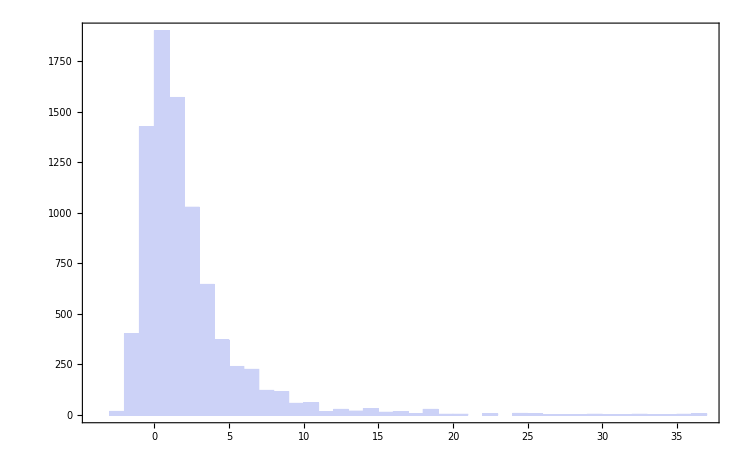

```mathematica
Histogram[#[[2]]-#[[1]]&/@bits,Axes->None,Frame->True]
```